## Common elements

```mathematica
(* Load HEPMath package *)
Needs["HEPMath`"]
DistributeDefinitions["HEPMath`Lorentz`"];
DistributeDefinitions["HEPMath`Tensors`"];

(* Declare external momenta. *)
DeclareLorentzVectors[q,k1,p1,p2,k2,l,S];

(* Declare real parameters + kinematics *)
DeclareReal[gs,e,vq,vqp,aq,aqp,eL,eH,m2,q2];
DeclareReal[s,sp,s3,s4,s5,t,tp,tpsp,t1,u,up,u1,u5,u6,u7];

norm={s-> sp+q2,s4-> sp+t1+u1,t-> t1+m2,u->u1+m2,u1p->u1-q2};
massSub={Sqr[p1]-> m2,Sqr[-p1]-> m2,Sqr[p2]-> m2,Sqr[-p2]-> m2,Sqr[q]-> q2,Sqr[-q]-> q2,Sqr[k1]-> 0,Sqr[-k1]-> 0,Sqr[k2]-> 0,Sqr[-k2]-> 0};

(* total cross section parameters *)
ηOfs[s_]=s/(4m2)-1;
sOfη[η_]=(1+η)*(4m2);
ρOfs[s_]=4m2/s;
sOfρ[ρ_]=4m2/ρ;
ηOfρ[ρ_]=1/ρ-1;
ρOfη[η_]=1/(1+η);
βOfρ[ρ_]=Sqrt[1-ρ];
ρOfβ[β_]=1-β^2;
χOfβ[β_]=(1-β)/(1+β);
βOfχ[χ_]=(1-χ)/(1+χ);
normTotalCSVars={ρ-> ρOfs[s],β-> βOfρ@ρOfs[s],η-> ηOfs[s],χ->χOfβ@βOfρ@ρOfs[s]};
ρqOfq2[q2_]=4m2/q2;
q2Ofρq[ρq_]=4m2/ρq;
βqOfρq[ρq_]=Sqrt[1-ρq];
ρqOfβq[βq_]=1-βq^2;
χqOfβq[βq_]=(βq-1)/(1+βq);
βqOfχq[χq_]= (1+χq)/(1-χq);
showq2={ρq-> ρqOfq2@q2,βq-> βqOfρq@ρqOfq2@q2,χq-> χqOfβq@βqOfρq@ρqOfq2@q2};

(* color factors *)
normColor={Kgγ-> 1/(NC^2-1),Kqγ-> 1/NC,CA->NC,CF-> (NC^2-1)/(2NC),NC-> 3};
normColor=(First@#-> (Last@#/.normColor))&/@normColor;

swapt1u1[e_]:=e//.{t1-> vu1}//.{u1-> t1}//.{vu1->u1};

(* debug tools *)
getAllSymbols=e↦ DeleteDuplicates[Reap[Map[If[Head[#]==Symbol,Sow[#]]&,e,Infinity]][[2]][[1]]];
```

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HoldPattern[HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol]] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

```mathematica
(* remove EpsDot in favour of SDot and HDot; based on HVBM(Comm.Math.Phys. Volume 52,Number 1,11-38), TRACER and Wikipedia *)
Module[{f,a1,a2,a3,a4,b1,b2,b3,b4,cache,replace,rest,replace3},
(* master formula *)
f[ps_,qs_]:=Module[{l,mus,mups,d},
l=Length[ps];
mus=Table[Unique[],{l}];
mups=Table[Unique[],{l}];
d=-Det[Table[Eta[mus[[k]],mups[[n]]]-EtaHat[mus[[k]],mups[[n]]],{k,l},{n,l}]];
(4-l)!HEPMultiply@@Join[{d},(e↦(e[[1]])[(e[[2]])])/@Transpose[{ps,mus}],(e↦(e[[1]])[(e[[2]])])/@Transpose[{qs,mups}]]
];
(* cache elements *)
cache={
EpsDot[p1_][mu_,nu_,rho_]^2:>Evaluate[LorentzContract@HEPExpand@f[{a1},{a1}]/.{a1->p1}],
EpsDot[p1_][mu_,nu_,rho_]EpsDot[k1_][mu_,nu_,rho_]:>Evaluate[LorentzContract@HEPExpand@f[{a1},{b1}]/.{a1->p1,b1->k1}],
EpsDot[p1_,p2_][mu_,nu_]^2:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2},{a1,a2}]/.{a1->p1,a2->p2}],
EpsDot[p1_,p2_][mu_,nu_]EpsDot[k1_,k2_][mu_,nu_]:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2},{b1,b2}]/.{a1->p1,a2->p2,b1->k1,b2->k2}],
EpsDot[p1_,p2_,p3_][mu_]^2:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2,a3},{a1,a2,a3}]/.{a1->p1,a2->p2,a3->p3}],
EpsDot[p1_,p2_,p3_][mu_]EpsDot[k1_,k2_,k3_][mu_]:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2,a3},{b1,b2,b3}]/.{a1->p1,a2->p2,a3->p3,b1->k1,b2->k2,b3->k3}],
EpsDot[p1_,p2_,p3_,p4_]^2:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2,a3,a4},{a1,a2,a3,a4}]/.{a1->p1,a2->p2,a3->p3,a4->p4}],
EpsDot[p1_,p2_,p3_,p4_]EpsDot[k1_,k2_,k3_,k4_]:>Evaluate[LorentzContract@HEPExpand@f[{a1,a2,a3,a4},{b1,b2,b3,b4}]/.{a1->p1,a2->p2,a3->p3,a4->p4,b1->k1,b2->k2,b3->k3,b4->k4}]
};
(* handle uncontracted *)
rest={
Eps[nus__]Eps[nups__]:> Module[{l,mus,mups,d},
l=4;
mus={nus};
mups={nups};
d=-Det[Table[Eta[mus[[k]],mups[[n]]]-EtaHat[mus[[k]],mups[[n]]],{k,l},{n,l}]];
(4-l)!HEPMultiply[d]
]
};
(* replace all *)
replace[e_]:=e/.{
Sqr[EpsDot[p1_,p2_,p3_]]:>Module[{mu},mu=Unique[];EpsDot[p1,p2,p3][mu]^2],
SDot[EpsDot[p1_,p2_,p3_],EpsDot[k1_,k2_,k3_]]:>Module[{mu},mu=Unique[];EpsDot[p1,p2,p3][mu]EpsDot[k1,k2,k3][mu]]
}/.cache/.rest;
(* function to call *)
Options[RemoveEpsDot]={"AutoParallelize"-> True};
RemoveEpsDot[ex_,OptionsPattern[]]:=Module[{e},
e=ex;
If[FreeQ[e,EpsDot]&&FreeQ[e,Eps],Return[e]];
e=SortEps@e;
If[True===OptionValue["AutoParallelize"]&&Head[e]===Plus,
e=Parallelize[Sum[replace[e[[k]]],{k,Length@e}]],
e=replace[e]];
LorentzContract@HEPExpand@e
];
(* handle 3 epsilons *)
replace3[e_]:=e/.{
(* 2 free indices *)
EpsDot[p1_,p2_][mu_,mup_] EpsDot[k1_,k2_,k3_][mu_] EpsDot[q1_,q2_,q3_][mup_]:>Module[{r,s},
r=Unique[{r1,r2}];s=Unique[{s1,s2,s3}];
EpsDot[k1,k2,k3][mu](Eps[r[[1]],r[[2]],mu,mup]Eps[s[[1]],s[[2]],s[[3]],mup]/.rest)p1[r[[1]]]p2[r[[2]]]q1[s[[1]]]q2[s[[2]]]q3[s[[3]]] ],

(* 3 free indices *)
EpsDot[p1_][mu_,mup_,nu_] EpsDot[k1_,k2_][mu_,mup_] EpsDot[q1_,q2_,q3_][nu_]:>Module[{r,s},
r=Unique[];s=Unique[{s1,s2,s3}];
EpsDot[k1,k2][mu,mup](Eps[r,mu,mup,nu]Eps[s[[1]],s[[2]],s[[3]],nu]/.rest)p1[r]q1[s[[1]]]q2[s[[2]]]q3[s[[3]]] ],

EpsDot[p1_][mu_,mup_,nu_] EpsDot[k1_,k2_][mup_,nu_] EpsDot[q1_,q2_,q3_][mu_]:>Module[{r,s},
r=Unique[];s=Unique[{s1,s2}];
EpsDot[q1,q2,q3][mu](Eps[r,mu,mup,nu]Eps[s[[1]],s[[2]],mup,nu]/.rest)p1[r]k1[s[[1]]]k2[s[[2]]] ],

EpsDot[p1_,p2_][mu_,mup_] EpsDot[k1_,k2_][mup_,nu_] EpsDot[q1_,q2_][mu_,nu_]:>Module[{r,s},
r=Unique[{r1,r2}];s=Unique[{s1,s2}];
EpsDot[p1,p2][mu,mup](Eps[r[[1]],r[[2]],mup,nu]Eps[s[[1]],s[[2]],mu,nu]/.rest)k1[r[[1]]]k2[r[[2]]]q1[s[[1]]]q2[s[[2]]] ],

(* 4 free indices *)
Eps[mu_,mup_,nu_,nup_] EpsDot[p1_,p2_][mu_,mup_] EpsDot[k1_,k2_][nu_,nup_]:>Module[{r,s},
r=Unique[];s=Unique[];
EpsDot[p1,p2][mu,mup](Eps[mu,mup,nu,nup]Eps[r,s,nu,nup]/.rest)k1[r]k2[s]]
};
Options[Remove3Eps]={"AutoParallelize"-> True};
Remove3Eps[ex_,OptionsPattern[]]:=Module[{e},
e=ex;
If[FreeQ[e,EpsDot]&&FreeQ[e,Eps],Return[e]];
e=SortEps@e;
If[True===OptionValue["AutoParallelize"]&&Head[e]===Plus,
e=Parallelize[Sum[replace3[e[[k]]],{k,Length@e}]],
e=replace3[e]];
If[True===OptionValue["AutoParallelize"]&&Head[e]===Plus,
e=Parallelize[Sum[LorentzContract@HEPExpand[e[[k]]],{k,Length@e}]],
e=LorentzContract@HEPExpand[e]];
e
];
]
```

```mathematica
Module[{k1til,Stil,r,W,getF,getg,e,f},
k1til[μ_]:=k1[μ]-SDot[k1,q]/q2 q[μ];
Stil[μ_]:=S[μ]-SDot[S,q]/q2 q[μ];
r={SDot[k1,q]-> sp/2};
W[μ_,ν_]:=2z(
(-Eta[μ,ν] + q@μ q@ν /q2) F1 
+ k1til@μ k1til@ν /(SDot[k1,q]) F2
-I Eps[μ,ν,α,β] q@α k1@β/(2SDot[k1,q])F3
+q[μ]q[ν]/q2 F4 
+(q[μ]k1[ν]+k1[μ]q[ν])/(2SDot[k1,q])F5 
+(I Eps[μ,ν,α,β]q@α/(SDot[k1,q]) (S@β g1 + (S@β-SDot[S,q]/SDot[k1,q]k1@β)*g2))
+1/SDot[k1,q](1/2(k1til@μ Stil@ν + Stil@μ k1til@ν)-SDot[S,q]/SDot[k1,q]k1til@μ k1til@ν)*g3
+SDot[S,q]/SDot[k1,q](k1til@μ k1til@ν/SDot[k1,q] g4 + (-Eta[μ,ν]+q[μ]q[ν]/q2 )g5+q[μ]q[ν]/q2 g6+(q[μ]k1[ν]+k1[μ]q[ν])/(2SDot[k1,q])g7)
)//.{z->- q2/sp};
(*Print[W[μ,ν]];*)

getF[t_]:=Module[{ex},
ex=FullSimplify[RemoveEpsDot@LorentzContract@HEPExpand@HEPMultiply[W[μ,ν],t[μ,ν]]/.massSub/.r/.{HDot[_,_]:>0}/.{sp->-q2/z}];
ex=((ex/.{S->k1})+(ex/.{S->-k1}))/2/.{SDot[-a_,b_]:>-SDot[a,b]}/.massSub/.r/.{sp->-q2/z};
FullSimplify@ex
];
proj[V][F2][μ_,ν_]:=1/(Dim-2)(- Eta[μ,ν]-4z^2/q2(Dim-1) k1[μ] k1[ν]-2z(Dim-1)/q2 (k1[μ] q[ν]+q[μ] k1[ν])- (Dim-2)/q2 q[μ] q[ν]);
e[F2]=getF[proj[V][F2]];
Print["proj[F2] = ",Collect[proj[V][F2][μ,ν],{_Eta,k1@μ k1@ν,q@μ q@ν},FullSimplify]," -> ",FullSimplify@e[F2]];
proj[V][x2F1][μ_,ν_]:=1/Dim(- Eta[μ,ν]+4z^2/q2 k1[μ] k1[ν]+2z/q2 (k1[μ] q[ν]+q[μ] k1[ν])+2 q[μ] q[ν]/q2)+2/Dim proj[V][F2][μ,ν];
e[x2F1]=getF[proj[V][x2F1]];
Print["proj[x2F1] = ",Collect[proj[V][x2F1][μ,ν],{_Eta,k1@μ k1@ν,q@μ q@ν},FullSimplify]," -> ",FullSimplify@e[x2F1]];
proj[V][FL][μ_,ν_]:=FullSimplify[proj[V][F2][μ,ν]-proj[V][x2F1][μ,ν]];
e[FL]=getF[proj[V][FL]];
Print["proj[FL] = ",Collect[HEPExpand@proj[V][FL][μ,ν],{k1@μ k1@ν,q@μ q@ν},FullSimplify]," -> ",FullSimplify@e[FL]];
proj[V][xF3][μ_,ν_]:=I/sp Eps[μ,ν,ρ,σ]q[ρ]k1[σ];
e[xF3]=getF[proj[V][xF3]];
Print["proj[xF3] = ",proj[V][xF3][μ,ν]," -> ",FullSimplify@e[xF3]];
proj[V][x2F4][μ_,ν_]:=-2z*2*(1/(q2 (Dim-2))(q2/(4z)  Eta[μ,ν]+z k1[μ]k1[ν]+(Dim-1)/2(k1[μ] q[ν]+q[μ] k1[ν])+(Dim-2)/(4z) q[μ] q[ν])+proj[V][x2F1][μ,ν]/(4z));
e[x2F4]=getF[proj[V][x2F4]];
Print["proj[x2F4] = ",Collect[HEPExpand@proj[V][x2F4][μ,ν],{k1@μ k1@ν,q@μ q@ν},FullSimplify]," -> ",FullSimplify@e[x2F4]];
proj[V][xF5][μ_,ν_]:=1/(q2)(z(k1[μ] q[ν]+q[μ] k1[ν])+ q[μ] q[ν]);
e[xF5]=getF[proj[V][xF5]];
Print["proj[xF5] = ",Collect[HEPExpand@proj[V][xF5][μ,ν],{k1@μ k1@ν,q@μ q@ν},FullSimplify]," -> ",FullSimplify@e[xF5]];
Print[];
getg[t_]:=Module[{ex},
ex=FullSimplify[RemoveEpsDot@LorentzContract@HEPExpand@HEPMultiply[W[μ,ν],t[μ,ν]]/.massSub/.r/.{HDot[_,_]:>0}/.{sp->-q2/z}];
ex=((ex/.{S->-k1})-(ex/.{S->k1}))/2/.{SDot[-a_,b_]:>-SDot[a,b]}/.massSub/.r/.{sp->-q2/z};
FullSimplify@ex
];
proj[V][x2g1][μ_,ν_]:=proj[V][xF3][μ,ν];
e[x2g1]=getg[proj[V][x2g1]];
Print["proj[x2g1] = ",Collect[proj[V][x2g1][μ,ν],{_Eta,k1@μ k1@ν,q@μ q@ν},FullSimplify]," -> ",FullSimplify@e[x2g1]];
proj[V][g4][μ_,ν_]:=-proj[V][F2][μ,ν];
e[g4]=getg[proj[V][g4]];
Print["proj[g4] = ",Collect[HEPExpand@proj[V][g4][μ,ν],{_Eta,k1@μ k1@ν,q@μ q@ν},FullSimplify]," -> ",FullSimplify@e[g4]];
proj[V][x2g5][μ_,ν_]:=-proj[V][x2F1][μ,ν];
e[x2g5]=getg[proj[V][x2g5]];
Print["proj[x2g5] = ",Collect[HEPExpand@proj[V][x2g5][μ,ν],{_Eta,k1@μ k1@ν,q@μ q@ν},FullSimplify]," -> ",FullSimplify@e[x2g5]];
proj[V][gL][μ_,ν_]:=FullSimplify[proj[V][g4][μ,ν]-proj[V][x2g5][μ,ν]];
e[gL]=getg[proj[V][gL]];
Print["proj[gL] = ",Collect[HEPExpand@proj[V][gL][μ,ν],{_Eta,k1@μ k1@ν,q@μ q@ν},FullSimplify]," -> ",FullSimplify@e[gL]];
proj[V][gG][μ_,ν_]:=FullSimplify[proj[V][x2g5][μ,ν]-1/(Dim-2)proj[V][gL][μ,ν]];
proj[V][x2g6][μ_,ν_]:=-proj[V][x2F4][μ,ν];
e[x2g6]=getg[proj[V][x2g6]];
Print["proj[x2g6] = ",Collect[HEPExpand@proj[V][x2g6][μ,ν],{_Eta,k1@μ k1@ν,q@μ q@ν},FullSimplify]," -> ",FullSimplify@e[x2g6]];
proj[V][xg7][μ_,ν_]:=-proj[V][xF5][μ,ν];
e[xg7]=getg[proj[V][xg7]];
Print["proj[xg7p] = ",Collect[HEPExpand@proj[V][xg7][μ,ν],{_Eta,k1@μ k1@ν,q@μ q@ν},FullSimplify]," -> ",FullSimplify@e[xg7]];
]
```

proj[F2] = Eta[μ,ν]/(2-Dim)-(4 (-1+Dim) z^2 k1[μ] k1[ν])/((-2+Dim) q2)-(q[μ] q[ν])/q2-(2 (-1+Dim) z (k1[ν] q[μ]+k1[μ] q[ν]))/((-2+Dim) q2) -> F2

proj[x2F1] = Eta[μ,ν]/(2-Dim)+(4 z^2 k1[μ] k1[ν])/(2 q2-Dim q2)-(2 z (k1[ν] q[μ]+k1[μ] q[ν]))/((-2+Dim) q2) -> 2 F1 z

proj[FL] = -(4 z^2 k1[μ] k1[ν])/q2-(q[μ] q[ν])/q2-(2 z (k1[ν] q[μ]+k1[μ] q[ν]))/q2 -> F2-2 F1 z

RuleDelayed::rhs: Pattern HEPMath`Tensors`Private`i_ appears on the right-hand side of rule HEPMath`Tensors`Private`indexToPattern[HEPMath`Tensors`Private`ex_, HEPMath`Tensors`Private`i_Symbol] :> {HEPMath`Tensors`Private`ex/. HEPMath`Tensors`Private`i → HEPMath`Tensors`Private`i_, {}}
.

proj[xF3] = (ⅈ Eps[μ,ν,ρ,σ] k1[σ] q[ρ])/sp -> F3 z

proj[x2F4] = -(q[μ] q[ν])/q2-(2 z (k1[ν] q[μ]+k1[μ] q[ν]))/q2 -> 2 F4 z

proj[xF5] = (q[μ] q[ν])/q2+(z (k1[ν] q[μ]+k1[μ] q[ν]))/q2 -> F5 z

proj[x2g1] = (ⅈ Eps[μ,ν,ρ,σ] k1[σ] q[ρ])/sp -> 2 g1 z

proj[g4] = Eta[μ,ν]/(-2+Dim)+(4 (-1+Dim) z^2 k1[μ] k1[ν])/((-2+Dim) q2)+(q[μ] q[ν])/q2+(2 (-1+Dim) z (k1[ν] q[μ]+k1[μ] q[ν]))/((-2+Dim) q2) -> g4

proj[x2g5] = Eta[μ,ν]/(-2+Dim)+(4 z^2 k1[μ] k1[ν])/((-2+Dim) q2)+(2 z (k1[ν] q[μ]+k1[μ] q[ν]))/((-2+Dim) q2) -> 2 g5 z

proj[gL] = (4 z^2 k1[μ] k1[ν])/q2+(q[μ] q[ν])/q2+(2 z (k1[ν] q[μ]+k1[μ] q[ν]))/q2 -> g4-2 g5 z

proj[x2g6] = (q[μ] q[ν])/q2+(2 z (k1[ν] q[μ]+k1[μ] q[ν]))/q2 -> 2 g6 z

proj[xg7p] = -(q[μ] q[ν])/q2-(z (k1[ν] q[μ]+k1[μ] q[ν]))/q2 -> g7 z

```mathematica
Collect[HEPExpand[proj[V][FL][μ,ν]-proj[V][x2F4][μ,ν]],{_Eta,k1@μ k1@ν,q@μ q@ν},FullSimplify]
```

-(4 z^2 k1[μ] k1[ν])/q2

```mathematica
Block[{$ContextPath,S,H,l0,l1,l2,l3,l4,p,k},
<<"~/Physik/PhD/Marco/Eps-out.m";
Module[{m0,m1,m2,m3,m4,n},
n[e_]:=e/.{HEPMath`Lorentz`HDot-> H,HEPMath`Tensors`SDot-> S};
DeclareLorentzVectors[_p,_k];
m0=RemoveEpsDot[Eps[μ,ν,ρ,σ]Eps[μ,ν,ρ,σ]];
m1=LorentzContract@RemoveEpsDot[EpsDot[p@1][ν,ρ,σ]EpsDot[k@1][ν,ρ,σ]];
m2=LorentzContract@RemoveEpsDot[EpsDot[p@1,p@2][ρ,σ]EpsDot[k@1,k@2][ρ,σ]];
m3=LorentzContract@RemoveEpsDot[EpsDot[p@1,p@2,p@3][σ]EpsDot[k@1,k@2,k@3][σ]];
m4=LorentzContract@RemoveEpsDot[EpsDot[p@1,p@2,p@3,p@4]EpsDot[k@1,k@2,k@3,k@4]];
Print@FullSimplify[n@m1-l1];
Print@FullSimplify[n@m2-l2];
Print@FullSimplify[n@m3-l3];
Print@FullSimplify[n@m4-l4];
]
]
```

0

0

0

«1 more identical outputs»

```mathematica
FullSimplify[LorentzContract[(RemoveEpsDot[-Eps[μ1,ν1,ρ1,σ1]Eps[μ2,ν2,ρ2,σ2]]/.{EtaHat[__]:>0})*Eta[μ1,μ2]Eta[ν1,ν2]Eta[ρ1,ρ2]Eta[σ1,σ2]]]
```

(-3+Dim) (-2+Dim) (-1+Dim) Dim

```mathematica
Module[{k1til,r,W,e},
k1til[μ_]:=k1[μ]-SDot[k1,q]/q2 q[μ];
r={SDot[k1,q]-> sp/2};
W[μ_,ν_]:=(-Eta[μ,ν] + q@μ q@ν /q2) σT + k1til@μ k1til@ν *(-4q2/sp^2)(σT+σL)/.{σT->σG+1/(Dim-2)σL};
Print[W[μ,ν]];
Print[LorentzContract@HEPExpand@HEPMultiply[k1til@μ,k1@μ]/.massSub/.r];
e[FG]=FullSimplify[LorentzContract@HEPExpand@HEPMultiply[W[μ,ν],1/(Dim-2)proj[V][FG][μ,ν]+(a k1[μ]q[ν]+b*k1[ν] q[μ]+c  q[μ]q[ν])]/.massSub/.r];
Print["k = FG: ",e[FG]];
e[FL]=FullSimplify[LorentzContract@HEPExpand@HEPMultiply[W[μ,ν],proj[V][FL][μ,ν]]/.massSub/.r];
Print["k = FL: ",e[FL]];
]
```

(σG+σL/(-2+Dim)) (-Eta[μ,ν]+(q[μ] q[ν])/q2)-(4 q2 (σG+σL+σL/(-2+Dim)) (k1[μ]-(q[μ] SDot[k1,q])/q2) (k1[ν]-(q[ν] SDot[k1,q])/q2))/sp^2

-sp^2/(4 q2)

k = FG: σG

k = FL: σL

```mathematica
Solve[(yg+(q2 ykk)/(4 z^2))==0&&(-2 q2 ykq+4 (yg+q2 yqq) z)==1&&(2 q2 ykq-2 (Dim yg+q2 yqq) z)==0&&(-q2 ykk+4 q2 ykq z-4 (yg+q2 yqq) z^2)==0,{yg,ykk,ykq,yqq}]
```

{{yg→0,ykk→0,ykq→1/(2 q2),yqq→1/(2 q2 z)}}

```mathematica
Module[{k1til,ωtil,proj,e,r},
k1til[μ_]:=k1[μ]-SDot[k1,q]/q2 q[μ];
ωtil[μ_,ν_]:=-I Eps[μ,ν,ρ,σ]q[ρ]k1[σ] g1/SDot[k1,q] + (-Eta[μ,ν]+q[μ]q[ν]/q2) g4+1/SDot[k1,q]k1til[μ] k1til[ν]g5+q[μ]q[ν]/SDot[k1,q] g6 + (k1[μ]q[ν]+k1[ν]q[μ])/SDot[k1,q]g7;
proj[1][μ_,ν_]:=I Eps[μ,ν,α,β]q[α]k1[β]/(2SDot[k1,q]);
proj[4][μ_,ν_]:=-1/2Eta[μ,ν]+z(k1[μ]q[ν]+k1[ν]q[μ])/(-q2)+2z^2k1[μ]k1[ν]/(-q2);
proj[5][μ_,ν_]:=z(-Eta[μ,ν]+2q[μ]q[ν]/(-q2)+6z(k1[μ]q[ν]+k1[ν]q[μ])/(-q2)+12z^2k1[μ]k1[ν]/(-q2));
r={SDot[k1,q]->(-q2)/(2z),Sqr[k1]->0,Sqr[q]->q2};

e[1]=FullSimplify[RemoveEpsDot@LorentzContract@HEPExpand@HEPMultiply[ωtil[μ,ν],proj[1][μ,ν]]/.r/.{HDot[_,_]:>0}];
Print["k = 1: ",e[1]];
e[4]=FullSimplify[RemoveEpsDot@LorentzContract@HEPExpand@HEPMultiply[ωtil[μ,ν],proj[4][μ,ν]]/.r/.{HDot[_,_]:>0}];
Print["k = 4: ",e[4]," -> ",e[4]/.{Dim->4}];
e[5]=FullSimplify[RemoveEpsDot@LorentzContract@HEPExpand@HEPMultiply[ωtil[μ,ν],proj[5][μ,ν]]/.r/.{HDot[_,_]:>0}];
Print["k = 5: ",e[5]," -> ",e[5]/.{Dim->4}];
]
```

k = 1: g1

k = 4: 1/2 (-2+Dim) g4 -> g4

k = 5: g5+(-4+Dim) g4 z -> g5

```mathematica
Module[{W,proj,r,getF,getg},
W[μ_,ν_]:=2mN*(
(-Eta[μ,ν]+a q[μ]q[ν]) F1/mN+k1[μ] k1[ν]/(mN SDot[k1,q])F2
+I Eps[μ,ν,α,β]/(2SDot[k1,q])*(k1[α] q[β]/mN F3+2q[α]S[β]g1-4x k1[α]S[β]g2)
-(k1[μ] S[ν]+S[μ]q[ν])/(2SDot[k1,q])g3+SDot[S,q]/SDot[k1,q]^2 k1[μ]k1[ν] g4+SDot[S,q]/SDot[k1,q]Eta[μ,ν]g5
);
r={SDot[k1,q]-> sp/2};
getF[t_]:=Module[{ex},
ex=FullSimplify[RemoveEpsDot@LorentzContract@HEPExpand@HEPMultiply[W[μ,ν],t[μ,ν]]/.massSub/.r/.{HDot[_,_]:>0}/.{sp->-q2/z}];
ex=((ex/.{S->k1})+(ex/.{S->-k1}))/2/.{SDot[-a_,b_]:>-SDot[a,b]}/.massSub/.r/.{sp->-q2/z};
Collect[ex,{F1,F2,F3,g1,g2,g3,g4,g5},FullSimplify]
];
proj[any][μ_,ν_]:=yg Eta[μ,ν]+ykk k1[μ]k1[ν]+yqq q[μ]q[ν]+yqk1 q[μ]k1[ν]+yk1q k1[μ]q[ν]+ye I Eps[μ,ν,α,β]k1[α]q[β];
Print["F ~ ",getF[proj[any]]];
proj[x2F1][μ_,ν_]:=-z/(Dim)Eta[μ,ν];
Print["proj[x2F1] = ",proj[x2F1][μ,ν]," -> ",getF[proj[x2F1]]];
proj[F2][μ_,ν_]:=-z/(q2) q[μ]q[ν]+z/(Dim)Eta[μ,ν];
Print["proj[F2] = ",proj[F2][μ,ν]," -> ",getF[proj[F2]]];
proj[F3][μ_,ν_]:=z/q2 I Eps[μ,ν,α,β]k1[α]q[β];
Print["proj[F3] = ",proj[F3][μ,ν]," -> ",getF[proj[F3]]];

getg[t_]:=Module[{ex},
ex=FullSimplify[RemoveEpsDot@LorentzContract@HEPExpand@HEPMultiply[W[μ,ν],t[μ,ν]]/.massSub/.r/.{HDot[_,_]:>0}/.{sp->-q2/z}];
ex=((ex/.{S->-k1})-(ex/.{S->k1}))/2/.{SDot[-a_,b_]:>-SDot[a,b]}/.massSub/.r/.{sp->-q2/z};
Collect[ex,{F1,F2,F3,g1,g2,g3,g4,g5},FullSimplify]
];
Print["g ~ ",getg[proj[any]]];
proj[x2g1][μ_,ν_]:=(z/mN)z/q2 I Eps[μ,ν,α,β]k1[α]q[β];
Print["proj[x2g1] = ",proj[x2g1][μ,ν]," -> ",getg[proj[x2g1]]];
]
```

F ~ (F3 q2 ye)/z-(F2 q2 yqq)/z+1/2 F1 (-4 Dim yg+(q2 (a q2 ykk-2 (-1+a q2) (yk1q+yqk1) z+4 (-yqq+a (yg+q2 yqq)) z^2))/z^2)

proj[x2F1] = -(z Eta[μ,ν])/Dim -> (2 F1 (Dim-a q2) z)/Dim

proj[F2] = (z Eta[μ,ν])/Dim-(z q[μ] q[ν])/q2 -> F2-(2 a (-1+Dim) F1 q2 z)/Dim

proj[F3] = (ⅈ z Eps[μ,ν,α,β] k1[α] q[β])/q2 -> F3

g ~ g3 (mN (yg+q2 yqq)-(mN q2 (yqk1+yqq))/(2 z))+(2 g1 mN q2 ye)/z+(g4 mN q2 yqq)/z+(g5 mN (-2 Dim yg z+q2 (yk1q+yqk1-2 yqq z)))/z

proj[x2g1] = (ⅈ z^2 Eps[μ,ν,α,β] k1[α] q[β])/(mN q2) -> 2 g1 z

```mathematica
Module[{l,c},
l=g3 (mN (yg+q2 yqq)-(mN q2 (yqk1+yqq))/(2 z))+(2 g1 mN q2 ye)/z+(g4 mN q2 yqq)/z+(g5 mN (-2 Dim yg z+q2 (yk1q+yqk1-2 yqq z)))/z;
{c[g1],c[g3],c[g4],c[g5]}=Coefficient[l,{g1,g3,g4,g5}];
Solve[c[g1]==1&&c[g3]==0&&c[g4]==0&&c[g5]==0,{ye,yg,yqq,yk1q,yqk1}]
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ye→z/(2 mN q2),yqq→0,yk1q→-yg ((2 z)/q2-(2 Dim z)/q2),yqk1→(2 yg z)/q2}}

## LO V(q)+g(k1) → Q(p1)+Qbar(p2)

### Computation

#### HEPMath way

```mathematica
Module[{l,r,mxBornu1,mxBornt1,me},
l=-DiracTr[Ga[ν].(u1 GI+2Sqrt@m2 Gs[q]).G5.(Gs[p2]-Sqrt@m2 GI).(-G5).(u1 GI + 2Sqrt@m2 Gs[q]).Ga[ν].(Gs[p1]+Sqrt@m2 GI)];
Print@l;
l=CalcDiracTraces@l;
l=l/.{HDot[_,_]->0}/.{
SDot[q,k1]-> sp/2,SDot[p1,p2]->(sp+q2-2m2)/2,
SDot[k1,p2]-> -t1/2, SDot[q,p1]->-(t1-q2)/2,
SDot[p1,k1]-> -u1/2,SDot[q,p2]-> -(u1-q2)/2
}/.{
Sqr[p1]-> m2,Sqr[-p1]-> m2,Sqr[p2]-> m2,Sqr[-p2]-> m2,
Sqr[q]-> q2,Sqr[-q]-> q2,Sqr[k1]-> 0,Sqr[-k1]-> 0
}/.{Dim->n};
Print@Expand@l;
r=-32*m2^2*q2-8*m2*q2^2+8*m2*q2*s+8*m2*q2*sp+16*m2*q2*t1-8*m2*sp*u1+4*q2*sp*u1-2*n*q2*sp*u1-8*m2*t1*u1+4*q2*t1*u1-2*n*q2*t1*u1-4*sp*u1^2+2*n*sp*u1^2;
Print@FullSimplify[l- r/.{s->sp+q2}/.{sp->-t1-u1}];
mxBornu1[v_,a_][μ_]:=(Bar[USp[p1]][r1].Ga[ν].(u1 GI + 2Sqrt@m2 Gs[q]).G5.VSp[p2][r2])*Pol[k1][λg,ν];
mxBornt1[v_,a_][μ_]:=(Bar[USp[p1]][r1].(t1 GI + 2Sqrt@m2 Gs[q]).G5.Ga[ν].VSp[p2][r2])*Pol[k1][λg,ν];
me=HEPMultiply[mxBornu1[v,a][μ],CC[mxBornu1[vp,ap][μp]]];
me = FermionPolarizationSums[me, {p1->Sqrt[m2], p2->Sqrt[m2]}];
me = VectorPolarizationSums[me, {k1->0}];
Print@me;
me=CalcDiracTraces[DiracExpand@me];
me=LorentzContract@me;
me=HEPExpand@me;
me=LorentzContract@me;
me=me/.{HDot[_,_]->0}/.{
SDot[q,k1]-> sp/2,SDot[p1,p2]->(sp+q2-2m2)/2,
SDot[k1,p2]-> -t1/2, SDot[q,p1]->-(t1-q2)/2,
SDot[p1,k1]-> -u1/2,SDot[q,p2]-> -(u1-q2)/2
}/.{
Sqr[p1]-> m2,Sqr[-p1]-> m2,Sqr[p2]-> m2,Sqr[-p2]-> m2,
Sqr[q]-> q2,Sqr[-q]-> q2,Sqr[k1]-> 0,Sqr[-k1]-> 0
}/.{Dim->n};
me=Expand[me]/.{1/SDot[k1,ng]->0,Sqr[ng]->0};
Print@FullSimplify[me/.{sp->-t1-u1}];
Print@FullSimplify[l- me/.{s->sp+q2}/.{sp->-t1-u1}];
]
```

-DiracTr[Ga[ν].(GI u1+2 √m2 Gs[q]).G5.(-GI √m2+Gs[p2]).(-G5).(GI u1+2 √m2 Gs[q]).Ga[ν].(GI √m2+Gs[p1])]

-32 m2^2 q2+16 m2 q2 sp-8 m2 n q2 sp+16 m2 q2 t1-8 m2 n q2 t1-8 m2 n q2 u1+8 m2 u1^2-4 q2 u1^2+2 n q2 u1^2-4 sp u1^2+2 n sp u1^2

0

-DiracTr[(-GI √m2+Gs[p2]).(-G5).(GI u1+2 √m2 Gs[q]).Ga[$311].(GI √m2+Gs[p1]).Ga[$310].(GI u1+2 √m2 Gs[q]).G5] Eta[$310,$311]

-2 (16 m2^2 q2+4 m2 (2 q2-u1) u1-(-2+n) (q2-t1-u1) u1^2)

0

```mathematica
Module[{l,r,mxBornu1,mxBornt1,me},
DeclareLorentzVectors[ng];
mxBornu1[μ_]:=(Bar[USp[p1]][r1].Ga[ν].(u1 GI + 2Sqrt@m2 Gs[q]).G5.VSp[p2][r2])/u1*Pol[k1][λg,ν];
mxBornt1[μ_]:=(Bar[USp[p1]][r1].(t1 GI + 2Sqrt@m2 Gs[q]).G5.Ga[ν].VSp[p2][r2])/t1*Pol[k1][λg,ν];
me=HEPMultiply[mxBornu1[μ]+mxBornt1[μ],CC[mxBornu1[μp]+mxBornt1[μp]]];
me = FermionPolarizationSums[me, {p1->Sqrt[m2], p2->Sqrt[m2]}];
me = VectorPolarizationSums[me, {k1->ng}];
Print@me;
me=CalcDiracTraces[DiracExpand@me];
me=LorentzContract@me;
me=HEPExpand@me;
me=LorentzContract@me;
me=me/8/.{HDot[_,_]->0}/.{
SDot[q,k1]-> sp/2,SDot[p1,p2]->(sp+q2-2m2)/2,
SDot[k1,p2]-> -t1/2, SDot[q,p1]->-(t1-q2)/2,
SDot[p1,k1]-> -u1/2,SDot[q,p2]-> -(u1-q2)/2
}/.{
Sqr[p1]-> m2,Sqr[-p1]-> m2,Sqr[p2]-> m2,Sqr[-p2]-> m2,
Sqr[q]-> q2,Sqr[-q]-> q2,Sqr[k1]-> 0,Sqr[-k1]-> 0
}/.{Dim->4+ϵ};
me=Collect[me/.{sp->-t1-u1}/.{SDot[ng,q]->SDot[ng,p1]+SDot[ng,p2]-SDot[ng,k1]},{ϵ,SDot@__},FullSimplify];
Print@me;
Print@getB[post][A,A,Fqq]
]
```

DeclareHEPTensor::redecl: HEPTensor ng already declared.

(DiracTr[(-GI √m2+Gs[p2]).(-G5).(GI u1+2 √m2 Gs[q]).Ga[$1656].(GI √m2+Gs[p1]).Ga[$1655].(GI u1+2 √m2 Gs[q]).G5]/u1^2+DiracTr[(-GI √m2+Gs[p2]).(-G5).(GI u1+2 √m2 Gs[q]).Ga[$1656].(GI √m2+Gs[p1]).(GI t1+2 √m2 Gs[q]).G5.Ga[$1655]]/(t1 u1)+DiracTr[(-GI √m2+Gs[p2]).Ga[$1656].(-G5).(GI t1+2 √m2 Gs[q]).(GI √m2+Gs[p1]).Ga[$1655].(GI u1+2 √m2 Gs[q]).G5]/(t1 u1)+DiracTr[(-GI √m2+Gs[p2]).Ga[$1656].(-G5).(GI t1+2 √m2 Gs[q]).(GI √m2+Gs[p1]).(GI t1+2 √m2 Gs[q]).G5.Ga[$1655]]/t1^2) (-Eta[$1655,$1656]+(k1[$1656] ng[$1655]+k1[$1655] ng[$1656])/SDot[k1,ng]-(k1[$1655] k1[$1656] Sqr[ng])/SDot[k1,ng]^2)

(2 m2 (-2 m2 q2 (t1+u1)^2+t1 u1 (2 q2^2-2 q2 (t1+u1)+(t1+u1)^2)))/(t1^2 u1^2)-((m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1)

(2 m2 (-2 m2 q2 (t1+u1)^2+t1 u1 (2 q2^2-2 q2 (t1+u1)+(t1+u1)^2)))/(t1^2 u1^2)-((m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1)

```mathematica
getB[symg5][A,A,Fqq]
getB[Larin][A,A,Fqq]
```

(2 m2 (-2 m2 q2 (t1+u1)^2+t1 u1 (2 q2^2-2 q2 (t1+u1)+(t1+u1)^2)))/(t1^2 u1^2)-((m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1)

(2 m2 (-2 m2 q2 (t1+u1)^2+t1 u1 (2 q2^2-2 q2 (t1+u1)+(t1+u1)^2)))/(t1^2 u1^2)-((m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1)

```mathematica
Module[{v,a,vp,ap,mxBornt1,mxBornu1,me,c},
DeclareLorentzVectors[ng];
DeclareReal[v,a,vp,ap,m2];
mxBornt1[v_,a_][μ_]:=(Bar[USp[p1]][r1].(v*Ga[μ]+a*Ga[μ].G5).((Gs[k1-p2]+Sqrt[m2] GI)).(Ga[ν]).VSp[p2][r2])/(t1)*Pol[k1][λg,ν];
mxBornu1[v_,a_][μ_]:=(Bar[USp[p1]][r1].(Ga[ν]).((Gs[p1-k1]+Sqrt[m2] GI)).(v*Ga[μ]+a*Ga[μ].G5).VSp[p2][r2])/(u1)*Pol[k1][λg,ν];
me=HEPMultiply[mxBornt1[v,a][μ],CC[mxBornt1[vp,ap][μp]]];
me = FermionPolarizationSums[me, {p1->Sqrt[m2], p2->Sqrt[m2]}];
me = VectorPolarizationSums[me, {k1->ng}];
Print@me;
me=CalcDiracTraces[DiracExpand@me];
me=HEPMultiply[me,q[μ],q[μp](*,Eta[ν,νp]*)];
me=LorentzContract@me;
me=HEPExpand@me;
me=LorentzContract@me;
me=me/8/.{HDot[_,_]->0}/.{
SDot[q,k1]-> sp/2,SDot[p1,p2]->(sp+q2-2m2)/2,
SDot[k1,p2]-> -t1/2, SDot[q,p1]->-(t1-q2)/2,
SDot[p1,k1]-> -u1/2,SDot[q,p2]-> -(u1-q2)/2
}/.{
Sqr[p1]-> m2,Sqr[-p1]-> m2,Sqr[p2]-> m2,Sqr[-p2]-> m2,
Sqr[q]-> q2,Sqr[-q]-> q2,Sqr[k1]-> 0,Sqr[-k1]-> 0
};
me=Collect[me,{v,a,vp,ap},FullSimplify];
Print@me;
]
```

DeclareHEPTensor::redecl: HEPTensor ng already declared.

1/t1^2 DiracTr[(-GI √m2+Gs[p2]).Ga[$1783].(GI √m2+Gs[k1-p2]).(ap$39137 (-G5).Ga[μp]+vp$39137 Ga[μp]).(GI √m2+Gs[p1]).(a$39137 Ga[μ].G5+v$39137 Ga[μ]).(GI √m2+Gs[k1-p2]).Ga[$1782]] (-Eta[$1782,$1783]+(k1[$1783] ng[$1782]+k1[$1782] ng[$1783])/SDot[k1,ng]-(k1[$1782] k1[$1783] Sqr[ng])/SDot[k1,ng]^2)

1/(4 t1^2 SDot[k1,ng]^2)vp$39137 v$39137 ((m2 (-4 t1 (sp+u1)+8 q2 (sp+t1+u1))-t1 (2 t1 (q2+sp-u1)+Dim (-sp t1+q2 (sp+u1)))) SDot[k1,ng]^2-2 t1 SDot[k1,ng] (q2 t1 SDot[ng,p1]+(t1 (sp+2 u1)-q2 (3 sp+2 t1+3 u1)) SDot[ng,p2]+t1 (-q2+t1) SDot[ng,q])+t1^2 (-t1 u1+q2 (sp+t1+u1)) Sqr[ng])+1/(4 t1^2 SDot[k1,ng]^2)ap$39137 a$39137 (-(16 m2^2 q2+4 m2 (t1 (sp+u1)-2 q2 (sp+t1+u1))+t1 (2 t1 (q2+sp-u1)+Dim (-sp t1+q2 (sp+u1)))) SDot[k1,ng]^2-2 t1 SDot[k1,ng] (q2 t1 SDot[ng,p1]+(8 m2 q2+t1 (sp+2 u1)-q2 (3 sp+2 t1+3 u1)) SDot[ng,p2]+t1 (-q2+t1) SDot[ng,q])+t1^2 (-4 m2 q2-t1 u1+q2 (sp+t1+u1)) Sqr[ng])

```mathematica
ap$62026 a$62026 (-(32 Dim m2^2)/t1^2-(32 Dim m2 SDot[ng,p2])/(t1 SDot[k1,ng])-(8 Dim m2 Sqr[ng])/SDot[k1,ng]^2)
```

```mathematica
ap$64162 a$64162 (-(32 Dim m2^2)/u1^2-(32 Dim m2 SDot[ng,p1])/(u1 SDot[k1,ng])-(8 Dim m2 Sqr[ng])/SDot[k1,ng]^2)
```

```mathematica
ap$65555 ((16 Dim m2 (-1+SDot[ng,p1]/SDot[k1,ng]))/u1+((16 Dim m2 (-2 m2+q2))/u1+16 Dim m2 (-1+SDot[ng,p2]/SDot[k1,ng]))/t1+4 ((-4+Dim)^2+(2 Dim m2 Sqr[ng])/SDot[k1,ng]^2))
```

```mathematica
Collect[B[A,A,FG]-B[V,V,FG],{t1,u1},FullSimplify]
```

(16 m2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1^2 u1^2)+(4 m2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1^2 u1^2)-ϵ^2

#### Load from Tracer

```mathematica
Block[{$ContextPath,BB,get},
<<"/home/Felix/Physik/PhD/MMa/data/BB.m";
get[cur1_,cur2_,pol_,k_]:=Module[{f},
f=Sum[BB[cur1,cur2,ch1,ch2][pol,k]/ch1/ch2,{ch1,{t1,u1}},{ch2,{t1,u1}}]/8;
f=f//.{s->sp+q2,sp->-t1-u1,n->4+ϵ,epsi@__->0};
f=Collect[f,ϵ,FullSimplify]
];
Module[{l},
l=Tuples[{{V,Apre,Apost},{V,Apre,Apost},{F,g},{Pg,Pk1k1,Peps,Pqq,Pk1q}}];
BList[def]=(#->(get@@#))&/@l;
];
Module[{symB},
symB[V,V,pol_,k_]:={V,V,pol,k}/.BList@def;
symB[V,A,pol_,k_]:=1/2(({V,Apost,pol,k}/.BList@def)-({V,Apre,pol,k}/.BList@def));
symB[A,V,pol_,k_]:=1/2(({Apost,V,pol,k}/.BList@def)-({Apre,V,pol,k}/.BList@def));
symB[A,A,pol_,k_]:=1/4(({Apost,Apost,pol,k}/.BList@def)+({Apre,Apre,pol,k}/.BList@def)-({Apost,Apre,pol,k}/.BList@def)-({Apre,Apost,pol,k}/.BList@def));

B[cur1_,cur2_,F2]:=(1/(n-2)symB[cur1,cur2,F,Pg]+(n-1)/(n-2)symB[cur1,cur2,F,Pk1k1]+symB[cur1,cur2,F,Pqq]+(n-1)/(n-2)symB[cur1,cur2,F,Pk1q])/.{n->4+ϵ};
B[cur1_,cur2_,FL]:=symB[cur1,cur2,F,Pk1k1]+symB[cur1,cur2,F,Pqq]+symB[cur1,cur2,F,Pk1q];
B[cur1_,cur2_,xF3]:=symB[cur1,cur2,F,Peps];

B[cur1_,cur2_,x2g1]:=symB[cur1,cur2,g,Peps];
B[cur1_,cur2_,g4]:=-(1/(n-2)symB[cur1,cur2,g,Pg]+(n-1)/(n-2)symB[cur1,cur2,g,Pk1k1]+symB[cur1,cur2,g,Pqq]+(n-1)/(n-2)symB[cur1,cur2,g,Pk1q])/.{n->4+ϵ};
B[cur1_,cur2_,gL]:=-(symB[cur1,cur2,g,Pk1k1]+symB[cur1,cur2,g,Pqq]+symB[cur1,cur2,g,Pk1q]);
];
]
```

```mathematica
(*Do[B[cur1,cur2,FT]=Series[B[cur1,cur2,FG]+1/(n-2)B[cur1,cur2,FL]/.{n->4+ϵ},{ϵ,0,2}];,{cur1,{V,A}},{cur2,{V,A}}];*)
Module[{k,f,g},
k=#;
Print["k = ",k];
f=vq vqp B[V,V,k]+vq*aqp*B[V,A,k]+aq*vqp*B[A,V,k]+aq aqp B[A,A,k];
g=(vq vqp+aq aqp)*B[V,V,k];
Print@FullSimplify@Series[f-g,{ϵ,0,1}];
]&/@{F2,FL,x2g1};
Module[{k,f,g},
k=#;
Print["k = ",k];
f=vq vqp B[V,V,k]+vq*aqp*B[V,A,k]+aq*vqp*B[A,V,k]+aq aqp B[A,A,k];
Print@FullSimplify@Series[f/(vq aqp+aq vqp),{ϵ,0,1}];
]&/@{xF3,gL,g4};
```

k = F2

-(2 (aq aqp m2 (t1+u1)^2))/(q2 t1 u1)+(aq aqp (-8 m2^2 q2 (t1+u1)^2+2 m2 (-4 q2 t1 u1 (t1+u1)+2 t1 u1 (t1+u1)^2+q2^2 (t1^2+6 t1 u1+u1^2))+t1 u1 (-2 q2^3+2 q2^2 (t1+u1)+4 t1 u1 (t1+u1)-q2 (t1^2+8 t1 u1+u1^2))) ϵ)/(4 q2 t1^2 u1^2)+O[ϵ]^2

k = FL

-(2 (aq aqp m2 (2 m2 q2 (t1+u1)^2+t1 u1 (-2 q2^2+2 q2 (t1+u1)+(t1+u1)^2))))/(q2 t1^2 u1^2)+(aq aqp (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(q2 t1 u1)+O[ϵ]^2

k = x2g1

0

k = xF3

((t1-u1) (2 m2 q2 (t1+u1)^2-t1 u1 (2 q2^2-2 q2 (t1+u1)+(t1+u1)^2)))/(2 t1^2 u1^2 (t1+u1))+(-t1/(4 u1)+u1/(4 t1)) ϵ+O[ϵ]^2

k = gL

0

k = g4

-((t1-u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)))/(2 (t1^2 u1^2))+((t1-u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) ϵ)/(4 t1^2 u1^2)+O[ϵ]^2

#### position of γ5

```mathematica
Block[{$ContextPath,BB,get},
<<("/home/Felix/Physik/PhD/MMa/data/BB/"<>ToString[#]<>".m");
get[cur1_,cur2_,k_]:=Module[{f},
f=Sum[BB[cur1,cur2,ch1,ch2][k]/ch1/ch2,{ch1,{t1,u1}},{ch2,{t1,u1}}]/8;
f=f//.{s->sp+q2,sp->-t1-u1,n->4+ϵ};
f=Collect[f,ϵ,FullSimplify]
];
Module[{l},
l=Tuples[{{V,A},{V,A},{FG,FL,xF3,x2g1,gG,gL,Fk1q,Fqk1,Fqq,gk1q,gqk1,gqq}}];
BList[#]=(#->(get@@#))&/@l;
];
getB[#][cur1_,cur2_,proj_]:=({cur1,cur2,proj}/.BList[#]);
]&/@{symP,Larin};
```

```mathematica
Block[{$ContextPath,BB,get},
<<("/home/Felix/Physik/PhD/MMa/data/BB/symg5.m");
get[cur1_,cur2_,k_]:=Module[{f},
f=Sum[BB[cur1,cur2,ch1,ch2][k]/ch1/ch2,{ch1,{t1,u1}},{ch2,{t1,u1}}]/8;
f=f//.{s->sp+q2,sp->-t1-u1,n->4+ϵ};
f=Collect[f,ϵ,FullSimplify]
];
Module[{l},
l=Tuples[{{V,Apre,Apost},{V,Apre,Apost},{FG,FL,xF3,x2g1,gG,gL,Fk1q,Fqk1,Fqq,gk1q,gqk1,gqq}}];
BList[symg5]=(#->(get@@#))&/@l;
];
getB[symg5][V,V,proj_]:=({V,V,proj}/.BList[symg5]);
getB[symg5][V,A,proj_]:=Collect[(({V,Apost,proj}/.BList[symg5])-({V,Apre,proj}/.BList[symg5]))/2,ϵ,FullSimplify];
getB[symg5][A,V,proj_]:=Collect[(({Apost,V,proj}/.BList[symg5])-({Apre,V,proj}/.BList[symg5]))/2,ϵ,FullSimplify];
getB[symg5][A,A,proj_]:=Collect[(({Apost,Apost,proj}/.BList[symg5])-({Apost,Apre,proj}/.BList[symg5])-({Apre,Apost,proj}/.BList[symg5])+({Apre,Apre,proj}/.BList[symg5]))/4,ϵ,FullSimplify];

getB[post][cur1_,cur2_,proj_]:=({If[A===cur1,Apost,cur1],If[A===cur2,Apost,cur2],proj}/.BList[symg5]);
getB[pre][cur1_,cur2_,proj_]:=({If[A===cur1,Apre,cur1],If[A===cur2,Apre,cur2],proj}/.BList[symg5]);
]
```

```mathematica
Module[{k,f,g},
k=#;
Print["k = ",k];
f=vq vqp getB[symP][V,V,k]+vq*aqp*getB[symP][V,A,k]+aq*vqp*getB[symP][A,V,k]+aq aqp getB[symP][A,A,k];
g=((vq+2aq) (vqp+2aqp)+4aq aqp)*getB[symP][V,V,k];
Print@Collect[f,ϵ,FullSimplify];
Print@Collect[(f-g),ϵ,FullSimplify];
]&/@{FG,FL,x2g1};
Module[{k,f,g},
k=#;
Print["k = ",k];
f=vq vqp getB[symP][V,V,k]+vq*aqp*getB[symP][V,A,k]+aq*vqp*getB[symP][A,V,k]+aq aqp getB[symP][A,A,k];
Print@Collect[f,ϵ,FullSimplify];
(*Print@Collect[f/((vq+2aq)2 aqp+2aq (vqp+2aqp)),ϵ,FullSimplify];*)
]&/@{xF3,gL,gG};
```

k = FG

1/(t1^2 u1^2)(8 aq aqp (4 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (-2 t1 u1 (t1+u1)+q2 (t1^2+4 t1 u1+u1^2)))-2 aq (4 m2^2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))+2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2))) vqp-(4 m2^2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))+2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2))) vq (2 aqp+vqp))+((aqp t1 u1 (t1+u1)^2 vq+(-m2 q2 (t1+u1)^2+t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1))) vq vqp+aq u1 (4 aqp t1 (t1^2+u1^2)+t1 (t1+u1)^2 vqp)) ϵ)/(t1^2 u1^2)+((t1+u1)^2 vq vqp ϵ^2)/(4 t1 u1)

(64 aq aqp m2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1^2 u1^2)+((4 aq aqp (2 m2 q2 (t1+u1)^2-t1 u1 (2 q2^2-2 q2 (t1+u1)+(t1+u1)^2))+aqp (2 m2 q2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))) vq+aq (2 m2 q2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))) vqp) ϵ)/(t1^2 u1^2)-((t1+u1)^2 (aqp vq+aq (4 aqp+vqp)) ϵ^2)/(2 t1 u1)

k = FL

(4 q2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (vq (2 aqp+vqp)+2 aq (4 aqp+vqp)))/(t1 u1 (t1+u1)^2)

0

k = x2g1

-((t1^2+u1^2) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) (vq (2 aqp+vqp)+2 aq (4 aqp+vqp)))/(2 t1^2 u1^2 (t1+u1))

0

k = xF3

((t1-u1) (2 m2 q2 (t1+u1)^2-t1 u1 (2 q2^2-2 q2 (t1+u1)+(t1+u1)^2)) (aqp vq+aq (4 aqp+vqp)))/(t1^2 u1^2 (t1+u1))-((t1-u1) (t1+u1) (aqp vq+aq (4 aqp+vqp)) ϵ)/(2 t1 u1)

k = gL

0

k = gG

-(2 (t1-u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) (aqp vq+aq (4 aqp+vqp)))/(t1^2 u1^2)

```mathematica
(*Do[B[cur1,cur2,FT]=Series[B[cur1,cur2,FG]+1/(n-2)B[cur1,cur2,FL]/.{n->4+ϵ},{ϵ,0,2}];,{cur1,{V,A}},{cur2,{V,A}}];*)
Module[{k,f,g},
k=#;
Print["k = ",k];
f=vq vqp getB[symg5][V,V,k]+vq*aqp*getB[symg5][V,A,k]+aq*vqp*getB[symg5][A,V,k]+aq aqp getB[symg5][A,A,k];
g=(vq vqp+aq aqp)*getB[symg5][V,V,k];
Print@Collect[f,ϵ,FullSimplify];
Print@Collect[f-g,ϵ,FullSimplify];
]&/@{FG,FL,x2g1};
Module[{k,f,g},
k=#;
Print["k = ",k];
f=vq vqp getB[symg5][V,V,k]+vq*aqp*getB[symg5][V,A,k]+aq*vqp*getB[symg5][A,V,k]+aq aqp getB[symg5][A,A,k];
Print@Collect[f,ϵ,FullSimplify];
(*Print@Collect[f/(vq aqp+aq vqp),ϵ,FullSimplify];*)
]&/@{xF3,gL,gG};
```

k = FG

(aq aqp (12 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (-6 t1 u1 (t1+u1)+q2 (t1^2+8 t1 u1+u1^2)))-(4 m2^2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))+2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2))) vq vqp)/(t1^2 u1^2)+((aq aqp t1 (t1-u1)^2 u1-2 (m2 q2 (t1+u1)^2-t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1))) vq vqp) ϵ)/(2 t1^2 u1^2)+((t1+u1)^2 vq vqp ϵ^2)/(4 t1 u1)

(16 aq aqp m2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1^2 u1^2)+(aq aqp (2 m2 q2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+4 t1 u1+u1^2-2 q2 (t1+u1))) ϵ)/(2 t1^2 u1^2)-(aq aqp (t1+u1)^2 ϵ^2)/(4 t1 u1)

k = FL

(4 q2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (aq aqp+vq vqp))/(t1 u1 (t1+u1)^2)

0

k = x2g1

-((t1^2+u1^2) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) (aq aqp+vq vqp))/(2 t1^2 u1^2 (t1+u1))

0

k = xF3

((t1-u1) (2 m2 q2 (t1+u1)^2-t1 u1 (2 q2^2-2 q2 (t1+u1)+(t1+u1)^2)) (aqp vq+aq vqp))/(2 t1^2 u1^2 (t1+u1))-((t1-u1) (t1+u1) (aqp vq+aq vqp) ϵ)/(4 t1 u1)

k = gL

0

k = gG

-((t1-u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) (aqp vq+aq vqp))/(t1^2 u1^2)

```mathematica
(*Do[B[cur1,cur2,FT]=Series[B[cur1,cur2,FG]+1/(n-2)B[cur1,cur2,FL]/.{n->4+ϵ},{ϵ,0,2}];,{cur1,{V,A}},{cur2,{V,A}}];*)
Module[{k,f,g},
k=#;
Print["k = ",k];
f=vq vqp getB[Larin][V,V,k]+vq*aqp*getB[Larin][V,A,k]+aq*vqp*getB[Larin][A,V,k]+aq aqp getB[Larin][A,A,k];
g=(vq vqp+aq aqp)*getB[Larin][V,V,k];
Print@Collect[f,ϵ,FullSimplify];
Print@Collect[f-g,ϵ,FullSimplify];
]&/@{FG,FL,x2g1};
Module[{k,f,g},
k=#;
Print["k = ",k];
f=vq vqp getB[symg5][V,V,k]+vq*aqp*getB[symg5][V,A,k]+aq*vqp*getB[symg5][A,V,k]+aq aqp getB[symg5][A,A,k];
Print@Collect[f,ϵ,FullSimplify];
(*Print@Collect[f/(vq aqp+aq vqp),ϵ,FullSimplify];*)
]&/@{xF3,gL,gG};
```

k = FG

(aq aqp (12 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (-6 t1 u1 (t1+u1)+q2 (t1^2+8 t1 u1+u1^2)))-(4 m2^2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))+2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2))) vq vqp)/(t1^2 u1^2)+((aq aqp t1 (t1-u1)^2 u1-2 (m2 q2 (t1+u1)^2-t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1))) vq vqp) ϵ)/(2 t1^2 u1^2)+((t1+u1)^2 vq vqp ϵ^2)/(4 t1 u1)

(16 aq aqp m2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1^2 u1^2)+(aq aqp (2 m2 q2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+4 t1 u1+u1^2-2 q2 (t1+u1))) ϵ)/(2 t1^2 u1^2)-(aq aqp (t1+u1)^2 ϵ^2)/(4 t1 u1)

k = FL

(4 q2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) (aq aqp+vq vqp))/(t1 u1 (t1+u1)^2)

0

k = x2g1

-((t1^2+u1^2) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) (aq aqp+vq vqp))/(2 t1^2 u1^2 (t1+u1))

0

k = xF3

((t1-u1) (2 m2 q2 (t1+u1)^2-t1 u1 (2 q2^2-2 q2 (t1+u1)+(t1+u1)^2)) (aqp vq+aq vqp))/(2 t1^2 u1^2 (t1+u1))-((t1-u1) (t1+u1) (aqp vq+aq vqp) ϵ)/(4 t1 u1)

k = gL

0

k = gG

-((t1-u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) (aqp vq+aq vqp))/(t1^2 u1^2)

```mathematica
Module[{k},
k=#;
{
FullSimplify[B[V,V,k]-getB[symP][V,V,k]],
FullSimplify[B[V,V,k]- getB[symP][V,A,k]/2],
FullSimplify[B[V,V,k]- getB[symP][A,V,k]/2],
FullSimplify[B[V,V,k]+ B[A,A,k]- getB[symP][A,A,k]/4]
}
]&/@{FG,FL,x2g1}
```

{{0,(ϵ (-4 m2 q2 (t1+u1)^2+t1 u1 (4 q2^2-4 q2 (t1+u1)+2 (t1^2+u1^2)+(t1+u1)^2 ϵ)))/(4 t1^2 u1^2),(ϵ (-4 m2 q2 (t1+u1)^2+t1 u1 (4 q2^2-4 q2 (t1+u1)+2 (t1^2+u1^2)+(t1+u1)^2 ϵ)))/(4 t1^2 u1^2),(ϵ (8 m2^2 (t1+u1)^2-4 m2 (-2 t1 u1 (t1+u1)+q2 (t1^2+4 t1 u1+u1^2))+t1 u1 (4 q2^2-4 q2 (t1+u1)+2 (t1+u1)^2+(t1^2+u1^2) ϵ)))/(2 t1^2 u1^2)},{0,0,0,0},{0,0,0,0}}

```mathematica
Module[{k},
k=#;
{
FullSimplify[B[V,V,k]-getB[symg5][V,V,k]],
FullSimplify[B[V,A,k]-getB[symg5][V,A,k]],
FullSimplify[B[A,V,k]-getB[symg5][A,V,k]],
FullSimplify[B[A,A,k]-getB[symg5][A,A,k]]
}
]&/@{FG,FL,x2g1}
```

{{0,0,0,(ϵ (16 m2^2 (t1+u1)^2-4 m2 (-4 t1 u1 (t1+u1)+q2 (t1^2+6 t1 u1+u1^2))+t1 u1 (4 q2^2-4 q2 (t1+u1)+2 (t1^2+4 t1 u1+u1^2)+(t1-u1)^2 ϵ)))/(4 t1^2 u1^2)},{0,0,0,0},{0,0,0,0}}

```mathematica
Module[{k},
k=#;
{
FullSimplify[getB[post][V,V,k]-getB[pre][V,V,k]],
FullSimplify[getB[post][V,A,k]-getB[pre][V,A,k]],
FullSimplify[getB[post][A,V,k]-getB[pre][A,V,k]],
FullSimplify[getB[post][A,A,k]- getB[pre][A,A,k]]
}
]&/@{FG,FL,x2g1}
Module[{k},
k=#;
{
FullSimplify[getB[post][V,V,k]-getB[pre][V,V,k]],
FullSimplify[getB[post][V,A,k]+getB[pre][V,A,k]],
FullSimplify[getB[post][A,V,k]+getB[pre][A,V,k]],
FullSimplify[getB[post][A,A,k]-getB[pre][A,A,k]]
}
]&/@{xF3,gG,gL}
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,((t1+u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) ϵ)/(t1^2 u1^2),((t1+u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) ϵ)/(t1^2 u1^2),0},{0,0,0,0}}

```mathematica
Module[{k},
k=#;
{
FullSimplify[getB[symg5][V,V,k]-getB[Larin][V,V,k]],
FullSimplify[getB[symg5][V,A,k]-getB[Larin][V,A,k]],
FullSimplify[getB[symg5][A,V,k]-getB[Larin][A,V,k]],
FullSimplify[getB[symg5][A,A,k]-getB[Larin][A,A,k]]
}
]&/@{FG,FL,x2g1}
Module[{k},
k=#;
{
FullSimplify[getB[symg5][V,V,k]-getB[Larin][V,V,k]],
FullSimplify[getB[symg5][V,A,k]-getB[Larin][V,A,k]],
FullSimplify[getB[symg5][A,V,k]-getB[Larin][A,V,k]],
FullSimplify[getB[symg5][A,A,k]-getB[Larin][A,A,k]]
}
]&/@{xF3,gG,gL}
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
getB[post][A,A,FG]
getB[pre][A,A,FG]
getB[symP][A,A,FG]
getB[symg5][A,A,FG]
```

(12 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (-6 t1 u1 (t1+u1)+q2 (t1^2+8 t1 u1+u1^2)))/(t1^2 u1^2)+((4 m2^2 (t1+u1)^2+t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1))-m2 (-4 t1 u1 (t1+u1)+q2 (t1^2+6 t1 u1+u1^2))) ϵ)/(t1^2 u1^2)+((t1-u1)^2 ϵ^2)/(4 t1 u1)

(12 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (-6 t1 u1 (t1+u1)+q2 (t1^2+8 t1 u1+u1^2)))/(t1^2 u1^2)+((4 m2^2 (t1+u1)^2+t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1))-m2 (-4 t1 u1 (t1+u1)+q2 (t1^2+6 t1 u1+u1^2))) ϵ)/(t1^2 u1^2)+((t1-u1)^2 ϵ^2)/(4 t1 u1)

(8 (4 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (-2 t1 u1 (t1+u1)+q2 (t1^2+4 t1 u1+u1^2))))/(t1^2 u1^2)+((4 t1)/u1+(4 u1)/t1) ϵ

(12 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (-6 t1 u1 (t1+u1)+q2 (t1^2+8 t1 u1+u1^2)))/(t1^2 u1^2)+((t1-u1)^2 ϵ)/(2 t1 u1)

```mathematica
getB[post][V,A,gG]
getB[pre][V,A,gG]
getB[symP][V,A,gG]
getB[symg5][V,A,gG]
```

-((t1-u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)))/(t1^2 u1^2)+((t1+u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) ϵ)/(2 t1^2 u1^2)

((t1-u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)))/(t1^2 u1^2)+((t1+u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) ϵ)/(2 t1^2 u1^2)

-(2 (t1-u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)))/(t1^2 u1^2)

-((t1-u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)))/(t1^2 u1^2)

```mathematica
getB[post][A,V,gG]
getB[pre][A,V,gG]
getB[symP][A,V,gG]
getB[symg5][A,V,gG]
```

-((t1-u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)))/(t1^2 u1^2)+((t1+u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) ϵ)/(2 t1^2 u1^2)

((t1-u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)))/(t1^2 u1^2)+((t1+u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) ϵ)/(2 t1^2 u1^2)

-(2 (t1-u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)))/(t1^2 u1^2)

-((t1-u1) (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)))/(t1^2 u1^2)

```mathematica
getB[symg5][V,V,FG]
{getB[symg5][V,V,Fk1q],getB[symg5][V,V,Fqk1],getB[symg5][V,V,Fqq]}
{getB[symg5][V,A,Fk1q],getB[symg5][V,A,Fqk1],getB[symg5][V,A,Fqq]}
```

(-4 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2)))/(t1^2 u1^2)+((-m2 q2 (t1+u1)^2+t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1))) ϵ)/(t1^2 u1^2)+((t1+u1)^2 ϵ^2)/(4 t1 u1)

{0,0,0}

{(ⅈ (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) epsi[k1,p1,p2,q])/(t1^2 u1^2),-(ⅈ (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) epsi[k1,p1,p2,q])/(t1^2 u1^2),(ⅈ (t1+u1) ϵ epsi[k1,p1,p2,q])/(t1 u1)}

```mathematica
getB[symg5][A,A,FG]
getB[symg5][A,A,Fk1q]
getB[symg5][A,A,Fqk1]
getB[symg5][A,A,Fqq]
```

(12 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (-6 t1 u1 (t1+u1)+q2 (t1^2+8 t1 u1+u1^2)))/(t1^2 u1^2)+((t1-u1)^2 ϵ)/(2 t1 u1)

(2 m2 (t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1^2 u1^2)

(2 m2 (t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1^2 u1^2)

(2 m2 (-2 m2 q2 (t1+u1)^2+t1 u1 (2 q2^2-2 q2 (t1+u1)+(t1+u1)^2)))/(t1^2 u1^2)-((m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1)

```mathematica
Collect[getB[symg5][V,V,FG]-((1+ϵ/2)getB[symg5][A,A,FG]-4/(t1+u1) (1+3/8ϵ)(getB[symg5][A,A,Fqk1]+getB[symg5][A,A,Fk1q])),{ϵ},FullSimplify]
```

2 ϵ+ϵ^2

```mathematica
getB[post][V,V,FG]
{getB[post][V,V,Fk1q],getB[post][V,V,Fqk1],getB[post][V,V,Fqq]}
```

(-4 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2)))/(t1^2 u1^2)+((-m2 q2 (t1+u1)^2+t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1))) ϵ)/(t1^2 u1^2)+((t1+u1)^2 ϵ^2)/(4 t1 u1)

{0,0,0}

```mathematica
getB[post][A,A,FG]
Simplify@Together@getB[post][A,A,FL]
getB[post][A,A,Fk1q]
getB[post][A,A,Fqk1]
getB[post][A,A,Fqq]
```

(12 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (-6 t1 u1 (t1+u1)+q2 (t1^2+8 t1 u1+u1^2)))/(t1^2 u1^2)+((4 m2^2 (t1+u1)^2+t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1))-m2 (-4 t1 u1 (t1+u1)+q2 (t1^2+6 t1 u1+u1^2))) ϵ)/(t1^2 u1^2)+((t1-u1)^2 ϵ^2)/(4 t1 u1)

-(4 q2 (-m2 (t1+u1)^2-t1 u1 (-q2+t1+u1)))/(t1 u1 (t1+u1)^2)

(2 m2 (t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1^2 u1^2)

(2 m2 (t1+u1) (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1^2 u1^2)

(2 m2 (-2 m2 q2 (t1+u1)^2+t1 u1 (2 q2^2-2 q2 (t1+u1)+(t1+u1)^2)))/(t1^2 u1^2)-((m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1)

```mathematica
FullSimplify[getB[post][A,A,Fk1q]/getB[post][A,A,FL]]
```

(m2 (t1+u1)^3)/(2 q2 t1 u1)

```mathematica
Collect[getB[post][V,V,FG]-(getB[post][A,A,FG]-4/(t1+u1)(1+ϵ/4)(getB[post][A,A,Fqk1]+getB[post][A,A,Fk1q])),{ϵ},FullSimplify]
Collect[getB[pre][V,V,FG]-(getB[pre][A,A,FG]-4/(t1+u1)(1+ϵ/4) (getB[pre][A,A,Fqk1]+getB[pre][A,A,Fk1q])),{ϵ},FullSimplify]
```

ϵ^2

ϵ^2

```mathematica
{getB[symg5][V,A,Fk1q],getB[symg5][V,A,Fqk1],getB[symg5][V,A,Fqq]}
{getB[symg5][A,V,Fk1q],getB[symg5][A,V,Fqk1],getB[symg5][A,V,Fqq]}
{getB[post][V,A,Fk1q],getB[post][V,A,Fqk1],getB[post][V,A,Fqq]}
{getB[pre][V,A,Fk1q],getB[pre][V,A,Fqk1],getB[pre][V,A,Fqq]}
```

{(ⅈ (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) epsi[k1,p1,p2,q])/(t1^2 u1^2),-(ⅈ (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) epsi[k1,p1,p2,q])/(t1^2 u1^2),(ⅈ (t1+u1) ϵ epsi[k1,p1,p2,q])/(t1 u1)}

{(ⅈ (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) epsi[k1,p1,p2,q])/(t1^2 u1^2),-(ⅈ (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) epsi[k1,p1,p2,q])/(t1^2 u1^2),-(ⅈ (t1+u1) ϵ epsi[k1,p1,p2,q])/(t1 u1)}

{(ⅈ (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) epsi[k1,p1,p2,q])/(t1^2 u1^2),-(ⅈ (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) epsi[k1,p1,p2,q])/(t1^2 u1^2),(ⅈ (t1+u1) ϵ epsi[k1,p1,p2,q])/(t1 u1)}

{-(ⅈ (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) epsi[k1,p1,p2,q])/(t1^2 u1^2),(ⅈ (2 m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) epsi[k1,p1,p2,q])/(t1^2 u1^2),-(ⅈ (t1+u1) ϵ epsi[k1,p1,p2,q])/(t1 u1)}

```mathematica
getB[symg5][A,A,gG]
getB[symg5][A,A,gk1q]
getB[symg5][A,A,gqk1]
getB[symg5][A,A,gqq]
```

0

(ⅈ (t1-u1) epsi[k1,p1,p2,q])/(t1 u1)

-(ⅈ (t1-u1) epsi[k1,p1,p2,q])/(t1 u1)

0

```mathematica
1/(Dim-2)(- Eta[μ,ν]-4z^2/q2(Dim-1) k1[μ] k1[ν]-2z(Dim-1)/q2 (k1[μ] q[ν]+q[μ] k1[ν])- (Dim-2)/q2 q[μ] q[ν])
```

```mathematica
Module[{getF2},
getF2[pos_,cur1_,cur2_]:=Collect[getB[pos][cur1,cur2,FG]+(Dim-1)getB[pos][cur1,cur2,FL]-2z(Dim-1)/q2(getB[pos][cur1,cur2,Fk1q]+getB[pos][cur1,cur2,Fqk1])-(Dim-2)/q2 getB[pos][cur1,cur2,Fqq]//.{Dim->4+ϵ,z->-q2/sp,sp->-t1-u1},{ϵ},FullSimplify];
Print[getF2[symg5,V,V]];
Print[getF2[symg5,A,A]];
Print["Check: F2 = FG+3/2FL"];
Print@Collect[getF2[symg5,V,V]-(getB[symg5][V,V,FG]+(3+ϵ)getB[symg5][V,V,FL]),ϵ,FullSimplify];
Print@Collect[getF2[symg5,A,A]-(getB[symg5][A,A,FG]+(3+ϵ)getB[symg5][A,A,FL]),ϵ,FullSimplify];
Print["Check: VV-AA"];
Print@Collect[getF2[symg5,V,V]-getF2[symg5,A,A],{ϵ},FullSimplify];
Print@Collect[getF2[Larin,V,V]-getF2[Larin,A,A],{ϵ},FullSimplify];
Print@Collect[getF2[post,V,V]-getF2[post,A,A],{ϵ},FullSimplify];
Print@Collect[getF2[pre,V,V]-getF2[pre,A,A],{ϵ},FullSimplify];
]
```

12 q2 (m2/(t1 u1)+(-q2+t1+u1)/(t1+u1)^2)+(-4 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2)))/(t1^2 u1^2)+(4 q2 (m2/(t1 u1)+(-q2+t1+u1)/(t1+u1)^2)+(-m2 q2 (t1+u1)^2+t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1)))/(t1^2 u1^2)) ϵ+((t1+u1)^2 ϵ^2)/(4 t1 u1)

(-4 m2^2 q2 (t1+u1)^4-2 m2 (t1+u1)^2 (2 q2 t1 u1 (t1+u1)+2 t1 u1 (t1+u1)^2+q2^2 (t1^2-6 t1 u1+u1^2))+q2 t1 u1 ((t1+u1)^2 (t1^2+u1^2)+2 q2^2 (t1^2-4 t1 u1+u1^2)-2 q2 (t1+u1) (t1^2-4 t1 u1+u1^2)))/(q2 t1^2 u1^2 (t1+u1)^2)+((8 m2 q2 t1 (2 q2-t1-u1) u1 (t1+u1)^2-8 m2^2 q2 (t1+u1)^4+t1 u1 (-8 q2^3 t1 u1+8 q2^2 t1 u1 (t1+u1)+4 t1 u1 (t1+u1)^3+q2 (t1+u1)^2 (t1^2-6 t1 u1+u1^2))) ϵ)/(2 q2 t1^2 u1^2 (t1+u1)^2)+((m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ^2)/(q2 t1 u1)

Check: F2 = FG+3/2FL

0

-(4 m2 (4 m2 q2 (t1+u1)^2+t1 u1 (-4 q2^2+4 q2 (t1+u1)+(t1+u1)^2)))/(q2 t1^2 u1^2)-(2 (2 m2^2 q2 (t1+u1)^2+2 m2 q2 t1 u1 (-q2+t1+u1)-t1^2 u1^2 (-q2+t1+u1)) ϵ)/(q2 t1^2 u1^2)+((m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ^2)/(q2 t1 u1)

Check: VV-AA

(4 m2 (t1+u1)^2)/(q2 t1 u1)+((8 m2^2 q2 (t1+u1)^2-2 m2 q2 (-4 t1 u1 (t1+u1)+q2 (t1^2+6 t1 u1+u1^2))+t1 u1 (2 q2^3-2 q2^2 (t1+u1)-4 t1 u1 (t1+u1)+q2 (t1^2+8 t1 u1+u1^2))) ϵ)/(2 q2 t1^2 u1^2)+((-4 t1 u1 (t1+u1)-4 m2 (t1+u1)^2+q2 (t1^2+6 t1 u1+u1^2)) ϵ^2)/(4 q2 t1 u1)

(4 m2 (t1+u1)^2)/(q2 t1 u1)+((8 m2^2 q2 (t1+u1)^2-2 m2 q2 (-4 t1 u1 (t1+u1)+q2 (t1^2+6 t1 u1+u1^2))+t1 u1 (2 q2^3-2 q2^2 (t1+u1)-4 t1 u1 (t1+u1)+q2 (t1^2+8 t1 u1+u1^2))) ϵ)/(2 q2 t1^2 u1^2)+((-4 t1 u1 (t1+u1)-4 m2 (t1+u1)^2+q2 (t1^2+6 t1 u1+u1^2)) ϵ^2)/(4 q2 t1 u1)

(4 m2 (t1+u1)^2)/(q2 t1 u1)+(2 (q2-t1-u1) ϵ)/q2-((m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) ϵ^2)/(q2 t1 u1)

(4 m2 (t1+u1)^2)/(q2 t1 u1)+(2 (q2-t1-u1) ϵ)/q2-((m2 (t1+u1)^2+t1 u1 (-2 q2+t1+u1)) ϵ^2)/(q2 t1 u1)

```mathematica
-((q2*Eta[μ, ν] + 2*z*(k1[ν]*q[μ] + k1[μ]*(2*z*k1[ν] + q[ν])))/((Dim - 2)*q2))
```

```mathematica
Module[{get2xF1},
get2xF1[pos_,cur1_,cur2_]:=Collect[getB[pos][cur1,cur2,FG]+getB[pos][cur1,cur2,FL]-2z/q2(getB[pos][cur1,cur2,Fk1q]+getB[pos][cur1,cur2,Fqk1])//.{Dim->4+ϵ,z->-q2/sp,sp->-t1-u1},{ϵ},FullSimplify];
Print[get2xF1[symg5,V,V]];
Print[get2xF1[symg5,A,A]];
Print["Check: 2xF1 = FG+1/2FL"];
Print@Collect[get2xF1[symg5,V,V]-(getB[symg5][V,V,FG]+getB[symg5][V,V,FL]),ϵ,FullSimplify];
Print@Collect[get2xF1[symg5,A,A]-(getB[symg5][A,A,FG]+getB[symg5][A,A,FL]),ϵ,FullSimplify];
Print["Check: VV-AA"];
Print@Collect[get2xF1[symg5,V,V]-get2xF1[symg5,A,A],{ϵ},FullSimplify];
Print@Collect[get2xF1[Larin,V,V]-get2xF1[Larin,A,A],{ϵ},FullSimplify];
Print@Collect[get2xF1[post,V,V]-get2xF1[post,A,A],{ϵ},FullSimplify];
Print@Collect[get2xF1[pre,V,V]-get2xF1[pre,A,A],{ϵ},FullSimplify];
]
```

(-4 m2^2 (t1+u1)^2-2 m2 (q2 (t1-u1)^2+2 t1 u1 (t1+u1))+(t1 u1 (t1^2+u1^2) (2 q2^2-2 q2 (t1+u1)+(t1+u1)^2))/(t1+u1)^2)/(t1^2 u1^2)+((-m2 q2 (t1+u1)^2+t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1))) ϵ)/(t1^2 u1^2)+((t1+u1)^2 ϵ^2)/(4 t1 u1)

(4 m2^2 (t1+u1)^4-2 m2 (t1+u1)^3 (-2 t1 u1+q2 (t1+u1))+t1 u1 (t1^2+u1^2) (2 q2^2-2 q2 (t1+u1)+(t1+u1)^2))/(t1^2 u1^2 (t1+u1)^2)+((t1-u1)^2 ϵ)/(2 t1 u1)

Check: 2xF1 = FG+1/2FL

0

-(8 m2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1^2 u1^2)

Check: VV-AA

-(8 m2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1^2 u1^2)+((-2 m2 q2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+4 t1 u1+u1^2-2 q2 (t1+u1))) ϵ)/(2 t1^2 u1^2)+((t1+u1)^2 ϵ^2)/(4 t1 u1)

-(8 m2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1^2 u1^2)+((-2 m2 q2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+4 t1 u1+u1^2-2 q2 (t1+u1))) ϵ)/(2 t1^2 u1^2)+((t1+u1)^2 ϵ^2)/(4 t1 u1)

-(8 m2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1^2 u1^2)-(4 m2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1^2 u1^2)+ϵ^2

-(8 m2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)))/(t1^2 u1^2)-(4 m2 (m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1^2 u1^2)+ϵ^2

#### Check to Nucl.Phys.B 392-162

```mathematica
Module[{BGQEDref,BLQEDref},
BGQEDref = t1/u1 + u1/t1 + 4m2 sp/(t1 u1)(1-m2 sp/(t1 u1)) + 2 sp q2/(t1 u1) + 2q2^2/(t1 u1) +2m2 q2/(t1 u1)(2- sp^2/(t1 u1))+ϵ(-1+(sp^2+sp q2 + q2^2)/(t1 u1) - m2 q2 sp^2/(t1^2 u1^2)) + ϵ^2sp^2/(4t1 u1);
BLQEDref = -4q2/sp((sp+q2)/sp-m2 sp/(t1 u1));
{Collect[FullSimplify[B[V,V,FL]-(BLQEDref/.{sp-> -t1-u1})],ϵ],
Collect[FullSimplify[(B[V,V,F2])-(1/(2+ϵ)BGQEDref+(3+ϵ)/(2+ϵ)BLQEDref/.{sp-> -t1-u1})],ϵ]}
]
```

{0,0}

#### check to Marco

```mathematica
Block[{$ContextPath},
Marco`B[V,V,x2g1] = << "~/Physik/PhD/Marco/recalc/data/BPQED"//.{u1p->u1-q2,s->sp+q2}/.{sp-> -t1-u1};
Simplify[((Marco`B[V,V,x2g1]/2/.{m^2-> m2})-B[V,V,x2g1])]
]
```

0

#### Check to NPB147-147

```mathematica
B[V,V,F2]
```

(4 q2 (m2/(t1 u1)+(-q2+t1+u1)/(t1+u1)^2) (3+ϵ))/(2+ϵ)+((-4 m2^2 (t1+u1)^2+t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))-2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2)))/(t1^2 u1^2)+((-m2 q2 (t1+u1)^2+t1 u1 (q2^2+t1^2+t1 u1+u1^2-q2 (t1+u1))) ϵ)/(t1^2 u1^2)+((t1+u1)^2 ϵ^2)/(4 t1 u1))/(2+ϵ)

```mathematica
Module[{p,pQ,pQp,Q,QS,QA,get,f,tqq,tk1q},
DeclareLorentzVectors[p,pQ,pQp];
DeclareReal[mQ,mQp,Qpl,Qmi,RQ];
QS[pQ_,mQ_,pQp_,mQp_][μ_,ν_]:=-4/SDot[p,pQ]^2*(
Eta[μ,ν]*(Qpl*(SDot[p,pQ]SDot[p,pQp]+mQ^2SDot[p,pQp]-mQ^2SDot[pQ,pQp])
+mQ mQp Qmi(SDot[p,pQ]-mQ^2)) - (p[μ]pQp[ν]+pQp[μ]p[ν])Qpl(mQ^2+SDot[p,pQ])
+(pQ[μ]pQp[ν]+pQp[μ]pQ[ν])Qpl mQ^2
)-4/(SDot[p,pQ]SDot[p,pQp])*(
Eta[μ,ν]*(Qpl*(mQ^2 SDot[p,pQ]-2SDot[p,pQ]SDot[pQ,pQp]+SDot[pQ,pQp]^2)+mQ mQp Qmi(SDot[pQ,pQp]-SDot[p,pQ]))
-2pQp[μ]pQp[ν]Qpl SDot[p,pQ]+p[μ]p[ν]Qmi mQ mQp
+(p[μ]pQp[ν]+pQp[μ]p[ν])Qpl SDot[pQ,pQp]+(pQ[μ]pQp[ν]+pQp[μ]pQ[ν])Qpl(SDot[p,pQ]-SDot[pQ,pQp])
);
QA[pQ_,mQ_,pQp_,mQp_][μ_,ν_]:=-4/SDot[p,pQ]^2*(2I Eps[μ,ν,σ,σp]p[σ]pQp[σp] RQ(mQ^2+SDot[p,pQ])-2 I Eps[μ,ν,σ,σp]pQ[σ]pQp[σp] RQ mQ^2)-4/(SDot[p,pQ]SDot[p,pQp])*(2I Eps[μ,ν,σ,σp]pQp[σ]p[σp]RQ SDot[pQ,pQp]+2I Eps[μ,ν,σ,σp]pQ[σ]pQp[σp]RQ(SDot[pQ,pQp]-SDot[p,pQ]));
Q[μ_,ν_]:=QS[pQ,mQ,pQp,mQp][μ,ν]+QS[pQp,mQp,pQ,mQ][μ,ν]+QA[pQ,mQ,pQp,mQp][μ,ν]-QA[pQp,mQp,pQ,mQ][μ,ν];
Print["check sym: ",SortEps@FullSimplify[Q[μ,ν]-(Q[ν,μ]/.{mQ->mQp,mQp->mQ,pQ->pQp,pQp->pQ})]];
get[t_]:=Module[{b},
b=HEPMultiply[t[μ,ν],Q[μ,ν]];
b=RemoveEpsDot@LorentzContract@HEPExpand@b;
b=b/.{HDot[__]->0}/.{p->k1,pQ->p1,pQp->p2,mQ->Sqrt@m2,mQp->Sqrt@m2};
b=b/8/.{
SDot[q,k1]-> sp/2,SDot[p1,p2]->(sp+q2-2m2)/2,
SDot[k1,p2]-> -t1/2, SDot[q,p1]->-(t1-q2)/2,
SDot[p1,k1]-> -u1/2,SDot[q,p2]-> -(u1-q2)/2
}/.{
Sqr[p1]-> m2,Sqr[-p1]-> m2,Sqr[p2]-> m2,Sqr[-p2]-> m2,
Sqr[q]-> q2,Sqr[-q]-> q2,Sqr[k1]-> 0,Sqr[-k1]-> 0
}/.{Dim->4+ϵ}/.{sp->-t1-u1};
FullSimplify@b
];
{f[F2vv],f[F2aa]}=Coefficient[get[proj[V][F2]]/.{Qpl->v2+a2,Qmi->v2-a2,z->-q2/sp}/.{sp->-t1-u1},{v2,a2}];
Print["F2|_VV = ",FullSimplify[B[V,V,F2]-f[F2vv]]];
Print["F2|_AA = ",FullSimplify[B[A,A,F2]-f[F2aa]]];
{f[Lvv],f[Laa]}=Coefficient[get[proj[V][FL]]/.{Qpl->v2+a2,Qmi->v2-a2,z->-q2/sp}/.{sp->-t1-u1},{v2,a2}];
Print["FL|_VV = ",FullSimplify[B[V,V,FL]-f[Lvv]]];
Print["FL|_AA = ",FullSimplify[B[A,A,FL]-f[Laa]]];
f[3]=Coefficient[get[proj[V][xF3]],RQ];
Print["xF3 = ",Collect[B[V,A,xF3]+B[A,V,xF3]-f[3],ϵ,FullSimplify]];
tk1q[μ_,ν_]:=k1[μ]q[ν];
{f[k1qvv],f[k1qaa]}=Coefficient[get[tk1q]/.{Qpl->v2+a2,Qmi->v2-a2},{v2,a2}];
Print["Fk1q|_VV = ",FullSimplify[getB[symg5][V,V,Fk1q]-f[k1qvv]]];
Print["Fk1q|_AA = ",FullSimplify[getB[symg5][A,A,Fk1q]-f[k1qaa]]];
tqq[μ_,ν_]:=q[μ]q[ν];
{f[qqvv],f[qqaa]}=Coefficient[get[tqq]/.{Qpl->v2+a2,Qmi->v2-a2},{v2,a2}];
Print["Fqq|_VV = ",FullSimplify[getB[symg5][V,V,Fqq]-f[qqvv]]];
Print["Fqq|_AA = ",FullSimplify[getB[symg5][A,A,Fqq]-f[qqaa]]];
]
```

check sym: 0

F2|_VV = ((t1+u1)^2 ϵ)/(4 t1 u1)

F2|_AA = (ϵ (-4 m2^2 q2 (t1+u1)^2+m2 (-4 q2 t1 u1 (t1+u1)+q2^2 (t1^2+6 t1 u1+u1^2)+t1 u1 (t1+u1)^2 (2+ϵ))+t1 u1 (-q2^3+q2^2 (t1+u1)+t1 u1 (t1+u1) (2+ϵ)-q2 t1 u1 (3+ϵ))))/(q2 t1^2 u1^2 (2+ϵ))

FL|_VV = 0

FL|_AA = ((m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(q2 t1 u1)

xF3 = 1/4 (-(2 t1)/u1+(2 u1)/t1) ϵ

Fk1q|_VV = 0

Fk1q|_AA = 0

Fqq|_VV = 0

Fqq|_AA = -((m2 (t1+u1)^2+t1 u1 (-q2+t1+u1)) ϵ)/(t1 u1)

```mathematica
Module[{R,p,l,c,s,prj},
R[μ_,ν_]:=-Eta[μ,ν] R1+k1[μ]k1[ν]R2-I/2Eps[μ,ν,ρ,σ]k1[ρ]q[σ]R3+1/2(k1[μ]q[ν]+q[μ]k1[ν])R4+q[μ]q[ν]R5;
p[μ_,ν_]:=-Eta[μ,ν] yg+k1[μ]k1[ν]ykk-I/2Eps[μ,ν,ρ,σ]k1[ρ]q[σ]ye+1/2(k1[μ]q[ν]+q[μ]k1[ν])ykq+q[μ]q[ν]yqq;
l=RemoveEpsDot@LorentzContract@HEPExpand@HEPMultiply[R[μ,ν],p[μ,ν]];
l=l/.{HDot[__]->0}/.{Sqr[k1]->0,Sqr[q]->q2,SDot[k1,q]->sp/2};
c=Coefficient[l,{R1,R2,R3,R4,R5}];
prj={};
Do[
s=First@Solve[MapIndexed[If[k==First@#2,1,0]==#1&,c],{yg,ykk,ye,ykq,yqq}];
AppendTo[prj,{μ,ν}↦Evaluate[p[μ,ν]/.s]];
Print["proj[",k,"] = ",Last[prj][μ,ν]]
,{k,Length@c}];
Print["check 2xF1: ",FullSimplify[prj[[1]][μ,ν]-proj[V][x2F1][μ,ν]/.{z->-q2/sp}]];
Print["check F2: ",FullSimplify[prj[[2]][μ,ν]*sp^2/(4(-q2))-proj[V][F2][μ,ν]/.{z->-q2/sp}]];
]
```

proj[1] = Eta[μ,ν]/(2-Dim)-(4 q2 k1[μ] k1[ν])/((-2+Dim) sp^2)+(2 (k1[ν] q[μ]+k1[μ] q[ν]))/((-2+Dim) sp)

proj[2] = (4 q2 Eta[μ,ν])/((-2+Dim) sp^2)+(16 (-1+Dim) q2^2 k1[μ] k1[ν])/((-2+Dim) sp^4)+(4 q[μ] q[ν])/sp^2-(8 (-1+Dim) q2 (k1[ν] q[μ]+k1[μ] q[ν]))/((-2+Dim) sp^3)

proj[3] = (4 ⅈ Eps[μ,ν,ρ,σ] k1[ρ] q[σ])/sp^2

proj[4] = -(4 Eta[μ,ν])/((-2+Dim) sp)-(16 (-q2+Dim q2) k1[μ] k1[ν])/((-2+Dim) sp^3)+(4 Dim (k1[ν] q[μ]+k1[μ] q[ν]))/((-2+Dim) sp^2)

proj[5] = (4 k1[μ] k1[ν])/sp^2

check 2xF1: 0

check F2: 0

```mathematica
Module[{R,RS,t},
RS[5][mQ_,mQp_]:=-2π MN2 Qpl(-sqrtλ/SDot[p,q]^2+2mQ^2ψ[mQ,mQp]/SDot[p,q]^2);
R[5]=RS[5][mQ,mQp]+RS[5][mQp,mQ];
t[e_]:=Collect[-2m2^2/ρq/sp/MN2*e//.{mQ->Sqrt@m2,mQp->Sqrt@m2,SDot[p,q]->sp/2,Qpl->v2+a2,sqrtλ->s β,ψ[Sqrt@m2,Sqrt@m2]->-ln@χ,sp->s-q2,s->sOfρ@ρ,q2->q2Ofρq@ρq},{ln@_,β},FullSimplify];
Print[R@5//t];
Print["check F5|_VV: me - ref = ",FullSimplify[v2*cg0[V,V,FL]+a2*cg0[Apost,Apost,FL]-t[R@5]]];
]
```

(2 π (a2+v2) β ρ^2 ρq^2)/(ρ-ρq)^3+(π (a2+v2) ρ^3 ρq^2 ln[χ])/(ρ-ρq)^3

check F5|_VV: me - ref = 0

```mathematica
Module[{R,RS,t,ref},
RS[1][mQ_,mQp_]:=-2π/SDot[p,q]^2 (Qmi mQ mQp+Qpl(Δ2-SDot[p,q])^2/Δ2)sqrtλ
+π ψ[mQ,mQp]/SDot[p,q]^2*(2mQ mQp Qmi (Δ2-mQ^2-mQp^2)+Qpl SDot[p,q]^2+Qpl(γ2[mQ,mQp]-SDot[p,q])^2);
R[1]=RS[1][mQ,mQp]+RS[1][mQp,mQ];
t[e_]:=Collect[m2/2/sp*e//.{mQ->Sqrt@m2,mQp->Sqrt@m2,SDot[p,q]->sp/2,Qpl->v2+a2,Qmi->v2-a2,sqrtλ->s β,ψ[Sqrt@m2,Sqrt@m2]->-ln@χ,γ2[Sqrt@m2,Sqrt@m2]->Δ2,Δ2->s,sp->s-q2,s->sOfρ@ρ,q2->q2Ofρq@ρq},{ln@_,β},FullSimplify];
ref=t[R@1];
Print@ref;
Print["check 2xF1|_VV: me - ref = ",FullSimplify[cg0[V,V,F2]-cg0[V,V,FL]-Coefficient[ref,v2]]];
Print["check 2xF1|_AA: me - ref = ",FullSimplify[cg0[A,A,F2]-cg0[A,A,FL]-Coefficient[ref,a2]]];
]
```

(π β ρ ρq ((a2+v2) ρ^2+2 (a2+v2) ρ ρq+(a2+v2-a2 ρ+v2 ρ) ρq^2))/(2 (ρ-ρq)^3)+((2 π (a2+v2) ρ^3 ρq+π ρ (v2 (2-(-2+ρ) ρ)+a2 (2+(-2+ρ) ρ)) ρq^3) ln[χ])/(4 (ρ-ρq)^3)

check 2xF1|_VV: me - ref = 0

check 2xF1|_AA: me - ref = 0

```mathematica
Module[{R,RS,t,ref},
RS[2][mQ_,mQp_]:=-2π MN2 (
Qpl sqrtλ/2*(-18/SDot[p,q]^2+4/(Δ2 SDot[p,q])+(2(Δ2+mQ^2+mQp^2)+14Δ2)/SDot[p,q]^3-(3Δ2(Δ2+mQ^2+mQp^2)+sqrtλ^2)/SDot[p,q]^4)
+ψ[mQ,mQp]*(-2Qpl/SDot[p,q]+(Qpl*3γ2[mQ,mQp]+6Qpl mQ^2+2Qmi mQ mQp)/SDot[p,q]^2
-Qpl*(2γ2[mQ,mQp]^2-4mQ^2mQp^2+10mQ^2Δ2)/SDot[p,q]^3
+Qpl*(γ2[mQ,mQp]^2(Δ2-mQ^2-mQp^2)+8mQ^2Δ2 γ2[mQ,mQp]-4mQ^4 γ2[mQ,mQp])/(2SDot[p,q]^4))
);
R[2]=RS[2][mQ,mQp]+RS[2][mQp,mQ];
t[e_]:=Collect[-sp m2/q2/MN2/8*e//.{mQ->Sqrt@m2,mQp->Sqrt@m2,SDot[p,q]->sp/2,Qpl->v2+a2,Qmi->v2-a2,sqrtλ->s β,ψ[Sqrt@m2,Sqrt@m2]->-ln@χ,γ2[Sqrt@m2,Sqrt@m2]->Δ2,Δ2->s,sp->s-q2,s->sOfρ@ρ,q2->q2Ofρq@ρq},{ln@_,β},FullSimplify];
ref=t[R@2];
ref=Collect[ref/.{β^3->β*βOfρ[ρ]^2},{ln@_,β},FullSimplify];
Print@ref;
Print["check F2|_VV: me - ref = ",Collect[cg0[V,V,F2]-Coefficient[ref,v2],{ln@_,β},FullSimplify]];
Print["check F2|_AA: me - ref = ",Collect[cg0[A,A,F2]-Coefficient[ref,a2],{ln@_,β},FullSimplify]];
]
```

(π (a2+v2) β ρ ρq (ρ^2+ρq^2+ρ ρq (6+ρq)))/(2 (ρ-ρq)^3)+(π ρ ρq (2 (a2+v2) ρ^2+2 (a2+2 v2) ρ^2 ρq+(2 (a2+v2)+2 (3 a2+v2) ρ-(a2+v2) ρ^2) ρq^2-2 a2 ρq^3) ln[χ])/(4 (ρ-ρq)^3)

check F2|_VV: me - ref = 0

check F2|_AA: me - ref = 0

#### export to c++

```mathematica
Module[{path,put},
path = "/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/BQED/";
put[e_,fp_]:=Module[{f,out},
f=Collect[e/.{ϵ->0}/.{t1+u1->-sp},{sp,t1,u1}];
Print@fp;
out=OpenWrite[fp];
WriteString[out,ToString@CForm@f];
Close[out];
];
Do[
put[B[V,V,k],path<>"BQED_"<>ToString[k]<>"_VV.c"];
put[B[A,A,k],path<>"BQED_"<>ToString[k]<>"_AA.c"];
,{k,{F2,FL,x2g1}}];
Do[
put[B[V,A,k],path<>"BQED_"<>ToString[k]<>"_VA.c"];
,{k,{xF3,g4,gL}}];
]
```

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/BQED/BQED_F2_VV.c

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/BQED/BQED_F2_AA.c

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/BQED/BQED_FL_VV.c

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/BQED/BQED_FL_AA.c

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/BQED/BQED_x2g1_VV.c

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/BQED/BQED_x2g1_AA.c

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/BQED/BQED_xF3_VA.c

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/BQED/BQED_g4_VA.c

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/BQED/BQED_gL_VA.c

### integrate to cg0

```mathematica
Block[{$Assumptions={m2>0,0≤ β≤ 1,0<χq<1,0<θ1<π,0<χ<1}},Module[{jac,I,l},
jac=-sp/2;
I[el_]:=Module[{e,J,j},
e=(B@@el)*4π m2/(sp^2)*Kgγ NC CF/.{ϵ->0}/.normColor;
e=e/.{u1->-sp-t1}/.{t1->-sp/2*v};

e=FullSimplify[jac*e];
J=Integrate[e,v]/.{Log@z_:>ln@z};
j=(J/.{v->(1-β)})-(J/.{v->(1+β)});
j=j/.{ln[1-β]->ln[χ]+ln[1+β]}/.{sp->s-q2}//.{s->sOfρ@ρ,q2->q2Ofρq@ρq};
j=Collect[j,{ln@_},FullSimplify]/.{β^2->βOfρ[ρ]^2};
j=Collect[j,{ln@_,β},FullSimplify]/.{β^3->β βOfρ[ρ]^2};
j=Collect[j,{ln@_,β},FullSimplify];
el->j
];
l=Tuples[{{V,A},{V,A},{F2,FL,xF3,x2g1,g4,gL}}];
cg0List[def]=I[#]&/@l;
cg0[cur1_,cur2_,proj_]:={cur1,cur2,proj}/.cg0List[def];
cg0List[def]
]]
```

{{V,V,F2}→(π β ρ ρq (ρ^2+ρq^2+ρ ρq (6+ρq)))/(2 (ρ-ρq)^3)+(π ρ ρq (2 ρq^2+2 ρ ρq^2+ρ^2 (2-(-4+ρq) ρq)) ln[χ])/(4 (ρ-ρq)^3),{V,V,FL}→(2 π β ρ^2 ρq^2)/(ρ-ρq)^3+(π ρ^3 ρq^2 ln[χ])/(ρ-ρq)^3,{V,V,xF3}→0,{V,V,x2g1}→(π β ρ ρq (ρ+3 ρq))/(2 (ρ-ρq)^2)+(π ρ ρq (ρ+ρq) ln[χ])/(2 (ρ-ρq)^2),{V,V,g4}→0,{V,V,gL}→0,{V,A,F2}→0,{V,A,FL}→0,{V,A,xF3}→0,{V,A,x2g1}→0,{V,A,g4}→0,{V,A,gL}→0,{A,V,F2}→0,{A,V,FL}→0,{A,V,xF3}→0,{A,V,x2g1}→0,{A,V,g4}→0,{A,V,gL}→0,{A,A,F2}→(π β ρ ρq (ρ^2+ρq^2+ρ ρq (6+ρq)))/(2 (ρ-ρq)^3)+(π ρ ρq (6 ρ ρq^2-2 (-1+ρq) ρq^2+ρ^2 (2-(-2+ρq) ρq)) ln[χ])/(4 (ρ-ρq)^3),{A,A,FL}→(π β ρ^2 ρq^2 (2+ρq))/(ρ-ρq)^3-(π ρ ρq^2 (ρ^2 (-1+ρq)-4 ρ ρq+ρq^2) ln[χ])/(2 (ρ-ρq)^3),{A,A,xF3}→0,{A,A,x2g1}→(π β ρ ρq (ρ+3 ρq))/(2 (ρ-ρq)^2)+(π ρ ρq (ρ+ρq) ln[χ])/(2 (ρ-ρq)^2),{A,A,g4}→0,{A,A,gL}→0}

```mathematica
Module[{k,f,g},
k=#;
Print["k = ",k];
f=vq vqp cg0[V,V,k]+vq*aqp*cg0[V,A,k]+aq*vqp*cg0[A,V,k]+aq aqp cg0[A,A,k];
g=(vq vqp+aq aqp)*cg0[V,V,k];
Print@Collect[f,ϵ,FullSimplify];
Print@Collect[f-g,ϵ,FullSimplify];
]&/@{F2,FL,x2g1};
Module[{k,f,g},
k=#;
Print["k = ",k];
f=vq vqp cg0[V,V,k]+vq*aqp*cg0[V,A,k]+aq*vqp*cg0[A,V,k]+aq aqp cg0[A,A,k];
g=(vq aqp+vq aqp)*cg0[V,V,k];
Print@Collect[f,ϵ,FullSimplify];
(*Print@Collect[f-g,ϵ,FullSimplify];*)
]&/@{xF3,g4,gL};
```

k = F2

(π ρ ρq (2 (aq aqp+vq vqp) β (ρ^2+ρq^2+ρ ρq (6+ρq))+(vq vqp (2 ρq^2+2 ρ ρq^2+ρ^2 (2-(-4+ρq) ρq))+aq aqp (6 ρ ρq^2-2 (-1+ρq) ρq^2+ρ^2 (2-(-2+ρq) ρq))) ln[χ]))/(4 (ρ-ρq)^3)

-(aq aqp π ρ ρq^2 ln[χ])/(2 ρ-2 ρq)

k = FL

(π ρ ρq^2 (2 β ρ (2 vq vqp+aq aqp (2+ρq))+(2 vq vqp ρ^2+aq aqp (ρ^2-(-4+ρ) ρ ρq-ρq^2)) ln[χ]))/(2 (ρ-ρq)^3)

(aq aqp π ρ ρq^2 (2 β ρ ρq-(ρ^2+(-4+ρ) ρ ρq+ρq^2) ln[χ]))/(2 (ρ-ρq)^3)

k = x2g1

(π (aq aqp+vq vqp) ρ ρq (β (ρ+3 ρq)+(ρ+ρq) ln[χ]))/(2 (ρ-ρq)^2)

0

k = xF3

0

k = g4

0

k = gL

0

#### position of γ5

```mathematica
Block[{$Assumptions={m2>0,0≤ β≤ 1,0<χq<1,0<θ1<π,0<χ<1}},Module[{jac,bϵ,I},
jac=-sp/2;
bϵ[FG]=bϵ[gG]=1/2;
bϵ[FL]=bϵ[Fk1q]=bϵ[Fqk1]=bϵ[Fqq]=bϵ[xF3]=bϵ[x2g1]=bϵ[gL]=1;
I[el_]:=Module[{k,e,J,j},
k=Last@First@el;
e=(Last@el)*4π bϵ[k]m2/(sp^2)*Kgγ NC CF/.{ϵ->0}/.normColor;
e=e/.{u1->-sp-t1}/.{t1->-sp/2*v};

e=FullSimplify[jac*e];
J=Integrate[e,v]/.{Log@z_:>ln@z};
j=(J/.{v->(1-β)})-(J/.{v->(1+β)});
j=j/.{ln[1-β]->ln[χ]+ln[1+β]}/.{sp->s-q2}//.{s->sOfρ@ρ,q2->q2Ofρq@ρq};
j=Collect[j,{ln@_},FullSimplify]/.{β^2->βOfρ[ρ]^2};
j=Collect[j,{ln@_,β},FullSimplify]/.{β^3->β βOfρ[ρ]^2};
j=Collect[j,{ln@_,β},FullSimplify];
First@el->j
];
cg0List[symg5]=I/@BList[symg5];
getCg0[symg5][cur1_,cur2_,proj_]:={cur1,cur2,proj}/.cg0List[symg5];
cg0List[symg5]
]]
```

{{V,V,FG}→(π β ρ ρq (ρ^2+(1+ρ) ρq^2))/(2 (ρ-ρq)^3)+(π ρ ρq (2 ρq^2+2 ρ ρq^2-ρ^2 (-2+ρq (2+ρq))) ln[χ])/(4 (ρ-ρq)^3),{V,V,FL}→(2 π β ρ^2 ρq^2)/(ρ-ρq)^3+(π ρ^3 ρq^2 ln[χ])/(ρ-ρq)^3,{V,V,xF3}→0,{V,V,x2g1}→(π β ρ ρq (ρ+3 ρq))/(2 (ρ-ρq)^2)+(π ρ ρq (ρ+ρq) ln[χ])/(2 (ρ-ρq)^2),{V,V,gG}→0,{V,V,gL}→0,{V,V,Fk1q}→0,{V,V,Fqk1}→0,{V,V,Fqq}→0,{V,V,gk1q}→0,{V,V,gqk1}→0,{V,V,gqq}→0,{V,Apre,FG}→0,{V,Apre,FL}→0,{V,Apre,xF3}→0,{V,Apre,x2g1}→0,{V,Apre,gG}→0,{V,Apre,gL}→0,{V,Apre,Fk1q}→(ⅈ π β ρ^2 ρq^3 epsi[k1,p1,p2,q])/(2 m2 (ρ-ρq)^3)-(ⅈ π ρ^2 (ρ (-1+ρq)-ρq) ρq^2 epsi[k1,p1,p2,q] ln[χ])/(4 m2 (ρ-ρq)^3),{V,Apre,Fqk1}→-(ⅈ π β ρ^2 ρq^3 epsi[k1,p1,p2,q])/(2 m2 (ρ-ρq)^3)+(ⅈ π ρ^2 (ρ (-1+ρq)-ρq) ρq^2 epsi[k1,p1,p2,q] ln[χ])/(4 m2 (ρ-ρq)^3),{V,Apre,Fqq}→0,{V,Apre,gk1q}→0,{V,Apre,gqk1}→0,{V,Apre,gqq}→0,{V,Apost,FG}→0,{V,Apost,FL}→0,{V,Apost,xF3}→0,{V,Apost,x2g1}→0,{V,Apost,gG}→0,{V,Apost,gL}→0,{V,Apost,Fk1q}→-(ⅈ π β ρ^2 ρq^3 epsi[k1,p1,p2,q])/(2 m2 (ρ-ρq)^3)+(ⅈ π ρ^2 (ρ (-1+ρq)-ρq) ρq^2 epsi[k1,p1,p2,q] ln[χ])/(4 m2 (ρ-ρq)^3),{V,Apost,Fqk1}→(ⅈ π β ρ^2 ρq^3 epsi[k1,p1,p2,q])/(2 m2 (ρ-ρq)^3)-(ⅈ π ρ^2 (ρ (-1+ρq)-ρq) ρq^2 epsi[k1,p1,p2,q] ln[χ])/(4 m2 (ρ-ρq)^3),{V,Apost,Fqq}→0,{V,Apost,gk1q}→0,{V,Apost,gqk1}→0,{V,Apost,gqq}→0,{Apre,V,FG}→0,{Apre,V,FL}→0,{Apre,V,xF3}→0,{Apre,V,x2g1}→0,{Apre,V,gG}→0,{Apre,V,gL}→0,{Apre,V,Fk1q}→(ⅈ π β ρ^2 ρq^3 epsi[k1,p1,p2,q])/(2 m2 (ρ-ρq)^3)-(ⅈ π ρ^2 (ρ (-1+ρq)-ρq) ρq^2 epsi[k1,p1,p2,q] ln[χ])/(4 m2 (ρ-ρq)^3),{Apre,V,Fqk1}→-(ⅈ π β ρ^2 ρq^3 epsi[k1,p1,p2,q])/(2 m2 (ρ-ρq)^3)+(ⅈ π ρ^2 (ρ (-1+ρq)-ρq) ρq^2 epsi[k1,p1,p2,q] ln[χ])/(4 m2 (ρ-ρq)^3),{Apre,V,Fqq}→0,{Apre,V,gk1q}→0,{Apre,V,gqk1}→0,{Apre,V,gqq}→0,{Apre,Apre,FG}→(π β ρ ρq (ρ^2+ρq^2-3 ρ ρq^2))/(2 (ρ-ρq)^3)+(π ρ ρq (2 ρ^2-2 ρ^2 ρq+(2+3 (-2+ρ) ρ) ρq^2) ln[χ])/(4 (ρ-ρq)^3),{Apre,Apre,FL}→(2 π β ρ^2 ρq^2)/(ρ-ρq)^3+(π ρ^3 ρq^2 ln[χ])/(ρ-ρq)^3,{Apre,Apre,xF3}→0,{Apre,Apre,x2g1}→(π β ρ ρq (ρ+3 ρq))/(2 (ρ-ρq)^2)+(π ρ ρq (ρ+ρq) ln[χ])/(2 (ρ-ρq)^2),{Apre,Apre,gG}→0,{Apre,Apre,gL}→0,{Apre,Apre,Fk1q}→-(2 m2 π β ρ ρq^2)/(ρ-ρq)^2+(m2 π (-2+ρ) ρ ρq^2 ln[χ])/(ρ-ρq)^2,{Apre,Apre,Fqk1}→-(2 m2 π β ρ ρq^2)/(ρ-ρq)^2+(m2 π (-2+ρ) ρ ρq^2 ln[χ])/(ρ-ρq)^2,{Apre,Apre,Fqq}→(4 m2 π β ρ^2 ρq^2)/(ρ-ρq)^3+(2 m2 π ρ ρq (-ρ^2 (-1+ρq)+ρq^2) ln[χ])/(ρ-ρq)^3,{Apre,Apre,gk1q}→0,{Apre,Apre,gqk1}→0,{Apre,Apre,gqq}→0,{Apre,Apost,FG}→-(π β ρ ρq (ρ^2+ρq^2-3 ρ ρq^2))/(2 (ρ-ρq)^3)+(π ρ ρq (-2 ρq^2+6 ρ ρq^2+ρ^2 (-2+(2-3 ρq) ρq)) ln[χ])/(4 (ρ-ρq)^3),{Apre,Apost,FL}→-(2 π β ρ^2 ρq^2)/(ρ-ρq)^3-(π ρ^3 ρq^2 ln[χ])/(ρ-ρq)^3,{Apre,Apost,xF3}→0,{Apre,Apost,x2g1}→-(π β ρ ρq (ρ+3 ρq))/(2 (ρ-ρq)^2)-(π ρ ρq (ρ+ρq) ln[χ])/(2 (ρ-ρq)^2),{Apre,Apost,gG}→0,{Apre,Apost,gL}→0,{Apre,Apost,Fk1q}→(2 m2 π β ρ ρq^2)/(ρ-ρq)^2-(m2 π (-2+ρ) ρ ρq^2 ln[χ])/(ρ-ρq)^2,{Apre,Apost,Fqk1}→(2 m2 π β ρ ρq^2)/(ρ-ρq)^2-(m2 π (-2+ρ) ρ ρq^2 ln[χ])/(ρ-ρq)^2,{Apre,Apost,Fqq}→-(4 m2 π β ρ^2 ρq^2)/(ρ-ρq)^3+(2 m2 π ρ ρq (ρ^2 (-1+ρq)-ρq^2) ln[χ])/(ρ-ρq)^3,{Apre,Apost,gk1q}→0,{Apre,Apost,gqk1}→0,{Apre,Apost,gqq}→0,{Apost,V,FG}→0,{Apost,V,FL}→0,{Apost,V,xF3}→0,{Apost,V,x2g1}→0,{Apost,V,gG}→0,{Apost,V,gL}→0,{Apost,V,Fk1q}→-(ⅈ π β ρ^2 ρq^3 epsi[k1,p1,p2,q])/(2 m2 (ρ-ρq)^3)+(ⅈ π ρ^2 (ρ (-1+ρq)-ρq) ρq^2 epsi[k1,p1,p2,q] ln[χ])/(4 m2 (ρ-ρq)^3),{Apost,V,Fqk1}→(ⅈ π β ρ^2 ρq^3 epsi[k1,p1,p2,q])/(2 m2 (ρ-ρq)^3)-(ⅈ π ρ^2 (ρ (-1+ρq)-ρq) ρq^2 epsi[k1,p1,p2,q] ln[χ])/(4 m2 (ρ-ρq)^3),{Apost,V,Fqq}→0,{Apost,V,gk1q}→0,{Apost,V,gqk1}→0,{Apost,V,gqq}→0,{Apost,Apre,FG}→-(π β ρ ρq (ρ^2+ρq^2-3 ρ ρq^2))/(2 (ρ-ρq)^3)+(π ρ ρq (-2 ρq^2+6 ρ ρq^2+ρ^2 (-2+(2-3 ρq) ρq)) ln[χ])/(4 (ρ-ρq)^3),{Apost,Apre,FL}→-(2 π β ρ^2 ρq^2)/(ρ-ρq)^3-(π ρ^3 ρq^2 ln[χ])/(ρ-ρq)^3,{Apost,Apre,xF3}→0,{Apost,Apre,x2g1}→-(π β ρ ρq (ρ+3 ρq))/(2 (ρ-ρq)^2)-(π ρ ρq (ρ+ρq) ln[χ])/(2 (ρ-ρq)^2),{Apost,Apre,gG}→0,{Apost,Apre,gL}→0,{Apost,Apre,Fk1q}→(2 m2 π β ρ ρq^2)/(ρ-ρq)^2-(m2 π (-2+ρ) ρ ρq^2 ln[χ])/(ρ-ρq)^2,{Apost,Apre,Fqk1}→(2 m2 π β ρ ρq^2)/(ρ-ρq)^2-(m2 π (-2+ρ) ρ ρq^2 ln[χ])/(ρ-ρq)^2,{Apost,Apre,Fqq}→-(4 m2 π β ρ^2 ρq^2)/(ρ-ρq)^3+(2 m2 π ρ ρq (ρ^2 (-1+ρq)-ρq^2) ln[χ])/(ρ-ρq)^3,{Apost,Apre,gk1q}→0,{Apost,Apre,gqk1}→0,{Apost,Apre,gqq}→0,{Apost,Apost,FG}→(π β ρ ρq (ρ^2+ρq^2-3 ρ ρq^2))/(2 (ρ-ρq)^3)+(π ρ ρq (2 ρ^2-2 ρ^2 ρq+(2+3 (-2+ρ) ρ) ρq^2) ln[χ])/(4 (ρ-ρq)^3),{Apost,Apost,FL}→(2 π β ρ^2 ρq^2)/(ρ-ρq)^3+(π ρ^3 ρq^2 ln[χ])/(ρ-ρq)^3,{Apost,Apost,xF3}→0,{Apost,Apost,x2g1}→(π β ρ ρq (ρ+3 ρq))/(2 (ρ-ρq)^2)+(π ρ ρq (ρ+ρq) ln[χ])/(2 (ρ-ρq)^2),{Apost,Apost,gG}→0,{Apost,Apost,gL}→0,{Apost,Apost,Fk1q}→-(2 m2 π β ρ ρq^2)/(ρ-ρq)^2+(m2 π (-2+ρ) ρ ρq^2 ln[χ])/(ρ-ρq)^2,{Apost,Apost,Fqk1}→-(2 m2 π β ρ ρq^2)/(ρ-ρq)^2+(m2 π (-2+ρ) ρ ρq^2 ln[χ])/(ρ-ρq)^2,{Apost,Apost,Fqq}→(4 m2 π β ρ^2 ρq^2)/(ρ-ρq)^3+(2 m2 π ρ ρq (-ρ^2 (-1+ρq)+ρq^2) ln[χ])/(ρ-ρq)^3,{Apost,Apost,gk1q}→0,{Apost,Apost,gqk1}→0,{Apost,Apost,gqq}→0}

#### Check to Nucl.Phys.B 392-162

```mathematica
Module[{σLref,σTref},
σLref=16π Kgγ NC CF(-q2 s)/sp^3 (β + 2m2/s ln[χ])/.normColor;
σTref=4π Kgγ NC CF/sp^3(-((s+q2)^2 + 4m2 s)β-(s^2+q2^2 + 4m2 s -8m2^2)ln[χ])/.normColor;
Print@FullSimplify[(σLref*m2-cg0[V,V,FL])/.normTotalCSVars/.showq2/.{sp->s-q2}];
Print@FullSimplify[(σTref*m2-(cg0[V,V,F2]-cg0[V,V,FL]))/.normTotalCSVars/.showq2/.{sp->s-q2}];
]
```

0

0

#### Check to NPB362-3

```mathematica
Module[{e,ref},
e=Collect[cg0[V,V,x2g1]/.{ρ->ρOfs@s,ρq->ρqOfq2@q2}/.{s->-q2(1-z)/z},{ln@_,β},FullSimplify];
Print@e;
e=-e/(2z)*q2/m2;
ref=1/(4π)((2z-1)(-ln@χ-β)+2(1-z)β);
Print@FullSimplify[e- ref*(4π^2)];
]
```

(2 m2 π z (-3+4 z) β)/q2+(2 m2 π z (-1+2 z) ln[χ])/q2

0

### Laporta

#### computations

```mathematica
Module[{ker,o1,o2,dels,rDs,sps,get,sol,II,III,JJ,e,f,g,R2,ref,h},
ker=1/(D1[k]^x D2[k]);
o1[e_]:=p*D[e,k];
o2[e_]:=n*e+k*D[e,k];
dels={Derivative[1][D1][k]->2k,Derivative[1][D2][k]->-2(p-k)};
rDs={D1[k]->k^2+m12,D2[k]->(p-k)^2+m22};
Print["check: D1'[k] = ",(Derivative[1][D1][k]/.dels)," = ",D[D1[k]/.rDs,k]];
Print["check: D2'[k] = ",(Derivative[1][D2][k]/.dels)," = ",D[D2[k]/.rDs,k]];
sps={p k -> -1/2(D2[k]-D1[k])+1/2(p^2-m12+m22),k^2->D1[k]-m12};
Print["check: p.k = ",Expand[(p k/.sps/.rDs)]];
Print["check: k^2 = ",Expand[(k^2/.sps/.rDs)]];
get[o_]:=Module[{ex},
ex=o@ker;
ex=Expand[ex/.dels];
ex=Expand[ex/.sps];
ex=ex/.{D1[k]^(z_) /(D2[k]):> II[-z,1],D1[k]^(z_) /(D2[k]^2):> II[-z,2]}/.{D1[k]^z_:>JJ[-z]};
ex=Collect[ex,{II[_,_],JJ[_]},FullSimplify];
ex
];
e=get[o1];
Print["e = ",e];
f=get[o2];
Print["f = ",f];
Print["e-f = ",Collect[e-f,{II[_,_],JJ[_]},FullSimplify]];
Print["e+f = ",Collect[e+f,{II[_,_],JJ[_]},FullSimplify]];
sol=Solve[0==(e-f),II[x,2]];
Print["sol = ",sol];
sol =Last@First@First@sol;
III[y_,2]:=(sol/.x->y);
g=((e+f)/.{II[x,2]->III[x,2],II[x-1,2]->III[x-1,2]})*(-m22)/.{x->x-1}/.{JJ[x]->(x-1-n/2)JJ[x-1]/(x-1)/m12};
Print["g = ",Collect[g,{II[_,_],JJ[_]},FullSimplify]];
R2[x_,y_,z_]:=x^2+y^2+z^2-2x*y-2x*z-2y*z;
Print[R2[1,1,0]];
ref=(x-n)II[x-2,1]+(-p^2+m22-m12)(2x-n-1)II[x-1,1]+R2[p^2,-m12,-m22](x-1)II[x,1]+JJ[x-1]((n/2-1)(p^2+m22+m12)-(x-2)(p^2+m22))/m12;
Print["g-ref = ",Collect[g-ref,{II[_,_],JJ[_]},FullSimplify]];
h=(g/.{m12->-m2,m22->-m2,p^2->s,JJ[__]:>0,x->x+2});
Print["h = ",Collect[h,{II[__]},FullSimplify]];
]
```

check: D1'[k] = 2 k = 2 k

check: D2'[k] = -2 (-k+p) = -2 (-k+p)

check: p.k = k p

check: k^2 = k^2

e = -II$881[-1+x,2]+(1-x) II$881[x,1]+(m12-m22+p^2) II$881[x,2]+(m12-m22-p^2) x II$881[1+x,1]+x JJ$881[1+x]

f = -II$881[-1+x,2]+(-1+n-2 x) II$881[x,1]+(m12+m22+p^2) II$881[x,2]+2 m12 x II$881[1+x,1]

e-f = (2-n+x) II$881[x,1]-2 m22 II$881[x,2]-(m12+m22+p^2) x II$881[1+x,1]+x JJ$881[1+x]

e+f = -2 II$881[-1+x,2]+(n-3 x) II$881[x,1]+2 (m12+p^2) II$881[x,2]+(3 m12-m22-p^2) x II$881[1+x,1]+x JJ$881[1+x]

sol = {{II$881[x,2]→(2 II$881[x,1]-n II$881[x,1]+x II$881[x,1]-m12 x II$881[1+x,1]-m22 x II$881[1+x,1]-p^2 x II$881[1+x,1]+x JJ$881[1+x])/(2 m22)}}

g = (-n+x) II$881[-2+x,1]+(m12-m22+p^2) (1+n-2 x) II$881[-1+x,1]+((m12-m22)^2+2 (m12+m22) p^2+p^4) (-1+x) II$881[x,1]+((m12 (-2+n)+(m22+p^2) (2+n-2 x)) JJ$881[-1+x])/(2 m12)

0

g-ref = 0

h = (2-n+x) II$881[x,1]+s (-3+n-2 x) II$881[1+x,1]-(4 m2-s) s (1+x) II$881[2+x,1]

```mathematica
Integrate[(*2^(-ϵ)/(16π)(s/(4π))^(ϵ/2)β^(1+ϵ)*)1/Gamma[1+ϵ/2]Sin[θ1]^(1+ϵ),{θ1,0,π}]
```

ConditionalExpression[(√π)/Gamma[(3+ϵ)/2],Re[ϵ]>-2]

```mathematica
Beta[1+ϵ/2,1/2]//FunctionExpand//Simplify
```

(√π Gamma[1+ϵ/2])/Gamma[(3+ϵ)/2]

```mathematica
Sum[Gamma[s+n/2]Gamma[s+n/2+1]Gamma[x+1]/(Gamma[n/2]Gamma[n/2+1]Gamma[s+1]Gamma[x+1+n/2+s]),{s,0,∞}]
```

Gamma[1/2 (-n+2 x)]/Gamma[x]

```mathematica
Module[{ker0,ker1,o1,o2,o3,dels,rDs,sps1,sps2,III,get,col,e},
o1[e_]:=n*e+p1*D[e,p1];
o2[e_]:=qk1*D[e,p1];
dels={Derivative[1][D1][p1]->2p1,Derivative[1][D2][p1]->-2(qk1-p1)};
rDs={D1[p1]->p1^2-m2,D2[p1]->(qk1-p1)^2-m2};
Print["check: D1'[p1] = ",(Derivative[1][D1][p1]/.dels)," = ",D[D1[p1]/.rDs,p1]];
Print["check: D2'[p1] = ",(Derivative[1][D2][p1]/.dels)," = ",D[D2[p1]/.rDs,p1]];
sps1={p1^2->D1[p1]+m2,qk1*p1->-1/2(D2[p1]-D1[p1]-qk1^2)};
sps2={qk1^2->s};
Print["check: p1^2 = ",Expand[(p1^2/.sps1/.rDs)]];
Print["check: qk1.p1 = ",Expand[(qk1*p1/.sps1/.rDs)]/.sps2];
Print[];
col[ex_]:=Collect[ex,{II[__][__]},FullSimplify];
III=II[p1,p2];
get[exp_]:=Module[{ex},
ex=exp;
ex=Expand[ex/.dels];
ex=Expand[ex/.sps1];
ex=Expand[ex/.sps2];
ex=ex//.{(D1[p1]^a_ D2[p1]^b_ ):> III[-a,-b],(D1[p1]^a_ ):>III[-a,0],(D2[p1]^a_ ):>III[0,-a]};
ex=ex/.{III[_,0]->0,III[0,_]->0};
ex=col@ex;
ex
];

ker1=1/(D1[p1] D2[p1]);
e[1]=get[o1@ker1];
Print["e[1] = ",e[1]];
e[2]=get[o2@ker1];
Print["e[2] = ",e[2]];
Print[];
Print@Solve[0==e[2]&&0==e[1],{III[2,1],III[1,2]}];
Print@Solve[0==e[2],III[1,2]];
(*Print[col[e[1]/.{III[1,2]->III[2,1]}]];
Print@Solve[{0==e[1]/.{III[1,2]->III[2,1]}},III[2,1]];
Print[col[e[1]/.{III[2,1]->III[1,2]}]];*)
]
```

check: D1'[p1] = 2 p1 = 2 p1

check: D2'[p1] = -2 (-p1+qk1) = -2 (-p1+qk1)

check: p1^2 = p1^2

check: qk1.p1 = p1 qk1

e[1] = (-3+n) II[p1,p2][1,1]+(-2 m2+s) II[p1,p2][1,2]-2 m2 II[p1,p2][2,1]

e[2] = s II[p1,p2][1,2]-s II[p1,p2][2,1]

{{II[p1,p2][2,1]→-((-3+n) II[p1,p2][1,1])/(-4 m2+s),II[p1,p2][1,2]→-((-3+n) II[p1,p2][1,1])/(-4 m2+s)}}

{{II[p1,p2][1,2]→II[p1,p2][2,1]}}

```mathematica
Module[{ker0,ker1,o1,o2,o3,dels,rDs,sps1,sps2,III,get,col,e,f,sol},
o1[e_]:=n*e+p1*D[e,p1];
o2[e_]:=k1*D[e,p1];
o3[e_]:=q*D[e,p1];
dels={Derivative[1][D1][p1]->2p1,Derivative[1][D2][p1]->-2(q+k1-p1),Derivative[1][Dt1][p1]->-2(k1-p1)};
rDs={D1[p1]->p1^2-m2,D2[p1]->(q+k1-p1)^2-m2,Dt1[p1]->(k1-p1)^2-m2};
Print["check: D1'[p1] = ",(Derivative[1][D1][p1]/.dels)," = ",D[D1[p1]/.rDs,p1]];
Print["check: D2'[p1] = ",(Derivative[1][D2][p1]/.dels)," = ",D[D2[p1]/.rDs,p1]];
Print["check: Dt1'[p1] = ",(Derivative[1][Dt1][p1]/.dels)," = ",D[Dt1[p1]/.rDs,p1]];
sps1={p1^2->D1[p1]+m2,k1*p1->-(Dt1[p1]-D1[p1])/2,q*p1->1/2(sp+q2-D2[p1]+ Dt1[p1])};
sps2={k1^2->0,k1*q->sp/2,q^2->q2};
Print["check: p1^2 = ",Expand[(p1^2/.sps1/.rDs)]];
Print["check: k1.p1 = ",Expand[(k1*p1/.sps1/.rDs)]/.sps2];
Print["check: q.p1 = ",Expand[(q*p1/.sps1/.rDs)]/.sps2];
Print[];
III=II[p1,p2,t1];
col[ex_]:=Collect[ex,{II[__][__]},FullSimplify];
get[exp_]:=Module[{ex},
ex=exp;
ex=Expand[ex/.dels];
ex=Expand[ex/.sps1];
ex=Expand[ex/.sps2];
ex=ex//.{
(D1[p1]^a_ D2[p1]^b_ Dt1[p1]^c_):> III[-a,-b,-c],
(D1[p1]^a_ D2[p1]^b_ Dt1[p1]):> III[-a,-b,-1],
(D1[p1]^a_ D2[p1]^b_):>III[-a,-b,0],
(D1[p1]^a_ Dt1[p1]^b_):>III[-a,0,-b],
(D1[p1]^a_ Dt1[p1]):>III[-a,0,-1],
(D2[p1]^a_ Dt1[p1]^b_):>III[0,-a,-b],
(D2[p1]^a_ Dt1[p1]):>III[0,-a,-1],
(D1[p1]^a_ ):>III[-a,0,0],
(D2[p1]^a_ ):>III[0,-a,0]
};
ex=ex/.{III[_,0,_]->0,III[0,_,_]->0,III[a_,b_,0]:>II[p1,p2][a,b]};
ex=col@ex;
ex
];

ker1=1/(D1[p1] D2[p1]Dt1[p1]);
e[1]=get[o1@ker1];
Print["e[1] = ",e[1]];
e[2]=get[o2@ker1];
Print["e[2] = ",e[2]];
e[3]=get[o3@ker1];
Print["e[3] = ",e[3]];
Print[];

sol[0]={II[p1,p2][1,2]->II[p1,p2][2,1],II[p1,p2][2,1]->((-3+n) II[p1,p2][1,1])/(4 m2-s)};
Print@Solve[0==e[1]&&0==e[2]&&0==e[3],{III[1,1,2],III[1,2,1],III[2,1,1]}];
(*sol[1]=First@Solve[{0==e[2]}/.sol@0,III[1,2,1]];
Print@sol@1;
Print["2+3 = ",col[e[2]+e[3]]];
f[1]=col[q2*e[2]-sp*e[3]];
Print["f[1] = ",f@1];
sol[2]=First@Solve[{0==f[1]}/.sol@0,III[2,1,1]]/.{sp+q2->s};
Print@sol@2;
Print[col[e[1]/.sol@2/.sol@1/.sol@0/.{sp+q2->s}]];
Print[col@Solve[{0==e[1]}/.sol@2/.sol@1/.sol@0,III[1,1,1]]/.{sp->s-q2}];
Print[];*)

Print["---"];
ker1=Dt1[p1]/(D1[p1] D2[p1]);
e[1]=get[o1@ker1];
Print["e[1] = ",e[1]];
e[2]=get[o2@ker1];
Print["e[2] = ",e[2]];
e[3]=get[o3@ker1];
Print["e[3] = ",e[3]];
Print[];
Print["2+3 = ",col[e[2]+e[3]]];
]
```

check: D1'[p1] = 2 p1 = 2 p1

check: D2'[p1] = -2 (k1-p1+q) = -2 (k1-p1+q)

check: Dt1'[p1] = -2 (k1-p1) = -2 (k1-p1)

check: p1^2 = p1^2

check: k1.p1 = k1 p1

check: q.p1 = p1 q

e[1] = (-4+n) II[p1,p2,t1][1,1,1]-2 m2 II[p1,p2,t1][1,1,2]+(-2 m2+q2+sp) II[p1,p2,t1][1,2,1]-2 m2 II[p1,p2,t1][2,1,1]

e[2] = II[p1,p2][1,2]+II[p1,p2][2,1]+sp II[p1,p2,t1][1,2,1]

e[3] = -II[p1,p2][1,2]-II[p1,p2][2,1]-q2 II[p1,p2,t1][1,1,2]+q2 II[p1,p2,t1][1,2,1]+(-q2-sp) II[p1,p2,t1][2,1,1]

{{II[p1,p2,t1][1,1,2]→((1-q2/m2+(2 q2)/sp-q2^2/(2 m2 sp)-sp/(2 m2)) (II[p1,p2][1,2]+II[p1,p2][2,1]))/sp+((-4+n) II[p1,p2,t1][1,1,1])/(2 m2)+(2 m2 (II[p1,p2][1,2]+II[p1,p2][2,1])+(-4+n) q2 II[p1,p2,t1][1,1,1])/(2 m2 sp),II[p1,p2,t1][1,2,1]→-(II[p1,p2][1,2]+II[p1,p2][2,1])/sp,II[p1,p2,t1][2,1,1]→((-2 m2 q2-q2 (2 m2-q2-sp)) (II[p1,p2][1,2]+II[p1,p2][2,1]))/(2 m2 sp^2)-(2 m2 (II[p1,p2][1,2]+II[p1,p2][2,1])+(-4+n) q2 II[p1,p2,t1][1,1,1])/(2 m2 sp)}}

---

e[1] = 2 m2 II[p1,p2][1,1]+(-2+n) II[p1,p2,t1][1,1,-1]+(-2 m2+q2+sp) II[p1,p2,t1][1,2,-1]-2 m2 II[p1,p2,t1][2,1,-1]

e[2] = -2 II[p1,p2,t1][1,1,-1]+II[p1,p2,t1][1,2,-2]+sp II[p1,p2,t1][1,2,-1]+II[p1,p2,t1][2,1,-2]

e[3] = q2 II[p1,p2][1,1]+2 II[p1,p2,t1][1,1,-1]-II[p1,p2,t1][1,2,-2]+q2 II[p1,p2,t1][1,2,-1]-II[p1,p2,t1][2,1,-2]+(-q2-sp) II[p1,p2,t1][2,1,-1]

2+3 = q2 II[p1,p2][1,1]+(q2+sp) II[p1,p2,t1][1,2,-1]+(-q2-sp) II[p1,p2,t1][2,1,-1]

```mathematica
Module[{J},
J=Integrate[2^(-ϵ)/(16π)(s/(4π μ2))^(ϵ/2)β^(1+ϵ)1/Gamma[1+ϵ/2]Sin[θ1]^(1+ϵ),{θ1,0,π},Assumptions->{-1<β<1}];
Print@J;
Print@Series[J,{ϵ,0,1}];
]
```

ConditionalExpression[(4^(-2-ϵ) π^(-1/2-ϵ/2) β^(1+ϵ) (s/μ2)^(ϵ/2))/Gamma[(3+ϵ)/2],Re[ϵ]>-2]

β/(8 π)+((-2 β Log[4]-β Log[π]+2 β Log[β]+β Log[s/μ2]-β PolyGamma[0,3/2]) ϵ)/(16 π)+O[ϵ]^2

```mathematica
Module[{J},
J=Integrate[2^(-ϵ)/(16π)(s/(4π μ2))^(ϵ/2)β^(1+ϵ)1/Gamma[1+ϵ/2]Sin[θ1]^(1+ϵ)1/(-sp/2(1+β Cos[θ1])),{θ1,0,π},Assumptions->{-1<β<1}];
Print@J;
Print@Series[J,{ϵ,0,1}];
]
```

ConditionalExpression[(2^(-2-ϵ) π^(-1-ϵ/2) β^(1+ϵ) (s/μ2)^(ϵ/2) Gamma[1+ϵ/2] Hypergeometric2F1Regularized[1,(2+ϵ)/2,2+ϵ,(2 β)/(-1+β)])/(sp (-1+β)),Re[ϵ]>-2]

-Log[1-(2 β)/(-1+β)]/(8 (π sp))+((-((-1+β) Log[1-(2 β)/(-1+β)] (-(EulerGamma β)/(8 π)+β (-Log[2]/(4 π)-Log[π]/(8 π))+(β Log[β])/(4 π)+(β Log[s/μ2])/(8 π)))/(2 β)+(β (Hypergeometric2F1Regularized^(0,0,1,0)[1,1,2,(2 β)/(-1+β)]+1/2 Hypergeometric2F1Regularized^(0,1,0,0)[1,1,2,(2 β)/(-1+β)]))/(4 π)) ϵ)/(sp (-1+β))+O[ϵ]^2

```mathematica
Module[{J},
J=Integrate[2^(-ϵ)/(16π)(s/(4π μ2))^(ϵ/2)β^(1+ϵ)1/Gamma[1+ϵ/2]Sin[θ1]^(1+ϵ)1/(-sp/2(1+β Cos[θ1]))^2,{θ1,0,π},Assumptions->{-1<β<1}];
Print@J;
Print@Series[J,{ϵ,0,1}];
]
```

ConditionalExpression[-(4^(-1-ϵ) π^(-1/2-ϵ/2) β^(1+ϵ) (s/μ2)^(ϵ/2) ((-1+β) (1+ϵ)+ϵ Hypergeometric2F1[1,(2+ϵ)/2,2+ϵ,(2 β)/(-1+β)]))/(sp^2 (-1+β)^2 (1+β) Gamma[(3+ϵ)/2]),Re[ϵ]>-2]

-β/(2 (π sp^2 (-1+β) (1+β)))+((-2 β+2 β Log[4]+β Log[π]-2 β Log[β]+Log[1-(2 β)/(-1+β)]-β Log[s/μ2]+β PolyGamma[0,3/2]) ϵ)/(4 π sp^2 (-1+β) (1+β))+O[ϵ]^2

```mathematica
Module[{J},
J=Integrate[2^(-ϵ)/(16π)(s/(4π μ2))^(ϵ/2)β^(1+ϵ)1/Gamma[1+ϵ/2]Sin[θ1]^(1+ϵ)(1-1/4sp^2(1-β^2)1/(-sp/2(1+β Cos[θ1]))^2),{θ1,0,π},Assumptions->{-1<β<1}];
Print@J;
Print@FullSimplify@Series[J,{ϵ,0,1}];
]
```

ConditionalExpression[1/((-1+β)^2 (1+β) Gamma[(3+ϵ)/2] Gamma[4+ϵ])2^(1-2 (2+ϵ)) π^(-1-ϵ/2) β^(2+ϵ) (s/μ2)^(ϵ/2) (√π (-1+β) Gamma[4+ϵ] (-1+β-ϵ Hypergeometric2F1[1,(2+ϵ)/2,2+ϵ,(2 β)/(-1+β)]+(1+β+ϵ) Hypergeometric2F1[1,(4+ϵ)/2,3+ϵ,(2 β)/(-1+β)])-2^(2+ϵ) β Gamma[3+ϵ/2] Gamma[(3+ϵ)/2] ((-1+β) (3+ϵ)+(2+2 β+ϵ) Hypergeometric2F1[1,(6+ϵ)/2,4+ϵ,(2 β)/(-1+β)])),Re[ϵ]>-2]

1/(96 π (-1+β)^2)((-1+β) (2 (7-8 β) β-(-7+β) (-1+β) Log[-(1+β)/(-1+β)])+4 β^2 (6 (-1+β) Hypergeometric2F1^(0,0,1,0)[1,2,3,(2 β)/(-1+β)]-8 β Hypergeometric2F1^(0,0,1,0)[1,3,4,(2 β)/(-1+β)]+3 (-1+β) Hypergeometric2F1^(0,1,0,0)[1,2,3,(2 β)/(-1+β)]-4 β Hypergeometric2F1^(0,1,0,0)[1,3,4,(2 β)/(-1+β)])) ϵ+O[ϵ]^2

```mathematica
FullSimplify[Integrate[{t1,1,1/t1,1/t1^2,1/t1^3},{t1,-sp/2(1+β),-sp/2(1-β)},Assumptions->{0<β<1}]/(8sp π)/.{β^2->1-ρ}]
FullSimplify[Integrate[{u1,1,1/u1,1/u1^2}/.{u1->-sp-t1},{t1,-sp/2(1+β),-sp/2(1-β)},Assumptions->{0<β<1}]/(8sp π)/.{β^2->1-ρ}]
```

{-(sp β)/(16 π),β/(8 π),Log[-1+2/(1+β)]/(8 π sp),β/(2 π sp^2 ρ),-β/(π sp^3 ρ^2)}

{-(sp β)/(16 π),β/(8 π),Log[-1+2/(1+β)]/(8 π sp),β/(2 π sp^2 ρ)}

```mathematica
TrigToExp@FullSimplify[Integrate[{t1,t1/u1,u1/t1,1/(t1 u1),1/(t1^2 u1),1/(t1^2 u1^2)}/.{u1->-sp-t1},{t1,-sp/2(1+β),-sp/2(1-β)},Assumptions->{0<β<1,sp>0}]/.{β^2->1-ρ}]
```

{-(sp^2 β)/2,-sp β-sp Log[1-β]+sp Log[1+β],-sp β-sp Log[1-β]-sp Log[1/(1+β)],-Log[(-1+β)^2/(1+β)^2]/sp,-(4 β)/(sp^2 ρ)+(2 Log[1-β])/sp^2-(2 Log[1+β])/sp^2,(8 β)/(sp^3 ρ)-(4 Log[1-β])/sp^3+(4 Log[1+β])/sp^3}

#### masters

```mathematica
Module[{ker0,ker1,o1,o2,o3,dels,rDs,sps1,sps2,III,get,col,e,f,sol},
o1[e_]:=n*e+p1*D[e,p1];
o2[e_]:=k1*D[e,p1];
o3[e_]:=q*D[e,p1];
dels={Derivative[1][D1][p1]->2p1,Derivative[1][D2][p1]->-2(q+k1-p1),Derivative[1][Dt1][p1]->-2(k1-p1)};
rDs={D1[p1]->p1^2-m2,D2[p1]->(q+k1-p1)^2-m2,Dt1[p1]->(k1-p1)^2-m2};
Print["check: D1'[p1] = ",(Derivative[1][D1][p1]/.dels)," = ",D[D1[p1]/.rDs,p1]];
Print["check: D2'[p1] = ",(Derivative[1][D2][p1]/.dels)," = ",D[D2[p1]/.rDs,p1]];
Print["check: Dt1'[p1] = ",(Derivative[1][Dt1][p1]/.dels)," = ",D[Dt1[p1]/.rDs,p1]];
sps1={p1^2->D1[p1]+m2,k1*p1->-(Dt1[p1]-D1[p1])/2,q*p1->1/2(sp+q2-D2[p1]+ Dt1[p1])};
sps2={k1^2->0,k1*q->sp/2,q^2->q2};
Print["check: p1^2 = ",Expand[(p1^2/.sps1/.rDs)]];
Print["check: k1.p1 = ",Expand[(k1*p1/.sps1/.rDs)]/.sps2];
Print["check: q.p1 = ",Expand[(q*p1/.sps1/.rDs)]/.sps2];
Print[];
III=II[p1,p2,t1];
col[ex_]:=Collect[ex,{II[__][__]},FullSimplify];
get[exp_]:=Module[{ex},
ex=exp;
ex=Expand[ex/.dels];
ex=Expand[ex/.sps1];
ex=Expand[ex/.sps2];
ex=ex//.{
(D1[p1]^a_ D2[p1]^b_ Dt1[p1]^c_):> III[-a,-b,-c],
(D1[p1]^a_ D2[p1]^b_ Dt1[p1]):> III[-a,-b,-1],
(D1[p1]^a_ D2[p1]^b_):>III[-a,-b,0],
(D1[p1]^a_ Dt1[p1]^b_):>III[-a,0,-b],
(D1[p1]^a_ Dt1[p1]):>III[-a,0,-1],
(D2[p1]^a_ Dt1[p1]^b_):>III[0,-a,-b],
(D2[p1]^a_ Dt1[p1]):>III[0,-a,-1],
(D1[p1]^a_ ):>III[-a,0,0],
(D2[p1]^a_ ):>III[0,-a,0]
};
ex=ex/.{III[_,0,_]->0,III[0,_,_]->0,III[a_,b_,0]:>II[p1,p2][a,b]};
ex=col@ex;
ex
];

ker1=1/(D1[p1] D2[p1]Dt1[p1]^x);
e[1]=get[o1@ker1];
Print["e[1] = ",e[1]];
e[2]=get[o2@ker1];
Print["e[2] = ",e[2]];
e[3]=get[o3@ker1];
Print["e[3] = ",e[3]];
Print[];
f[1]=col[e[2]+e[3]];
Print["f[1] = ",f[1]];
sol[1]=First@Solve[0==f[1],III[1,2,x]];
Print["sol[1] = ",sol@1];
f[2]=col[q2*e[2]-sp*e[3]];
Print["f[2] = ",f[2]];
f[3]=col[f[2]/.(sol@1/.{x->x-1})];
Print["f[3] = ",f[3]];
f[4]=col[e[1]/.sol@1];
Print["f[4] = ",f[4]];
sol[2]=First@Solve[0==f[4],III[2,1,x]];
Print["sol[2] = ",sol@2];
f[5]=col[f[3]/.sol@2/.(sol@2/.{x->x-1})];
Print["f[5] = ",f[5]];
f[6]=col[f[5]*(sp+q2-4m2)/(2s)/.{sp+q2->s}/.{x->x+1,n->4}];
Print["f[6] = ",f[6]];
Print[];
sol[-1]=First@FullSimplify@Solve[0==f[1]&&0==f[4],{III[1,2,x],III[2,1,x]}];
Print["sol[-1] = ",sol[-1]];
Print["->e[1] = ",col[e[1]/.sol@-1]];
Print["->e[2] = ",col[e[2]/.(sol[-1]/.{x->x+1})]];
Print["->e[3] = ",col[e[3]/.(sol[-1])/.(sol[-1]/.{x->x-1})]];
]
```

check: D1'[p1] = 2 p1 = 2 p1

check: D2'[p1] = -2 (k1-p1+q) = -2 (k1-p1+q)

check: Dt1'[p1] = -2 (k1-p1) = -2 (k1-p1)

check: p1^2 = p1^2

check: k1.p1 = k1 p1

check: q.p1 = p1 q

e[1] = (-3+n-x) II[p1,p2,t1][1,1,x]-2 m2 x II[p1,p2,t1][1,1,1+x]+(-2 m2+q2+sp) II[p1,p2,t1][1,2,x]-2 m2 II[p1,p2,t1][2,1,x]

e[2] = (-1+x) II[p1,p2,t1][1,1,x]+II[p1,p2,t1][1,2,-1+x]+sp II[p1,p2,t1][1,2,x]+II[p1,p2,t1][2,1,-1+x]

e[3] = (1-x) II[p1,p2,t1][1,1,x]-q2 x II[p1,p2,t1][1,1,1+x]-II[p1,p2,t1][1,2,-1+x]+q2 II[p1,p2,t1][1,2,x]-II[p1,p2,t1][2,1,-1+x]+(-q2-sp) II[p1,p2,t1][2,1,x]

f[1] = -q2 x II[p1,p2,t1][1,1,1+x]+(q2+sp) II[p1,p2,t1][1,2,x]+(-q2-sp) II[p1,p2,t1][2,1,x]

sol[1] = {II[p1,p2,t1][1,2,x]→(q2 x II[p1,p2,t1][1,1,1+x]+q2 II[p1,p2,t1][2,1,x]+sp II[p1,p2,t1][2,1,x])/(q2+sp)}

f[2] = (q2+sp) (-1+x) II[p1,p2,t1][1,1,x]+q2 sp x II[p1,p2,t1][1,1,1+x]+(q2+sp) II[p1,p2,t1][1,2,-1+x]+(q2+sp) II[p1,p2,t1][2,1,-1+x]+sp (q2+sp) II[p1,p2,t1][2,1,x]

f[3] = (2 q2+sp) (-1+x) II[p1,p2,t1][1,1,x]+q2 sp x II[p1,p2,t1][1,1,1+x]+2 (q2+sp) II[p1,p2,t1][2,1,-1+x]+sp (q2+sp) II[p1,p2,t1][2,1,x]

f[4] = (-3+n-x) II[p1,p2,t1][1,1,x]+(q2-(2 m2 (2 q2+sp))/(q2+sp)) x II[p1,p2,t1][1,1,1+x]+(-4 m2+q2+sp) II[p1,p2,t1][2,1,x]

sol[2] = {II[p1,p2,t1][2,1,x]→((-3+n-x) II[p1,p2,t1][1,1,x]+(q2-(2 m2 (2 q2+sp))/(q2+sp)) x II[p1,p2,t1][1,1,1+x])/(4 m2-q2-sp)}

f[5] = -(2 (q2+sp) (-2+n-x) II[p1,p2,t1][1,1,-1+x])/(-4 m2+q2+sp)-(sp (q2+sp) (n-2 (1+x)) II[p1,p2,t1][1,1,x])/(-4 m2+q2+sp)+(2 m2 sp^2 x II[p1,p2,t1][1,1,1+x])/(-4 m2+q2+sp)

f[6] = (-1+x) II[p1,p2,t1][1,1,x]+sp x II[p1,p2,t1][1,1,1+x]+(m2 sp^2 (1+x) II[p1,p2,t1][1,1,2+x])/s

sol[-1] = {II[p1,p2,t1][1,2,x]→(-(q2+sp) (-3+n-x) II[p1,p2,t1][1,1,x]+2 m2 sp x II[p1,p2,t1][1,1,1+x])/((q2+sp) (-4 m2+q2+sp)),II[p1,p2,t1][2,1,x]→((3-n+x) II[p1,p2,t1][1,1,x]+((-q2 (q2+sp)+2 m2 (2 q2+sp)) x II[p1,p2,t1][1,1,1+x])/(q2+sp))/(-4 m2+q2+sp)}

->e[1] = 0

->e[2] = (-1+x) II[p1,p2,t1][1,1,x]+II[p1,p2,t1][1,2,-1+x]+sp II[p1,p2,t1][1,2,x]+II[p1,p2,t1][2,1,-1+x]

->e[3] = -((4-2 n+2 x) II[p1,p2,t1][1,1,-1+x])/(-4 m2+q2+sp)+(sp (n-2 (1+x)) II[p1,p2,t1][1,1,x])/(-4 m2+q2+sp)-(2 m2 sp^2 x II[p1,p2,t1][1,1,1+x])/((q2+sp) (-4 m2+q2+sp))

```mathematica
Module[{sol,g,n,m},
sol=RSolve[{0==(x-1)f[x]+x f[x+1]+ρ/4(1+x)f[x+2],f[0]==Sqrt[1-ρ]/(8π),f[-1]==-Sqrt[1-ρ]/(16π)},f[x],x];
sol=FullSimplify[First@sol/.{Sqrt[1-ρ]->β},Assumptions->{0<ρ<1,0<β<1}];
Print@sol;
g[x_]:=sp^(-x)*(f[x]/.sol);

n=FullSimplify[Integrate[{t1,1,1/t1,1/t1^2,1/t1^3},{t1,-sp/2(1+β),-sp/2(1-β)},Assumptions->{0<β<1}]/(8sp π)/.{β^2->1-ρ}];
Print@n;
m=Limit[g[x],x->#]&/@{-1,0,1,2,3};
Print@m;
FullSimplify[n-m/.{ρ->ρOfβ@β},Assumptions->{0<β<1}]
]
```

{f[x]→(2^(-4+x) ((1+β) ((-1+β)/ρ)^x ρ+(-1+β) (-(1+β)/ρ)^x ρ))/(π (-1+x) (-1+β^2))}

{-(sp β)/(16 π),β/(8 π),Log[-1+2/(1+β)]/(8 π sp),β/(2 π sp^2 ρ),-β/(π sp^3 ρ^2)}

{-(sp β ρ^2)/(16 π (-1+β^2)^2),(β ρ)/(8 π-8 π β^2),(Log[(-1+β)/ρ]-Log[-(1+β)/ρ])/(8 π sp),β/(2 π sp^2 ρ),-β/(π sp^3 ρ^2)}

{0,0,0,0,0}

#### summary

```mathematica
LOLaporta`sol[0] = {
II[p1,p2][2,1]->-(((-3+n) II[p1,p2][1,1])/(-4 m2+s)),
II[p1,p2][1,2]->-(((-3+n) II[p1,p2][1,1])/(-4 m2+s))
};
LOLaporta`sol[1] = {
II[p1,p2,t1][1,1,2]->((1-q2/m2+(2 q2)/sp-q2^2/(2 m2 sp)-sp/(2 m2)) (II[p1,p2][1,2]+II[p1,p2][2,1]))/sp+((-4+n) II[p1,p2,t1][1,1,1])/(2 m2)+(2 m2 (II[p1,p2][1,2]+II[p1,p2][2,1])+(-4+n) q2 II[p1,p2,t1][1,1,1])/(2 m2 sp),
II[p1,p2,t1][1,2,1]->-((II[p1,p2][1,2]+II[p1,p2][2,1])/sp),
II[p1,p2,t1][2,1,1]->((-2 m2 q2-q2 (2 m2-q2-sp)) (II[p1,p2][1,2]+II[p1,p2][2,1]))/(2 m2 sp^2)-(2 m2 (II[p1,p2][1,2]+II[p1,p2][2,1])+(-4+n) q2 II[p1,p2,t1][1,1,1])/(2 m2 sp)
};
LOLaporta`sol[2] = {
(* Rotate p1 *)
II[p1,p2,u1][1,1,1]->II[p1,p2,t1][1,1,1],
II[p1,p2,u1][1,1,2]->II[p1,p2,t1][1,1,2],
II[p1,p2,t1,u1][1,1,-1,1]->II[p1,p2,t1,u1][1,1,1,-1],
II[p1,p2,t1,u1][1,1,1,2]->II[p1,p2,t1,u1][1,1,2,1],
(* partial fractioning *)
II[p1,p2,t1,u1][1,1,1,1]->-1/sp*(II[p1,p2,t1][1,1,1]+II[p1,p2,u1][1,1,1]),
II[p1,p2,t1,u1][1,1,1,-1]->-II[p1,p2][1,1]-sp II[p1,p2,t1][1,1,1],
II[p1,p2,t1,u1][1,1,2,1]->-1/sp*(II[p1,p2,t1][1,1,2]+II[p1,p2,t1,u1][1,1,1,1]),
II[p1,p2,t1,u1][1,1,2,2]->-1/sp*(II[p1,p2,t1,u1][1,1,2,1]+II[p1,p2,t1,u1][1,1,1,2]),
(* upbinding *)
II[p1,p2,t1,u1][a_,b_,0,0]:>II[p1,p2][a,b],
II[p1,p2,t1,u1][a_,b_,c_,0]:>II[p1,p2,t1][a,b,c],
II[p1,p2,t1,u1][a_,b_,0,c_]:>II[p1,p2,u1][a,b,c]
};
LOLaporta`msol[0] = {
II[p1,p2][1,1]->β/(8π),
II[p1,p2,t1][1,1,1]->ln[χ]/(8π sp)
};
```

```mathematica
Module[{l,fn},
l={
II[p1,p2][1,1],
II[p1,p2,t1][1,1,1],II[p1,p2,u1][1,1,1],II[p1,p2,t1][1,1,2],II[p1,p2,u1][1,1,2],
II[p1,p2,t1,u1][1,1,1,1],II[p1,p2,t1,u1][1,1,1,2],II[p1,p2,t1,u1][1,1,2,1]
};
fn=el↦Module[{e,ker,j},
e=el//.LOLaporta`sol[2]/.LOLaporta`sol[1]/.LOLaporta`sol[0]/.LOLaporta`msol[0];
e=e/.{n->4};
ker=el/.{II[p1,p2][1,1]->1,II[p1,p2,t1][1,1,a_]:>1/t1^a,II[p1,p2,u1][1,1,a_]:>1/u1^a,II[p1,p2,t1,u1][1,1,a_,b_]:>1/t1^a/u1^b};
j=TrigToExp@Normal@FullSimplify[Integrate[ker/.{u1->-sp-t1},{t1,-sp/2(1+β),-sp/2(1-β)},Assumptions->{0<β<1}]/(8sp π)];
FullSimplify[e-j//.{ln@z_:>Log@z,χ->χOfβ@β,sp->s-q2,s->sOfρ@ρ,ρ->ρOfβ@β},Assumptions->{0<β<1}]
];
fn/@l
]
```

{0,0,0,0,0,0,0,0}

```mathematica
Module[{k,bϵ,ex,pf,vs,cs,js,res},
k=First@#;
bϵ[FG] = bϵ[gG]=1/2;
bϵ[FL] = bϵ[xF3]=bϵ[x2g1] = bϵ[gL]=1;
ex=bϵ[Last@k]*B@@k/.{t1+u1->-sp,ϵ->0};
pf[e_]:=Module[{num,den},
num=Numerator@e;
den=Denominator@e;
If[FreeQ[den,u1],Return@Expand[(num/.{u1->-sp-t1})/den]];
If[FreeQ[den,t1],Return@Expand[(num/.{t1->-sp-u1})/den]];
Return@e;
];
ex=pf/@Expand[ex];
vs={t1,u1};
cs=CoefficientList[ex*t1^2*u1^2,vs];
js=MapIndexed[Function[{el,ind},If[0 ===el,0,II[p1,p2,t1,u1][1,1,3-ind[[1]],3-ind[[2]]]]],cs,{2}];
js=js//.LOLaporta`sol[2]/.LOLaporta`sol[1]/.LOLaporta`sol[0]/.{n->4};
js=js/.LOLaporta`msol[0];
res=(4π^2*ρ*ρq/(ρq-ρ))*Total[cs*js,2];
res=Collect[res/.{sp->s-q2}/.{s->sOfρ@ρ,q2->q2Ofρq@ρq},{ln@_,β},FullSimplify];
FullSimplify[res - Last@#]
]&/@cg0List
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Collect[B[V,A,gG]/.{t1+u1->-sp},{ϵ,t1,u1},FullSimplify]
```

(2 q2+sp+(2 m2 sp^2)/u1^2)/t1+(-2 q2-sp)/u1-(2 m2 sp^2)/(t1^2 u1)+((m2 sp^3)/(t1^2 u1^2)-(sp (2 q2+sp))/(2 t1 u1)) ϵ

## Laporta in NLO

```mathematica
Solve[{
0==sp+u1+u7+up-q2,
0==sp+t1+tp+u6,
0==s4+s5+u6+u7-q2,
0==s3+s5+t1+u1-q2,
0==s3+s4+tp+up-q2
},{s3,s4,s5,tp,up}]
```

{{s3→sp+u6+u7,s4→sp+t1+u1,s5→q2-sp-t1-u1-u6-u7,tp→-sp-t1-u6,up→q2-sp-u1-u7}}

```mathematica
mkI[z_Plus]:=mkI/@z;
mkI[a_?NumericQ*b_]:=a*mkI[b];
mkI[n*a_]:=n*mkI[a];
mkI[m2*a_]:=m2*mkI[a];
mkI[m2^c_*a_]:=m2^c*mkI[a];
mkI[q2*a_]:=q2*mkI[a];
mkI[s*a_]:=s*mkI[a];
mkI[sp*a_]:=sp*mkI[a];
```

```mathematica
Module[{o,sps1,sps2,col,get,getAll,dels,rDs,PSker,ker,e,f,g},
o[1,1][e_]:=n*e+p1*D[e,p1];
o[1,2][e_]:=p2*D[e,p1];
o[1,3][e_]:=q*D[e,p1];
o[1,4][e_]:=k1*D[e,p1];
o[2,1][e_]:=p1*D[e,p2];
o[2,2][e_]:=n*e+p2*D[e,p2];
o[2,3][e_]:=k1*D[e,p2];
o[2,4][e_]:=q*D[e,p2];
dels={
Derivative[1][Dp1][p1]->2p1,Derivative[1,0][Dk2][p1,p2]->-2(q+k1-p1-p2),Derivative[1,0][Ds5][p1,p2]->2(p1+p2),Derivative[1][Du6][p1]->-2(k1-p1),Derivative[1][Du7][p1]->-2(q-p1),
Derivative[1][Dp2][p2]->2p2,Derivative[0,1][Dk2][p1,p2]->-2(q+k1-p1-p2),Derivative[0,1][Ds5][p1,p2]->2(p1+p2),Derivative[1][Dt1][p2]->-2(k1-p2),Derivative[1][Du1][p2]->-2(q-p2)
};
rDs={
Dp1[p1]->p1^2-m2,Dp2[p2]->p2^2-m2,Dk2[p1,p2]->(q+k1-p1-p2)^2,Ds5[p1,p2]->(p1+p2)^2,
Dt1[p2]->(k1-p2)^2-m2,Du1[p2]->(q-p2)^2-m2,
Du6[p1]->(k1-p1)^2-m2,Du7[p1]->(q-p1)^2-m2
};
Print["check: ∂(Dp1[p1])/∂p1 = ",        (Derivative[1][Dp1][p1]/.dels)," = ",D[Dp1[p1]/.rDs,p1]];
Print["check: ∂(Dk2[p1,p2])/∂p1 = ",(Derivative[1,0][Dk2][p1,p2]/.dels)," = ",D[Dk2[p1,p2]/.rDs,p1]];
Print["check: ∂(Ds5[p1,p2])/∂p1 = ",(Derivative[1,0][Ds5][p1,p2]/.dels)," = ",D[Ds5[p1,p2]/.rDs,p1]];
Print["check: ∂(Du6[p1])/∂p1 = ",        (Derivative[1][Du6][p1]/.dels)," = ",D[Du6[p1]/.rDs,p1]];
Print["check: ∂(Du7[p1])/∂p1 = ",        (Derivative[1][Du7][p1]/.dels)," = ",D[Du7[p1]/.rDs,p1]];
Print["check: ∂(Dp2[p2])/∂p2 = ",        (Derivative[1][Dp2][p2]/.dels)," = ",D[Dp2[p2]/.rDs,p2]];
Print["check: ∂(Dk2[p1,p2])/∂p2 = ",(Derivative[0,1][Dk2][p1,p2]/.dels)," = ",D[Dk2[p1,p2]/.rDs,p2]];
Print["check: ∂(Ds5[p1,p2])/∂p2 = ",(Derivative[0,1][Ds5][p1,p2]/.dels)," = ",D[Ds5[p1,p2]/.rDs,p2]];
Print["check: ∂(Dt1[p2])/∂p2 = ",        (Derivative[1][Dt1][p2]/.dels)," = ",D[Dt1[p2]/.rDs,p2]];
Print["check: ∂(Du1[p2])/∂p2 = ",        (Derivative[1][Du1][p2]/.dels)," = ",D[Du1[p2]/.rDs,p2]];
sps1={
p1^2->Dp1[p1]+m2,p2^2->Dp2[p2]+m2,p1*p2->1/2(Ds5[p1,p2]-Dp1[p1]-Dp2[p2]-2m2),
k1*p2->-1/2(Dt1[p2]-Dp2[p2]),q*p2->-1/2(Du1[p2]-Dp2[p2]-q2),
k1*p1->-1/2(Du6[p1]-Dp1[p1]),q*p1->-1/2(Du7[p1]-Dp1[p1]-q2)
};
sps2={q*k1->sp/2,q^2->q2,k1^2->0};
Print["check: p1^2 = ",Expand[(p1^2/.sps1/.rDs)]];
Print["check: p2^2 = ",Expand[(p2^2/.sps1/.rDs)]];
Print["check: p1.p2 = ",Expand[(p1*p2/.sps1/.rDs)]/.sps2];
Print["check: k1.p2 = ",Expand[(k1*p2/.sps1/.rDs)]/.sps2];
Print["check: q.p2 = ",Expand[(q*p2/.sps1/.rDs)]/.sps2];
Print["check: k1.p1 = ",Expand[(k1*p1/.sps1/.rDs)]/.sps2];
Print["check: q.p1 = ",Expand[(q*p1/.sps1/.rDs)]/.sps2];
Print[];
col[ex_]:=Collect[ex,{mkI[__]},FullSimplify];
get[exp_]:=Module[{ex},
ex=exp;
ex=Expand[ex/.dels];
ex=Expand[ex/.sps1];
ex=Expand[ex/.sps2];
ex=mkI[ex];
ex=ex/.{mkI[z_]:>If[FreeQ[z,Dp1[p1]]||FreeQ[z,Dp2[p2]]||FreeQ[z,Dk2[p1,p2]],0,mkI@z]};
ex=col@ex;
ex
];
getAll[exp_]:=Module[{},
(0==get[(o@@#)[exp]])&/@Tuples[{{1,2},{1,2,3,4}}]
];
PSker=1/(Dp1@p1 Dp2@p2 Dk2[p1,p2]);

LaportaNLO`set[PS]=getAll[PSker];
LaportaNLO`set[PS/t1]=getAll[PSker/Dt1[p2]];
LaportaNLO`set[PS/u1]=getAll[PSker/Du1[p2]];
LaportaNLO`set[PS/u6]=getAll[PSker/Du6[p1]];
LaportaNLO`set[PS/u7]=getAll[PSker/Du7[p1]];
LaportaNLO`set[PS/s5]=getAll[PSker/Ds5[p1,p2]];
]
```

check: ∂(Dp1[p1])/∂p1 = 2 p1 = 2 p1

check: ∂(Dk2[p1,p2])/∂p1 = -2 (k1-p1-p2+q) = -2 (k1-p1-p2+q)

check: ∂(Ds5[p1,p2])/∂p1 = 2 (p1+p2) = 2 (p1+p2)

check: ∂(Du6[p1])/∂p1 = -2 (k1-p1) = -2 (k1-p1)

check: ∂(Du7[p1])/∂p1 = -2 (-p1+q) = -2 (-p1+q)

check: ∂(Dp2[p2])/∂p2 = 2 p2 = 2 p2

check: ∂(Dk2[p1,p2])/∂p2 = -2 (k1-p1-p2+q) = -2 (k1-p1-p2+q)

check: ∂(Ds5[p1,p2])/∂p2 = 2 (p1+p2) = 2 (p1+p2)

check: ∂(Dt1[p2])/∂p2 = -2 (k1-p2) = -2 (k1-p2)

check: ∂(Du1[p2])/∂p2 = -2 (-p2+q) = -2 (-p2+q)

check: p1^2 = p1^2

check: p2^2 = p2^2

check: p1.p2 = p1 p2

check: k1.p2 = k1 p2

check: q.p2 = p2 q

check: k1.p1 = k1 p1

check: q.p1 = p1 q

```mathematica
LaportaNLO`set[PS]
```

{0==-2 m2 mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2])]+q2 mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]+(-2+n) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]-mkI[Ds5[p1,p2]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-mkI[Du6[p1]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-mkI[Du7[p1]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])],0==2 m2 mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2])]+q2 mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]+mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]-mkI[Ds5[p1,p2]/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2])]-mkI[Ds5[p1,p2]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-mkI[Dt1[p2]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-mkI[Du1[p2]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])],0==-q2 mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2])]+sp mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]+mkI[Du1[p2]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]+mkI[Du7[p1]/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2])]+mkI[Du7[p1]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])],0==sp mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]+mkI[Dt1[p2]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]+mkI[Du6[p1]/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2])]+mkI[Du6[p1]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])],0==2 m2 mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2)]+q2 mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]+mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]-mkI[Ds5[p1,p2]/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2)]-mkI[Ds5[p1,p2]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-mkI[Du6[p1]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-mkI[Du7[p1]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])],0==-2 m2 mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2)]+q2 mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]+(-2+n) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]-mkI[Ds5[p1,p2]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-mkI[Dt1[p2]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-mkI[Du1[p2]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])],0==sp mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]+mkI[Dt1[p2]/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2)]+mkI[Dt1[p2]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]+mkI[Du6[p1]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])],0==-q2 mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2)]+sp mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]+mkI[Du1[p2]/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2)]+mkI[Du1[p2]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]+mkI[Du7[p1]/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]}

```mathematica
Module[{l,getIs,elems,realEl,voidEl,lswp,sol},
(*l=Join[LaportaNLO`set[PS],LaportaNLO`set[PS/t1],LaportaNLO`set[PS/u1],LaportaNLO`set[PS/u6],LaportaNLO`set[PS/u7],LaportaNLO`set[PS/s5]];*)
(*l=Join[LaportaNLOq`set2[PS],LaportaNLOq`set2[p1*p2*PS],LaportaNLOq`set2[p1*qk1*PS],LaportaNLOq`set2[p2*qk1*PS]];*)
l=Join[LaportaNLOq`set2[1/s5],LaportaNLOq`set2[p1*p2/s5],LaportaNLOq`set2[p1*qk1/s5],LaportaNLOq`set2[p2*qk1/s5]];
l=DeleteDuplicates@l;
Print["Length@l = ",Length@l];
getIs[ll_]:=Module[{ee},ee=Reap[l/.{mkI[a_]:>mkI@Sow[a]}];
ee=DeleteDuplicates@First@Last@ee;
ee];
elems=getIs[l];
Print["Length@elems = ",Length@elems];
realEl=elems/.{1/(Dk2[p1,p2]^2):>Null,1/(Dp1[p1]^2):>Null,1/(Dp2[p2]^2):>Null,p1*p2->Null,p1*qk1->Null,p2*qk1->Null};
realEl=Select[realEl,FreeQ[#,Null]&];
Print["Length@realEl = ",Length@realEl];
voidEl=Complement[elems,realEl];
Print["Length@voidEl = ",Length@voidEl];

lswp=Module[{swp,ll,posl},
swp[z_Plus]:=swp/@z;
swp[z_Times]:=swp/@z;
swp[a_?NumericQ*b_]:=a*swp[b];
swp[a_^b_]:=swp[a]^b;
swp[n]=n;
swp[m2]=m2;
swp[m2^c_]:=m2^c;
swp[q2]=q2;
swp[s]=s;
swp[sp]=sp;
swp[qk1]=qk1;
swp[p1]=p2;
swp[p2]=p1;
swp[Dp1[p1]]=Dp2[p2];
swp[Dp2[p2]]=Dp1[p1];
swp[Dk2[p1,p2]]=Dk2[p1,p2];
swp[Ds5[p1,p2]]=Ds5[p1,p2];
swp[Dt1[p2]]=Du6[p1];
swp[Du6[p1]]=Dt1[p2];
swp[Du1[p2]]=Du7[p1];
swp[Du7[p1]]=Du1[p2];
ll=(mkI[#]==mkI[swp@#])&/@elems;
ll=Select[ll,Not[True === #]&];
ll=DeleteDuplicates[ll];
posl=Map[Position[ll,(Last@# == First@#)]&,ll];
MapIndexed[If[Length[#1]>0&&First@First@#1<First@#2,ll[[First@#2]]=True]&,posl];
ll=Select[ll,Not[True === #]&];
ll
];
Print["Length@lswp = ",Length@lswp];
(*voidEl=Complement[voidEl,Map[(First@#/.mkI->Identity)&,lswp]];
Print["Length@voidEl = ",Length@voidEl];*)
Scan[Print,l];
Print["voidEl = ",voidEl];
Print["realEl = ",realEl];
sol=Solve[Join[Drop[l,-10],lswp],mkI/@voidEl];
Print@Length@sol;
Scan[Print@FullSimplify[#]&,l/.First@sol];
]
```

Length@l = 22

Length@elems = 24

Length@realEl = 3

Length@voidEl = 21

Length@lswp = 8

0==-mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-2 m2 mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]+2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]+(-3+n) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==-mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2])]-mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]+2 m2 mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]+2 mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==-2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]+2 s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==-mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2)]-mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]+2 m2 mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]+2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==-mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-2 m2 mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]+2 mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]+(-3+n) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==-2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]+2 s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==1/2 (1+n) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]-2 m2^2 mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p1 p2)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p1 p2)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]-2 m2^2 mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p1 p2)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]+2 m2 mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-m2 (1+n) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 mkI[(p1 p2)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==-2 m2^2 mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p1 p2)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2^2 mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]-2 m2^2 mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p1 p2)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]+2 m2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-m2 mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]-2 m2 s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==-2 m2^2 mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p1 p2)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2^2 mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]-2 m2^2 mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p1 p2)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]+2 m2 mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-m2 mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==1/2 (1+n) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]-2 m2^2 mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p1 p2)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p1 p2)/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]-2 m2^2 mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p1 p2)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]+2 m2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-m2 (1+n) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 mkI[(p1 p2)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]-2 m2 s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]+2 m2 s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]+(-1+n) mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==-s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-2 m2 s mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]+2 s mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]+2 m2 s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]-2 m2 s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]+(-2+n) mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==-s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2)]-s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]+2 m2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]+2 s mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]-2 m2 s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]+(-2+n) mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]+2 m2 s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==-s mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2])]-s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]+2 m2 s mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]+2 s mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]+2 m2 s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]+(-1+n) mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0==-s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-2 m2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]+2 s mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

voidEl = {1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2),1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2]),1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2]),(p1 p2)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2),(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2),(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2),1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2]),(p1 p2)/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2]),(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2]),(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2]),1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2]),(p1 p2)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2]),(p1 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2]),(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2]),1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2]),(p1 p2)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2]),(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2]),(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2]),(p1 p2)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]),(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]),(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])}

realEl = {1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]),1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]),1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)}

Solve::svars: Equations may not give solutions for all "solve" variables.

1

True

True

True

«9 more identical outputs»

(-1+n) (s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-2 m2 (2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]+mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]+s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]+2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]))==0

(-1+n) s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]==0

True

(-1+n) (s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-2 m2 (2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]+mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]+s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]+2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]))==0

True

(-1+n) (s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-2 m2 (2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]+mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]+s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]+2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]))==0

True

True

(-1+n) (s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-2 m2 (2 mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]+mkI[(p1 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]+s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]+2 mkI[(p1 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]))==0

(-1+n) s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]==0

## NLO V(q)+q(k1) → Q(p1)+Qbar(p2)+q(k2)

### A2

```mathematica
Solve[{
0==sp+u1+u7+up-q2,
0==sp+t1+tp+u6,
0==s4+s5+u6+u7-q2,
0==s3+s5+t1+u1-q2,
0==s3+s4+tp+up-q2
},{s3,s4,tp,u6,u7}]
```

{{s3→q2-s5-t1-u1,s4→sp+t1+u1,tp→s5-sp-up,u6→-s5-t1+up,u7→q2-sp-u1-up}}

```mathematica
Block[{$ContextPath,AA2,get},
<<"/home/Felix/Physik/PhD/MMa/data/AA2.m";
get[cur1_,cur2_,pol_,k_]:=Module[{f},
f=Sum[AA2[cur1,cur2,ch1,ch2][pol,k]/ch1/ch2,{ch1,{s,up}},{ch2,{s,up}}]/8;
f=f/.{n->4}//.{s3->q2-s5-t1-u1,s4->sp+t1+u1,tp->s5-sp-up,u6->-s5-t1+up,u7->q2-sp-u1-up}/.{sp->s-q2};
f=Collect[f,{s5,up},FullSimplify]
];
Module[{l},
l=Tuples[{{V,Apre,Apost},{V,Apre,Apost},{F,g},{Pg,Pk1k1,Peps,Pqq,Pk1q}}];
(* TODO: track down *)
A2List[def]=(#->(get@@#)/2)&/@l;
];
Module[{symA2},
symA2[V,V,pol_,k_]:={V,V,pol,k}/.A2List@def;
symA2[V,A,pol_,k_]:=1/2(({V,Apost,pol,k}/.A2List@def)-({V,Apre,pol,k}/.A2List@def));
symA2[A,V,pol_,k_]:=1/2(({Apost,V,pol,k}/.A2List@def)-({Apre,V,pol,k}/.A2List@def));
symA2[A,A,pol_,k_]:=1/4(({Apost,Apost,pol,k}/.A2List@def)+({Apre,Apre,pol,k}/.A2List@def)-({Apost,Apre,pol,k}/.A2List@def)-({Apre,Apost,pol,k}/.A2List@def));

A2[cur1_,cur2_,F2]:=(1/(n-2)symA2[cur1,cur2,F,Pg]+(n-1)/(n-2)symA2[cur1,cur2,F,Pk1k1]+symA2[cur1,cur2,F,Pqq]+(n-1)/(n-2)symA2[cur1,cur2,F,Pk1q])/.{n->4};
A2[cur1_,cur2_,FL]:=symA2[cur1,cur2,F,Pk1k1]+symA2[cur1,cur2,F,Pqq]+symA2[cur1,cur2,F,Pk1q];
A2[cur1_,cur2_,xF3]:=symA2[cur1,cur2,F,Peps];

A2[cur1_,cur2_,x2g1]:=symA2[cur1,cur2,g,Peps];
A2[cur1_,cur2_,g4]:=-(1/(n-2)symA2[cur1,cur2,g,Pg]+(n-1)/(n-2)symA2[cur1,cur2,g,Pk1k1]+symA2[cur1,cur2,g,Pqq]+(n-1)/(n-2)symA2[cur1,cur2,g,Pk1q])/.{n->4};
A2[cur1_,cur2_,gL]:=-(symA2[cur1,cur2,g,Pk1k1]+symA2[cur1,cur2,g,Pqq]+symA2[cur1,cur2,g,Pk1q]);
];
]
```

```mathematica
Module[{k,f,g},
k=#;
Print["k = ",k];
f=vq vqp A2[V,V,k]+vq*aqp*A2[V,A,k]+aq*vqp*A2[A,V,k]+aq aqp A2[A,A,k];
g=(vq vqp+aq aqp)*A2[V,V,k];
Print@Collect[f-g,{s5,up},FullSimplify];
]&/@{F2,FL,x2g1};
Module[{k,f,g},
k=#;
Print["k = ",k];
f=vq vqp A2[V,V,k]+vq*aqp*A2[V,A,k]+aq*vqp*A2[A,V,k]+aq aqp A2[A,A,k];
Print@Collect[f/(vq aqp+aq vqp),{s5,up},FullSimplify];
]&/@{xF3,g4,gL};
```

k = F2

0

k = FL

0

k = x2g1

0

k = xF3

2/(q2-s)+q2/(2 s^2)+1/s+s5 (q2/((q2-s) up^2)+q2/(s (-q2+s) up))+(q2 (4 m2+q2-s+4 t1))/(2 (q2-s) up^2)+((2 q2 (m2+s+t1))/(-q2+s)-u1)/(s up)+((q2 (q2^3+q2 (t1+u1) (2 s+t1+u1)-q2^2 (s+2 (t1+u1))+s (2 m2 s-(t1+u1)^2)))/((q2-s) s^2)+(q2 t1^2)/up^2+(-m2 s^2+2 q2 t1 (-q2+t1+u1))/(s up)+(m2 (q2+s) up)/(s (-q2+s)))/s5^2+((-q2^3+m2 (q2^2+q2 s+2 s^2)+s^2 t1-q2 s u1+q2^2 (2 s+t1+u1))/((q2-s) s^2)+(q2 (m2+t1+(2 t1^2)/(q2-s)))/up^2+(-6 q2^3-4 m2 (q2^2+s^2)+2 q2^2 (5 s+4 t1+3 u1)-q2 (5 s^2+14 s t1+4 t1^2+8 s u1+4 t1 u1+2 u1^2)+s (s^2+2 s (t1+u1)+2 u1 (2 t1+u1)))/(2 (q2-s) s up)+(-1/(2 s)+1/(-q2+s)) up)/s5

k = g4

-(9 q2)/(q2-s)^2-q2/(2 s^2)-1/s+s5 (-(3 q2 (2 m2+q2-s+2 t1))/((q2-s)^2 up^2)+((9 q2)/(q2-s)^2+1/s)/up)-(3 q2 s5^2)/((q2-s)^2 up^2)+(q2 (-(q2-s) (12 m2+q2-s)+12 (-q2+s) t1-12 t1^2))/(2 (q2-s)^2 up^2)+(6 q2 (q2-s) s+2 m2 (q2^2+7 q2 s+s^2)+2 (q2^2+4 q2 s+s^2) t1+(q2-s)^2 u1)/((q2-s)^2 s up)+1/s5((q2^4-m2 (q2^3+15 q2 s^2+2 s^3)-s^3 t1+q2 s^2 (2 s-5 t1-u1)-q2^3 (3 s+t1+u1)+q2^2 s (t1+2 u1))/((q2-s)^2 s^2)+(q2 (-m2+t1 (-1-(6 t1)/(q2-s))))/up^2+(6 q2^4+4 m2 (q2-s) (q2^2+4 q2 s+s^2)-2 q2^3 (8 s+4 t1+3 u1)-2 q2 s (3 s^2+12 s t1-2 t1^2+5 s u1+4 t1 u1+2 u1^2)+q2^2 (15 s^2+30 s t1+4 t1^2+14 s u1+4 t1 u1+2 u1^2)+s^2 (s^2+2 s (t1+u1)+2 (2 t1^2+2 t1 u1+u1^2)))/(2 (q2-s)^2 s up)+((3 q2)/(q2-s)^2+1/(2 s)) up)+((q2 (-q2^3-q2 (t1+u1) (2 s+t1+u1)+q2^2 (s+2 (t1+u1))+s (-6 m2 s+(t1+u1)^2)))/((q2-s) s^2)-(q2 t1^2)/up^2+(m2 s^2+2 q2 t1 (q2-t1-u1))/(s up)+m2 ((6 q2)/(q2-s)^2+1/s) up)/s5^2

k = gL

-(6 q2)/(q2-s)^2+s5 (-(2 q2 (2 m2+q2-s+2 t1))/((q2-s)^2 up^2)+(6 q2)/((q2-s)^2 up))-(2 q2 s5^2)/((q2-s)^2 up^2)-(4 q2 (m2 (q2-s)+t1 (q2-s+t1)))/((q2-s)^2 up^2)+(4 q2 (3 m2+q2-s+2 t1))/((q2-s)^2 up)+(-(2 q2 (6 m2+q2-s+2 t1))/(q2-s)^2-(4 q2 t1^2)/((q2-s) up^2)+(4 q2 (2 m2 (q2-s)+t1 (q2-s+t1)))/((q2-s)^2 up)+(2 q2 up)/(q2-s)^2)/s5+((4 m2 q2)/(-q2+s)+(4 m2 q2 up)/(q2-s)^2)/s5^2

#### check to Marco

```mathematica
Module[{me,marco,dir,m3m3,m3m4,m4m4},
me=FullSimplify[CoefficientList[Expand[s5^2up^2(A2[V,V,F2]-(3)/(2) A2[V,V,FL])*(2)*2],{s5,up}]/.norm];
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m3m3 =<< (dir<>"pqm3m3-unp-g");
m3m4 =<< (dir<>"pqm3m4-unp-g");
m4m4 =<< (dir<>"pqm4m4-unp-g");
Marco`A2[V,V,FG] = m3m3+m4m4+2m3m4;
Marco`A2[V,V,FG] = Marco`A2[V,V,FG]/(8);
Marco`A2[V,V,FG]=Expand[Marco`A2[V,V,FG]/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4}];
Marco`A2[V,V,FG]=Expand[Marco`A2[V,V,FG]//.{s3->q2-s5-t1-u1,s4->sp+t1+u1,tp->s5-sp-up,u6->-s5-t1+up,u7->q2-sp-u1-up}/.{sp->s-q2}];
marco=FullSimplify[CoefficientList[Expand[s5^2up^2Marco`A2[V,V,FG]],{s5,up}]/.norm];

Simplify[(me-marco)]
]
Module[{me,marco,dir,m3m3,m3m4,m4m4},
me=FullSimplify[CoefficientList[Expand[s5^2up^2A2[V,V,FL]*2],{s5,up}]/.norm];
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m3m3 =<< (dir<>"pqm3m3-unp-l");
m3m4 =<< (dir<>"pqm3m4-unp-l");
m4m4 =<< (dir<>"pqm4m4-unp-l");
Marco`A2[V,V,FL] = m3m3+m4m4+2m3m4;
Marco`A2[V,V,FL] = Marco`A2[V,V,FL]/(8);
Marco`A2[V,V,FL]=Expand[Marco`A2[V,V,FL]/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4}];
Marco`A2[V,V,FL]=Expand[Marco`A2[V,V,FL]//.{s3->q2-s5-t1-u1,s4->sp+t1+u1,tp->s5-sp-up,u6->-s5-t1+up,u7->q2-sp-u1-up}/.{sp->s-q2}];
marco=FullSimplify[CoefficientList[Expand[s5^2up^2Marco`A2[V,V,FL]],{s5,up}]/.norm];

Simplify[(me-marco)]
]
Module[{me,marco,dir,m3m3,m3m4,m4m4},
me=FullSimplify[CoefficientList[Expand[s5^2up^2A2[V,V,x2g1]*2],{s5,up}]/.norm];;
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m3m3 =<< (dir<>"pqm3m3-pol");
m3m4 =<< (dir<>"pqm3m4-pol");
m4m4 =<< (dir<>"pqm4m4-pol");
Marco`A2[V,V,FL] = m3m3+m4m4+2m3m4;
Marco`A2[V,V,FL] = Marco`A2[V,V,FL]/(8);
Marco`A2[V,V,FL]=Expand[Marco`A2[V,V,FL]/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4,H[a_,b_]:> 0,h->1}];
Marco`A2[V,V,FL]=Expand[Marco`A2[V,V,FL]//.{s3->q2-s5-t1-u1,s4->sp+t1+u1,tp->s5-sp-up,u6->-s5-t1+up,u7->q2-sp-u1-up}/.{sp->s-q2}];
marco=FullSimplify[CoefficientList[Expand[s5^2up^2Marco`A2[V,V,FL]],{s5,up}]/.norm];

Simplify[(me-marco/2)]
]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

#### export to c++

```mathematica
Module[{path,put},
path = "/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A2/";
put[e_,fp_]:=Module[{f,c,v,g,out},
f=e//.{s-q2->sp,q2-s->-sp,q2 s-s^2->-s sp};
f=Collect[f,{s,sp,s5,up},FullSimplify];
v={s,sp,s5,up};
c=FullSimplify@CoefficientRules[Expand[f*sp^2*s^2*s5^2*up^2],v];
c=((First@#-{2,2,2,2})->Last@#)&/@c;
g=Total[(Last@#*Times@@(v^First@#))&/@c];
Print@FullSimplify[f-g];
Print@fp;
out=OpenWrite[fp];
WriteString[out,ToString@CForm@g];
Close[out];
];
Do[
put[A2[V,V,k],path<>"A2_"<>ToString[k]<>"_VV.c"];
,{k,{F2,FL,x2g1}}];
Do[
put[A2[V,A,k],path<>"A2_"<>ToString[k]<>"_VA.c"];
,{k,{xF3,g4,gL}}];
]
```

0

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A2/A2_F2_VV.c

0

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A2/A2_FL_VV.c

0

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A2/A2_x2g1_VV.c

0

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A2/A2_xF3_VA.c

0

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A2/A2_g4_VA.c

0

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A2/A2_gL_VA.c

### Laporta to A2

```mathematica
mkI[z_Plus]:=mkI/@z;
mkI[a_?NumericQ*b_]:=a*mkI[b];
mkI[n*a_]:=n*mkI[a];
mkI[m2*a_]:=m2*mkI[a];
mkI[m2^c_*a_]:=m2^c*mkI[a];
mkI[q2*a_]:=q2*mkI[a];
mkI[s*a_]:=s*mkI[a];
mkI[sp*a_]:=sp*mkI[a];
```

```mathematica
Module[{o,dels,rDs,sps1,sps2,get,col,ker,e,f,g,getAll},
o[1,1][e_]:=n*e+p1*D[e,p1];
o[1,2][e_]:=p2*D[e,p1];
o[1,3][e_]:=qk1*D[e,p1];
o[2,1][e_]:=p1*D[e,p2];
o[2,2][e_]:=n*e+p2*D[e,p2];
o[2,3][e_]:=qk1*D[e,p2];
dels={
Derivative[1][Dp1][p1]->2p1,Derivative[1][Dp2][p1]->0,Derivative[1,0][Dk2][p1,p2]->-2(qk1-p1-p2),
Derivative[1][Dp1][p2]->0,Derivative[1][Dp2][p2]->2p2,Derivative[0,1][Dk2][p1,p2]->-2(qk1-p1-p2)
};
rDs={Dp1[p1]->p1^2-m2,Dp2[p2]->p2^2-m2,Dk2[p1,p2]->(qk1-p1-p2)^2,Ds5[p1,p2]->(p1+p2)^2};
Print["check: ∂(Dp1[p1])/∂p1 = ",(Derivative[1][Dp1][p1]/.dels)," = ",D[Dp1[p1]/.rDs,p1]];
Print["check: ∂(Dp2[p2])/∂p1 = ",(Derivative[1][Dp2][p1]/.dels)," = ",D[Dp2[p2]/.rDs,p1]];
Print["check: ∂(Dk2[p1,p2])/∂p1 = ",(Derivative[1,0][Dk2][p1,p2]/.dels)," = ",D[Dk2[p1,p2]/.rDs,p1]];
Print["check: ∂(Dp1[p1])/∂p2 = ",(Derivative[1][Dp1][p2]/.dels)," = ",D[Dp1[p1]/.rDs,p2]];
Print["check: ∂(Dp2[p2])/∂p2 = ",(Derivative[1][Dp2][p2]/.dels)," = ",D[Dp2[p2]/.rDs,p2]];
Print["check: ∂(Dk2[p1,p2])/∂p2 = ",(Derivative[0,1][Dk2][p1,p2]/.dels)," = ",D[Dk2[p1,p2]/.rDs,p2]];

sps1={p1^2->Dp1[p1]+m2,p2^2->Dp2[p2]+m2,p1^3->p1(Dp1[p1]+m2),p2^3->p2(Dp2[p2]+m2)(*,p1*qk1->-p2*qk1-1/2(Dk2[p1,p2]-Dp1[p1]-Dp2[p2]-2p1*p2+2m2-qk1^2)*)};
sps2={qk1^2->s,qk1^3->qk1*s};
Print["check: p1^2 = ",Expand[(p1^2/.sps1/.rDs)]];
Print["check: p2^2 = ",Expand[(p2^2/.sps1/.rDs)]];
Print["check: (p1+p2).qk1 = ",Expand[((p1+p2)*qk1/.sps1/.rDs)]/.sps2];
Print[];
col[ex_]:=Collect[ex,{mkI[__]},FullSimplify];
get[exp_]:=Module[{ex},
ex=exp;
ex=Expand[ex/.dels];
ex=Expand[ex/.sps1];
ex=Expand[ex/.sps2];
(* swap p1,p2 *)
ex=Expand[ex/.{p2*qk1/(Dp1[p1] Dp2[p2]^2 Dk2[p1,p2]):>((p1*qk1/.sps1))/(Dp1[p1]^2 Dp2[p2] Dk2[p1,p2])}];
ex=ex/.{p1*p2/(Dp1[p1] Dp2[p2]^2 Dk2[p1,p2])->p1*p2/(Dp1[p1]^2 Dp2[p2] Dk2[p1,p2])};
ex=Expand[ex/.sps2];
ex=mkI[ex];
ex=ex/.{mkI[z_]:>If[FreeQ[z,Dp1[p1]]||FreeQ[z,Dp2[p2]]||FreeQ[z,Dk2[p1,p2]],0,mkI@z]};
ex=col@ex;
ex
];

getAll[exp_]:=Module[{},
(0==get[(o@@#)[exp]])&/@Tuples[{{1,2},{1,2,3}}]
];
ker=1/(Dp1[p1] Dp2[p2]Dk2[p1,p2]);
LaportaNLOq`set2[PS]=getAll[ker];
LaportaNLOq`set2[p1*p2*PS]=getAll[p1*p2*ker];
LaportaNLOq`set2[p1*qk1*PS]=getAll[p1*qk1*ker];
LaportaNLOq`set2[p2*qk1*PS]=getAll[p2*qk1*ker];
(*e[1,1]=get[o[1,1]@ker];
Print["e[1,1] = ",e[1,1]];
e[2,2]=get[o[2,2]@ker];
Print["e[2,2] = ",e[2,2]];
e[1,2]=get[o[1,2]@ker];
Print["e[1,2] = ",e[1,2]];
e[2,1]=get[o[2,1]@ker];
Print["e[2,1] = ",e[2,1]];
e[1,3]=get[o[1,3]@ker];
Print["e[1,3] = ",e[1,3]];
e[2,3]=get[o[2,3]@ker];
Print["e[2,3] = ",e[2,3]];
LaportaNLOq`set[s5][PS]={e[1,1],e[1,2],e[1,3],e[2,1],e[2,2],e[2,3]};
Print[];
f[1]=col[e[1,1]-e[2,1]];
Print["f[1] = ",f[1]];
f[2]=col[e[1,1]+e[1,2]];
Print["f[2] = ",f[2]];
(*f[3]=col[(f[1]-f[2])/2/.{III[1,2,1]->III[2,1,1]}];
Print["f[3] = ",f[3]];
f[4]=col[e[1,3]+f[1]];
Print["f[4] = ",f[4]];*)
f[5]=col[e[1,3]+f[2]];
Print["f[5] = ",f[5]];
f[6]=col[f[2]-f[5]/2];
Print["f[6] = ",f[6]];
Print["---"];

ker=p1(p2-qk1)/(Dp1[p1] Dp2[p2]Dk2[p1,p2]);
e[1,1]=get[o[1,1]@ker];
Print["e[1,1] = ",e[1,1]];
e[2,2]=get[o[2,2]@ker];
Print["e[2,2] = ",e[2,2]];
e[1,2]=get[o[1,2]@ker];
Print["e[1,2] = ",e[1,2]];
e[2,1]=get[o[2,1]@ker];
Print["e[2,1] = ",e[2,1]];
e[1,3]=get[o[1,3]@ker];
Print["e[1,3] = ",e[1,3]];
e[2,3]=get[o[2,3]@ker];
Print["e[2,3] = ",e[2,3]];*)
]
```

check: ∂(Dp1[p1])/∂p1 = 2 p1 = 2 p1

check: ∂(Dp2[p2])/∂p1 = 0 = 0

check: ∂(Dk2[p1,p2])/∂p1 = -2 (-p1-p2+qk1) = -2 (-p1-p2+qk1)

check: ∂(Dp1[p1])/∂p2 = 0 = 0

check: ∂(Dp2[p2])/∂p2 = 2 p2 = 2 p2

check: ∂(Dk2[p1,p2])/∂p2 = -2 (-p1-p2+qk1) = -2 (-p1-p2+qk1)

check: p1^2 = p1^2

check: p2^2 = p2^2

check: (p1+p2).qk1 = p1 qk1+p2 qk1

```mathematica
Module[{o,dels,rDs,sps1,sps2,get,col,ker,e,f,getAll},
o[1,1][e_]:=n*e+p1*D[e,p1];
o[1,2][e_]:=p2*D[e,p1];
o[1,3][e_]:=qk1*D[e,p1];
o[2,1][e_]:=p1*D[e,p2];
o[2,2][e_]:=n*e+p2*D[e,p2];
o[2,3][e_]:=qk1*D[e,p2];
dels={
Derivative[1][Dp1][p1]->2p1,Derivative[1][Dp2][p1]->0,Derivative[1,0][Dk2][p1,p2]->-2(qk1-p1-p2),Derivative[1,0][Ds5][p1,p2]->2(p1+p2),
Derivative[1][Dp1][p2]->0,Derivative[1][Dp2][p2]->2p2,Derivative[0,1][Dk2][p1,p2]->-2(qk1-p1-p2),Derivative[0,1][Ds5][p1,p2]->2(p1+p2)
};
rDs={Dp1[p1]->p1^2-m2,Dp2[p2]->p2^2-m2,Dk2[p1,p2]->(qk1-p1-p2)^2,Ds5[p1,p2]->(p1+p2)^2};
Print["check: ∂(Dp1[p1])/∂p1 = ",(Derivative[1][Dp1][p1]/.dels)," = ",D[Dp1[p1]/.rDs,p1]];
Print["check: ∂(Dp2[p2])/∂p1 = ",(Derivative[1][Dp2][p1]/.dels)," = ",D[Dp2[p2]/.rDs,p1]];
Print["check: ∂(Dk2[p1,p2])/∂p1 = ",(Derivative[1,0][Dk2][p1,p2]/.dels)," = ",D[Dk2[p1,p2]/.rDs,p1]];
Print["check: ∂(Ds5[p1,p2])/∂p1 = ",(Derivative[1,0][Ds5][p1,p2]/.dels)," = ",D[Ds5[p1,p2]/.rDs,p1]];
Print["check: ∂(Dp1[p1])/∂p2 = ",(Derivative[1][Dp1][p2]/.dels)," = ",D[Dp1[p1]/.rDs,p2]];
Print["check: ∂(Dp2[p2])/∂p2 = ",(Derivative[1][Dp2][p2]/.dels)," = ",D[Dp2[p2]/.rDs,p2]];
Print["check: ∂(Dk2[p1,p2])/∂p2 = ",(Derivative[0,1][Dk2][p1,p2]/.dels)," = ",D[Dk2[p1,p2]/.rDs,p2]];
Print["check: ∂(Ds5[p1,p2])/∂p2 = ",(Derivative[0,1][Ds5][p1,p2]/.dels)," = ",D[Ds5[p1,p2]/.rDs,p2]];

sps1={p1^2->Dp1[p1]+m2,p1^3->p1(Dp1[p1]+m2),p2^2->Dp2[p2]+m2,p2^3->p2(Dp2[p2]+m2),p1*p2->1/2(Ds5[p1,p2]-Dp1[p1]-Dp2[p2]-2m2)(*,p1*qk1->-p2*qk1-1/2(Dk2[p1,p2]-Ds5[p1,p2]-qk1^2)*)};
sps2={qk1^2->s,qk1^3->qk1*s};
Print["check: p1^2 = ",Expand[(p1^2/.sps1/.rDs)]];
Print["check: p2^2 = ",Expand[(p2^2/.sps1/.rDs)]];
Print["check: p1.p2 = ",Expand[(p1*p2/.sps1/.rDs)]/.sps2];
Print["check: (p1+p2).qk1 = ",Expand[((p1+p2)*qk1/.sps1/.rDs)]/.sps2];
Print[];
col[ex_]:=Collect[ex,{mkI[__]},FullSimplify];
get[exp_]:=Module[{ex},
ex=exp;
ex=Expand[ex/.dels];
ex=Expand[ex/.sps1];
ex=Expand[ex/.sps2];
(* swap p1,p2 *)
(*ex=Expand[ex/.{p2*qk1/(Dp1[p1] Dp2[p2]^2 Dk2[p1,p2]Ds5[p1,p2]):>((p1*qk1/.sps1))/(Dp1[p1]^2 Dp2[p2] Dk2[p1,p2]Ds5[p1,p2])}];
ex=ex/.{
p1*p2/(Dp1[p1] Dp2[p2]^2 Dk2[p1,p2]Ds5[p1,p2])->p1*p2/(Dp1[p1]^2 Dp2[p2] Dk2[p1,p2]Ds5[p1,p2]),
1/(Dp1[p1] Dp2[p2]^2 Dk2[p1,p2]Ds5[p1,p2])->1/(Dp1[p1]^2 Dp2[p2] Dk2[p1,p2]Ds5[p1,p2])
};*)
ex=Expand[ex/.sps2];
ex=mkI[ex];
ex=ex/.{mkI[z_]:>If[FreeQ[z,Dp1[p1]]||FreeQ[z,Dp2[p2]]||FreeQ[z,Dk2[p1,p2]],0,mkI@z]};
ex=col@ex;
ex
];

getAll[exp_]:=Module[{},
(0==get[(o@@#)[exp]])&/@Tuples[{{1,2},{1,2,3}}]
];
ker=1/(Dp1[p1] Dp2[p2]Dk2[p1,p2]Ds5[p1,p2]);
LaportaNLOq`set2[1/s5]=getAll[ker];
LaportaNLOq`set2[p1*p2/s5]=getAll[p1*p2*ker];
LaportaNLOq`set2[p1*qk1/s5]=getAll[p1*qk1*ker];
LaportaNLOq`set2[p2*qk1/s5]=getAll[p2*qk1*ker];
(*
e[1,1]=get[o[1,1]@ker];
Print["e[1,1] = ",e[1,1]];
e[2,2]=get[o[2,2]@ker];
Print["e[2,2] = ",e[2,2]];
e[1,2]=get[o[1,2]@ker];
Print["e[1,2] = ",e[1,2]];
e[2,1]=get[o[2,1]@ker];
Print["e[2,1] = ",e[2,1]];
e[1,3]=get[o[1,3]@ker];
Print["e[1,3] = ",e[1,3]];
e[2,3]=get[o[2,3]@ker];
Print["e[2,3] = ",e[2,3]];
LaportaNLOq`set[s5][1/s5]={e[1,1],e[1,2],e[1,3],e[2,1],e[2,2],e[2,3]};
Print[];
f[1]=col[e[1,1]+e[1,2]];
Print["f[1] = ",f[1]];
f[2]=col[e[1,1]-e[1,2]];
Print["f[2] = ",f[2]];
f[3]=col[e[1,2]-e[1,2]-e[1,3]];
Print["f[3] = ",f[3]];
(*f[4]=col[e[1,2]-e[2,1]];
Print["f[4] = ",f[4]];
f[5]=col[e[1,3]+e[2,3]];
Print["f[5] = ",f[5]];
f[6]=col[e[1,3]-e[2,3]];
Print["f[6] = ",f[6]];*)*)
]
```

check: ∂(Dp1[p1])/∂p1 = 2 p1 = 2 p1

check: ∂(Dp2[p2])/∂p1 = 0 = 0

check: ∂(Dk2[p1,p2])/∂p1 = -2 (-p1-p2+qk1) = -2 (-p1-p2+qk1)

check: ∂(Ds5[p1,p2])/∂p1 = 2 (p1+p2) = 2 (p1+p2)

check: ∂(Dp1[p1])/∂p2 = 0 = 0

check: ∂(Dp2[p2])/∂p2 = 2 p2 = 2 p2

check: ∂(Dk2[p1,p2])/∂p2 = -2 (-p1-p2+qk1) = -2 (-p1-p2+qk1)

check: ∂(Ds5[p1,p2])/∂p2 = 2 (p1+p2) = 2 (p1+p2)

check: p1^2 = p1^2

check: p2^2 = p2^2

check: p1.p2 = p1 p2

check: (p1+p2).qk1 = p1 qk1+p2 qk1

```mathematica
Module[{o,dels,rDs,sps1,sps2,get,col,ker,e,f},
o[1,1][e_]:=n*e+p1*D[e,p1];
o[1,2][e_]:=p2*D[e,p1];
o[1,3][e_]:=qk1*D[e,p1];
o[2,1][e_]:=p1*D[e,p2];
o[2,2][e_]:=n*e+p2*D[e,p2];
o[2,3][e_]:=qk1*D[e,p2];
dels={
Derivative[1][Dp1][p1]->2p1,Derivative[1][Dp2][p1]->0,Derivative[1,0][Dk2][p1,p2]->-2(qk1-p1-p2),Derivative[1,0][Ds5][p1,p2]->2(p1+p2),
Derivative[1][Dp1][p2]->0,Derivative[1][Dp2][p2]->2p2,Derivative[0,1][Dk2][p1,p2]->-2(qk1-p1-p2),Derivative[0,1][Ds5][p1,p2]->2(p1+p2)
};
rDs={Dp1[p1]->p1^2-m2,Dp2[p2]->p2^2-m2,Dk2[p1,p2]->(qk1-p1-p2)^2,Ds5[p1,p2]->(p1+p2)^2};
Print["check: ∂(Dp1[p1])/∂p1 = ",(Derivative[1][Dp1][p1]/.dels)," = ",D[Dp1[p1]/.rDs,p1]];
Print["check: ∂(Dp2[p2])/∂p1 = ",(Derivative[1][Dp2][p1]/.dels)," = ",D[Dp2[p2]/.rDs,p1]];
Print["check: ∂(Dk2[p1,p2])/∂p1 = ",(Derivative[1,0][Dk2][p1,p2]/.dels)," = ",D[Dk2[p1,p2]/.rDs,p1]];
Print["check: ∂(Ds5[p1,p2])/∂p1 = ",(Derivative[1,0][Ds5][p1,p2]/.dels)," = ",D[Ds5[p1,p2]/.rDs,p1]];
Print["check: ∂(Dp1[p1])/∂p2 = ",(Derivative[1][Dp1][p2]/.dels)," = ",D[Dp1[p1]/.rDs,p2]];
Print["check: ∂(Dp2[p2])/∂p2 = ",(Derivative[1][Dp2][p2]/.dels)," = ",D[Dp2[p2]/.rDs,p2]];
Print["check: ∂(Dk2[p1,p2])/∂p2 = ",(Derivative[0,1][Dk2][p1,p2]/.dels)," = ",D[Dk2[p1,p2]/.rDs,p2]];
Print["check: ∂(Ds5[p1,p2])/∂p2 = ",(Derivative[0,1][Ds5][p1,p2]/.dels)," = ",D[Ds5[p1,p2]/.rDs,p2]];

sps1={p1^2->Dp1[p1]+m2,p2^2->Dp2[p2]+m2,p2^3->p2*(Dp2[p2]+m2),p1*p2->1/2(Ds5[p1,p2]-Dp1[p1]-Dp2[p2]-2m2),p1*qk1->-p2*qk1-1/2(Dk2[p1,p2]-Ds5[p1,p2]-qk1^2),p2*qk1^3->p2*qk1*s};
sps2={qk1^2->s};
Print["check: p1^2 = ",Expand[(p1^2/.sps1/.rDs)]];
Print["check: p2^2 = ",Expand[(p2^2/.sps1/.rDs)]];
Print["check: p1.p2 = ",Expand[(p1*p2/.sps1/.rDs)]/.sps2];
Print["check: (p1+p2).qk1 = ",Expand[((p1+p2)*qk1/.sps1/.rDs)]/.sps2];
Print[];
col[ex_]:=Collect[ex,{mkI[__]},FullSimplify];
get[exp_]:=Module[{ex},
ex=exp;
ex=Expand[ex/.dels];
ex=Expand[ex//.sps1];
ex=Expand[ex/.sps2];
(* swap p1,p2 *)
ex=Expand[ex/.{p2*qk1/(Dp1[p1] Dp2[p2]^2 Dk2[p1,p2]Ds5[p1,p2]):>((p1*qk1/.sps1))/(Dp1[p1]^2 Dp2[p2] Dk2[p1,p2]Ds5[p1,p2])}];
ex=ex/.{p1*p2/(Dp1[p1] Dp2[p2]^2 Dk2[p1,p2]Ds5[p1,p2])->p1*p2/(Dp1[p1]^2 Dp2[p2] Dk2[p1,p2]Ds5[p1,p2])};
ex=Expand[ex/.sps2];
ex=mkI[ex];
ex=ex/.{mkI[z_]:>If[FreeQ[z,Dp1[p1]]||FreeQ[z,Dp2[p2]]||FreeQ[z,Dk2[p1,p2]],0,mkI@z]};
ex=col@ex;
ex
];

ker=p2*qk1/(Dp1[p1] Dp2[p2]Dk2[p1,p2]Ds5[p1,p2]);

e[1,1]=get[o[1,1]@ker];
Print["e[1,1] = ",e[1,1]];
e[2,2]=get[o[2,2]@ker];
Print["e[2,2] = ",e[2,2]];
e[1,2]=get[o[1,2]@ker];
Print["e[1,2] = ",e[1,2]];
e[2,1]=get[o[2,1]@ker];
Print["e[2,1] = ",e[2,1]];
e[1,3]=get[o[1,3]@ker];
Print["e[1,3] = ",e[1,3]];
e[2,3]=get[o[2,3]@ker];
Print["e[2,3] = ",e[2,3]];
LaportaNLOq`set[s5][p2*qk1/s5]={e[1,1],e[1,2],e[1,3],e[2,1],e[2,2],e[2,3]};
Print[];
]
```

check: ∂(Dp1[p1])/∂p1 = 2 p1 = 2 p1

check: ∂(Dp2[p2])/∂p1 = 0 = 0

check: ∂(Dk2[p1,p2])/∂p1 = -2 (-p1-p2+qk1) = -2 (-p1-p2+qk1)

check: ∂(Ds5[p1,p2])/∂p1 = 2 (p1+p2) = 2 (p1+p2)

check: ∂(Dp1[p1])/∂p2 = 0 = 0

check: ∂(Dp2[p2])/∂p2 = 2 p2 = 2 p2

check: ∂(Dk2[p1,p2])/∂p2 = -2 (-p1-p2+qk1) = -2 (-p1-p2+qk1)

check: ∂(Ds5[p1,p2])/∂p2 = 2 (p1+p2) = 2 (p1+p2)

check: p1^2 = p1^2

check: p2^2 = p2^2

check: p1.p2 = p1 p2

check: (p1+p2).qk1 = p1 qk1+p2 qk1

e[1,1] = (-m2+s) mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-m2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]-3 m2 s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]+(-2+n) mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

e[2,2] = -m2 mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2])]-m2 mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-m2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-m2 s mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]+2 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]+m2 s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]+(-1+n) mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

e[1,2] = -m2 mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2])]-m2 mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-m2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-m2 s mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]+2 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]+m2 s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]

e[2,1] = -m2 mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2)]+m2 mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2])]+(-m2+s) mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-1/2 mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]-m2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-m2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]+m2 s mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]-2 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]-3 m2 s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-1/2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]+mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

e[1,3] = -s mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2])]-s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]+2 m2 s mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]+2 s mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]

e[2,3] = -s mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-2 m2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]+2 s mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]-2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

```mathematica
Module[{l,elems,sol},
l=Join[LaportaNLOq`set[s5][PS],0*LaportaNLOq`set[s5][1/s5],LaportaNLOq`set[s5][p2*qk1/s5]];
elems=Reap[l/.{mkI[a_]:>mkI@Sow[a]}];
elems=DeleteDuplicates@First@Last@elems;
elems=Select[elems,Not[MemberQ[{1/(Dp1[p1]Dp2[p2]Dk2[p1,p2]),1/(Dp1[p1]Dp2[p2]Dk2[p1,p2]Ds5[p1,p2]),1/(Dp1[p1]Dp2[p2]Dk2[p1,p2]Ds5[p1,p2]^2)},#]]&];
Print@elems;
Print@Length@elems;
Print@Length@l;
sol=First@Solve[(0==#)&/@l,mkI/@elems];
sol=Collect[sol,mkI@__,FullSimplify];
Print@sol;
Print@Length@sol;
Print["--PS--"];
Scan[Print[Collect[#/.sol,mkI@__,FullSimplify]]&,LaportaNLOq`set[s5][PS]];
Print["--1/s5--"];
Scan[Print[Collect[#/.sol,mkI@__,FullSimplify]]&,LaportaNLOq`set[s5][1/s5]];
Print["--p2*qk1/s5--"];
Scan[Print[Collect[#/.sol,mkI@__,FullSimplify]]&,LaportaNLOq`set[s5][p2*qk1/s5]];
]
```

{1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2]),1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2]),(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2]),(p1 p2)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2]),(p1 p2)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2]),(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2]),1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2),(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2]),1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2]),(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]),1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2]),(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2]),1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])}

13

18

Solve::svars: Equations may not give solutions for all "solve" variables.

{mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2])]→(4 (-4 m2+s) mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])])/(3 (4 m2+s))-mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]/(4 m2+s)-(16 m2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)])/(3 (4 m2+s))+(16 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])])/(3 (4 m2+s))+(s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])])/(4 m2+s),mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]→-((4 m2-s) (4 m2+3 s) mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])])/(6 (4 m2+s))+(1/2 (-3+n)+m2/(4 m2+s)) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]+(16 m2^2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)])/(3 (4 m2+s))-(16 m2^2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])])/(3 (4 m2+s))-(m2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])])/(4 m2+s),mkI[(p1 p2)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2])]→(4 m2 (-4 m2+s) mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])])/(3 (4 m2+s))+(1-n/2-m2/(4 m2+s)) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]-(16 m2^2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)])/(3 (4 m2+s))+(16 m2^2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])])/(3 (4 m2+s))+(m2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])])/(4 m2+s),mkI[(p1 p2)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]→1/6 (-34 m2+3 s+(128 m2^2)/(4 m2+s)) mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]+(-5/2+n+(2 m2)/(4 m2+s)) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]+(32 m2^2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)])/(3 (4 m2+s))-(32 m2^2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])])/(3 (4 m2+s))-(2 m2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])])/(4 m2+s),mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2])]→(2 (-8 m2^2-14 m2 s+s^2) mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])])/(3 (4 m2+s))+(-2+n/2+(4 m2)/(4 m2+s)) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]+(8 m2 (4 m2-s) s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)])/(3 (4 m2+s))+(8 m2 (-4 m2+s) mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])])/(3 (4 m2+s))+(s (-4 m2+s) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])])/(2 (4 m2+s)),mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2)]→(4 (-4 m2+s) mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])])/(3 (4 m2+s))-mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]/(4 m2+s)-(16 m2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)])/(3 (4 m2+s))+(16 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])])/(3 (4 m2+s))+(s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])])/(4 m2+s),mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]→1/3 (1/m2-1/s) mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-1/3 mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)]-(2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])])/(3 s),mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]→0,mkI[1/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])]→((-4 m2+s) mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])])/(3 m2 (4 m2+s))+mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]/(4 m2 s+s^2)-(4 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)])/(3 (4 m2+s))+(4 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])])/(3 (4 m2+s))-mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]/(4 m2+s),mkI[(p2 qk1)/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2] Ds5[p1,p2])]→(5/6-(8 m2)/(3 (4 m2+s))) mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])]-((2 m2+s) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])])/(8 m2 s+2 s^2)-(4 m2 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)])/(3 (4 m2+s))+(4 m2 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])])/(3 (4 m2+s))+((2 m2+s) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])])/(8 m2+2 s),mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2]^2 Ds5[p1,p2])]→((-4 m2+s) mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])])/(3 m2 (4 m2+s))-((2 m2+s) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])])/(8 m2^2 s+2 m2 s^2)-(4 s mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)])/(3 (4 m2+s))+(4 mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])])/(3 (4 m2+s))-((6 m2+s) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])])/(8 m2^2+2 m2 s)}

11

--PS--

0

0

0

«3 more identical outputs»

--1/s5--

(s (-4 m2+s) mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])])/(3 m2 (4 m2+s))+mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]/(4 m2+s)-(s (-12 m2+s) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)])/(3 (4 m2+s))-(2 (12 m2+s) mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])])/(3 (4 m2+s))+(-5+n+(4 m2)/(4 m2+s)) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0

0

(s (-4 m2+s) mkI[1/(Dk2[p1,p2]^2 Dp1[p1] Dp2[p2])])/(3 m2 (4 m2+s))+(1/s+1/(4 m2+s)) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]-(s (-12 m2+s) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2]^2)])/(3 (4 m2+s))-(2 (12 m2+s) mkI[(p2 qk1)/(Dk2[p1,p2] Dp1[p1]^2 Dp2[p2] Ds5[p1,p2])])/(3 (4 m2+s))+(-3+(4 m2)/(4 m2+s)) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

-mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2])]/s+(-2+n) mkI[1/(Dk2[p1,p2] Dp1[p1] Dp2[p2] Ds5[p1,p2])]

0

--p2*qk1/s5--

0

0

0

«3 more identical outputs»

```mathematica
Module[{get},
get[e_]:=Module[{Sϵ,Tϵ,PS25,ker,J,j},
Sϵ=(4π)^(-2);
Tϵ=Sϵ;
PS25=β5 Sin[θ1]/(16π);
ker=Tϵ/(2π)*(sp^2/s)*(1-x)*PS25;
ker=e*ker/.{β5-> Sqrt[1-4m2/s5]}/.{s5-> q2+x*sp};
J=Integrate[ker,{θ2,0,π}];
J=Integrate[J,{θ1,0,π}];
J=Integrate[J,{y,-1,1}];
J=Integrate[J,x]/.{Log@z_:>ln@z};
j=(J/.{x->1})-(J/.{x->(4m2-q2)/sp});
j=j/.{sp+q2->s,-sp-q2->-s}/.{Sqrt[(s-4m2)/s]->β};
j=j/.{ln[z_]:>ln[FullSimplify[z//.{s->sOfρ@ρOfβ@β,β->βOfχ@χ}]]}//.{ln[a_*b_]:>ln[a]+ln@b,ln[a_/b_]:>ln[a]-ln@b,ln[1/b_]:>-ln@b};
j=Collect[j,ln@_,FullSimplify[#]&];
j=j/.{sp+q2->s}/.{-sp-q2->-s};
j=Collect[j,{ln@_,β},FullSimplify[#]&]
];
Print["1/s5^3*dPS3 = ",get[1/s5^3]];
Print["1/s5^2*dPS3 = ",get[1/s5^2]];
Print["1/s5*dPS3 = ",get[1/s5]];
Print["1*dPS3 = ",get@1];
Print["s5*dPS3 = ",get@s5];
Print["s5^2*dPS3 = ",get[s5^2]];
Print["s5^3*dPS3 = ",get[s5^3]];
]
```

1/s5^3*dPS3 = ((-4 m2+s)^2 β)/(7680 m2^2 π^3 s^2)

1/s5^2*dPS3 = ((8 m2+s) β)/(768 m2 π^3 s)+ln[χ]/(128 π^3 s)

1/s5*dPS3 = -(3 β)/(128 π^3)-((2 m2+s) ln[χ])/(128 π^3 s)

1*dPS3 = ((2 m2+s) β)/(256 π^3)+(m2 (-m2+s) ln[χ])/(64 π^3 s)

s5*dPS3 = ((12 m2^2-4 m2 s+s^2) β)/(768 π^3)+(m2^2 (-2 m2+s) ln[χ])/(64 π^3 s)

s5^2*dPS3 = ((s^3+2 m2 (3 m2-s) (10 m2+s)) β)/(1536 π^3)+(m2^3 (-5 m2+2 s) ln[χ])/(64 π^3 s)

s5^3*dPS3 = ((840 m2^4-160 m2^3 s-22 m2^2 s^2-4 m2 s^3+3 s^4) β)/(7680 π^3)+(m2^4 (-14 m2+5 s) ln[χ])/(64 π^3 s)

```mathematica
Module[{o,dels,rDs,sps1,sps2,get,col,ker,e,f,g},
o[1,1][e_]:=n*e+p1*D[e,p1];
o[1,2][e_]:=k2*D[e,p1];
o[1,3][e_]:=qk1*D[e,p1];
o[2,1][e_]:=p1*D[e,k2];
o[2,2][e_]:=n*e+k2*D[e,k2];
o[2,3][e_]:=qk1*D[e,k2];
dels={
Derivative[1][Dp1][p1]->2p1,Derivative[1,0][Dp2][p1,k2]->-2(qk1-p1-k2),Derivative[1][Dk2][p1]->0,
Derivative[1][Dp1][k2]->0,Derivative[0,1][Dp2][p1,k2]->-2(qk1-p1-k2),Derivative[1][Dk2][k2]->2k2
};
rDs={Dp1[p1]->p1^2-m2,Dp2[p1,k2]->(qk1-p1-k2)^2-m2,Dk2[k2]->k2^2};
Print["check: ∂(Dp1[p1])/∂p1 = ",(Derivative[1][Dp1][p1]/.dels)," = ",D[Dp1[p1]/.rDs,p1]];
Print["check: ∂(Dp2[p1,k2])/∂p1 = ",(Derivative[1,0][Dp2][p1,k2]/.dels)," = ",D[Dp2[p1,k2]/.rDs,p1]];
Print["check: ∂(Dk2[k2])/∂p1 = ",(Derivative[1][Dk2][k2]/.dels)," = ",D[Dk2[k2]/.rDs,p1]];
Print["check: ∂(Dp1[p1])/∂k2 = ",(Derivative[1][Dp1][k2]/.dels)," = ",D[Dp1[p1]/.rDs,k2]];
Print["check: ∂(Dp2[p1,k2])/∂k2 = ",(Derivative[0,1][Dp2][p1,k2]/.dels)," = ",D[Dp2[p1,k2]/.rDs,k2]];
Print["check: ∂(Dk2[k2])/∂k2 = ",(Derivative[1][Dk2][k2]/.dels)," = ",D[Dk2[k2]/.rDs,k2]];

sps1={p1^2->Dp1[p1]+m2,k2^2->Dk2[k2]};
sps2={qk1^2->s};
Print["check: p1^2 = ",Expand[(p1^2/.sps1/.rDs)]];
Print["check: k2^2 = ",Expand[(k2^2/.sps1/.rDs)]];
Print[];
col[ex_]:=Collect[ex,{mkI[__]},FullSimplify];
get[exp_]:=Module[{ex},
ex=exp;
ex=Expand[ex/.dels];
ex=Expand[ex/.sps1];
ex=Expand[ex/.sps2];
ex=mkI[ex];
ex=ex/.{mkI[z_]:>If[FreeQ[z,Dp1[p1]]||FreeQ[z,Dp2[p1,k2]]||FreeQ[z,Dk2[k2]],0,mkI@z]};
ex=col@ex;
ex
];

ker=1/(Dp1[p1] Dp2[p1,k2]Dk2[k2]);

e[1,1]=get[o[1,1]@ker];
Print["e[1,1] = ",e[1,1]];
e[2,2]=get[o[2,2]@ker];
Print["e[2,2] = ",e[2,2]];
e[1,2]=get[o[1,2]@ker];
Print["e[1,2] = ",e[1,2]];
e[2,1]=get[o[2,1]@ker];
Print["e[2,1] = ",e[2,1]];
e[1,3]=get[o[1,3]@ker];
Print["e[1,3] = ",e[1,3]];
e[2,3]=get[o[2,3]@ker];
Print["e[2,3] = ",e[2,3]];
Print[];
f[1]=col[e[1,1]-e[2,1]];
Print["f[1] = ",f[1]];
f[2]=col[e[1,1]+e[1,2]];
Print["f[2] = ",f[2]];
f[3]=col[(e[1,2]-e[2,2])];
Print["f[3] = ",f[3]];
f[4]=col[s e[1,1]+m2 e[1,3]];
Print["f[4] = ",f[4]];
(*f[5]=col[e[1,3]+f[2]];
Print["f[5] = ",f[5]];
f[6]=col[f[2]-f[5]/2];
Print["f[6] = ",f[6]];*)
]
```

check: ∂(Dp1[p1])/∂p1 = 2 p1 = 2 p1

check: ∂(Dp2[p1,k2])/∂p1 = -2 (-k2-p1+qk1) = -2 (-k2-p1+qk1)

check: ∂(Dk2[k2])/∂p1 = 2 k2 = 0

check: ∂(Dp1[p1])/∂k2 = 0 = 0

check: ∂(Dp2[p1,k2])/∂k2 = -2 (-k2-p1+qk1) = -2 (-k2-p1+qk1)

check: ∂(Dk2[k2])/∂k2 = 2 k2 = 2 k2

check: p1^2 = p1^2

check: k2^2 = k2^2

e[1,1] = -2 m2 mkI[1/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]-2 mkI[(k2 p1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]+2 mkI[(p1 qk1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]-2 m2 mkI[1/(Dk2[k2] Dp1[p1]^2 Dp2[p1,k2])]+(-2+n) mkI[1/(Dk2[k2] Dp1[p1] Dp2[p1,k2])]

e[2,2] = -2 mkI[(k2 p1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]+2 mkI[(k2 qk1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]+(-2+n) mkI[1/(Dk2[k2] Dp1[p1] Dp2[p1,k2])]

e[1,2] = -2 mkI[(k2 p1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]+2 mkI[(k2 qk1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]-2 mkI[(k2 p1)/(Dk2[k2] Dp1[p1]^2 Dp2[p1,k2])]

e[2,1] = -2 m2 mkI[1/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]-2 mkI[(k2 p1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]+2 mkI[(p1 qk1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]-2 mkI[(k2 p1)/(Dk2[k2]^2 Dp1[p1] Dp2[p1,k2])]

e[1,3] = 2 s mkI[1/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]-2 mkI[(k2 qk1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]-2 mkI[(p1 qk1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]-2 mkI[(p1 qk1)/(Dk2[k2] Dp1[p1]^2 Dp2[p1,k2])]

e[2,3] = 2 s mkI[1/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]-2 mkI[(k2 qk1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]-2 mkI[(p1 qk1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]-2 mkI[(k2 qk1)/(Dk2[k2]^2 Dp1[p1] Dp2[p1,k2])]

f[1] = -2 m2 mkI[1/(Dk2[k2] Dp1[p1]^2 Dp2[p1,k2])]+2 mkI[(k2 p1)/(Dk2[k2]^2 Dp1[p1] Dp2[p1,k2])]+(-2+n) mkI[1/(Dk2[k2] Dp1[p1] Dp2[p1,k2])]

f[2] = -2 m2 mkI[1/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]-4 mkI[(k2 p1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]+2 mkI[(k2 qk1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]+2 mkI[(p1 qk1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]-2 m2 mkI[1/(Dk2[k2] Dp1[p1]^2 Dp2[p1,k2])]-2 mkI[(k2 p1)/(Dk2[k2] Dp1[p1]^2 Dp2[p1,k2])]+(-2+n) mkI[1/(Dk2[k2] Dp1[p1] Dp2[p1,k2])]

f[3] = -2 mkI[(k2 p1)/(Dk2[k2] Dp1[p1]^2 Dp2[p1,k2])]+(2-n) mkI[1/(Dk2[k2] Dp1[p1] Dp2[p1,k2])]

f[4] = -2 s mkI[(k2 p1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]-2 m2 mkI[(k2 qk1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]+(-2 m2+2 s) mkI[(p1 qk1)/(Dk2[k2] Dp1[p1] Dp2[p1,k2]^2)]-2 m2 s mkI[1/(Dk2[k2] Dp1[p1]^2 Dp2[p1,k2])]-2 m2 mkI[(p1 qk1)/(Dk2[k2] Dp1[p1]^2 Dp2[p1,k2])]+(-2+n) s mkI[1/(Dk2[k2] Dp1[p1] Dp2[p1,k2])]

### Integrate A2

```mathematica
<<"~/Physik/PhD/MMa/data/ElProduction.PsInt.m";
psLogs[A2]={psLog3[S1][up],psLog3[S1][s5],psLog4[S1][tpsp,up],psLog4[S1][tpsp,s5]};
getPsIA2[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psI[1/Times@@({s5,up}^({3,3}-path))]],coeff,{2}];
```

```mathematica
IntA2Rules = {};
Module[{k,e,cs,js,f},
k=#;
e =A2@@k;
cs=CoefficientList[e*s5^2*up^2,{s5,up}];
js=getPsIA2@cs;
f=Expand[Total[Coefficient[cs,ϵ,0]*Coefficient[js,ϵ,0],2]/.normKinVars];
f=Collect[f,psLogs[A2],Simplify];
Print@k;
AppendTo[IntA2Rules,k->f];
]&/@{{V,V,F2},{V,V,FL},{V,V,x2g1},{V,A,xF3},{V,A,g4},{V,A,gL}};
```

{V,V,F2}

{V,V,FL}

{V,V,x2g1}

{V,A,xF3}

{V,A,g4}

{V,A,gL}

#### Check to Marco

```mathematica
Module[{me,marco,logs,diff},
Marco`IntA2[FG]= << "~/Physik/PhD/Marco/recalc/data/IntAG2";
Marco`IntA2[FL]= << "~/Physik/PhD/Marco/recalc/data/IntAL2";

logs = psLogs[A2];
Marco`IntA2[FG]=(Marco`IntA2[FG]/8/.{Log[x_]:> getPsLog[x]}/.normKinVars)/2;
me=({V,V,F2}/.IntA2Rules)-3/2 ({V,V,FL}/.IntA2Rules);
me=CoefficientRules[me,logs];
marco=CoefficientRules[Marco`IntA2[FG],logs];
diff=Simplify[(me-marco)];
Print@diff;

Marco`IntA2[FL]=(Marco`IntA2[FL]/8/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me={V,V,FL}/.IntA2Rules;
me=CoefficientRules[me,logs];
marco=CoefficientRules[Marco`IntA2[FL],logs];
diff=Simplify[(me-marco)];
Print@diff;
]
```

{0,0,0,0,0}

{0,0,0,0,0}

#### export to c++

```mathematica
Module[{path,v,put,nA2,logs,nLogs},
path = "/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA2/";
v[r1]=(s-s4)^2-4m2 s;
v[r2]=(sp+u1-q2)^2-4q2 (t1+m2);
put[k_,fp_]:=Module[{e,cs,js,n,f,out},
e =A2@@k;
cs=FullSimplify[CoefficientList[e*s5^2*up^2,{s5,up}]/.{s-q2->sp,q2-s->-sp}];
n=(1/(2π)(s4/(s4+m2)));
js=n*getPsIA2@cs;
js=Simplify[js/.{ϵ->0}];
js=js//.{v[r1]^a_:> r1^(2a),((sp+u1p)^2-4q2 t)^a_:> r2^(2a),v[r2]^a_:> r2^(2a)};
js=FullSimplify[Expand@js];
js=js/.{r1^2->v[r1],r2^2->v[r2],r2^4->v[r2]^2}/.normKinVars;
js=FullSimplify[Expand@js];
js=js/.{sp+t1+u1->s4}/.{psLog3[S1][s5]->psLog3 S1 s5,psLog3[S1][up]->psLog3 S1 up,psLog4[S1][tpsp,s5]->psLog4 S1 tpsp s5Mup+psLog4[S1][tpsp,up]};
js=FullSimplify[Expand@js];
f=Total[cs*js,2];
Print@fp;
out=OpenWrite[fp];
WriteString[out,ToString@CForm@f];
Close[out];
f
];
Do[
nA2[V,V,k]=put[{V,V,k},path<>"IntA2_"<>ToString[k]<>"_VV.c"];
,{k,{F2,FL,x2g1}}];
Do[
put[{V,A,k},path<>"IntA2_"<>ToString[k]<>"_VA.c"];
,{k,{xF3,g4,gL}}];
logs={psLog3[S1][s5],psLog3[S1][up],psLog4[S1][tpsp,s5]/psLog4[S1][tpsp,up]};
nLogs=Module[{l,e},
l=#;
e=l/.psLogList@S1;
e=e/.{Sqrt[-4 m2 (q2+sp)+(-q2+t1+u1)^2]->r1,Sqrt[-4 m2 q2+q2^2+(sp+u1)^2-2 q2 (sp+2 t1+u1)]->r2};
e=FullSimplify[e/.{sp+t1+u1->s4}/.{sp+q2->s}];
l->Log@e
]&/@logs;
Print@nLogs;
Module[{k,e,n,f,rLogs,d},
k=#;
e=nA2[V,V,k];
e=e/.{psLog3 S1 s5->psLog3[S1][s5],psLog3 S1 up->psLog3[S1][up],psLog4 S1 tpsp s5Mup->psLog4[S1][tpsp,s5]/psLog4[S1][tpsp,up]}/.nLogs;
e=e/.{r1->Sqrt[v[r1]],r2->Sqrt[v[r2]]};
n=(1/(2π)(s4/(s4+m2)));
f=n*({V,V,k}/.IntA2Rules);
rLogs=(r↦(First@r-> Log[FullSimplify[Last@r//.{sp+t1+u1-> s4}]]))/@Join[psLogList[S1],psLogList[S2]];
f=f/.rLogs;
d=e-f//.normKinVars;
d=Collect[d/.{Log@z_:>Log@Simplify@Together@z},Log@_,Simplify];
d=(FullSimplify@d)//.{Log@a_+Log@b_:>Log[a*b],Log[a_]-Log@b_:>Log[a/b]};
d=FullSimplify@d;
Print@d;
]&/@{F2,FL,x2g1};
]
```

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA2/IntA2_F2_VV.c

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA2/IntA2_FL_VV.c

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA2/IntA2_x2g1_VV.c

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA2/IntA2_xF3_VA.c

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA2/IntA2_g4_VA.c

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA2/IntA2_gL_VA.c

{psLog3[S1][s5]→Log[1-(2 r1 s4)/(-2 m2 s+s4 (-q2+r1+t1+u1))],psLog3[S1][up]→Log[1-(2 r2 s4)/(-2 m2 q2+s4 (-q2+r2+sp+u1))],(psLog4[S1][tpsp,s5])/(psLog4[S1][tpsp,up])→Log[1+(s4 t1)/(m2 q2)]}

0

0

0

### analytic dq1

#### computation by s5

```mathematica
Module[{q0,absq,cosψV,k10,k20,t1V,u1V,s3V,s4V,tpV,upV,yOfup},
q0=(s+up)/(2Sqrt@s5);
absq=1/(2Sqrt@s5)*Sqrt[(s+up)^2-4 s5 q2];
k10=(s5-up)/(2Sqrt@s5);
k20=(s-s5)/(2Sqrt@s5);
t1V=-1/2(s5-up)(1+β5 cos2 sin1 sinψ+β5 cos1 cosψ);
u1V=q2-1/2(s+up+2Sqrt@s5 β5 absq cos1);
s3V=1/2(s-s5+(s5-up)β5 cos2 sin1 sinψ+β5 cos1(2Sqrt@s5 absq+(s5-up)cosψ));
s4V=1/2(s-s5-(s5-up)β5 cos2 sin1 sinψ-β5 cos1(2Sqrt@s5 absq+(s5-up)cosψ));
anaDq1`rep1={t1->t1V,u1->u1V,s3->s3V,s4->s4V};
Print@anaDq1`rep1;

cosψV=(-sp + 2k10 q0)/(2k10 absq);
anaDq1`repψ={cosψ->cosψV,sinψ->Sqrt[1-cosψV^2]};
Print@anaDq1`repψ;

tpV=-1/2sp*(sp/s)(1-x)(1+y);
upV=q2(s5/s)-1/2sp*(sp/s)(1-x)(1-y);
anaDq1`rep2={tp->tpV,up->upV};
Print@anaDq1`rep2;

yOfup=Last@First@First@Solve[up==upV,y];
Print@yOfup;
Print@FullSimplify[sp+tpV+upV/.{x->(s5-q2)/sp}/.{sp->s-q2}];
anaDq1`rep3={tp->s5-sp-up,y->yOfup,jacyofup->D[yOfup,up]};
Print@anaDq1`rep3;
]
```

{t1→-1/2 (s5-up) (1+cos1 cosψ β5+cos2 sin1 sinψ β5),u1→q2+1/2 (-s-up-cos1 √(-4 q2 s5+(s+up)^2) β5),s3→1/2 (s-s5+cos2 sin1 sinψ (s5-up) β5+cos1 (cosψ (s5-up)+√(-4 q2 s5+(s+up)^2)) β5),s4→1/2 (s-s5-cos2 sin1 sinψ (s5-up) β5-cos1 (cosψ (s5-up)+√(-4 q2 s5+(s+up)^2)) β5)}

{cosψ→(2 s5 (-sp+((s5-up) (s+up))/(2 s5)))/((s5-up) √(-4 q2 s5+(s+up)^2)),sinψ→√(1-(4 s5^2 (-sp+((s5-up) (s+up))/(2 s5))^2)/((s5-up)^2 (-4 q2 s5+(s+up)^2)))}

{tp→-(sp^2 (1-x) (1+y))/(2 s),up→(q2 s5)/s-(sp^2 (1-x) (1-y))/(2 s)}

(2 q2 s5-sp^2-2 s up+sp^2 x)/(sp^2 (-1+x))

s5

{tp→s5-sp-up,y→(2 q2 s5-sp^2-2 s up+sp^2 x)/(sp^2 (-1+x)),jacyofup→-(2 s)/(sp^2 (-1+x))}

```mathematica
intDq1[k_]:=Module[{sim,a,el,b,c,d,r,jac,I,Iu,Il,j},
el=A2@@k;
sim=Simplify[#,Assumptions->{sp>s>4m2>0,0<x<1,-1<y<1,q2<0,up<0,s>s5>4m2>0}]&;
a= m2/(4π) * (Kqγ*NC *CF/.normColor)*(-1/(2π)) β5 sin1/sp *1/(1+y)*tp * el;
a=Collect[a/.anaDq1`rep1,Sqrt@_,sim];
Print@a;
b=Integrate[a/.{sin1->Sin@θ1,cos1->Cos@θ1},{θ1,0,π}];
b=Collect[b,Sqrt@_,sim];
Print@b;
c=Integrate[b/.{sin2->Sin@θ2,cos2->Cos@θ2},{θ2,0,π}];
c=sim@Together[c/.{sinψ^2->1-cosψ^2}/.anaDq1`repψ/.anaDq1`rep2];
Print@c;
d=Integrate[c,{y,-1,1},Assumptions->{0<x<1,sp>s>4m2>0,q2<0,up<0,s>s5>4m2>0}];
r={q2->s-sp,x->(s5-q2)/sp,sp->sOfρ@ρp,s->sOfρ@ρ,s5->4m2/(1-β5^2),ρp->ρOfβ@βp};
d=d//.r;
jac=D[x//.r,β5];
d=FullSimplify[d,Assumptions->{0<ρp<1,ρq<0,0<β5<1,m2>0}];
I=Integrate[jac*d,β5,Assumptions->{0<ρp<1,ρq<0,0<β5<1,m2>0}];
Iu=Limit[I,β5->β,Assumptions->{0<ρp<1,ρq<0,0<β<1,m2>0}];
Il=Limit[I,β5->0,Assumptions->{0<ρp<1,ρq<0,0<β5<1,m2>0}];
j=TrigToExp[Iu-Il]/.{Log@z_:>ln@z,PolyLog[2,z_]:>Li2@z};
dq1Comp[k][raw]=Collect[j,{ln@_,Li2@_,π},Simplify[#,Assumptions->{0<ρp<1,ρq<0,0<β<1,m2>0}]&];
]
parseDq1[k_]:=Module[{f,r},
f=dq1Comp[k][raw];
r=f//.{ln[a_*b_]:>ln@a+ln@b,ln[a_/b_]:>ln@a-ln@b,ln[1/a_]:>-ln@a,ln[1/2]->-ln@2};
r=Collect[r,{ln@_,Li2@_,π},Simplify[#,Assumptions->{0<ρp<1,0<ρ<1,0<β<1}]&];
r=r//.{ρ->ρOfβ@β,β->βOfχ@χ,βp->βOfχ@χp};
r=r/.{ln@z_:>ln@Together@FullSimplify[z,Assumptions->{0<χ<1,0<χp<1}],Li2@z_:>Li2@Together@FullSimplify[z,Assumptions->{0<χ<1,0<χp<1}]};
r=r//.{ln[a_*b_]:>ln@a+ln@b,ln[a_/b_]:>ln@a-ln@b,ln[1/a_]:>-ln@a,ln[a_^b_]:>b*ln@a,ln[-1+χ χp]->ln[-1]+ln[1-χ χp],
ln[1/2]->-ln@2,ln@4->2ln@2,ln@16->4ln@2,ln[-4]->ln[-1]+2ln@2,ln[-2]->ln[-1]+ln@2,ln[1/4]->-2ln@2,ln[1/16]->-4ln@2
};
r=r/.{ln@z_:>ln@FullSimplify[z,Assumptions->{0<χ<1,0<χp<1}],Li2@z_:>Li2@Together@FullSimplify[z,Assumptions->{0<χ<1,0<χp<1}]};
r=r/.{
Li2[1/(1+χ)]-> π^2/6+Li2[-χ]+ln[χ] ln[1+χ]-1/2 ln[1+χ]^2,
Li2[χ/(1+χ)]->-Li2[-χ]-1/2 ln[1+χ]^2
};
r=r/.{
Li2[(1-χ χp)/(1+χ)]->-Li2[(χ (1+χp))/(1+χ)]-ln[1+χ]^2+ln[χ] (ln[1+χ]-ln[1-χ χp])+ln[1+χ] (ln[1+χp]+ln[1-χ χp])+1/6 (π^2-6 ln[1+χp] ln[1-χ χp]),
Li2[(χ-χp)/(1+χ)]->-Li2[(1+χp)/(1+χ)]-ln[1+χ]^2+ln[1+χ] (ln[χ-χp]+ln[1+χp])+1/6 (π^2-6 ln[χ-χp] ln[1+χp]),
Li2[(χp-χ)/(χp(1+χ))]->Li2[((1+χ) χp)/(χ (1+χp))]+ln[χ]^2/2-1/2 ln[1+χ]^2+1/6 (-π^2-3 (ln[χp]-ln[1+χp]) (-2 I π+ln[χp]+ln[1+χp]-2 ln[-χ+χp]))+ln[χ] (-I π+ln[1+χp]-ln[-χ+χp])+ln[1+χ] (I π-ln[χp]+ln[-χ+χp]),
Li2[(-1+χ χp)/((1+χ)χp)]->Li2[((1+χ) χp)/(1+χp)]-1/2 ln[1+χ]^2+1/6 (-π^2-3 (ln[χp]-ln[1+χp]) (-2 I π+ln[χp]+ln[1+χp]-2 ln[-1+χ χp]))+ln[1+χ] (I π-ln[χp]+ln[-1+χ χp])
};
r=r//.{ln[a_*b_]:>ln@a+ln@b,ln[-1+χ χp]->ln[-1]+ln[1-χ χp],ln[-χ+χp]->ln[-1]+ln[χ-χp]};
r=Collect[r,{ln@_,Li2@_,π},FullSimplify[#,Assumptions->{0<χ<1,0<χp<1}]&];
dq1Comp[k][parsed]=r;
Print@r;
Print@Re@Table[{χ,χq,f,r,(r-f)}//.{χp->χOfβ@βp,βp->βOfρ@ρp}/.{ρp->ρ ρq/(ρq-ρ)}//.{ρ->ρOfβ@β,β->βOfχ@χ,ρq->ρqOfβq@βqOfχq@χq}/.{ln@z_:>Log@z,Li2@z_:>PolyLog[2,z]},{χ,.1,.9,.1},{χq,.1,.9,.1}];
]
realDq1[k_]:=Module[{r,s,sim},
r=Expand[dq1Comp[k][parsed]/.{ln[-1]->0}];
s=0;
(If[FreeQ[#,Complex],s+=#])&/@r;

sim[e_]:=FullSimplify[e,Assumptions->{m2>0,0<χ<1,0<χp<1}];
s=Collect[s,{ln@_,Li2@_},sim];

dq1Comp[k][real]=s;
Print@s;

Print@Table[{χ,χq,Re@r,s,Re@(r-s)}//.{χp->χOfβ@βp,βp->βOfρ@ρp}/.{ρp->ρ ρq/(ρq-ρ)}//.{ρ->ρOfβ@β,β->βOfχ@χ,ρq->ρqOfβq@βqOfχq@χq}/.{ln@z_:>Log@z,Li2@z_:>PolyLog[2,z]},{χ,.1,.9,.1},{χq,.1,.9,.1}];
]
```

```mathematica
Module[{r1,r2,rln,rlnq,f},
r1[x_]:=Li2[1-x]-> -Li2[x]+π^2/6-ln[x]ln[1-x];
r2[z_]:=Li2[1/z]->-Li2[z]-π^2/6-1/2ln[-z]^2;
rln={ln[1/a_]:>-ln[a],ln[-a_]:>ln[-1]+ln[a],ln[a_*b_]:>ln[a]+ln@b,ln[a_/b_]:>ln[a]-ln@b,ln[χ-1]->ln[-1]+ln[1-χ],ln[-1-χ]->ln[-1]+ln[1+χ],ln[-1]-> Log[-1]};
rlnq={ln[χq-1]-> ln[-1]+ln[1-χq]};
f[e_]:=Collect[e/.{ln[z_]:>ln@Together@z}//.rln//.rlnq,{Li2[_],ln[χ],ln[1-χ],ln[1+χ],ln[χq],ln[1-χq],ln[1+χq],ln[χ+χq],ln[1+χ χq]},FullSimplify];

Module[{a=(1-χ χp)/(1+χ),b=χ(1+χp)/(1+χ),c},c=1-b;Print@{Simplify[a- c],f[Li2[c]/.r1[b]]}];
Module[{a=(χ-χp)/(1+χ),b=(1+χp)/(1+χ),c},c=1-b;Print@{Simplify[a- c],f[Li2[c]/.r1[b]]}];
Module[{a=(χp-χ)/(χp(1+χ)),b=(χp(1+χ))/((1+χp)χ),c},c=1-1/b;Print@{Simplify[a- c],f[Li2[c]/.r1[1/b]/.r2[b]]}];
Module[{a=(-1+χ χp)/((1+χ)χp),b=((1+χ)χp)/((1+χp)),c},c=1-1/b;Print@{Simplify[a- c],f[Li2[c]/.r1[1/b]/.r2[b]]}];
]
```

{0,-Li2[(χ (1+χp))/(1+χ)]-ln[1+χ]^2+ln[χ] (ln[1+χ]-ln[1-χ χp])+ln[1+χ] (ln[1+χp]+ln[1-χ χp])+1/6 (π^2-6 ln[1+χp] ln[1-χ χp])}

{0,-Li2[(1+χp)/(1+χ)]-ln[1+χ]^2+ln[1+χ] (ln[χ-χp]+ln[1+χp])+1/6 (π^2-6 ln[χ-χp] ln[1+χp])}

{0,Li2[((1+χ) χp)/(χ (1+χp))]+ln[χ]^2/2-1/2 ln[1+χ]^2+1/6 (-π^2-3 (ln[χp]-ln[1+χp]) (-2 ⅈ π+ln[χp]+ln[1+χp]-2 ln[-χ+χp]))+ln[χ] (-ⅈ π+ln[1+χp]-ln[-χ+χp])+ln[1+χ] (ⅈ π-ln[χp]+ln[-χ+χp])}

{0,Li2[((1+χ) χp)/(1+χp)]-1/2 ln[1+χ]^2+1/6 (-π^2-3 (ln[χp]-ln[1+χp]) (-2 ⅈ π+ln[χp]+ln[1+χp]-2 ln[-1+χ χp]))+ln[1+χ] (ⅈ π-ln[χp]+ln[-1+χ χp])}

```mathematica
intDq1[{V,A,xF3}]
```

(cos1 m2 sin1 (cos1 cosψ+cos2 sin1 sinψ) tp (s5-up) (s s5-q2 (s+up)) √(-4 q2 s5+(s+up)^2) β5^3)/(12 π^2 s^2 s5^2 sp up (1+y))-1/(24 π^2 (q2-s) s^2 s5^2 sp up^2 (1+y))m2 sin1 tp β5 (4 m2 (s-up) (q2^2 s5 (s-up)+s^2 up (s-2 s5+up)-q2 s (-2 s5^2+s5 up-up^2+s (s5+up)))-4 q2^3 s5 up (s+cos1^2 up β5^2)+s^2 s5 up (s^2 (1+cos1^2 β5^2)-2 s (s5-cos1^2 up β5^2)+up (2 s5-up+cos1^2 up β5^2))+q2^2 (up^2 (-2 s5 (cos1 cosψ+cos2 sin1 sinψ)^2 up β5^2+(cos1^2 (1+cosψ^2)+2 cos1 cos2 cosψ sin1 sinψ+cos2^2 sin1^2 sinψ^2) up^2 β5^2+s5^2 (1+cos1^2 cosψ^2 β5^2+2 cos1 cos2 cosψ sin1 sinψ β5^2+cos2^2 sin1^2 sinψ^2 β5^2))+s^2 ((cos1^2 (1+cosψ^2)+2 cos1 cos2 cosψ sin1 sinψ+cos2^2 sin1^2 sinψ^2) up^2 β5^2-2 s5 up (-4+cos1^2 cosψ^2 β5^2+2 cos1 cos2 cosψ sin1 sinψ β5^2+cos2^2 sin1^2 sinψ^2 β5^2)+s5^2 (1+cos1^2 cosψ^2 β5^2+2 cos1 cos2 cosψ sin1 sinψ β5^2+cos2^2 sin1^2 sinψ^2 β5^2))+2 s up ((cos1^2 (1+cosψ^2)+2 cos1 cos2 cosψ sin1 sinψ+cos2^2 sin1^2 sinψ^2) up^2 β5^2-2 s5 up (-1+cos1^2 (-1+cosψ^2) β5^2+2 cos1 cos2 cosψ sin1 sinψ β5^2+cos2^2 sin1^2 sinψ^2 β5^2)+s5^2 (-3+cos1^2 (2+cosψ^2) β5^2+2 cos1 cos2 cosψ sin1 sinψ β5^2+cos2^2 sin1^2 sinψ^2 β5^2)))-q2 s (s^2 ((cos1^2 (1+cosψ^2)+2 cos1 cos2 cosψ sin1 sinψ+cos2^2 sin1^2 sinψ^2) up^2 β5^2+s5 up (5+cos1^2 (1-2 cosψ^2) β5^2-4 cos1 cos2 cosψ sin1 sinψ β5^2-2 cos2^2 sin1^2 sinψ^2 β5^2)+s5^2 (1+cos1^2 cosψ^2 β5^2+2 cos1 cos2 cosψ sin1 sinψ β5^2+cos2^2 sin1^2 sinψ^2 β5^2))+up ((cos1^2 (1+cosψ^2)+2 cos1 cos2 cosψ sin1 sinψ+cos2^2 sin1^2 sinψ^2) up^3 β5^2+s5 up^2 (1+cos1^2 β5^2)+2 s5^3 (1+cos1^2 cosψ^2 β5^2+2 cos1 cos2 cosψ sin1 sinψ β5^2+cos2^2 sin1^2 sinψ^2 β5^2)-s5^2 up (1+3 cos1^2 cosψ^2 β5^2+6 cos1 cos2 cosψ sin1 sinψ β5^2+3 cos2^2 sin1^2 sinψ^2 β5^2))-2 s (-(cos1^2 (1+cosψ^2)+2 cos1 cos2 cosψ sin1 sinψ+cos2^2 sin1^2 sinψ^2) up^3 β5^2+s5^3 (1+cos1^2 cosψ^2 β5^2+2 cos1 cos2 cosψ sin1 sinψ β5^2+cos2^2 sin1^2 sinψ^2 β5^2)+s5 up^2 (-1+cos1^2 (-1+3 cosψ^2) β5^2+6 cos1 cos2 cosψ sin1 sinψ β5^2+3 cos2^2 sin1^2 sinψ^2 β5^2)-s5^2 up (-2+cos1^2 (2+3 cosψ^2) β5^2+6 cos1 cos2 cosψ sin1 sinψ β5^2+3 cos2^2 sin1^2 sinψ^2 β5^2))))

(cosψ m2 tp (s5-up) (s s5-q2 (s+up)) √(-4 q2 s5+(s+up)^2) β5^3)/(18 π^2 s^2 s5^2 sp up (1+y))+1/(36 π^2 s^2 (-q2+s) s5^2 sp up^2 (1+y))m2 tp β5 (12 m2 (s-up) (q2^2 s5 (s-up)+s^2 up (s-2 s5+up)-q2 s (-2 s5^2+s5 up-up^2+s (s5+up)))-4 q2^3 s5 up (3 s+up β5^2)+s^2 s5 up (s^2 (3+β5^2)+s (-6 s5+2 up β5^2)+up (6 s5+up (-3+β5^2)))+q2^2 (up^2 (-2 s5 (cosψ^2+2 cos2^2 sinψ^2) up β5^2+(1+cosψ^2+2 cos2^2 sinψ^2) up^2 β5^2+s5^2 (3+cosψ^2 β5^2+2 cos2^2 sinψ^2 β5^2))+s^2 ((1+cosψ^2+2 cos2^2 sinψ^2) up^2 β5^2-2 s5 up (-12+cosψ^2 β5^2+2 cos2^2 sinψ^2 β5^2)+s5^2 (3+cosψ^2 β5^2+2 cos2^2 sinψ^2 β5^2))+2 s up ((1+cosψ^2+2 cos2^2 sinψ^2) up^2 β5^2+2 s5 up (3-(-1+cosψ^2+2 cos2^2 sinψ^2) β5^2)+s5^2 (-9+(2+cosψ^2+2 cos2^2 sinψ^2) β5^2)))-q2 s (up ((1+cosψ^2+2 cos2^2 sinψ^2) up^3 β5^2+s5 up^2 (3+β5^2)-3 s5^2 up (1+cosψ^2 β5^2+2 cos2^2 sinψ^2 β5^2)+2 s5^3 (3+cosψ^2 β5^2+2 cos2^2 sinψ^2 β5^2))+s^2 ((1+cosψ^2+2 cos2^2 sinψ^2) up^2 β5^2+s5^2 (3+cosψ^2 β5^2+2 cos2^2 sinψ^2 β5^2)+s5 up (15+(1-2 cosψ^2-4 cos2^2 sinψ^2) β5^2))-2 s (-(1+cosψ^2+2 cos2^2 sinψ^2) up^3 β5^2+s5^3 (3+cosψ^2 β5^2+2 cos2^2 sinψ^2 β5^2)+s5 up^2 (-3+(-1+3 cosψ^2+6 cos2^2 sinψ^2) β5^2)-s5^2 up (-6+(2+3 cosψ^2+6 cos2^2 sinψ^2) β5^2))))

1/(144 π s^3 (-q2+s) s5^2 (2 q2 s5+sp^2 (-1+x+y-x y))^2)m2 sp (-1+x) β5 (-32 q2^5 s5^3 β5^2-32 q2^4 s5^2 (3 s^2+sp (s5+sp (-1+x+y-x y)) β5^2-s s5 (3+β5^2))+4 q2^3 s5 (48 s^3 s5+4 s^2 (3 sp^2 (-1+x) (-1+y)-2 s5 sp β5^2+4 s5^2 (-3+β5^2))+sp^2 (-1+x) (-1+y) (12 m2 s5+8 s5 sp β5^2+2 sp^2 (-1+x+y-x y) β5^2+s5^2 (3+β5^2))+8 s s5 sp (s5 β5^2-sp (-1+x) (-1+y) (3+β5^2)))-4 q2^2 s5 (24 s^4 s5-2 s^2 sp (-12 m2 sp (-1+x) (-1+y)+4 s5^2 β5^2+2 sp^2 (-1+x) (-1+y) β5^2-5 s5 sp (-1+x) (-1+y) (-3+β5^2))+8 s^3 (3 sp^2 (-1+x) (-1+y)-s5 sp β5^2+3 s5^2 (-1+β5^2))+sp^4 (-1+x)^2 (-1+y)^2 (12 m2+2 sp β5^2+s5 (3+β5^2))-s sp^2 (-1+x) (-1+y) (12 m2 s5-8 s5 sp β5^2+s5^2 (3+β5^2)+2 sp^2 (-1+x) (-1+y) (3+β5^2)))+s sp^2 (-1+x) (-1+y) (-12 m2 (2 s^2+sp^2 (-1+x) (-1+y)) (2 s^2-4 s s5+sp^2 (-1+x+y-x y))+s5 (16 s^2 s5 sp β5^2-8 s^3 s5 (-3+β5^2)-4 s^4 (3+β5^2)+4 s s5 sp^2 (-1+x) (-1+y) (3+β5^2)+sp^4 (-1+x)^2 (-1+y)^2 (3+β5^2)))+q2 (12 m2 sp^2 (-1+x) (-1+y) (4 s^4-4 s s5 sp^2 (-1+x) (-1+y)+sp^4 (-1+x)^2 (-1+y)^2-4 s^2 (2 s5^2+sp^2 (-1+x+y-x y)))+s5 (sp^6 (-1+x)^3 (-1+y)^3 (3+β5^2)-16 s^3 sp (2 s5^2 β5^2+sp^2 (-1+x) (-1+y) β5^2-3 s5 sp (-1+x) (-1+y) (-1+β5^2))-4 s sp^4 (-1+x)^2 (-1+y)^2 (-2 sp β5^2+s5 (3+β5^2))-4 s^2 sp^2 (-1+x) (-1+y) (4 s5 sp β5^2-sp^2 (-1+x) (-1+y) (-3+β5^2)+2 s5^2 (3+β5^2))+4 s^4 (8 s5^2 β5^2+sp^2 (-1+x) (-1+y) (15+β5^2)))))

```mathematica
With[{k={V,A,gL}},intDq1[k];parseDq1[k];realDq1[k];]
```

(m2 q2 sin1 tp (s5-up)^2 (q2-s+s5-up) β5 (4 m2+s5 (1+cos1^2 cosψ^2 β5^2+2 cos1 cos2 cosψ sin1 sinψ β5^2+cos2^2 sin1^2 sinψ^2 β5^2)))/(6 π^2 (q2-s)^2 s5^2 sp up^2 (1+y))

(m2 q2 tp (s5-up)^2 (q2-s+s5-up) β5 (12 m2+s5 (3+cosψ^2 β5^2+2 cos2^2 sinψ^2 β5^2)))/(9 π^2 (q2-s)^2 s5^2 sp up^2 (1+y))

(m2 q2 sp (-1+x) (-2 s^2+2 q2 (s-s5)+2 s s5+sp^2 (-1+x) (-1+y)) (2 q2 s5-2 s s5+sp^2 (-1+x+y-x y))^2 β5 (12 m2+s5 (3+β5^2)))/(36 π (q2-s)^2 s^2 s5^2 (2 q2 s5+sp^2 (-1+x+y-x y))^2)

((-1+χ) χp (χ (-19+(8-19 χ) χ)+(25+χ (290+χ (714+5 χ (58+5 χ)))) χp-2 (161+χ (435+χ (410+χ (435+161 χ)))) χp^2+(25+χ (290+χ (714+5 χ (58+5 χ)))) χp^3+χ (-19+(8-19 χ) χ) χp^4))/(27 π χ (1+χ)^3 (1+χp)^6)+(8 (χ-χp) χp^3 (-1+χ χp) Li2[((1+χ) χp)/(1+χp)])/(π χ (1+χp)^8)-(8 (χ-χp) χp^3 (-1+χ χp) Li2[((1+χ) χp)/(χ (1+χp))])/(π χ (1+χp)^8)-(8 (χ-χp) χp^3 (-1+χ χp) Li2[(1+χp)/(1+χ)])/(π χ (1+χp)^8)+(8 (χ-χp) χp^3 (-1+χ χp) Li2[(χ (1+χp))/(1+χ)])/(π χ (1+χp)^8)-(4 (χ-χp) χp^3 (-1+χ χp) ln[χ]^2)/(π χ (1+χp)^8)+(2 (χ-χp) (-1+χp) χp (-1+χ χp) (1+(-20+χp) χp) ln[χ-χp])/(9 π χ (1+χp)^7)+ln[-1] (-(4 (χ-χp)^2 χp (-1+χ χp) (3 χp+χ (-1-χ+(7-4 (-8+χ) χ) χp+(-4+χ (32+χ (7+3 χ))) χp^2-χ (1+χ) χp^3)))/(9 π χ^3 (1+χ) (1+χp)^8)+(24 (χ-χp) χp^3 (-1+χ χp) ln[χ])/(π χ (1+χp)^8)-(16 (χ-χp) χp^3 (-1+χ χp) ln[χp])/(π χ (1+χp)^8))-(2 (χ-χp) (-1+χp) χp (-1+χ χp) (1+(-20+χp) χp) ln[1-χ χp])/(9 π χ (1+χp)^7)+ln[χ] ((8 ⅈ (χ-χp) χp^3 (-1+χ χp))/(χ (1+χp)^8)+(4 χp (-χ^2-χ (3+χ) (1+3 χ) χp+6 (1+χ (3+χ (3+χ (3+χ)))) χp^2-χ (3+χ) (1+3 χ) χp^3-χ^2 χp^4))/(3 π (1+χ)^4 (1+χp)^6)-(8 (χ-χp) χp^3 (-1+χ χp) ln[1+χ])/(π χ (1+χp)^8)+(8 (χ-χp) χp^3 (-1+χ χp) ln[χ-χp])/(π χ (1+χp)^8)-(8 (χ-χp) χp^3 (-1+χ χp) ln[1+χp])/(π χ (1+χp)^8)+(8 (χ-χp) χp^3 (-1+χ χp) ln[1-χ χp])/(π χ (1+χp)^8))

{{{0.1,0.1,-0.00070676,-0.00070676,-3.31874×10^-16},{0.1,0.2,-0.00112187,-0.00112187,-5.67905×10^-16},{0.1,0.3,-0.00139272,-0.00139272,-6.27211×10^-16},{0.1,0.4,-0.00157857,-0.00157857,-4.40186×10^-16},{0.1,0.5,-0.00170882,-0.00170882,-1.53415×10^-16},{0.1,0.6,-0.00180009,-0.00180009,-3.01598×10^-16},{0.1,0.7,-0.00186259,-0.00186259,-3.8687×10^-16},{0.1,0.8,-0.00190298,-0.00190298,-5.75738×10^-16},{0.1,0.9,-0.00192572,-0.00192572,-8.25183×10^-16}},{{0.2,0.1,-0.000156751,-0.000156751,3.48571×10^-17},{0.2,0.2,-0.00031365,-0.00031365,4.09828×10^-17},{0.2,0.3,-0.000466189,-0.000466189,1.73472×10^-17},{0.2,0.4,-0.000610292,-0.000610292,5.89806×10^-17},{0.2,0.5,-0.000742367,-0.000742367,3.62124×10^-17},{0.2,0.6,-0.000859269,-0.000859269,-1.43115×10^-17},{0.2,0.7,-0.000958168,-0.000958168,5.74627×10^-18},{0.2,0.8,-0.00103627,-0.00103627,-1.0842×10^-17},{0.2,0.9,-0.00109016,-0.00109016,2.2836×10^-17}},{{0.3,0.1,-0.0000318921,-0.0000318921,-2.01662×10^-17},{0.3,0.2,-0.0000709278,-0.0000709278,-1.64799×10^-17},{0.3,0.3,-0.000117259,-0.000117259,-8.67362×10^-19},{0.3,0.4,-0.000170378,-0.000170378,-8.67362×10^-18},{0.3,0.5,-0.000228938,-0.000228938,-7.80626×10^-18},{0.3,0.6,-0.000290613,-0.000290613,-1.21431×10^-17},{0.3,0.7,-0.000352003,-0.000352003,-6.28837×10^-18},{0.3,0.8,-0.000408468,-0.000408468,6.39679×10^-18},{0.3,0.9,-0.000453546,-0.000453546,-6.91179×10^-18}},{{0.4,0.1,-6.00473×10^-6,-6.00473×10^-6,-2.60209×10^-17},{0.4,0.2,-0.000014122,-0.000014122,7.37257×10^-18},{0.4,0.3,-0.0000249445,-0.0000249445,2.1684×10^-18},{0.4,0.4,-0.0000390956,-0.0000390956,-8.67362×10^-19},{0.4,0.5,-0.0000570978,-0.0000570978,9.54098×10^-18},{0.4,0.6,-0.0000791368,-0.0000791368,3.03577×10^-18},{0.4,0.7,-0.000104699,-0.000104699,6.50521×10^-18},{0.4,0.8,-0.000132049,-0.000132049,1.04083×10^-17},{0.4,0.9,-0.000157356,-0.000157356,-9.6494×10^-18}},{{0.5,0.1,-9.83923×10^-7,-9.83923×10^-7,6.50521×10^-19},{0.5,0.2,-2.38948×10^-6,-2.38948×10^-6,2.60209×10^-18},{0.5,0.3,-4.40349×10^-6,-4.40349×10^-6,-1.21431×10^-17},{0.5,0.4,-7.29023×10^-6,-7.29023×10^-6,6.93889×10^-18},{0.5,0.5,-0.0000114032,-0.0000114032,-9.1073×10^-18},{0.5,0.6,-0.0000171627,-0.0000171627,-4.33681×10^-18},{0.5,0.7,-0.0000249402,-0.0000249402,-5.63785×10^-18},{0.5,0.8,-0.0000347424,-0.0000347424,-4.22839×10^-18},{0.5,0.9,-0.0000454754,-0.0000454754,-4.01155×10^-18}},{{0.6,0.1,-1.27069×10^-7,-1.27069×10^-7,-6.83047×10^-18},{0.6,0.2,-3.14565×10^-7,-3.14565×10^-7,3.90313×10^-18},{0.6,0.3,-5.95739×10^-7,-5.95739×10^-7,0.},{0.6,0.4,-1.02522×10^-6,-1.02522×10^-6,3.46945×10^-18},{0.6,0.5,-1.69326×10^-6,-1.69326×10^-6,-7.80626×10^-18},{0.6,0.6,-2.74587×10^-6,-2.74587×10^-6,-5.20417×10^-18},{0.6,0.7,-4.40116×10^-6,-4.40116×10^-6,-4.33681×10^-18},{0.6,0.8,-6.91174×10^-6,-6.91174×10^-6,3.68629×10^-18},{0.6,0.9,-0.0000102989,-0.0000102989,4.09286×10^-18}},{{0.7,0.1,-1.08634×10^-8,-1.08634×10^-8,-2.01662×10^-17},{0.7,0.2,-2.72033×10^-8,-2.72033×10^-8,1.0842×10^-18},{0.7,0.3,-5.24115×10^-8,-5.24115×10^-8,2.60209×10^-18},{0.7,0.4,-9.25823×10^-8,-9.25823×10^-8,4.33681×10^-19},{0.7,0.5,-1.592×10^-7,-1.592×10^-7,2.60209×10^-18},{0.7,0.6,-2.749×10^-7,-2.749×10^-7,3.46945×10^-18},{0.7,0.7,-4.85456×10^-7,-4.85456×10^-7,-1.30104×10^-18},{0.7,0.8,-8.79463×10^-7,-8.79463×10^-7,3.46945×10^-18},{0.7,0.9,-1.5804×10^-6,-1.5804×10^-6,6.58653×10^-18}},{{0.8,0.1,-4.20795×10^-10,-4.20795×10^-10,-8.67362×10^-18},{0.8,0.2,-1.06068×10^-9,-1.06068×10^-9,2.00577×10^-18},{0.8,0.3,-2.06439×10^-9,-2.06439×10^-9,2.92735×10^-18},{0.8,0.4,-3.70606×10^-9,-3.70606×10^-9,0.},{0.8,0.5,-6.54585×10^-9,-6.54585×10^-9,4.33681×10^-19},{0.8,0.6,-1.18415×10^-8,-1.18415×10^-8,4.33681×10^-19},{0.8,0.7,-2.27578×10^-8,-2.27578×10^-8,4.33681×10^-19},{0.8,0.8,-4.82791×10^-8,-4.82791×10^-8,2.49366×10^-18},{0.8,0.9,-1.14696×10^-7,-1.14696×10^-7,-3.25261×10^-19}},{{0.9,0.1,-2.2372×10^-12,-2.2372×10^-12,-2.81893×10^-18},{0.9,0.2,-5.65763×10^-12,-5.65763×10^-12,4.03865×10^-18},{0.9,0.3,-1.1068×10^-11,-1.1068×10^-11,3.03577×10^-18},{0.9,0.4,-2.00371×10^-11,-2.00371×10^-11,-4.22839×10^-18},{0.9,0.5,-3.59104×10^-11,-3.59104×10^-11,1.51788×10^-18},{0.9,0.6,-6.67636×10^-11,-6.67636×10^-11,-2.1684×10^-19},{0.9,0.7,-1.35849×10^-10,-1.35849×10^-10,6.50521×10^-19},{0.9,0.8,-3.30616×10^-10,-3.30616×10^-10,7.58942×10^-19},{0.9,0.9,-1.15422×10^-9,-1.15422×10^-9,1.27394×10^-18}}}

((-1+χ) χp (χ (-19+(8-19 χ) χ)+(25+χ (290+χ (714+5 χ (58+5 χ)))) χp-2 (161+χ (435+χ (410+χ (435+161 χ)))) χp^2+(25+χ (290+χ (714+5 χ (58+5 χ)))) χp^3+χ (-19+(8-19 χ) χ) χp^4))/(27 π χ (1+χ)^3 (1+χp)^6)+(8 (χ-χp) χp^3 (-1+χ χp) Li2[((1+χ) χp)/(1+χp)])/(π χ (1+χp)^8)-(8 (χ-χp) χp^3 (-1+χ χp) Li2[((1+χ) χp)/(χ (1+χp))])/(π χ (1+χp)^8)-(8 (χ-χp) χp^3 (-1+χ χp) Li2[(1+χp)/(1+χ)])/(π χ (1+χp)^8)+(8 (χ-χp) χp^3 (-1+χ χp) Li2[(χ (1+χp))/(1+χ)])/(π χ (1+χp)^8)-(4 (χ-χp) χp^3 (-1+χ χp) ln[χ]^2)/(π χ (1+χp)^8)+(2 (χ-χp) (-1+χp) χp (-1+χ χp) (1+(-20+χp) χp) ln[χ-χp])/(9 π χ (1+χp)^7)-(2 (χ-χp) (-1+χp) χp (-1+χ χp) (1+(-20+χp) χp) ln[1-χ χp])/(9 π χ (1+χp)^7)+ln[χ] ((4 χp (-χ^2-χ (3+χ) (1+3 χ) χp+6 (1+χ (3+χ (3+χ (3+χ)))) χp^2-χ (3+χ) (1+3 χ) χp^3-χ^2 χp^4))/(3 π (1+χ)^4 (1+χp)^6)-(8 (χ-χp) χp^3 (-1+χ χp) ln[1+χ])/(π χ (1+χp)^8)+(8 (χ-χp) χp^3 (-1+χ χp) ln[χ-χp])/(π χ (1+χp)^8)-(8 (χ-χp) χp^3 (-1+χ χp) ln[1+χp])/(π χ (1+χp)^8)+(8 (χ-χp) χp^3 (-1+χ χp) ln[1-χ χp])/(π χ (1+χp)^8))

{{{0.1,0.1,-0.00070676,-0.00070676,-6.39679×10^-18},{0.1,0.2,-0.00112187,-0.00112187,-7.58942×10^-18},{0.1,0.3,-0.00139272,-0.00139272,-2.12504×10^-17},{0.1,0.4,-0.00157857,-0.00157857,-2.19009×10^-17},{0.1,0.5,-0.00170882,-0.00170882,-1.53957×10^-17},{0.1,0.6,-0.00180009,-0.00180009,-1.27936×10^-17},{0.1,0.7,-0.00186259,-0.00186259,-3.16587×10^-17},{0.1,0.8,-0.00190298,-0.00190298,-3.1225×10^-17},{0.1,0.9,-0.00192572,-0.00192572,-9.32414×10^-18}},{{0.2,0.1,-0.000156751,-0.000156751,2.81893×10^-18},{0.2,0.2,-0.00031365,-0.00031365,1.04083×10^-17},{0.2,0.3,-0.000466189,-0.000466189,6.50521×10^-18},{0.2,0.4,-0.000610292,-0.000610292,1.0842×10^-17},{0.2,0.5,-0.000742367,-0.000742367,3.20924×10^-17},{0.2,0.6,-0.000859269,-0.000859269,-2.25514×10^-17},{0.2,0.7,-0.000958168,-0.000958168,3.64292×10^-17},{0.2,0.8,-0.00103627,-0.00103627,-5.20417×10^-18},{0.2,0.9,-0.00109016,-0.00109016,-2.77556×10^-17}},{{0.3,0.1,-0.0000318921,-0.0000318921,4.87891×10^-19},{0.3,0.2,-0.0000709278,-0.0000709278,-1.04083×10^-17},{0.3,0.3,-0.000117259,-0.000117259,-1.51788×10^-18},{0.3,0.4,-0.000170378,-0.000170378,-1.04083×10^-17},{0.3,0.5,-0.000228938,-0.000228938,5.20417×10^-18},{0.3,0.6,-0.000290613,-0.000290613,2.25514×10^-17},{0.3,0.7,-0.000352003,-0.000352003,-4.0766×10^-17},{0.3,0.8,-0.000408468,-0.000408468,-1.73472×10^-17},{0.3,0.9,-0.000453546,-0.000453546,-3.81639×10^-17}},{{0.4,0.1,-6.00473×10^-6,-6.00473×10^-6,1.6263×10^-18},{0.4,0.2,-0.000014122,-0.000014122,4.33681×10^-18},{0.4,0.3,-0.0000249445,-0.0000249445,1.38778×10^-17},{0.4,0.4,-0.0000390956,-0.0000390956,3.46945×10^-18},{0.4,0.5,-0.0000570978,-0.0000570978,-1.12757×10^-17},{0.4,0.6,-0.0000791368,-0.0000791368,6.93889×10^-18},{0.4,0.7,-0.000104699,-0.000104699,5.20417×10^-18},{0.4,0.8,-0.000132049,-0.000132049,5.0307×10^-17},{0.4,0.9,-0.000157356,-0.000157356,-5.72459×10^-17}},{{0.5,0.1,-9.83923×10^-7,-9.83923×10^-7,-4.33681×10^-19},{0.5,0.2,-2.38948×10^-6,-2.38948×10^-6,-1.0842×10^-18},{0.5,0.3,-4.40349×10^-6,-4.40349×10^-6,1.30104×10^-18},{0.5,0.4,-7.29023×10^-6,-7.29023×10^-6,2.60209×10^-18},{0.5,0.5,-0.0000114032,-0.0000114032,8.67362×10^-19},{0.5,0.6,-0.0000171627,-0.0000171627,-2.60209×10^-18},{0.5,0.7,-0.0000249402,-0.0000249402,0.},{0.5,0.8,-0.0000347424,-0.0000347424,-4.0766×10^-17},{0.5,0.9,-0.0000454754,-0.0000454754,2.86229×10^-17}},{{0.6,0.1,-1.27069×10^-7,-1.27069×10^-7,1.73472×10^-18},{0.6,0.2,-3.14565×10^-7,-3.14565×10^-7,2.66477×10^-18},{0.6,0.3,-5.95739×10^-7,-5.95739×10^-7,1.23599×10^-17},{0.6,0.4,-1.02522×10^-6,-1.02522×10^-6,1.38778×10^-17},{0.6,0.5,-1.69326×10^-6,-1.69326×10^-6,1.21431×10^-17},{0.6,0.6,-2.74587×10^-6,-2.74587×10^-6,-1.38778×10^-17},{0.6,0.7,-4.40116×10^-6,-4.40116×10^-6,3.72966×10^-17},{0.6,0.8,-6.91174×10^-6,-6.91174×10^-6,-1.9082×10^-17},{0.6,0.9,-0.0000102989,-0.0000102989,1.12757×10^-17}},{{0.7,0.1,-1.08634×10^-8,-1.08634×10^-8,8.67362×10^-19},{0.7,0.2,-2.72033×10^-8,-2.72033×10^-8,3.03577×10^-18},{0.7,0.3,-5.24115×10^-8,-5.24115×10^-8,1.95156×10^-18},{0.7,0.4,-9.25823×10^-8,-9.25823×10^-8,2.1684×10^-18},{0.7,0.5,-1.592×10^-7,-1.592×10^-7,1.21431×10^-17},{0.7,0.6,-2.749×10^-7,-2.749×10^-7,-1.73472×10^-18},{0.7,0.7,-4.85456×10^-7,-4.85456×10^-7,1.21431×10^-17},{0.7,0.8,-8.79463×10^-7,-8.79463×10^-7,1.56125×10^-17},{0.7,0.9,-1.5804×10^-6,-1.5804×10^-6,-6.07153×10^-18}},{{0.8,0.1,-4.20795×10^-10,-4.20795×10^-10,-3.25261×10^-19},{0.8,0.2,-1.06068×10^-9,-1.06068×10^-9,-4.01155×10^-18},{0.8,0.3,-2.06439×10^-9,-2.06439×10^-9,-2.92735×10^-18},{0.8,0.4,-3.70606×10^-9,-3.70606×10^-9,-3.90313×10^-18},{0.8,0.5,-6.54585×10^-9,-6.54585×10^-9,-4.33681×10^-19},{0.8,0.6,-1.18415×10^-8,-1.18415×10^-8,1.30104×10^-18},{0.8,0.7,-2.27578×10^-8,-2.27578×10^-8,-6.93889×10^-18},{0.8,0.8,-4.82791×10^-8,-4.82791×10^-8,3.46945×10^-18},{0.8,0.9,-1.14696×10^-7,-1.14696×10^-7,-3.55618×10^-17}},{{0.9,0.1,-2.2372×10^-12,-2.2372×10^-12,-3.30682×10^-18},{0.9,0.2,-5.65764×10^-12,-5.65763×10^-12,-6.53232×10^-18},{0.9,0.3,-1.1068×10^-11,-1.1068×10^-11,-1.00831×10^-17},{0.9,0.4,-2.00372×10^-11,-2.00371×10^-11,-1.60462×10^-17},{0.9,0.5,-3.59104×10^-11,-3.59104×10^-11,-7.26415×10^-18},{0.9,0.6,-6.67636×10^-11,-6.67636×10^-11,-1.07336×10^-17},{0.9,0.7,-1.35849×10^-10,-1.35849×10^-10,-8.67362×10^-18},{0.9,0.8,-3.30616×10^-10,-3.30616×10^-10,-1.34441×10^-17},{0.9,0.9,-1.15422×10^-9,-1.15422×10^-9,2.92735×10^-17}}}

```mathematica
Module[{path},
path="~/Physik/PhD/MMa/data/LeptoProduction/";
Export[path<>"LeptoProduction.dq1_F2_VV.m",dq1Comp[{V,V,F2}][real]];
Export[path<>"LeptoProduction.dq1_FL_VV.m",dq1Comp[{V,V,FL}][real]];
Export[path<>"LeptoProduction.dq1_x2g1_VV.m",dq1Comp[{V,V,x2g1}][real]];
Export[path<>"LeptoProduction.dq1_xF3_VA.m",dq1Comp[{V,A,xF3}][real]];
Export[path<>"LeptoProduction.dq1_g4_VA.m",dq1Comp[{V,A,g4}][real]];
Export[path<>"LeptoProduction.dq1_gL_VA.m",dq1Comp[{V,A,gL}][real]];
]
```

#### plots und export

0.000295626

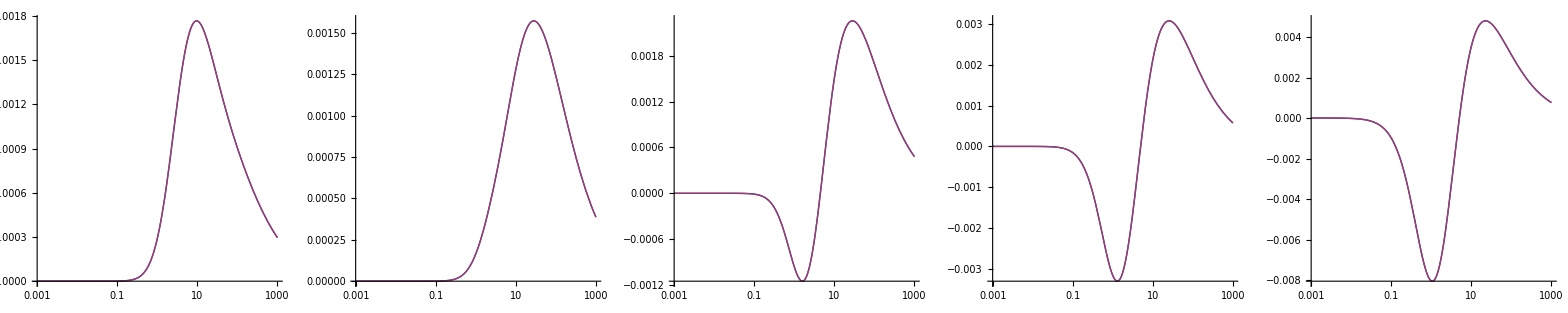

```mathematica
Module[{m2V,nlfV,β0,path,k,n,dq1,ndq1},
m2V=4.75^2;
nlfV=4;
k=P;
n[e_,η_,ρq_]:=e/.normColor//.{sp->s-q2,s->sOfη@η,ρ->ρOfη@η,β->βOfρ@ρ,χ->χOfβ@β,χp->χOfβ@βp,βp->βOfρ@ρp,ρp->ρ ρq/(ρq-ρ),q2->q2Ofρq@ρq,βq->βqOfρq@ρq,χq->χqOfβq@βq,m2-> m2V};

path="~/Physik/PhD/MMa/data/LeptoProduction/";
dq1[2]=<<(path<>"LeptoProduction.dq1_F2_VV.m");
dq1[L]=<<(path<>"LeptoProduction.dq1_FL_VV.m");
dq1[P]=<<(path<>"LeptoProduction.dq1_x2g1_VV.m");
dq1[T]=dq1[2]-dq1[L];
ndq1[η_,ρq_]:=n[dq1[k]/.{ln@z_:>Log@z,Li2@z_:>PolyLog[2,z]},η,ρq];
Print[ndq1[1*^3,-4m2V/1*^3]];

Module[{plots,q2V,ρqV,fp,l,i,lP,cPfit,cP},
plots={};
Do[
q2V=First@e;
ρqV=4m2V/q2V;
fp="~/Physik/PhD/data/partonic/"<>Last@e;
l=Import@fp;
i[T]=2;i[L]=3;i[P]=4;
lP=({#[[1]],#[[i@k]]})&/@l;
cPfit=Interpolation[lP];
cP[η_]:=Piecewise[{{cPfit@η,1*^-3≤η≤1*^3}}];
AppendTo[plots,LogLinearPlot[{cP@η,ndq1[η,ρqV]},{η,1*^-3,1*^3}]];
,{e,{{-1*^3,"dq1-q2_3.dat"},{-1*^2,"dq1-q2_2.dat"},{-1*^1,"dq1-q2_1.dat"},{-1*^0,"dq1-q2_0.dat"},{-1*^-2,"dq1-q2_-2.dat"}}}
];
Print@GraphicsRow[plots,ImageSize-> 1600];
];
]
```

```mathematica
Module[{h4V,e,f,n},
h4V=Li2[(1+χp)/(1+χ)]- Li2[χ(1+χp)/(1+χ)]- Li2[χp(1+χ)/(1+χp)]+ Li2[χp(1+χ)/(1+χp)/χ]+1/2 ln[χ]^2+ln[χ](ln[1+χ]+ln[1+χp]-ln[χ-χp]-ln[1-χ χp]);
f=<<"~/Physik/PhD/MMa/data/LeptoProduction/LeptoProduction.dq1_F2_VV.m";
n=2^7 8/(12*9 3π (1+β)^8(1+βp)^7 χ (1+χ)^6(1+χp)^7);
e=f/n;
e=e/.{Li2[(1+χp)/(1+χ)]-> h4-Simplify[h4V-Li2[(1+χp)/(1+χ)]]};
e=e/.{ln[χ-χp]->ln[(χ-χp)/(1-χ χp)]+ ln[1-χ χp]};
e=e/.{Li2@z_:>Li2@Simplify@z};
e=Collect[e,{h4,ln@_,Li2@_,π},FullSimplify[#/.{χ->χOfβ@βOfρ@ρ,χp->χOfβ@βOfρ@ρp}]&];
e=e//.{Sqrt[1-ρ]->β,Sqrt[1-ρp]->βp,1/Sqrt[1-ρp]->1/βp};
e=Collect[e,{h4,ln@_,Li2@_,π,β,βq},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βq<1}]&];
e=Collect[e/.{β^2->βOfρ[ρ]^2},{h4,ln@_,Li2@_,π,β,βp},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βp<1}]&];
Print@e;

Print@FullSimplify[n/.{β->βOfχ@χ,βp->βOfχ@χp}/.{χ->χOfβ@βOfρ@ρ,χ->χOfβ@βOfρ@ρp},Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βq<1,m2>0,s>4m2,q2<0}];
Table[{χ,χq,f,e*n,f-(e*n)}/.{h4->h4V}//.{ρ->ρOfβ@β,β->βOfχ@χ,χp->χOfβ@βp,βp->βOfρ@ρp,ρp->ρ ρq/(ρq-ρ),ρq->ρqOfβq@βq,βq->βqOfχq@χq}/.{ln@z_:>Log@z,Li2@z_:>PolyLog[2,z]},{χ,.1,.9,.1},{χq,.1,.9,.1}]
]
```

β (ρ^2 (718+5 ρ)-2 ρ (758+91 ρ) ρp+2 (622+1277 ρ) ρp^2-3228 ρp^3)+18 h4 (-8 ρ^2+8 ρ ρp+(-4+3 ρ^2) ρp^2-27 ρ ρp^3+27 ρp^4)+9/2 ρ (3 ρ^3+6 ρ^2 ρp+4 ρp (4-27 ρp^2)+6 ρ (-4+9 ρp^2)) ln[χ]-12 βp (8 ρ (7-13 ρp) ρp+ρ^2 (-38+23 ρp)+2 ρp^2 (-17+47 ρp)) ln[(χ-χp)/(1-χ χp)]

1/(2592 π ρ)

{{{0.1,0.1,0.00169762,0.00169762,2.81546×10^-15},{0.1,0.2,0.00250712,0.00250712,3.24046×10^-15},{0.1,0.3,0.00328526,0.00328526,3.42261×10^-15},{0.1,0.4,0.00406758,0.00406758,2.33667×10^-15},{0.1,0.5,0.00489132,0.00489132,9.59042×10^-15},{0.1,0.6,0.00580469,0.00580469,8.92255×10^-15},{0.1,0.7,0.00688661,0.00688661,5.36376×10^-15},{0.1,0.8,0.0083036,0.0083036,7.83141×10^-15},{0.1,0.9,0.0105743,0.0105743,4.24053×10^-15}},{{0.2,0.1,0.000377259,0.000377259,-1.75727×10^-15},{0.2,0.2,0.000631064,0.000631064,1.33574×10^-16},{0.2,0.3,0.000960801,0.000960801,1.80411×10^-15},{0.2,0.4,0.00137598,0.00137598,-1.51094×10^-15},{0.2,0.5,0.00189207,0.00189207,-1.90473×10^-15},{0.2,0.6,0.00253717,0.00253717,5.48173×10^-16},{0.2,0.7,0.00336779,0.00336779,1.07206×10^-15},{0.2,0.8,0.00451647,0.00451647,-1.66187×10^-15},{0.2,0.9,0.00641584,0.00641584,1.16573×10^-15}},{{0.3,0.1,0.0000788648,0.0000788648,1.52656×10^-15},{0.3,0.2,0.000138525,0.000138525,2.498×10^-15},{0.3,0.3,0.000231917,0.000231917,3.88578×10^-16},{0.3,0.4,0.000373741,0.000373741,-2.09902×10^-16},{0.3,0.5,0.000583924,0.000583924,1.48319×10^-15},{0.3,0.6,0.000891243,0.000891243,1.02349×10^-16},{0.3,0.7,0.00134332,0.00134332,1.10675×10^-15},{0.3,0.8,0.00203906,0.00203906,1.09288×10^-15},{0.3,0.9,0.00328349,0.00328349,-9.71445×10^-17}},{{0.4,0.1,0.000015194,0.000015194,-1.51268×10^-15},{0.4,0.2,0.0000272675,0.0000272675,-1.20737×10^-15},{0.4,0.3,0.0000485246,0.0000485246,-3.50414×10^-16},{0.4,0.4,0.0000857683,0.0000857683,3.10516×10^-16},{0.4,0.5,0.000150438,0.000150438,2.5327×10^-16},{0.4,0.6,0.000261723,0.000261723,3.05311×10^-16},{0.4,0.7,0.000453194,0.000453194,-1.56125×10^-16},{0.4,0.8,0.000792406,0.000792406,-1.14492×10^-16},{0.4,0.9,0.00147365,0.00147365,2.35922×10^-16}},{{0.5,0.1,2.53167×10^-6,2.53167×10^-6,2.00881×10^-15},{0.5,0.2,4.59055×10^-6,4.59055×10^-6,-5.75928×10^-16},{0.5,0.3,8.50261×10^-6,8.50261×10^-6,3.46945×10^-16},{0.5,0.4,0.0000161325,0.0000161325,2.15106×10^-16},{0.5,0.5,0.0000313262,0.0000313262,3.64292×10^-16},{0.5,0.6,0.0000620471,0.0000620471,-3.67761×10^-16},{0.5,0.7,0.00012503,0.00012503,-1.17961×10^-16},{0.5,0.8,0.000257959,0.000257959,4.23273×10^-16},{0.5,0.9,0.000570664,0.000570664,-1.11022×10^-16}},{{0.6,0.1,3.30737×10^-7,3.30737×10^-7,8.47412×10^-16},{0.6,0.2,6.02881×10^-7,6.02881×10^-7,6.40113×10^-16},{0.6,0.3,1.14627×10^-6,1.14627×10^-6,-3.79904×10^-16},{0.6,0.4,2.29206×10^-6,2.29206×10^-6,1.02349×10^-16},{0.6,0.5,4.84662×10^-6,4.84662×10^-6,6.07153×10^-17},{0.6,0.6,0.0000108635,0.0000108635,4.42354×10^-16},{0.6,0.7,0.0000257956,0.0000257956,-1.5786×10^-16},{0.6,0.8,0.0000649772,0.0000649772,1.80411×10^-16},{0.6,0.9,0.000179839,0.000179839,2.91434×10^-16}},{{0.7,0.1,2.84885×10^-8,2.84885×10^-8,1.32706×10^-16},{0.7,0.2,5.20749×10^-8,5.20749×10^-8,5.55112×10^-16},{0.7,0.3,1.00676×10^-7,1.00676×10^-7,2.93168×10^-16},{0.7,0.4,2.08815×10^-7,2.08815×10^-7,7.63278×10^-17},{0.7,0.5,4.71701×10^-7,4.71701×10^-7,7.11237×10^-17},{0.7,0.6,1.17939×10^-6,1.17939×10^-6,-4.16334×10^-17},{0.7,0.7,3.31774×10^-6,3.31774×10^-6,1.21431×10^-17},{0.7,0.8,0.0000106574,0.0000106574,-1.50921×10^-16},{0.7,0.9,0.00004033,0.00004033,-1.02349×10^-16}},{{0.8,0.1,1.10852×10^-9,1.10852×10^-9,4.34548×10^-16},{0.8,0.2,2.02924×10^-9,2.02924×10^-9,1.37911×10^-16},{0.8,0.3,3.96227×10^-9,3.96227×10^-9,5.89806×10^-17},{0.8,0.4,8.41114×10^-9,8.41114×10^-9,9.36751×10^-17},{0.8,0.5,1.98822×10^-8,1.98822×10^-8,7.45931×10^-17},{0.8,0.6,5.40863×10^-8,5.40863×10^-8,6.93889×10^-17},{0.8,0.7,1.7768×10^-7,1.7768×10^-7,1.76074×10^-16},{0.8,0.8,7.55739×10^-7,7.55739×10^-7,3.90313×10^-17},{0.8,0.9,4.57051×10^-6,4.57051×10^-6,2.77556×10^-17}},{{0.9,0.1,5.907×10^-12,5.90718×10^-12,-1.87784×10^-16},{0.9,0.2,1.08209×10^-11,1.0821×10^-11,-1.3314×10^-16},{0.9,0.3,2.12357×10^-11,2.12358×10^-11,-1.14492×10^-16},{0.9,0.4,4.56341×10^-11,4.56341×10^-11,-4.81386×10^-17},{0.9,0.5,1.10622×10^-10,1.10623×10^-10,-2.0383×10^-17},{0.9,0.6,3.16687×10^-10,3.16687×10^-10,-5.0307×10^-17},{0.9,0.7,1.16021×10^-9,1.16021×10^-9,-4.29344×10^-17},{0.9,0.8,6.39058×10^-9,6.39058×10^-9,-4.42354×10^-17},{0.9,0.9,7.64921×10^-8,7.64921×10^-8,-3.38271×10^-17}}}

```mathematica
Module[{h4V,e,f,n},
h4V=Li2[(1+χp)/(1+χ)]- Li2[χ(1+χp)/(1+χ)]- Li2[χp(1+χ)/(1+χp)]+ Li2[χp(1+χ)/(1+χp)/χ]+1/2 ln[χ]^2+ln[χ](ln[1+χ]+ln[1+χp]-ln[χ-χp]-ln[1-χ χp]);
f=<<"~/Physik/PhD/MMa/data/LeptoProduction/LeptoProduction.dq1_FL_VV.m";
n=2^7 8/(3 3 3π (1+β)^8(1+βp)^7 χ (1+χ)^6(1+χp)^7)*ρp;
e=f/n;
e=e/.{Li2[(1+χp)/(1+χ)]-> h4-Simplify[h4V-Li2[(1+χp)/(1+χ)]]};
e=e/.{ln[χ-χp]->ln[(χ-χp)/(1-χ χp)]+ ln[1-χ χp]};
e=e/.{Li2@z_:>Li2@Simplify@z};
e=Collect[e,{h4,ln@_,Li2@_,π},FullSimplify[#/.{χ->χOfβ@βOfρ@ρ,χp->χOfβ@βOfρ@ρp}]&];
e=e//.{Sqrt[1-ρ]->β,Sqrt[1-ρp]->βp,1/Sqrt[1-ρp]->1/βp};
e=Collect[e,{h4,ln@_,Li2@_,π,β,βq},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βq<1}]&];
e=Collect[e//.{β^2->βOfρ[ρ]^2,βp^2->βOfρ[ρp]^2,βp^3->βp βOfρ[ρp]^2,βp^4->βOfρ[ρp]^4,βp^5->βp βOfρ[ρp]^4},{h4,ln@_,Li2@_,π,β,βp},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βp<1}]&];
e=Collect[e,{h4,ln@_,Li2@_,π,β,βq},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βq<1}]&];
e=Collect[e//.{β^2->βOfρ[ρ]^2,βp^2->βOfρ[ρp]^2,βp^3->βp βOfρ[ρp]^2,βp^4->βOfρ[ρp]^4,βp^5->βp βOfρ[ρp]^4},{h4,ln@_,Li2@_,π,β,βp},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βp<1}]&];
Print@e;

Print@FullSimplify[n/.{β->βOfχ@χ,βp->βOfχ@χp}/.{χ->χOfβ@βOfρ@ρ,χ->χOfβ@βOfρ@ρp},Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βq<1,m2>0,s>4m2,q2<0}];
Table[{χ,χq,f,e*n,f-(e*n)}/.{h4->h4V}//.{ρ->ρOfβ@β,β->βOfχ@χ,χp->χOfβ@βp,βp->βOfρ@ρp,ρp->ρ ρq/(ρq-ρ),ρq->ρqOfβq@βq,βq->βqOfχq@χq}/.{ln@z_:>Log@z,Li2@z_:>PolyLog[2,z]},{χ,.1,.9,.1},{χq,.1,.9,.1}]
]
```

27 h4 ρp^2 (-ρ+ρp)+β (23 ρ^2+2 (25-93 ρp) ρp+19 ρ (-2+7 ρp))+9/2 ρ (ρ^2+3 ρ ρp-6 ρp^2) ln[χ]+6 βp (ρ-ρp) (-2+11 ρp) ln[(χ-χp)/(1-χ χp)]

ρp/(216 π ρ)

{{{0.1,0.1,0.00070676,0.00070676,-1.0842×10^-18},{0.1,0.2,0.00112187,0.00112187,-1.51788×10^-18},{0.1,0.3,0.00139272,0.00139272,-5.42101×10^-18},{0.1,0.4,0.00157857,0.00157857,-6.93889×10^-18},{0.1,0.5,0.00170882,0.00170882,-2.38524×10^-18},{0.1,0.6,0.00180009,0.00180009,-4.33681×10^-18},{0.1,0.7,0.00186259,0.00186259,-1.51788×10^-18},{0.1,0.8,0.00190298,0.00190298,-6.07153×10^-18},{0.1,0.9,0.00192572,0.00192572,-5.42101×10^-18}},{{0.2,0.1,0.000156751,0.000156751,-8.67362×10^-19},{0.2,0.2,0.00031365,0.00031365,-8.23994×10^-18},{0.2,0.3,0.000466189,0.000466189,-2.60209×10^-18},{0.2,0.4,0.000610292,0.000610292,-6.93889×10^-18},{0.2,0.5,0.000742367,0.000742367,-4.55365×10^-18},{0.2,0.6,0.000859269,0.000859269,6.28837×10^-18},{0.2,0.7,0.000958168,0.000958168,-1.21431×10^-17},{0.2,0.8,0.00103627,0.00103627,1.30104×10^-18},{0.2,0.9,0.00109016,0.00109016,-9.1073×10^-18}},{{0.3,0.1,0.0000318921,0.0000318921,0.},{0.3,0.2,0.0000709278,0.0000709278,-7.80626×10^-18},{0.3,0.3,0.000117259,0.000117259,-1.73472×10^-18},{0.3,0.4,0.000170378,0.000170378,-2.73219×10^-17},{0.3,0.5,0.000228938,0.000228938,-6.93889×10^-18},{0.3,0.6,0.000290613,0.000290613,8.67362×10^-18},{0.3,0.7,0.000352003,0.000352003,-1.9082×10^-17},{0.3,0.8,0.000408468,0.000408468,-2.77556×10^-17},{0.3,0.9,0.000453546,0.000453546,-1.64799×10^-17}},{{0.4,0.1,6.00473×10^-6,6.00473×10^-6,3.03577×10^-18},{0.4,0.2,0.000014122,0.000014122,-1.73472×10^-18},{0.4,0.3,0.0000249445,0.0000249445,0.},{0.4,0.4,0.0000390956,0.0000390956,8.67362×10^-18},{0.4,0.5,0.0000570978,0.0000570978,-3.46945×10^-18},{0.4,0.6,0.0000791368,0.0000791368,8.67362×10^-18},{0.4,0.7,0.000104699,0.000104699,-6.07153×10^-18},{0.4,0.8,0.000132049,0.000132049,1.73472×10^-18},{0.4,0.9,0.000157356,0.000157356,1.73472×10^-18}},{{0.5,0.1,9.83923×10^-7,9.83923×10^-7,0.},{0.5,0.2,2.38948×10^-6,2.38948×10^-6,5.20417×10^-18},{0.5,0.3,4.40349×10^-6,4.40349×10^-6,8.67362×10^-19},{0.5,0.4,7.29023×10^-6,7.29023×10^-6,-7.80626×10^-18},{0.5,0.5,0.0000114032,0.0000114032,-2.1684×10^-18},{0.5,0.6,0.0000171627,0.0000171627,0.},{0.5,0.7,0.0000249402,0.0000249402,-1.73472×10^-18},{0.5,0.8,0.0000347424,0.0000347424,-3.46945×10^-18},{0.5,0.9,0.0000454754,0.0000454754,-6.93889×10^-18}},{{0.6,0.1,1.27069×10^-7,1.27069×10^-7,0.},{0.6,0.2,3.14565×10^-7,3.14565×10^-7,-1.73472×10^-18},{0.6,0.3,5.95739×10^-7,5.95739×10^-7,5.63785×10^-18},{0.6,0.4,1.02522×10^-6,1.02522×10^-6,-8.67362×10^-19},{0.6,0.5,1.69326×10^-6,1.69326×10^-6,8.67362×10^-19},{0.6,0.6,2.74587×10^-6,2.74587×10^-6,-2.60209×10^-18},{0.6,0.7,4.40116×10^-6,4.40116×10^-6,9.54098×10^-18},{0.6,0.8,6.91174×10^-6,6.91174×10^-6,-8.67362×10^-19},{0.6,0.9,0.0000102989,0.0000102989,0.}},{{0.7,0.1,1.08634×10^-8,1.08634×10^-8,6.50521×10^-19},{0.7,0.2,2.72033×10^-8,2.72033×10^-8,-8.67362×10^-19},{0.7,0.3,5.24115×10^-8,5.24115×10^-8,-4.33681×10^-19},{0.7,0.4,9.25823×10^-8,9.25823×10^-8,-3.90313×10^-18},{0.7,0.5,1.592×10^-7,1.592×10^-7,-2.60209×10^-18},{0.7,0.6,2.749×10^-7,2.749×10^-7,-2.60209×10^-18},{0.7,0.7,4.85456×10^-7,4.85456×10^-7,-3.46945×10^-18},{0.7,0.8,8.79463×10^-7,8.79463×10^-7,0.},{0.7,0.9,1.5804×10^-6,1.5804×10^-6,-9.54098×10^-18}},{{0.8,0.1,4.20795×10^-10,4.20795×10^-10,-2.1684×10^-19},{0.8,0.2,1.06068×10^-9,1.06068×10^-9,2.1684×10^-19},{0.8,0.3,2.06439×10^-9,2.06439×10^-9,-3.68629×10^-18},{0.8,0.4,3.70606×10^-9,3.70606×10^-9,-2.1684×10^-18},{0.8,0.5,6.54585×10^-9,6.54585×10^-9,6.50521×10^-19},{0.8,0.6,1.18415×10^-8,1.18415×10^-8,-1.30104×10^-18},{0.8,0.7,2.27578×10^-8,2.27578×10^-8,-8.67362×10^-19},{0.8,0.8,4.82791×10^-8,4.82791×10^-8,-3.90313×10^-18},{0.8,0.9,1.14696×10^-7,1.14696×10^-7,2.60209×10^-18}},{{0.9,0.1,2.2372×10^-12,2.2372×10^-12,-2.1684×10^-19},{0.9,0.2,5.65763×10^-12,5.65763×10^-12,-4.33681×10^-19},{0.9,0.3,1.1068×10^-11,1.1068×10^-11,5.42101×10^-19},{0.9,0.4,2.00371×10^-11,2.00371×10^-11,-6.50521×10^-19},{0.9,0.5,3.59104×10^-11,3.59104×10^-11,-4.11997×10^-18},{0.9,0.6,6.67636×10^-11,6.67636×10^-11,-3.68629×10^-18},{0.9,0.7,1.35849×10^-10,1.35849×10^-10,-3.03577×10^-18},{0.9,0.8,3.30616×10^-10,3.30616×10^-10,-3.90313×10^-18},{0.9,0.9,1.15422×10^-9,1.15422×10^-9,-2.81893×10^-18}}}

```mathematica
Module[{h4V,e,f,n},
h4V=Li2[(1+χp)/(1+χ)]- Li2[χ(1+χp)/(1+χ)]- Li2[χp(1+χ)/(1+χp)]+ Li2[χp(1+χ)/(1+χp)/χ]+1/2 ln[χ]^2+ln[χ](ln[1+χ]+ln[1+χp]-ln[χ-χp]-ln[1-χ χp]);
f=<<"~/Physik/PhD/MMa/data/LeptoProduction/LeptoProduction.dq1_x2g1_VV.m";
n=2^7 8/(12*9 3π (1+β)^8(1+βp)^7 χ (1+χ)^6(1+χp)^7);
e=f/n;
e=e/.{Li2[(1+χp)/(1+χ)]-> h4-Simplify[h4V-Li2[(1+χp)/(1+χ)]]};
e=e/.{ln[χ-χp]->ln[(χ-χp)/(1-χ χp)]+ ln[1-χ χp]};
e=e/.{Li2@z_:>Li2@Simplify@z};
e=Collect[e,{h4,ln@_,Li2@_,π},FullSimplify[#/.{χ->χOfβ@βOfρ@ρ,χp->χOfβ@βOfρ@ρp}]&];
e=e//.{Sqrt[1-ρ]->β,Sqrt[1-ρp]->βp,1/Sqrt[1-ρp]->1/βp};
e=Collect[e,{h4,ln@_,Li2@_,π,β,βq},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βq<1}]&];
e=Collect[e/.{β^2->βOfρ[ρ]^2},{h4,ln@_,Li2@_,π,β,βp},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βp<1}]&];
Print@e;

Print@FullSimplify[n/.{β->βOfχ@χ,βp->βOfχ@χp}/.{χ->χOfβ@βOfρ@ρ,χ->χOfβ@βOfρ@ρp},Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βq<1,m2>0,s>4m2,q2<0}];
Table[{χ,χq,f,e*n,f-(e*n)}/.{h4->h4V}//.{ρ->ρOfβ@β,β->βOfχ@χ,χp->χOfβ@βp,βp->βOfρ@ρp,ρp->ρ ρq/(ρq-ρ),ρq->ρqOfβq@βq,βq->βqOfχq@χq}/.{ln@z_:>Log@z,Li2@z_:>PolyLog[2,z]},{χ,.1,.9,.1},{χq,.1,.9,.1}]
]
```

β (5 ρ^3+ρ^2 (718-458 ρp)+8 (109-75 ρp) ρp^2+20 ρ ρp (-53+41 ρp))+18 h4 (-4 ρp^2+ρ ρp (8-3 ρp^2)+ρ^2 (-8+3 ρp^2))+9/2 ρ (16 ρp+3 ρ (-8+ρ^2-2 ρ ρp+4 ρp^2)) ln[χ]-12 βp (2 ρ (22-19 ρp) ρp+ρ^2 (-38+23 ρp)+ρp^2 (-28+25 ρp)) ln[(χ-χp)/(1-χ χp)]

1/(2592 π ρ)

{{{0.1,0.1,0.000614678,0.000614678,7.80626×10^-18},{0.1,0.2,0.000267888,0.000267888,6.93889×10^-18},{0.1,0.3,-0.000124958,-0.000124958,-1.56125×10^-17},{0.1,0.4,-0.000544539,-0.000544539,-6.93889×10^-18},{0.1,0.5,-0.000992774,-0.000992774,-1.38778×10^-17},{0.1,0.6,-0.0014844,-0.0014844,-3.46945×10^-18},{0.1,0.7,-0.00205197,-0.00205197,3.81639×10^-17},{0.1,0.8,-0.002771,-0.002771,3.1225×10^-17},{0.1,0.9,-0.0038847,-0.0038847,6.245×10^-17}},{{0.2,0.1,0.000161031,0.000161031,3.46945×10^-18},{0.2,0.2,0.0000655609,0.0000655609,5.20417×10^-18},{0.2,0.3,-0.000103289,-0.000103289,-1.56125×10^-17},{0.2,0.4,-0.000355815,-0.000355815,-1.38778×10^-17},{0.2,0.5,-0.000706434,-0.000706434,3.46945×10^-18},{0.2,0.6,-0.00117937,-0.00117937,-5.55112×10^-17},{0.2,0.7,-0.00182183,-0.00182183,0.},{0.2,0.8,-0.00274381,-0.00274381,-3.46945×10^-18},{0.2,0.9,-0.0043047,-0.0043047,1.73472×10^-17}},{{0.3,0.1,0.0000367891,0.0000367891,0.},{0.3,0.2,0.000016201,0.000016201,-3.46945×10^-18},{0.3,0.3,-0.0000302537,-0.0000302537,5.20417×10^-18},{0.3,0.4,-0.000117226,-0.000117226,-3.46945×10^-18},{0.3,0.5,-0.000265029,-0.000265029,-3.46945×10^-18},{0.3,0.6,-0.000503091,-0.000503091,6.93889×10^-18},{0.3,0.7,-0.00087935,-0.00087935,6.93889×10^-18},{0.3,0.8,-0.00149086,-0.00149086,-3.1225×10^-17},{0.3,0.9,-0.00263004,-0.00263004,0.}},{{0.4,0.1,7.45834×10^-6,7.45834×10^-6,0.},{0.4,0.2,3.50196×10^-6,3.50196×10^-6,-3.46945×10^-18},{0.4,0.3,-6.89187×10^-6,-6.89187×10^-6,0.},{0.4,0.4,-0.0000298449,-0.0000298449,6.93889×10^-18},{0.4,0.5,-0.0000761505,-0.0000761505,1.73472×10^-17},{0.4,0.6,-0.00016455,-0.00016455,6.93889×10^-18},{0.4,0.7,-0.000328558,-0.000328558,2.08167×10^-17},{0.4,0.8,-0.00063612,-0.00063612,0.},{0.4,0.9,-0.00128124,-0.00128124,6.93889×10^-18}},{{0.5,0.1,1.28173×10^-6,1.28173×10^-6,-1.73472×10^-18},{0.5,0.2,6.28308×10^-7,6.28308×10^-7,5.20417×10^-18},{0.5,0.3,-1.26747×10^-6,-1.26747×10^-6,8.67362×10^-18},{0.5,0.4,-6.00186×10^-6,-6.00186×10^-6,6.93889×10^-18},{0.5,0.5,-0.0000170565,-0.0000170565,1.38778×10^-17},{0.5,0.6,-0.0000419474,-0.0000419474,1.73472×10^-17},{0.5,0.7,-0.0000969651,-0.0000969651,0.},{0.5,0.8,-0.000219581,-0.000219581,6.93889×10^-18},{0.5,0.9,-0.00052,-0.00052,0.}},{{0.6,0.1,1.70684×10^-7,1.70684×10^-7,-8.67362×10^-18},{0.6,0.2,8.60293×10^-8,8.60293×10^-8,-1.21431×10^-17},{0.6,0.3,-1.761×10^-7,-1.761×10^-7,1.73472×10^-18},{0.6,0.4,-8.92025×10^-7,-8.92025×10^-7,-6.93889×10^-18},{0.6,0.5,-2.77733×10^-6,-2.77733×10^-6,-1.73472×10^-18},{0.6,0.6,-7.73781×10^-6,-7.73781×10^-6,1.73472×10^-18},{0.6,0.7,-0.0000210027,-0.0000210027,-1.73472×10^-18},{0.6,0.8,-0.0000576334,-0.0000576334,-3.46945×10^-18},{0.6,0.9,-0.000168952,-0.000168952,-6.93889×10^-18}},{{0.7,0.1,1.4876×10^-8,1.4876×10^-8,-7.80626×10^-18},{0.7,0.2,7.62944×10^-9,7.62944×10^-9,4.33681×10^-18},{0.7,0.3,-1.5762×10^-8,-1.5762×10^-8,-1.73472×10^-18},{0.7,0.4,-8.37222×10^-8,-8.37222×10^-8,6.07153×10^-18},{0.7,0.5,-2.79961×10^-7,-2.79961×10^-7,6.93889×10^-18},{0.7,0.6,-8.71849×10^-7,-8.71849×10^-7,1.73472×10^-18},{0.7,0.7,-2.79928×10^-6,-2.79928×10^-6,0.},{0.7,0.8,-9.74338×10^-6,-9.74338×10^-6,3.46945×10^-18},{0.7,0.9,-0.0000387063,-0.0000387063,8.67362×10^-18}},{{0.8,0.1,5.82811×10^-10,5.82811×10^-10,-1.73472×10^-18},{0.8,0.2,3.01971×10^-10,3.01971×10^-10,-8.67362×10^-19},{0.8,0.3,-6.27343×10^-10,-6.27343×10^-10,-8.67362×10^-19},{0.8,0.4,-3.43449×10^-9,-3.43449×10^-9,-3.46945×10^-18},{0.8,0.5,-1.20656×10^-8,-1.20656×10^-8,-1.73472×10^-18},{0.8,0.6,-4.09733×10^-8,-4.09733×10^-8,-8.67362×10^-19},{0.8,0.7,-1.53647×10^-7,-1.53647×10^-7,-3.46945×10^-18},{0.8,0.8,-7.06169×10^-7,-7.06169×10^-7,0.},{0.8,0.9,-4.45437×10^-6,-4.45437×10^-6,-8.67362×10^-19}},{{0.9,0.1,3.11639×10^-12,3.11639×10^-12,1.73472×10^-18},{0.9,0.2,1.623×10^-12,1.623×10^-12,8.67362×10^-19},{0.9,0.3,-3.38148×10^-12,-3.38148×10^-12,3.46945×10^-18},{0.9,0.4,-1.88106×10^-11,-1.88106×10^-11,-4.33681×10^-19},{0.9,0.5,-6.79256×10^-11,-6.79256×10^-11,-1.30104×10^-18},{0.9,0.6,-2.43136×10^-10,-2.43136×10^-10,-4.33681×10^-19},{0.9,0.7,-1.01757×10^-9,-1.01757×10^-9,-1.30104×10^-18},{0.9,0.8,-6.05317×10^-9,-6.05317×10^-9,2.60209×10^-18},{0.9,0.9,-7.5331×10^-8,-7.5331×10^-8,-8.67362×10^-19}}}

```mathematica
Module[{h4V,e,f,n},
h4V=Li2[(1+χp)/(1+χ)]- Li2[χ(1+χp)/(1+χ)]- Li2[χp(1+χ)/(1+χp)]+ Li2[χp(1+χ)/(1+χp)/χ]+1/2 ln[χ]^2+ln[χ](ln[1+χ]+ln[1+χp]-ln[χ-χp]-ln[1-χ χp]);
f=<<"~/Physik/PhD/MMa/data/LeptoProduction/LeptoProduction.dq1_xF3_VA.m";
n=2^7 8/(3 3 3π (1+β)^8(1+βp)^7 χ (1+χ)^6(1+χp)^7)/8/3*2;
e=f/n;
e=e/.{Li2[(1+χp)/(1+χ)]-> h4-Simplify[h4V-Li2[(1+χp)/(1+χ)]]};
e=e/.{ln[χ-χp]->ln[(χ-χp)/(1-χ χp)]+ ln[1-χ χp]};
e=e/.{Li2@z_:>Li2@Simplify@z};
e=Collect[e,{h4,ln@_,Li2@_,π},FullSimplify[#/.{χ->χOfβ@βOfρ@ρ,χp->χOfβ@βOfρ@ρp}]&];
e=e//.{Sqrt[1-ρ]->β,Sqrt[1-ρp]->βp,1/Sqrt[1-ρp]->1/βp};
e=Collect[e,{h4,ln@_,Li2@_,π,β,βq},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βq<1}]&];
e=Collect[e//.{β^2->βOfρ[ρ]^2,βp^2->βOfρ[ρp]^2,βp^3->βp βOfρ[ρp]^2,βp^4->βOfρ[ρp]^4,βp^5->βp βOfρ[ρp]^4},{h4,ln@_,Li2@_,π,β,βp},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βp<1}]&];
e=Collect[e,{h4,ln@_,Li2@_,π,β,βq},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βq<1}]&];
e=Collect[e//.{β^2->βOfρ[ρ]^2,βp^2->βOfρ[ρp]^2,βp^3->βp βOfρ[ρp]^2,βp^4->βOfρ[ρp]^4,βp^5->βp βOfρ[ρp]^4},{h4,ln@_,Li2@_,π,β,βp},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βp<1}]&];
Print@e;

Print@FullSimplify[n/.{β->βOfχ@χ,βp->βOfχ@χp}/.{χ->χOfβ@βOfρ@ρ,χ->χOfβ@βOfρ@ρp},Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βq<1,m2>0,s>4m2,q2<0}];
Table[{χ,χq,f,e*n,f-(e*n)}/.{h4->h4V}//.{ρ->ρOfβ@β,β->βOfχ@χ,χp->χOfβ@βp,βp->βOfρ@ρp,ρp->ρ ρq/(ρq-ρ),ρq->ρqOfβq@βq,βq->βqOfχq@χq}/.{ln@z_:>Log@z,Li2@z_:>PolyLog[2,z]},{χ,.1,.9,.1},{χq,.1,.9,.1}]
]
```

β (5 ρ^3+ρ^2 (718-458 ρp)+8 (109-75 ρp) ρp^2+20 ρ ρp (-53+41 ρp))+18 h4 (-4 ρp^2+ρ ρp (8-3 ρp^2)+ρ^2 (-8+3 ρp^2))+9/2 ρ (16 ρp+3 ρ (-8+ρ^2-2 ρ ρp+4 ρp^2)) ln[χ]-12 βp (2 ρ (22-19 ρp) ρp+ρ^2 (-38+23 ρp)+ρp^2 (-28+25 ρp)) ln[(χ-χp)/(1-χ χp)]

1/(2592 π ρ)

{{{0.1,0.1,0.000614678,0.000614678,7.80626×10^-18},{0.1,0.2,0.000267888,0.000267888,6.93889×10^-18},{0.1,0.3,-0.000124958,-0.000124958,-1.56125×10^-17},{0.1,0.4,-0.000544539,-0.000544539,-6.93889×10^-18},{0.1,0.5,-0.000992774,-0.000992774,-1.38778×10^-17},{0.1,0.6,-0.0014844,-0.0014844,-3.46945×10^-18},{0.1,0.7,-0.00205197,-0.00205197,3.81639×10^-17},{0.1,0.8,-0.002771,-0.002771,3.1225×10^-17},{0.1,0.9,-0.0038847,-0.0038847,6.245×10^-17}},{{0.2,0.1,0.000161031,0.000161031,3.46945×10^-18},{0.2,0.2,0.0000655609,0.0000655609,5.20417×10^-18},{0.2,0.3,-0.000103289,-0.000103289,-1.56125×10^-17},{0.2,0.4,-0.000355815,-0.000355815,-1.38778×10^-17},{0.2,0.5,-0.000706434,-0.000706434,3.46945×10^-18},{0.2,0.6,-0.00117937,-0.00117937,-5.55112×10^-17},{0.2,0.7,-0.00182183,-0.00182183,0.},{0.2,0.8,-0.00274381,-0.00274381,-3.46945×10^-18},{0.2,0.9,-0.0043047,-0.0043047,1.73472×10^-17}},{{0.3,0.1,0.0000367891,0.0000367891,0.},{0.3,0.2,0.000016201,0.000016201,-3.46945×10^-18},{0.3,0.3,-0.0000302537,-0.0000302537,5.20417×10^-18},{0.3,0.4,-0.000117226,-0.000117226,-3.46945×10^-18},{0.3,0.5,-0.000265029,-0.000265029,-3.46945×10^-18},{0.3,0.6,-0.000503091,-0.000503091,6.93889×10^-18},{0.3,0.7,-0.00087935,-0.00087935,6.93889×10^-18},{0.3,0.8,-0.00149086,-0.00149086,-3.1225×10^-17},{0.3,0.9,-0.00263004,-0.00263004,0.}},{{0.4,0.1,7.45834×10^-6,7.45834×10^-6,0.},{0.4,0.2,3.50196×10^-6,3.50196×10^-6,-3.46945×10^-18},{0.4,0.3,-6.89187×10^-6,-6.89187×10^-6,0.},{0.4,0.4,-0.0000298449,-0.0000298449,6.93889×10^-18},{0.4,0.5,-0.0000761505,-0.0000761505,1.73472×10^-17},{0.4,0.6,-0.00016455,-0.00016455,6.93889×10^-18},{0.4,0.7,-0.000328558,-0.000328558,2.08167×10^-17},{0.4,0.8,-0.00063612,-0.00063612,0.},{0.4,0.9,-0.00128124,-0.00128124,6.93889×10^-18}},{{0.5,0.1,1.28173×10^-6,1.28173×10^-6,-1.73472×10^-18},{0.5,0.2,6.28308×10^-7,6.28308×10^-7,5.20417×10^-18},{0.5,0.3,-1.26747×10^-6,-1.26747×10^-6,8.67362×10^-18},{0.5,0.4,-6.00186×10^-6,-6.00186×10^-6,6.93889×10^-18},{0.5,0.5,-0.0000170565,-0.0000170565,1.38778×10^-17},{0.5,0.6,-0.0000419474,-0.0000419474,1.73472×10^-17},{0.5,0.7,-0.0000969651,-0.0000969651,0.},{0.5,0.8,-0.000219581,-0.000219581,6.93889×10^-18},{0.5,0.9,-0.00052,-0.00052,0.}},{{0.6,0.1,1.70684×10^-7,1.70684×10^-7,-8.67362×10^-18},{0.6,0.2,8.60293×10^-8,8.60293×10^-8,-1.21431×10^-17},{0.6,0.3,-1.761×10^-7,-1.761×10^-7,1.73472×10^-18},{0.6,0.4,-8.92025×10^-7,-8.92025×10^-7,-6.93889×10^-18},{0.6,0.5,-2.77733×10^-6,-2.77733×10^-6,-1.73472×10^-18},{0.6,0.6,-7.73781×10^-6,-7.73781×10^-6,1.73472×10^-18},{0.6,0.7,-0.0000210027,-0.0000210027,-1.73472×10^-18},{0.6,0.8,-0.0000576334,-0.0000576334,-3.46945×10^-18},{0.6,0.9,-0.000168952,-0.000168952,-6.93889×10^-18}},{{0.7,0.1,1.4876×10^-8,1.4876×10^-8,-7.80626×10^-18},{0.7,0.2,7.62944×10^-9,7.62944×10^-9,4.33681×10^-18},{0.7,0.3,-1.5762×10^-8,-1.5762×10^-8,-1.73472×10^-18},{0.7,0.4,-8.37222×10^-8,-8.37222×10^-8,6.07153×10^-18},{0.7,0.5,-2.79961×10^-7,-2.79961×10^-7,6.93889×10^-18},{0.7,0.6,-8.71849×10^-7,-8.71849×10^-7,1.73472×10^-18},{0.7,0.7,-2.79928×10^-6,-2.79928×10^-6,0.},{0.7,0.8,-9.74338×10^-6,-9.74338×10^-6,3.46945×10^-18},{0.7,0.9,-0.0000387063,-0.0000387063,8.67362×10^-18}},{{0.8,0.1,5.82811×10^-10,5.82811×10^-10,-1.73472×10^-18},{0.8,0.2,3.01971×10^-10,3.01971×10^-10,-8.67362×10^-19},{0.8,0.3,-6.27343×10^-10,-6.27343×10^-10,-8.67362×10^-19},{0.8,0.4,-3.43449×10^-9,-3.43449×10^-9,-3.46945×10^-18},{0.8,0.5,-1.20656×10^-8,-1.20656×10^-8,-1.73472×10^-18},{0.8,0.6,-4.09733×10^-8,-4.09733×10^-8,-8.67362×10^-19},{0.8,0.7,-1.53647×10^-7,-1.53647×10^-7,-3.46945×10^-18},{0.8,0.8,-7.06169×10^-7,-7.06169×10^-7,0.},{0.8,0.9,-4.45437×10^-6,-4.45437×10^-6,-8.67362×10^-19}},{{0.9,0.1,3.11639×10^-12,3.11639×10^-12,1.73472×10^-18},{0.9,0.2,1.623×10^-12,1.623×10^-12,8.67362×10^-19},{0.9,0.3,-3.38148×10^-12,-3.38148×10^-12,3.46945×10^-18},{0.9,0.4,-1.88106×10^-11,-1.88106×10^-11,-4.33681×10^-19},{0.9,0.5,-6.79256×10^-11,-6.79256×10^-11,-1.30104×10^-18},{0.9,0.6,-2.43136×10^-10,-2.43136×10^-10,-4.33681×10^-19},{0.9,0.7,-1.01757×10^-9,-1.01757×10^-9,-1.30104×10^-18},{0.9,0.8,-6.05317×10^-9,-6.05317×10^-9,2.60209×10^-18},{0.9,0.9,-7.5331×10^-8,-7.5331×10^-8,-8.67362×10^-19}}}

```mathematica
Module[{h4V,e,f,n},
h4V=Li2[(1+χp)/(1+χ)]- Li2[χ(1+χp)/(1+χ)]- Li2[χp(1+χ)/(1+χp)]+ Li2[χp(1+χ)/(1+χp)/χ]+1/2 ln[χ]^2+ln[χ](ln[1+χ]+ln[1+χp]-ln[χ-χp]-ln[1-χ χp]);
f=<<"~/Physik/PhD/MMa/data/LeptoProduction/LeptoProduction.dq1_g4_VA.m";
n=2^7 8/(12*9 3π (1+β)^8(1+βp)^7 χ (1+χ)^6(1+χp)^7);
e=f/n;
e=e/.{Li2[(1+χp)/(1+χ)]-> h4-Simplify[h4V-Li2[(1+χp)/(1+χ)]]};
e=e/.{ln[χ-χp]->ln[(χ-χp)/(1-χ χp)]+ ln[1-χ χp]};
e=e/.{Li2@z_:>Li2@Simplify@z};
e=Collect[e,{h4,ln@_,Li2@_,π},FullSimplify[#/.{χ->χOfβ@βOfρ@ρ,χp->χOfβ@βOfρ@ρp}]&];
e=e//.{Sqrt[1-ρ]->β,Sqrt[1-ρp]->βp,1/Sqrt[1-ρp]->1/βp};
e=Collect[e,{h4,ln@_,Li2@_,π,β,βq},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βq<1}]&];
e=Collect[e/.{β^2->βOfρ[ρ]^2},{h4,ln@_,Li2@_,π,β,βp},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βp<1}]&];
Print@e;

Print@FullSimplify[n/.{β->βOfχ@χ,βp->βOfχ@χp}/.{χ->χOfβ@βOfρ@ρ,χ->χOfβ@βOfρ@ρp},Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βq<1,m2>0,s>4m2,q2<0}];
Table[{χ,χq,f,e*n,f-(e*n)}/.{h4->h4V}//.{ρ->ρOfβ@β,β->βOfχ@χ,χp->χOfβ@βp,βp->βOfρ@ρp,ρp->ρ ρq/(ρq-ρ),ρq->ρqOfβq@βq,βq->βqOfχq@χq}/.{ln@z_:>Log@z,Li2@z_:>PolyLog[2,z]},{χ,.1,.9,.1},{χq,.1,.9,.1}]
]
```

β (-ρ^2 (718+5 ρ)+2 ρ (758+91 ρ) ρp-2 (622+1277 ρ) ρp^2+3228 ρp^3)-18 h4 (-8 ρ^2+8 ρ ρp+(-4+3 ρ^2) ρp^2-27 ρ ρp^3+27 ρp^4)-9/2 ρ (3 ρ^3+6 ρ^2 ρp+4 ρp (4-27 ρp^2)+6 ρ (-4+9 ρp^2)) ln[χ]+12 βp (8 ρ (7-13 ρp) ρp+ρ^2 (-38+23 ρp)+2 ρp^2 (-17+47 ρp)) ln[(χ-χp)/(1-χ χp)]

1/(2592 π ρ)

{{{0.1,0.1,-0.00169762,-0.00169762,-2.81372×10^-15},{0.1,0.2,-0.00250712,-0.00250712,-3.24046×10^-15},{0.1,0.3,-0.00328526,-0.00328526,-3.42261×10^-15},{0.1,0.4,-0.00406758,-0.00406758,-2.32973×10^-15},{0.1,0.5,-0.00489132,-0.00489132,-9.59822×10^-15},{0.1,0.6,-0.00580469,-0.00580469,-8.93036×10^-15},{0.1,0.7,-0.00688661,-0.00688661,-5.36376×10^-15},{0.1,0.8,-0.0083036,-0.0083036,-7.83748×10^-15},{0.1,0.9,-0.0105743,-0.0105743,-4.23273×10^-15}},{{0.2,0.1,-0.000377259,-0.000377259,1.75727×10^-15},{0.2,0.2,-0.000631064,-0.000631064,-1.26635×10^-16},{0.2,0.3,-0.000960801,-0.000960801,-1.81105×10^-15},{0.2,0.4,-0.00137598,-0.00137598,1.51094×10^-15},{0.2,0.5,-0.00189207,-0.00189207,1.89779×10^-15},{0.2,0.6,-0.00253717,-0.00253717,-5.44703×10^-16},{0.2,0.7,-0.00336779,-0.00336779,-1.07206×10^-15},{0.2,0.8,-0.00451647,-0.00451647,1.66187×10^-15},{0.2,0.9,-0.00641584,-0.00641584,-1.16573×10^-15}},{{0.3,0.1,-0.0000788648,-0.0000788648,-1.53003×10^-15},{0.3,0.2,-0.000138525,-0.000138525,-2.498×10^-15},{0.3,0.3,-0.000231917,-0.000231917,-3.92048×10^-16},{0.3,0.4,-0.000373741,-0.000373741,2.02963×10^-16},{0.3,0.5,-0.000583924,-0.000583924,-1.48319×10^-15},{0.3,0.6,-0.000891243,-0.000891243,-1.05818×10^-16},{0.3,0.7,-0.00134332,-0.00134332,-1.10675×10^-15},{0.3,0.8,-0.00203906,-0.00203906,-1.09288×10^-15},{0.3,0.9,-0.00328349,-0.00328349,9.36751×10^-17}},{{0.4,0.1,-0.000015194,-0.000015194,1.51268×10^-15},{0.4,0.2,-0.0000272675,-0.0000272675,1.20737×10^-15},{0.4,0.3,-0.0000485246,-0.0000485246,3.53884×10^-16},{0.4,0.4,-0.0000857683,-0.0000857683,-3.10516×10^-16},{0.4,0.5,-0.000150438,-0.000150438,-2.5327×10^-16},{0.4,0.6,-0.000261723,-0.000261723,-3.05311×10^-16},{0.4,0.7,-0.000453194,-0.000453194,1.56125×10^-16},{0.4,0.8,-0.000792406,-0.000792406,1.14492×10^-16},{0.4,0.9,-0.00147365,-0.00147365,-2.28983×10^-16}},{{0.5,0.1,-2.53167×10^-6,-2.53167×10^-6,-2.00881×10^-15},{0.5,0.2,-4.59055×10^-6,-4.59055×10^-6,5.75928×10^-16},{0.5,0.3,-8.50261×10^-6,-8.50261×10^-6,-3.46945×10^-16},{0.5,0.4,-0.0000161325,-0.0000161325,-2.15106×10^-16},{0.5,0.5,-0.0000313262,-0.0000313262,-3.66027×10^-16},{0.5,0.6,-0.0000620471,-0.0000620471,3.67761×10^-16},{0.5,0.7,-0.00012503,-0.00012503,1.14492×10^-16},{0.5,0.8,-0.000257959,-0.000257959,-4.26742×10^-16},{0.5,0.9,-0.000570664,-0.000570664,1.11022×10^-16}},{{0.6,0.1,-3.30737×10^-7,-3.30737×10^-7,-8.43943×10^-16},{0.6,0.2,-6.02881×10^-7,-6.02881×10^-7,-6.40113×10^-16},{0.6,0.3,-1.14627×10^-6,-1.14627×10^-6,3.79904×10^-16},{0.6,0.4,-2.29206×10^-6,-2.29206×10^-6,-1.02349×10^-16},{0.6,0.5,-4.84662×10^-6,-4.84662×10^-6,-6.07153×10^-17},{0.6,0.6,-0.0000108635,-0.0000108635,-4.42354×10^-16},{0.6,0.7,-0.0000257956,-0.0000257956,1.5786×10^-16},{0.6,0.8,-0.0000649772,-0.0000649772,-1.78677×10^-16},{0.6,0.9,-0.000179839,-0.000179839,-2.91434×10^-16}},{{0.7,0.1,-2.84885×10^-8,-2.84885×10^-8,-1.32706×10^-16},{0.7,0.2,-5.20749×10^-8,-5.20749×10^-8,-5.55112×10^-16},{0.7,0.3,-1.00676×10^-7,-1.00676×10^-7,-2.94903×10^-16},{0.7,0.4,-2.08815×10^-7,-2.08815×10^-7,-7.80626×10^-17},{0.7,0.5,-4.71701×10^-7,-4.71701×10^-7,-7.11237×10^-17},{0.7,0.6,-1.17939×10^-6,-1.17939×10^-6,4.16334×10^-17},{0.7,0.7,-3.31774×10^-6,-3.31774×10^-6,-1.21431×10^-17},{0.7,0.8,-0.0000106574,-0.0000106574,1.50921×10^-16},{0.7,0.9,-0.00004033,-0.00004033,1.02349×10^-16}},{{0.8,0.1,-1.10852×10^-9,-1.10852×10^-9,-4.34548×10^-16},{0.8,0.2,-2.02924×10^-9,-2.02924×10^-9,-1.39645×10^-16},{0.8,0.3,-3.96227×10^-9,-3.96227×10^-9,-5.72459×10^-17},{0.8,0.4,-8.41114×10^-9,-8.41114×10^-9,-9.36751×10^-17},{0.8,0.5,-1.98822×10^-8,-1.98822×10^-8,-7.45931×10^-17},{0.8,0.6,-5.40863×10^-8,-5.40863×10^-8,-6.93889×10^-17},{0.8,0.7,-1.7768×10^-7,-1.7768×10^-7,-1.76942×10^-16},{0.8,0.8,-7.55739×10^-7,-7.55739×10^-7,-3.90313×10^-17},{0.8,0.9,-4.57051×10^-6,-4.57051×10^-6,-2.60209×10^-17}},{{0.9,0.1,-5.907×10^-12,-5.90718×10^-12,1.87784×10^-16},{0.9,0.2,-1.08209×10^-11,-1.0821×10^-11,1.35742×10^-16},{0.9,0.3,-2.12357×10^-11,-2.12358×10^-11,1.12757×10^-16},{0.9,0.4,-4.56341×10^-11,-4.56341×10^-11,5.07407×10^-17},{0.9,0.5,-1.10622×10^-10,-1.10623×10^-10,2.1684×10^-17},{0.9,0.6,-3.16687×10^-10,-3.16687×10^-10,5.0307×10^-17},{0.9,0.7,-1.16021×10^-9,-1.16021×10^-9,4.29344×10^-17},{0.9,0.8,-6.39058×10^-9,-6.39058×10^-9,4.46691×10^-17},{0.9,0.9,-7.64921×10^-8,-7.64921×10^-8,3.38271×10^-17}}}

```mathematica
Module[{h4V,e,f,n},
h4V=Li2[(1+χp)/(1+χ)]- Li2[χ(1+χp)/(1+χ)]- Li2[χp(1+χ)/(1+χp)]+ Li2[χp(1+χ)/(1+χp)/χ]+1/2 ln[χ]^2+ln[χ](ln[1+χ]+ln[1+χp]-ln[χ-χp]-ln[1-χ χp]);
f=<<"~/Physik/PhD/MMa/data/LeptoProduction/LeptoProduction.dq1_gL_VA.m";
n=2^7 8/(12*9 3π (1+β)^8(1+βp)^7 χ (1+χ)^6(1+χp)^7)*ρp*8*3/2;
e=f/n;
e=e/.{Li2[(1+χp)/(1+χ)]-> h4-Simplify[h4V-Li2[(1+χp)/(1+χ)]]};
e=e/.{ln[χ-χp]->ln[(χ-χp)/(1-χ χp)]+ ln[1-χ χp]};
e=e/.{Li2@z_:>Li2@Simplify@z};
e=Collect[e,{h4,ln@_,Li2@_,π},FullSimplify[#/.{χ->χOfβ@βOfρ@ρ,χp->χOfβ@βOfρ@ρp}]&];
e=e//.{Sqrt[1-ρ]->β,Sqrt[1-ρp]->βp,1/Sqrt[1-ρp]->1/βp};
e=Collect[e,{h4,ln@_,Li2@_,π,β,βq},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βq<1}]&];
e=Collect[e//.{β^2->βOfρ[ρ]^2,βp^2->βOfρ[ρp]^2,βp^4->βOfρ[ρp]^4},{h4,ln@_,Li2@_,π,β,βp},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βp<1}]&];
e=Collect[e//.{βp^2->βOfρ[ρp]^2,βp^3->βp βOfρ[ρp]^2,βp^4->βOfρ[ρp]^4},{h4,ln@_,Li2@_,π,β,βp},FullSimplify[#,Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βp<1}]&];
Print@e;

Print@FullSimplify[n/.{β->βOfχ@χ,βp->βOfχ@χp}/.{χ->χOfβ@βOfρ@ρ,χ->χOfβ@βOfρ@ρp},Assumptions->{0<ρ<1,0<ρq<1,0<β<1,0<βq<1,m2>0,s>4m2,q2<0}];
Table[{χ,χq,f,e*n,f-(e*n)}/.{h4->h4V}//.{ρ->ρOfβ@β,β->βOfχ@χ,χp->χOfβ@βp,βp->βOfρ@ρp,ρp->ρ ρq/(ρq-ρ),ρq->ρqOfβq@βq,βq->βqOfχq@χq}/.{ln@z_:>Log@z,Li2@z_:>PolyLog[2,z]},{χ,.1,.9,.1},{χq,.1,.9,.1}]
]
```

27 h4 (ρ-ρp) ρp^2+β (-23 ρ^2+19 ρ (2-7 ρp)+2 ρp (-25+93 ρp))-9/2 ρ (ρ^2+3 ρ ρp-6 ρp^2) ln[χ]-6 βp (ρ-ρp) (-2+11 ρp) ln[(χ-χp)/(1-χ χp)]

ρp/(216 π ρ)

{{{0.1,0.1,-0.00070676,-0.00070676,9.75782×10^-19},{0.1,0.2,-0.00112187,-0.00112187,1.95156×10^-18},{0.1,0.3,-0.00139272,-0.00139272,4.55365×10^-18},{0.1,0.4,-0.00157857,-0.00157857,6.93889×10^-18},{0.1,0.5,-0.00170882,-0.00170882,1.95156×10^-18},{0.1,0.6,-0.00180009,-0.00180009,4.33681×10^-18},{0.1,0.7,-0.00186259,-0.00186259,8.67362×10^-19},{0.1,0.8,-0.00190298,-0.00190298,6.07153×10^-18},{0.1,0.9,-0.00192572,-0.00192572,9.1073×10^-18}},{{0.2,0.1,-0.000156751,-0.000156751,8.67362×10^-19},{0.2,0.2,-0.00031365,-0.00031365,9.1073×10^-18},{0.2,0.3,-0.000466189,-0.000466189,4.33681×10^-18},{0.2,0.4,-0.000610292,-0.000610292,6.93889×10^-18},{0.2,0.5,-0.000742367,-0.000742367,4.55365×10^-18},{0.2,0.6,-0.000859269,-0.000859269,-6.28837×10^-18},{0.2,0.7,-0.000958168,-0.000958168,7.80626×10^-18},{0.2,0.8,-0.00103627,-0.00103627,-4.77049×10^-18},{0.2,0.9,-0.00109016,-0.00109016,1.21431×10^-17}},{{0.3,0.1,-0.0000318921,-0.0000318921,4.33681×10^-19},{0.3,0.2,-0.0000709278,-0.0000709278,7.80626×10^-18},{0.3,0.3,-0.000117259,-0.000117259,6.07153×10^-18},{0.3,0.4,-0.000170378,-0.000170378,2.73219×10^-17},{0.3,0.5,-0.000228938,-0.000228938,7.80626×10^-18},{0.3,0.6,-0.000290613,-0.000290613,-4.33681×10^-18},{0.3,0.7,-0.000352003,-0.000352003,1.38778×10^-17},{0.3,0.8,-0.000408468,-0.000408468,2.77556×10^-17},{0.3,0.9,-0.000453546,-0.000453546,1.64799×10^-17}},{{0.4,0.1,-6.00473×10^-6,-6.00473×10^-6,-2.60209×10^-18},{0.4,0.2,-0.000014122,-0.000014122,3.46945×10^-18},{0.4,0.3,-0.0000249445,-0.0000249445,2.60209×10^-18},{0.4,0.4,-0.0000390956,-0.0000390956,-8.67362×10^-18},{0.4,0.5,-0.0000570978,-0.0000570978,0.},{0.4,0.6,-0.0000791368,-0.0000791368,-1.21431×10^-17},{0.4,0.7,-0.000104699,-0.000104699,8.67362×10^-19},{0.4,0.8,-0.000132049,-0.000132049,-5.20417×10^-18},{0.4,0.9,-0.000157356,-0.000157356,-6.93889×10^-18}},{{0.5,0.1,-9.83923×10^-7,-9.83923×10^-7,0.},{0.5,0.2,-2.38948×10^-6,-2.38948×10^-6,-6.93889×10^-18},{0.5,0.3,-4.40349×10^-6,-4.40349×10^-6,-1.73472×10^-18},{0.5,0.4,-7.29023×10^-6,-7.29023×10^-6,7.80626×10^-18},{0.5,0.5,-0.0000114032,-0.0000114032,2.1684×10^-18},{0.5,0.6,-0.0000171627,-0.0000171627,-3.46945×10^-18},{0.5,0.7,-0.0000249402,-0.0000249402,1.73472×10^-18},{0.5,0.8,-0.0000347424,-0.0000347424,-8.67362×10^-19},{0.5,0.9,-0.0000454754,-0.0000454754,6.93889×10^-18}},{{0.6,0.1,-1.27069×10^-7,-1.27069×10^-7,0.},{0.6,0.2,-3.14565×10^-7,-3.14565×10^-7,1.73472×10^-18},{0.6,0.3,-5.95739×10^-7,-5.95739×10^-7,-7.37257×10^-18},{0.6,0.4,-1.02522×10^-6,-1.02522×10^-6,3.46945×10^-18},{0.6,0.5,-1.69326×10^-6,-1.69326×10^-6,-8.67362×10^-19},{0.6,0.6,-2.74587×10^-6,-2.74587×10^-6,2.60209×10^-18},{0.6,0.7,-4.40116×10^-6,-4.40116×10^-6,-9.54098×10^-18},{0.6,0.8,-6.91174×10^-6,-6.91174×10^-6,8.67362×10^-19},{0.6,0.9,-0.0000102989,-0.0000102989,0.}},{{0.7,0.1,-1.08634×10^-8,-1.08634×10^-8,-6.50521×10^-19},{0.7,0.2,-2.72033×10^-8,-2.72033×10^-8,8.67362×10^-19},{0.7,0.3,-5.24115×10^-8,-5.24115×10^-8,4.33681×10^-19},{0.7,0.4,-9.25823×10^-8,-9.25823×10^-8,4.77049×10^-18},{0.7,0.5,-1.592×10^-7,-1.592×10^-7,2.60209×10^-18},{0.7,0.6,-2.749×10^-7,-2.749×10^-7,2.60209×10^-18},{0.7,0.7,-4.85456×10^-7,-4.85456×10^-7,3.46945×10^-18},{0.7,0.8,-8.79463×10^-7,-8.79463×10^-7,0.},{0.7,0.9,-1.5804×10^-6,-1.5804×10^-6,9.54098×10^-18}},{{0.8,0.1,-4.20795×10^-10,-4.20795×10^-10,2.1684×10^-19},{0.8,0.2,-1.06068×10^-9,-1.06068×10^-9,-4.33681×10^-19},{0.8,0.3,-2.06439×10^-9,-2.06439×10^-9,3.46945×10^-18},{0.8,0.4,-3.70606×10^-9,-3.70606×10^-9,1.73472×10^-18},{0.8,0.5,-6.54585×10^-9,-6.54585×10^-9,-1.0842×10^-18},{0.8,0.6,-1.18415×10^-8,-1.18415×10^-8,4.33681×10^-19},{0.8,0.7,-2.27578×10^-8,-2.27578×10^-8,0.},{0.8,0.8,-4.82791×10^-8,-4.82791×10^-8,3.03577×10^-18},{0.8,0.9,-1.14696×10^-7,-1.14696×10^-7,-2.60209×10^-18}},{{0.9,0.1,-2.2372×10^-12,-2.2372×10^-12,1.0842×10^-19},{0.9,0.2,-5.65763×10^-12,-5.65763×10^-12,4.33681×10^-19},{0.9,0.3,-1.1068×10^-11,-1.1068×10^-11,-5.42101×10^-19},{0.9,0.4,-2.00371×10^-11,-2.00371×10^-11,1.0842×10^-18},{0.9,0.5,-3.59104×10^-11,-3.59104×10^-11,4.11997×10^-18},{0.9,0.6,-6.67636×10^-11,-6.67636×10^-11,3.68629×10^-18},{0.9,0.7,-1.35849×10^-10,-1.35849×10^-10,4.33681×10^-18},{0.9,0.8,-3.30616×10^-10,-3.30616×10^-10,3.90313×10^-18},{0.9,0.9,-1.15422×10^-9,-1.15422×10^-9,2.81893×10^-18}}}

```mathematica
Module[{e,f},
e=<<"~/Physik/PhD/MMa/data/LeptoProduction/LeptoProduction.dq1_FL_VV.m";
f=<<"~/Physik/PhD/MMa/data/LeptoProduction/LeptoProduction.dq1_gL_VA.m";
Print["FL_VV + gL_VA = ",FullSimplify[e+f]];
e=<<"~/Physik/PhD/MMa/data/LeptoProduction/LeptoProduction.dq1_F2_VV.m";
f=<<"~/Physik/PhD/MMa/data/LeptoProduction/LeptoProduction.dq1_g4_VA.m";
Print["F2_VV + g4_VA = ",FullSimplify[e+f]];
e=<<"~/Physik/PhD/MMa/data/LeptoProduction/LeptoProduction.dq1_x2g1_VV.m";
f=<<"~/Physik/PhD/MMa/data/LeptoProduction/LeptoProduction.dq1_xF3_VA.m";
Print["x2g1_VV - xF3_VA = ",FullSimplify[e-f]];
]
```

FL_VV + gL_VA = 0

F2_VV + g4_VA = 0

x2g1_VV - xF3_VA = 0

### A1

```mathematica
Solve[{
0==sp+u1+u7+up-q2,
0==sp+t1+tp+u6,
0==s4+s5+u6+u7-q2,
0==s3+s5+t1+u1-q2,
0==s3+s4+tp+up-q2
},{s3,s4,s5,u6,up}]
```

{{s3→-t1-tp+u7,s4→sp+t1+u1,s5→q2+tp-u1-u7,u6→-sp-t1-tp,up→q2-sp-u1-u7}}

```mathematica
Block[{$ContextPath,AA1,get},
<<"/home/Felix/Physik/PhD/MMa/data/AA1.m";
get[cur1_,cur2_,pol_,k_]:=Module[{f},
f=Sum[AA1[cur1,cur2,ch1,ch2][pol,k]/ch1/ch2,{ch1,{u7,u1}},{ch2,{u7,u1}}]/8;
f=f/.{n->4+ϵ}//.{s3->-t1-tp+u7,s4->sp+t1+u1,s5->q2+tp-u1-u7,u6->-sp-t1-tp,up->q2-sp-u1-u7};
f=Collect[f,{ϵ,tp,u7},FullSimplify]
];
Module[{l},
l=Tuples[{{V,Apre,Apost},{V,Apre,Apost},{F,g},{Pg,Pk1k1,Peps,Pqq,Pk1q}}];
(* TODO: track down *)
A1List[def]=(#->(get@@#)/2)&/@l;
];
Module[{symA1},
symA1[V,V,pol_,k_]:={V,V,pol,k}/.A1List@def;
symA1[V,A,pol_,k_]:=1/2(({V,Apost,pol,k}/.A1List@def)-({V,Apre,pol,k}/.A1List@def));
symA1[A,V,pol_,k_]:=1/2(({Apost,V,pol,k}/.A1List@def)-({Apre,V,pol,k}/.A1List@def));
symA1[A,A,pol_,k_]:=1/4(({Apost,Apost,pol,k}/.A1List@def)+({Apre,Apre,pol,k}/.A1List@def)-({Apost,Apre,pol,k}/.A1List@def)-({Apre,Apost,pol,k}/.A1List@def));

A1[cur1_,cur2_,F2]:=(1/(n-2)symA1[cur1,cur2,F,Pg]+(n-1)/(n-2)symA1[cur1,cur2,F,Pk1k1]+symA1[cur1,cur2,F,Pqq]+(n-1)/(n-2)symA1[cur1,cur2,F,Pk1q])/.{n->4+ϵ};
A1[cur1_,cur2_,FL]:=symA1[cur1,cur2,F,Pk1k1]+symA1[cur1,cur2,F,Pqq]+symA1[cur1,cur2,F,Pk1q];
A1[cur1_,cur2_,xF3]:=symA1[cur1,cur2,F,Peps];

A1[cur1_,cur2_,x2g1]:=symA1[cur1,cur2,g,Peps];
A1[cur1_,cur2_,g4]:=-(1/(n-2)symA1[cur1,cur2,g,Pg]+(n-1)/(n-2)symA1[cur1,cur2,g,Pk1k1]+symA1[cur1,cur2,g,Pqq]+(n-1)/(n-2)symA1[cur1,cur2,g,Pk1q])/.{n->4+ϵ};
A1[cur1_,cur2_,gL]:=-(symA1[cur1,cur2,g,Pk1k1]+symA1[cur1,cur2,g,Pqq]+symA1[cur1,cur2,g,Pk1q]);
];
]
```

```mathematica
Module[{n,k,f,g},
n[e_]:=e//.{H[a_+b_,c_]:>H[a,c]+H[b,c],H[a_,c_+d_]:>H[a,c]+H[a,d],H[-a_,b_]:>-H[a,b],H[a_,-b_]:>-H[a,b]}/.{H[k2,p1]->k2hat2,H[k2,k2]->-k2hat2,H[p1,p1]->-k2hat2}/.{H[_,_]->0};
k=#;
Print["k = ",k];
f=vq vqp A1[V,V,k]+vq*aqp*A1[V,A,k]+aq*vqp A1[A,V,k]+aq*aqp*A1[A,A,k]//n;
g=(vq vqp+aq aqp)*A1[V,V,k]//n;
(*Print@Collect[f,{ϵ,tp},FullSimplify];*)
Print@FullSimplify[(f-g)/(aq aqp)/.{epsi[__]->0}];
]&/@{F2,FL,x2g1};
Module[{n,k,f,g},
n[e_]:=e//.{H[a_+b_,c_]:>H[a,c]+H[b,c],H[a_,c_+d_]:>H[a,c]+H[a,d],H[-a_,b_]:>-H[a,b],H[a_,-b_]:>-H[a,b]}/.{H[k2,p1]->k2hat2,H[k2,k2]->-k2hat2,H[p1,p1]->-k2hat2}/.{H[_,_]->0};
k=#;
Print["k = ",k];
f=vq vqp A1[V,V,k]+vq*aqp*A1[V,A,k]+aq*vqp A1[A,V,k]+aq*aqp*A1[A,A,k]//n;
(*Print@Collect[f,{ϵ,tp},FullSimplify];*)
Print@FullSimplify[f/(vq aqp+aq vqp)/.{epsi[__]->0}];
]&/@{xF3,g4,gL};
```

k = F2

1/(4 q2 sp^2 tp^2 u1^2 u7^2 (2+ϵ))(16 m2^2 q2 sp^2 tp (u1+u7)^2 ϵ+4 m2 (4 sp^3 u7 (u1+u7) (2 tp u1+2 q2 t1 ϵ+tp (q2+u1) ϵ)-4 q2^2 tp^3 u1 u7 (-6+ϵ+ϵ^2)-4 q2 sp tp^2 u1 u7 (u1+u7) (-6+ϵ+ϵ^2)+4 sp^4 u7 (q2 u7 ϵ+tp u1 (2+ϵ))+sp^2 (-q2^2 tp (u1^2+6 u1 u7+u7^2) ϵ-tp u1 u7 (u1+u7)^2 (-4+ϵ^2)+q2 (4 t1^2 (u1+u7)^2 ϵ+4 tp (u1+u7) (t1 u1+(t1+u1) u7) ϵ+tp^2 (24 u1 u7+2 (u1^2+u7^2) ϵ+(u1-u7)^2 ϵ^2))))+ϵ (4 sp^2 tp u1^2 (tp-u1-u7) u7^2 (2+ϵ)+4 q2^3 tp u1 u7 (sp^2+2 tp^2 (3+ϵ))-q2^2 (4 sp^4 u7^2+4 sp^3 (2 t1+tp) u7 (u1+u7)+4 sp tp^2 u1 (4 t1+2 tp-u1-3 u7) u7 (3+ϵ)+8 tp^2 u1 u7 ((t1+tp) (2 t1+u1)-t1 u7) (3+ϵ)+sp^2 (4 t1^2 (u1+u7)^2+4 t1 tp (u1+u7)^2+tp (2 tp (u1-u7)^2+4 u1 u7 (u1+u7)+tp (u1+u7)^2 ϵ)))+q2 sp tp u1 u7 (4 sp^3+4 sp^2 (u1+u7)+4 ((t1+tp) (2 tp-u1) u1-tp (2 t1+3 u1) u7+t1 u7^2) (3+ϵ)+sp (8 tp^2+u1^2 (2+ϵ)+2 u1 u7 (2+ϵ)+u7^2 (14+5 ϵ)+4 tp (u1 (1+ϵ)-u7 (5+ϵ)))))-4 k2hat2 u1 (sp^2 u7 (-8 m2 sp^2+u1 (4 sp t1+tp u1 (-2+ϵ))) (2+ϵ)+q2^2 tp u7 (-2+ϵ) (sp^2+4 sp t1 (3+ϵ)+4 t1^2 (3+ϵ))-q2 sp (8 sp^2 t1 u7 (2+ϵ)+4 t1 tp u1 u7 (-6+ϵ+ϵ^2)+sp (4 t1 tp u1 (1+ϵ)+4 t1^2 (u1 (1+ϵ)+2 u7 (2+ϵ))+tp (4 m2 (u1+4 u7+u1 ϵ-u7 ϵ^2)+u1 (tp (1+ϵ) (2+ϵ)-2 u7 (4+ϵ)))))))

k = FL

1/(q2 sp^2 tp^2 u1^2 u7^2)(4 m2^2 q2 sp^2 tp (u1+u7)^2-tp u1 u7 (-2 q2^3 tp^2+sp^2 u1 u7 (-tp+u1+u7)+q2^2 tp (2 (t1+tp) (2 t1+u1)+sp (4 t1+2 tp-u1-3 u7)-2 t1 u7)+q2 sp (u1 (-sp tp+(t1+tp) (-2 tp+u1))+tp (sp+2 t1+3 u1) u7-(sp+t1) u7^2)) ϵ+m2 (-4 q2^2 tp u1 u7 (sp^2+tp^2 (-2+ϵ))+sp^2 tp u1 u7 (4 sp^2+4 sp (u1+u7)-(u1+u7)^2 (-2+ϵ))+q2 sp (4 sp^3 u7^2+4 sp^2 (2 t1+tp) u7 (u1+u7)-4 tp^2 u1 u7 (u1+u7) (-2+ϵ)+sp (4 t1^2 (u1+u7)^2+4 t1 tp (u1+u7)^2+tp (4 u1 u7 (u1+u7)+2 tp (u1^2+4 u1 u7+u7^2)+tp (u1-u7)^2 ϵ))))+k2hat2 u1 (sp^2 u7 (8 m2 sp^2-u1 (4 sp t1+tp u1 (-2+ϵ)))-4 q2^2 t1 (sp+t1) tp u7 (-2+ϵ)+q2 sp (8 sp^2 t1 u7+4 t1 tp u1 u7 (-2+ϵ)+sp (4 t1 tp u1+4 t1^2 (u1+2 u7)+tp (4 m2 (u1+2 u7-u7 ϵ)+u1 (-4 u7+tp (2+ϵ)))))))

k = x2g1

1/(sp tp^2 u1^2 u7^2)(k2hat2 (2 u1^2 (-q2 t1 tp-2 m2 sp (t1+tp)+(t1+tp) (-sp tp+t1 u1))+u1 (-4 m2 sp^2-sp^2 tp+q2 (sp+2 t1) tp+3 sp t1 u1+2 t1^2 u1+sp tp u1) u7+sp (sp+t1) (4 m2+u1) u7^2)+2 m2 tp (-u1^2 (-q2 tp+(t1+tp) (2 sp+u1))-u1 (2 (sp^2+q2 tp)+(sp+t1) u1) u7+(2 sp (sp+t1)+q2 tp+(t1+tp) u1) u7^2+(sp+t1) u7^3))

k = xF3

1/(4 sp tp^2 u1^2 u7^2)(-4 q2^2 tp (sp+2 t1+tp) u1 u7-tp u1 u7 (4 sp^3+4 sp^2 (2 t1+tp+u1)+(u1+u7) (tp u1+t1 (u1+u7)) ϵ+sp (4 t1 (u1+u7)+u1 (-2 k2hat2-tp+u7) ϵ+u1^2 (2+ϵ)+u7 (-2 u7+tp (4+ϵ))))+q2 (4 sp^3 u7^2+8 t1^3 (u1+u7)^2+8 t1^2 tp (u1+u7) (2 u1+u7)+4 sp^2 u7 (tp (u1+u7)+2 t1 (u1+2 u7))+tp^2 u1 (8 m2 (u1+u7)+2 tp (-2 u7+u1 (2+ϵ))+u7 (-u1 ϵ+u7 (4+ϵ)))+2 t1 tp (4 m2 (u1+u7)^2+2 u1 u7 (u1+u7-k2hat2 ϵ)+tp (u7^2 (2+ϵ)+u1^2 (6+ϵ)))+sp (4 t1^2 (u1+u7) (u1+5 u7)+4 t1 tp (u1^2+6 u1 u7+3 u7^2)+tp (4 m2 (u1+u7)^2+tp (u1^2+u7^2) (2+ϵ)+2 u1 u7 (2 u1-k2hat2 ϵ)))))

k = g4

1/(sp^2 tp^2 u1^2 u7^2 (2+ϵ))(tp (sp^2 u1 u7 (-2 tp^2+u1^2+2 sp (-tp+u1)+2 tp u7-u7^2+2 t1 (-2 tp+u1+u7))-2 q2^2 tp (sp+2 t1+tp) u1 u7 (3+ϵ)+2 m2 (u1+u7) (2 q2 tp (tp u1+t1 (u1+u7)) (3+ϵ)+sp (u1+u7) (tp (q2+u1)+t1 (u1+u7)) (3+ϵ)+2 sp^3 (u1+u7 (2+ϵ))+sp^2 (2 tp u1 (3+ϵ)+2 t1 (u1+u7) (3+ϵ)+(u1+u7) (u1+u7 (2+ϵ))))+q2 (2 sp^3 u7 (-u1+u7)+2 sp ((t1+tp) (2 t1+tp) u1^2+u1 (6 t1^2+6 t1 tp+tp^2-t1 u1) u7+(t1 (4 t1+tp)-(t1+tp) u1) u7^2) (3+ϵ)+2 (2 t1+tp) (tp u1+t1 (u1+u7))^2 (3+ϵ)+sp^2 (-2 u1 u7 (u1+u7 (2+ϵ))+tp (u1^2+u7^2+2 u1 u7 (2+ϵ))+2 t1 (u1^2+2 u1 u7 (2+ϵ)+u7^2 (7+2 ϵ)))))+k2hat2 (4 m2 sp^2 (u1+u7) (((t1+tp) u1+t1 u7) (3+ϵ)+sp (u1+u7 (2+ϵ)))+q2 (2 sp^3 u7 (-u1+u7)+4 t1^2 (u1+u7) (tp u1+t1 (u1+u7)) (3+ϵ)+2 sp t1 (u1+2 u7) (tp u1+2 t1 (u1+u7)) (3+ϵ)+sp^2 (-tp u1 u7 (3+ϵ)+2 t1 (u1^2+4 u1 u7+7 u7^2+2 u7 (u1+u7) ϵ)))+sp u1 (-2 t1 (u1+u7) (tp u1+t1 (u1+u7)) (3+ϵ)+sp^2 (-u7^2 (3+ϵ)+tp (2 u1+u7+u7 ϵ))+sp (tp u1 (2 tp-u7) (3+ϵ)+t1 (-(u1+u7) (2 u1+7 u7+3 u7 ϵ)+2 tp (3 u1+u7+(u1+u7) ϵ))))))

k = gL

1/(sp^2 tp^2 u1^2 u7^2)(k2hat2 (4 m2 sp^2 (u1+u7) ((t1+tp) u1+(sp+t1) u7)+q2 (4 t1^2 (u1+u7) (tp u1+t1 (u1+u7))+2 sp t1 (u1+2 u7) (tp u1+2 t1 (u1+u7))+sp^2 u7 (-tp u1+4 t1 (u1+u7)))+sp u1 (sp^2 (tp-u7) u7-2 t1 (u1+u7) (tp u1+t1 (u1+u7))+sp (tp u1 (2 tp-u7)+t1 (2 tp-3 u7) (u1+u7))))+2 tp (q2 ((t1+tp) (sp+t1+tp) (2 t1+tp) u1^2+u1 ((sp+2 t1+tp) (2 t1 (sp+t1)+(-q2+sp+2 t1) tp)-sp t1 u1) u7+(t1 (sp+t1) (2 (sp+t1)+tp)-sp (sp+t1+tp) u1) u7^2)+m2 (u1+u7) (2 sp^3 u7+2 q2 tp (tp u1+t1 (u1+u7))+sp (u1+u7) (tp (q2+u1)+t1 (u1+u7))+sp^2 (2 tp u1+2 t1 (u1+u7)+u7 (u1+u7)))))

```mathematica
<<"~/Physik/PhD/MMa/data/ElProduction.PsInt.m";
Module[{checkPole},
checkPole[k_]:=Module[{e,cs,getPsIA1,getPsIA1k2,csA1,csA1k2,jsA1,pole,ref,x1,Pgq},
e=Expand[A1@@k];
cs=CoefficientList[e*tp^2*u7^2,{tp,u7}];
getPsIA1[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psI[1/Times@@({tp,u7}^({3,3}-path))]],coeff,{2}];
getPsIA1k2[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psIk2[1/Times@@({tp,u7}^({3,3}-path))]],coeff,{2}];
csA1=cs/.{k2hat2->0};
jsA1=getPsIA1[csA1];
pole=s4/(2π(s4+m2))SeriesCoefficient[Total[csA1*jsA1,2],{ϵ,0,-1}];
(*Print["pole = ",FullSimplify@pole];*)
Pgq[_,_,F2][x_]:=1/x+(1-x)^2/x;
Pgq[_,_,FL][x_]:=1/x+(1-x)^2/x;
Pgq[_,_,xF3][x_]:=1/x+(1-x)^2/x;
Pgq[_,_,x2g1][x_]:=2-x;
Pgq[_,_,g4][x_]:=2-x;
Pgq[_,_,gL][x_]:=2-x;
x1=-u1/(sp+t1);
ref=FullSimplify[-1/u1*2*(Pgq@@k)[x1]((B@@k/.{ϵ->0})/.{u1->-sp-t1}/.{sp->x1*sp,t1->x1*t1})];
(*Print["ref = ",ref];*)
Print@If[0===FullSimplify@pole,"pole = 0",FullSimplify[pole/ref//.normKinVars]];
];
checkPole[{V,V,F2}];
checkPole[{A,A,F2}];
checkPole[{V,V,FL}];
checkPole[{A,A,FL}];
checkPole[{V,A,xF3}];
checkPole[{A,V,xF3}];
checkPole[{V,V,x2g1}];
checkPole[{A,A,x2g1}];
checkPole[{V,A,g4}];
checkPole[{A,V,g4}];
checkPole[{V,A,gL}];
checkPole[{A,V,gL}];
]
```

1

1

1

«7 more identical outputs»

pole = 0

pole = 0

#### check to Marco

```mathematica
Module[{me,marco,dir,m1m1,m1m2,m2m2},
me=FullSimplify[CoefficientList[Expand[tp^2u7^2(A1[V,V,F2]-(3+ϵ)/(2+ϵ) A1[V,V,FL])*(2+ϵ)*2],{tp,u7}]/.norm];
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m1 =<< (dir<>"pqm1m1-unp-g");
m1m2 =<< (dir<>"pqm1m2-unp-g");
m2m2 =<< (dir<>"pqm2m2-unp-g");
Marco`A1[V,V,FG] = m1m1+2m1m2+m2m2;
Marco`A1[V,V,FG] = Marco`A1[V,V,FG]/(8);
Marco`A1[V,V,FG]=Expand[Marco`A1[V,V,FG]/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ}];
Marco`A1[V,V,FG]=Expand[Marco`A1[V,V,FG]/.{s3->-t1-tp+u7,s4->sp+t1+u1,s5->q2+tp-u1-u7,u6->-sp-t1-tp,up->q2-sp-u1-u7}];
marco=CoefficientList[Expand[tp^2u7^2Marco`A1[V,V,FG]],{tp,u7}]/.norm;
(*Print@FullSimplify@marco;*)
Simplify[(me-marco)]
]
Module[{me,marco,dir,m1m1,m1m2,m2m2},
me=FullSimplify[CoefficientList[Expand[tp^2u7^2A1[V,V,FL]*2],{tp,u7}]/.norm];
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m1 =<< (dir<>"pqm1m1-unp-l");
m1m2 =<< (dir<>"pqm1m2-unp-l");
m2m2 =<< (dir<>"pqm2m2-unp-l");
Marco`A1[V,V,FL] = m1m1+2m1m2+m2m2;
Marco`A1[V,V,FL] = Marco`A1[V,V,FL]/(8);
Marco`A1[V,V,FL]=Expand[Marco`A1[V,V,FL]/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ}];
Marco`A1[V,V,FL]=Expand[Marco`A1[V,V,FL]/.{s3->-t1-tp+u7,s4->sp+t1+u1,s5->q2+tp-u1-u7,u6->-sp-t1-tp,up->q2-sp-u1-u7}];
marco=CoefficientList[Expand[tp^2u7^2Marco`A1[V,V,FL]],{tp,u7}]/.norm;
(*Print@marco;*)
Simplify[(me-marco)]
]
Module[{me,marco,dir,m1m1,m1m2,m2m2},
me=FullSimplify[CoefficientList[Expand[tp^2u7^2A1[V,V,x2g1]*2],{tp,u7}]/.norm];
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m1 =<< (dir<>"pqm1m1-pol");
m1m2 =<< (dir<>"pqm1m2-pol");
m2m2 =<< (dir<>"pqm2m2-pol");
Marco`A1[V,V,x2g1] = m1m1+2m1m2+m2m2;
Marco`A1[V,V,x2g1] = Marco`A1[V,V,x2g1]/(8);
Marco`A1[V,V,x2g1]=Expand[Marco`A1[V,V,x2g1]/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4+ϵ,H[p1,p1]-> -k2hat2,H[k2,p1]-> k2hat2,h->1}];
Marco`A1[V,V,x2g1]=Expand[Marco`A1[V,V,x2g1]/.{s3->-t1-tp+u7,s4->sp+t1+u1,s5->q2+tp-u1-u7,u6->-sp-t1-tp,up->q2-sp-u1-u7}];
marco=CoefficientList[Expand[tp^2u7^2Marco`A1[V,V,x2g1]],{tp,u7}]/.norm;
(*Print@Simplify@marco;*)
Simplify[(me-marco/2)/.norm]
]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

#### export to c++

```mathematica
A1[V,V,FL]
```

1/2 ((4 q2 (t1 (sp+t1)-sp u1))/(sp^2 u1^2)+((8 q2 t1 (sp+t1)^3)/(sp^2 u1^2)+(8 q2 t1^3 (sp+t1))/(sp^2 u7^2)+(16 q2 t1^2 (sp+t1)^2)/(sp^2 u1 u7))/tp^2+tp ((4 q2 (2 m2+sp+4 t1))/(sp^2 u7^2)+(4 q2 (-q2+sp+2 t1))/(sp^2 u1 u7))+((4 q2 (sp+t1) (2 t1 (m2+sp+t1)-sp u1))/(sp^2 u1^2)+(8 q2 t1 (m2 (sp+t1)+t1 (2 sp+3 t1)))/(sp^2 u7^2)+(4 q2 t1 (2 (sp+t1) (2 m2-q2+2 sp+4 t1)+sp u1))/(sp^2 u1 u7))/tp+(4 q2 (2 m2 (sp+2 t1)+t1 (3 sp+7 t1)))/(sp^2 u7^2)+(4 q2 tp^2)/(sp^2 u7^2)+(4 q2 (sp^2+6 sp t1+6 t1^2+2 m2 (sp+2 t1)-q2 (sp+2 t1)))/(sp^2 u1 u7)+((2 q2 (t1 (sp+t1)-sp u1))/(sp^2 u1^2)+tp ((2 q2 (sp+2 t1))/(sp^2 u7^2)+(2 q2 (-q2+sp+2 t1))/(sp^2 u1 u7))+(2 q2 t1 (sp+t1))/(sp^2 u7^2)+(2 q2 tp^2)/(sp^2 u7^2)+(4 q2 t1 (sp+t1)-2 q2 sp u1)/(sp^2 u1 u7)) ϵ)

```mathematica
Module[{path,put},
path = "/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A1/";
put[e_,fp_]:=Module[{f,c,v,g,out},
f=e/.{ϵ->0,k2hat2->0};
f=Collect[f,{tp,u7},FullSimplify];
v={sp,u1,tp,u7};
c=FullSimplify@CoefficientRules[Expand[f*sp^2*u1^2*tp^2*u7^2],v];
c=((First@#-{2,2,2,2})->Last@#)&/@c;
g=Total[(Last@#*Times@@(v^First@#))&/@c];
Print@FullSimplify[f-g];
Print@fp;
out=OpenWrite[fp];
WriteString[out,ToString@CForm@g];
Close[out];
];
Do[
put[A1[V,V,k],path<>"A1_"<>ToString[k]<>"_VV.c"];
put[A1[A,A,k],path<>"A1_"<>ToString[k]<>"_AA.c"];
,{k,{F2,FL,x2g1}}];
Do[
put[A1[V,A,k],path<>"A1_"<>ToString[k]<>"_VA.c"];
,{k,{xF3,g4,gL}}];
]
```

0

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A1/A1_F2_VV.c

0

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A1/A1_F2_AA.c

0

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A1/A1_FL_VV.c

0

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A1/A1_FL_AA.c

0

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A1/A1_x2g1_VV.c

0

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A1/A1_x2g1_AA.c

0

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A1/A1_xF3_VA.c

0

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A1/A1_g4_VA.c

0

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/A1/A1_gL_VA.c

### Integrate A1

```mathematica
<<"~/Physik/PhD/MMa/data/ElProduction.PsInt.m";
getPsIA1[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psI[1/Times@@({tp,u7}^({3,3}-path))]],coeff,{2}];
getPsIA1k2[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psIk2[1/Times@@({tp,u7}^({3,3}-path))]],coeff,{2}];
psLogs[A1]={psLog2[S1][u7],psLog3[S1][u7]};
```

```mathematica
IntA1k2Rules = {};
IntA1poleRules = {};
IntA1finiteRules = {};
Module[{k,e,cs,csk2,n,js,jsk2,f,fk2,fpole,ffinite},
k=#;
e =A1@@k;
cs=CoefficientList[e*tp^2*u7^2,{tp,u7}];
csk2 =FullSimplify[Take[Coefficient[cs,k2hat2],1]/.{ϵ->0}];
cs=cs/.{k2hat2->0};

n=s4/(2π(s4+m2));
js=FullSimplify[n*getPsIA1@cs/.{((sp+u1p)^2-4q2 t)^a_:>r2^(2a)}];
jsk2=FullSimplify[n*getPsIA1k2@csk2/.{ϵ->0}];

fk2=Total[csk2*jsk2,2];
AppendTo[IntA1k2Rules,k->fk2];
f=Total[cs*js,2];
fpole=SeriesCoefficient[f,{ϵ,0,-1}];
AppendTo[IntA1poleRules,k->fpole];
ffinite=SeriesCoefficient[f,{ϵ,0,0}];
ffinite=Collect[ffinite,psLogs[A1],Simplify];
AppendTo[IntA1finiteRules,k->ffinite];
]&/@{{V,V,F2},{A,A,F2},{V,V,FL},{A,A,FL},{V,V,x2g1},{A,A,x2g1},{V,A,xF3},{V,A,g4},{V,A,gL}};
```

#### check to Nucl.Phys.B 392-162

```mathematica
Module[{IntAG1poleref,IntAL1poleref,meG},
IntAG1poleref=((sp+t1)/u1^2 )*((s4^2+(sp+t1)^2)/(sp+t1)^2)*(
-(t1^2+(sp+t1)^2)/(t1(sp+t1))
+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1)) + 2sp q2/(t1 u1)-2q2^2(sp+t1)/(t1 u1^2)
-2m2 q2/(t1^2 u1^2)(t1^2 + (sp+t1)^2)
);
IntAL1poleref = (sp+t1)^3/u1^4(s4^2+(sp+t1)^2)/(sp+t1)^2 4q2/sp^2*(sp t1 (u1-q2) - m2 sp^2 - q2 t1^2)/t1/(sp+t1);

meG=2(({V,V,F2}/.IntA1poleRules)-3/2({V,V,FL}/.IntA1poleRules));
Print@FullSimplify[(meG/IntAG1poleref)/.normKinVars];
Print@FullSimplify[(meG-2IntAG1poleref)/.normKinVars];
Print@FullSimplify[(({V,V,FL}/.IntA1poleRules)/IntAL1poleref)/.normKinVars];
Print@FullSimplify[(({V,V,FL}/.IntA1poleRules)-2 IntAL1poleref)/.normKinVars];
]
```

2

0

2

0

```mathematica
Module[{IntAG1poleref,IntAG1poleRestref,cs,n,js,diff2,diffL,diffG},
IntAG1poleref=((sp+t1)/u1^2 )*((s4^2+(sp+t1)^2)/(sp+t1)^2)*(
-(t1^2+(sp+t1)^2)/(t1(sp+t1))
+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1)) + 2sp q2/(t1 u1)-2q2^2(sp+t1)/(t1 u1^2)
-2m2 q2/(t1^2 u1^2)(t1^2 + (sp+t1)^2)
);
IntAG1poleRestref=-((sp+t1)/u1^2 )*((s4^2+(sp+t1)^2)/(sp+t1)^2)*(
-2+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1))-4m2 q2/(t1 u1^2)(sp+t1)
)
-(t1^2+(sp+t1)^2)/(t1(sp+t1)^2);

cs=CoefficientList[A1[V,V,F2]*tp^2*u7^2,{tp,u7}];
cs=Map[SeriesCoefficient[#,{ϵ,0,1}]&,cs,{2}];
cs=FullSimplify@cs;
n=s4/(2π(s4+m2));
js=FullSimplify[n*getPsIA1@cs/.{((sp+u1p)^2-4q2 t)^a_:>r1^(2a)}];
js=FullSimplify@Coefficient[js,ϵ,-1];
diff2=Simplify@Total[cs*js,2];
cs=CoefficientList[A1[V,V,FL]*tp^2*u7^2,{tp,u7}];
cs=Map[SeriesCoefficient[#,{ϵ,0,1}]&,cs,{2}];
n=s4/(2π(s4+m2));
js=FullSimplify[n*getPsIA1@cs/.{((sp+u1p)^2-4q2 t)^a_:>r1^(2a)}];
diffL=Total[cs*Coefficient[js,ϵ,-1],2];
Print["diffL = ",diffL];
diffG=y 2(diff2-3/2 yL diffL);
Print@Simplify@Expand[diffG/.normKinVars];
Print@Simplify@Expand[(IntAG1poleRestref)/.normKinVars];
Print@Simplify@Expand[(IntAG1poleref)/.normKinVars];
(*Print@Simplify@Expand[((IntAG1poleref+IntAG1poleRestref)-diffG)/.normKinVars];*)
]
```

diffL = 0

1/(sp^2 t1^2 (sp+t1)^2 u1^4)(4 m2^2 sp^4 (sp+t1) (2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1))+4 m2 sp^2 t1 (sp+t1) (2 q2 (sp+t1)-sp u1) (2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1))+t1 (4 q2^2 t1 (sp+t1)^3 (2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1))-4 q2 sp t1 (sp+t1)^2 u1 (2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1))+sp^2 u1^2 (4 sp^3 t1+4 t1^3 (t1+u1)+4 sp t1^2 (3 t1+2 u1)+sp^2 (12 t1^2+4 t1 u1-u1^2)))) y

(4 m2^2 sp^2 (sp+t1) (2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1))+4 m2 t1 (sp+t1) (q2 (sp+t1)-sp u1) (2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1))+t1 u1^2 (4 sp^3 t1+4 t1^3 (t1+u1)+4 sp t1^2 (3 t1+2 u1)+sp^2 (12 t1^2+4 t1 u1-u1^2)))/(t1^2 (sp+t1)^2 u1^4)

-((2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1)) (4 m2^2 sp^2 (sp+t1)+2 m2 (sp+t1) (q2 (sp^2+2 sp t1+2 t1^2)-2 sp t1 u1)+t1 (2 q2^2 (sp+t1)^2-2 q2 sp (sp+t1) u1+(sp^2+2 sp t1+2 t1^2) u1^2)))/(t1^2 (sp+t1)^2 u1^4)

#### Check to Marco

```mathematica
Marco`IntA1[FG]= << "~/Physik/PhD/Marco/recalc/data/IntAG1";
Marco`IntA1[FL]= << "~/Physik/PhD/Marco/recalc/data/IntAL1";
Marco`IntA1pole[x2g1]= << "~/Physik/PhD/Marco/recalc/data/IntAP1pole.m"/2;
Marco`IntA1finite[x2g1]= << "~/Physik/PhD/Marco/recalc/data/IntAP1finite.m"/2;
```

```mathematica
(* pole *)
Module[{me,marco,diff},
me[FL]={V,V,FL}/.IntA1poleRules;
marco[FL] = Coefficient[Marco`IntA1[FL],eps,-1]/(8)*(s4/(2π(s4+m2)));
Print@Simplify[(marco[FL]-me[FL])/.normKinVars];
me[F2]={V,V,F2}/.IntA1poleRules;
me[FG]=me[F2]-3/2 me[FL];
marco[FG] = Coefficient[Marco`IntA1[FG],eps,-1]/(8)*(s4/(2π(s4+m2)))/2;
Print@Simplify[(marco[FG]-me[FG])/.normKinVars];
marco = Coefficient[Marco`IntA1pole[x2g1]/.{khat2-> 0},eps,-1]/(8)*(s4/(2π(s4+m2)));
me[x2g1] = ({V,V,x2g1}/.IntA1poleRules);
diff = Simplify[(marco-me[x2g1])/.normKinVars]
]
```

0

0

0

```mathematica
Module[{me,marco,diff},
marco[FL]=(Coefficient[Marco`IntA1[FL],eps,0]/(8)*(s4/(2π(s4+m2)))/.{Log[x_]:> getPsLog[x]}/.normKinVars);
marco[FL]=CoefficientList[marco[FL],psLogs[A1]];
me[FL]=CoefficientList[({V,V,FL}/.IntA1finiteRules),psLogs[A1]]/.{r1->Sqrt[(sp+u1p)^2-4q2 t]}/.normKinVars;
Print@Simplify[(me[FL]-marco[FL])];

marco[FG]=(Coefficient[Marco`IntA1[FG],eps,0]/(8)*(s4/(2π(s4+m2)))/.{Log[x_]:> getPsLog[x]}/.normKinVars);
marco[FG]=CoefficientList[marco[FG],psLogs[A1]]/2;
me[F2]=CoefficientList[({V,V,F2}/.IntA1finiteRules)+({V,V,F2}/.IntA1k2Rules),psLogs[A1]]/.{r1->Sqrt[(sp+u1p)^2-4q2 t]}/.normKinVars;
me[FG]=me[F2]-3/2 me[FL];
Print@Simplify[(me[FG]-marco[FG])];

marco[x2g1]=(Marco`IntA1finite[x2g1]/(8)*(s4/(2π(s4+m2)))/.{Log[x_]:> getPsLog[x]}/.normKinVars);
marco[x2g1]=CoefficientList[marco[x2g1],psLogs[A1]];
me[x2g1]=CoefficientList[({V,V,x2g1}/.IntA1finiteRules)+({V,V,x2g1}/.IntA1k2Rules),psLogs[A1]]/.{r1->Sqrt[(sp+u1p)^2-4q2 t]}/.normKinVars;
Print@Simplify[(me[x2g1]-marco[x2g1])];
]
```

{{0,0},{0,0}}

{{((2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1)) (4 m2^2 sp^4 (sp+t1)+2 m2 sp^2 (sp+t1) (q2 (sp+2 t1)^2-2 sp t1 u1)+t1 (sp^2+2 sp t1+2 t1^2) (2 q2^2 (sp+t1)^2-2 q2 sp (sp+t1) u1+sp^2 u1^2)))/(2 sp^2 t1^2 (sp+t1)^2 u1^4),0},{0,0}}

{{0,0},{0,0}}

#### Check to Ingo (hep-ph/0005120)

```mathematica
Module[{n,BojakIntAP1pole,BojakIntAG1pole,x1,x2,me0},
x1 = -t1/(s+u1);
x2=-u1/(s+t1);
BojakIntAG1pole=-1/u1(1+(1-x2)^2)/x2*(x2*t1/u1+u1/x2/t1+4m2(x2 s)/(x2 t1)/u1*(1-m2(x2 s)/(x2 t1)/u1));
me0=Simplify@Limit[({V,V,F2}/.IntA1poleRules)/.{s4-> sp+t1+u1}/.{sp-> s-q2,h-> 1},q2-> 0];
Print@FullSimplify[me0-BojakIntAG1pole];

BojakIntAP1pole=-1/(u1)*(2-x2)*(x2*t1/u1 +u1/(x2 t1))*(2*m2*(x2 s)/((x2 t1) u1)-1);
me0=Simplify@Limit[({V,V,x2g1}/.IntA1poleRules)/.{s4-> sp+t1+u1}/.{sp-> s-q2},q2-> 0];
Print@FullSimplify[me0-BojakIntAP1pole];
]
```

0

0

### Mass factorisation for A1

```mathematica
IntA1factRules={};
Module[{Sϵ,Eϵ,Pgq,BornFactor,ps2to3,split,x1},
Sϵ=(4π)^(-2-ϵ/2);
Eϵ[F2]=Eϵ[FL]=Eϵ[xF3]=1/(1+ϵ/2);
Eϵ[x2g1]=Eϵ[g4]=Eϵ[gL]=1;

Pgq[F2][x_]:= CF (1+(1-x)^2)/x;
Pgq[FL][x_]:= Pgq[F2][x];
Pgq[xF3][x_]:= Pgq[F2][x];
Pgq[x2g1][x_]:= CF (2-x);
Pgq[g4][x_]:=Pgq[x2g1][x];
Pgq[gL][x_]:= Pgq[x2g1][x];


BornFactor[i_]=32 α αS eH^2 Kgγ NC CF*2 (Eϵ[i])π^3 Sϵ/Gamma[1+ϵ/2]*(μ2/m2)^(-ϵ/2)/.{Kgγ-> Kqγ/(2CF)};
ps2to3=64 Kqγ α αS^2eH^2NC CF*2 π^3 Sϵ^2 /Gamma[1+ϵ](μ2/m2)^(-ϵ) (s4/(s4+m2))(s4^2/(m2(s4+m2)))^(ϵ/2) / (s4/(2π(s4+m2)));
Print["ps2to3 = ",Limit[ps2to3,ϵ->0]];
split[proj_][x_]:=Pgq[proj][x](2/ϵ+EulerGamma-Log[4π]+Log[μF2/m2]-Log[μ2/m2]);
x1=-u1/(sp+t1);

Module[{k,shiftedBorn,massCounter,massCounterPole,finite,ana},
k=#;
shiftedBorn=(BornFactor[Last@k]*(B@@k)/.{u1->-sp-t1})/.{sp-> x1 sp, t1-> x1 t1};
massCounter=αS/(2π)*split[Last@k][x1]*shiftedBorn * 1/x1*1/(sp+t1);
massCounterPole=Simplify@SeriesCoefficient[massCounter,{ϵ,0,-1}];
Print["check poles for ",k,": ", Simplify[massCounterPole-Simplify@Limit[(ps2to3(k/.IntA1poleRules)/.normKinVars),ϵ->0]]];

finite=FullSimplify@Limit[(ps2to3(k/.IntA1poleRules)/ϵ-massCounter)/.normKinVars,ϵ-> 0];
finite=finite/.{Log@z_:>ln@z};
finite=FullSimplify[finite/(α αS^2 Kqγ NC CF eH^2)];
AppendTo[IntA1factRules,k->finite];

ana= (-1/u1)Pgq[Last@k][x1]/CF*(((B@@k)/.{u1->-sp-t1}/.{sp-> x1 sp, t1-> x1 t1,ϵ->0})(ln[s4^2/(m2(s4+m2))]-ln[μF2/m2]-2(D[Eϵ[Last@k],ϵ])/.{ϵ-> 0})-2(SeriesCoefficient[B@@k,{ϵ,0,1}]/.{u1->-sp-t1}/.{sp-> x1 sp, t1-> x1 t1}));
Print["check to analyic: ",FullSimplify[finite-ana/.normKinVars]];
]&/@{{V,V,F2},{A,A,F2},{V,V,FL},{A,A,FL},{V,V,x2g1},{A,A,x2g1},{V,A,xF3},{V,A,g4},{V,A,gL}};
]
```

ps2to3 = CF eH^2 Kqγ NC α αS^2

check poles for {V,V,F2}: 0

check to analyic: 0

check poles for {A,A,F2}: 0

check to analyic: 0

check poles for {V,V,FL}: 0

check to analyic: 0

check poles for {A,A,FL}: 0

check to analyic: 0

check poles for {V,V,x2g1}: 0

check to analyic: 0

check poles for {A,A,x2g1}: 0

check to analyic: 0

check poles for {V,A,xF3}: 0

check to analyic: 0

check poles for {V,A,g4}: 0

check to analyic: 0

check poles for {V,A,gL}: 0

check to analyic: 0

### Export A1 to c++

#### IntA1

```mathematica
Module[{path,v,put,logs,nLogs},
path = "/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA1/";
v[r1]=(s-s4)^2-4m2 s;
v[r2]=(sp+u1-q2)^2-4q2 (t1+m2);
put[k_,fp_]:=Module[{fin,k2hat2,fact,g,f,out},
fin=k/.IntA1finiteRules/.{psLog2[S1][u7]->psLog2 S1 u7,psLog3[S1][u7]->psLog3 S1 u7};
k2hat2=FullSimplify[k/.IntA1k2Rules/.{u1->-x1*(sp+t1)}];
fact=k/.IntA1factRules/.{ln[μF2/m2]->0}/.{ln[(sp+t1+u1)^2/(m2*(m2+sp+t1+u1))]->factLog};
fact=FullSimplify[fact/.{u1->-x1*(sp+t1)}];
g=FullSimplify[k2hat2+fact];
f=fin+g;
Print[k," has factorisation or hats? ",Not@FullSimplify[0===g]];
Print@fp;
out=OpenWrite[fp];
WriteString[out,ToString@CForm@f];
Close[out];
];
Do[
put[{V,V,k},path<>"IntA1_"<>ToString[k]<>"_VV.c"];
put[{A,A,k},path<>"IntA1_"<>ToString[k]<>"_AA.c"];
,{k,{F2,FL,x2g1}}];
Do[
put[{V,A,k},path<>"IntA1_"<>ToString[k]<>"_VA.c"];
,{k,{xF3,g4,gL}}];
logs={psLog2[S1][u7],psLog3[S1][u7]};
nLogs=Module[{l,e},
l=#;
e=l/.psLogList@S1;
e=e/.{Sqrt[-4 m2 (q2+sp)+(-q2+t1+u1)^2]->r1,Sqrt[-4 m2 q2+q2^2+(sp+u1)^2-2 q2 (sp+2 t1+u1)]->r2};
e=FullSimplify[e/.{sp+t1+u1->s4}/.{sp+q2->s}];
l->Log@e
]&/@logs;
Print@nLogs;
]
```

{V,V,F2} has factorisation or hats? True

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA1/IntA1_F2_VV.c

{A,A,F2} has factorisation or hats? True

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA1/IntA1_F2_AA.c

{V,V,FL} has factorisation or hats? True

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA1/IntA1_FL_VV.c

{A,A,FL} has factorisation or hats? True

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA1/IntA1_FL_AA.c

{V,V,x2g1} has factorisation or hats? True

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA1/IntA1_x2g1_VV.c

{A,A,x2g1} has factorisation or hats? True

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA1/IntA1_x2g1_AA.c

{V,A,xF3} has factorisation or hats? True

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA1/IntA1_xF3_VA.c

{V,A,g4} has factorisation or hats? True

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA1/IntA1_g4_VA.c

{V,A,gL} has factorisation or hats? False

/home/Felix/Physik/PhD/CodeLiteWS/LeptoProduction/tmpl/IntA1/IntA1_gL_VA.c

{psLog2[S1][u7]→Log[((m2+s4) t1^2 u1^2)/((sp+t1)^2 (q2 s4 t1+m2 (sp+u1)^2))],psLog3[S1][u7]→Log[1-(2 r2 s4)/(2 m2 (sp+u1)+s4 (-q2+r2+sp+u1))]}

#### IntA1Fact

```mathematica
Module[{v,cmp,Pgq},
Pgq[F2][x_]:= CF (1+(1-x)^2)/x;
Pgq[FL][x_]:= Pgq[F2][x];
Pgq[xF3][x_]:= Pgq[F2][x];
Pgq[x2g1][x_]:= CF (2-x);
Pgq[g4][x_]:=Pgq[x2g1][x];
Pgq[gL][x_]:= Pgq[x2g1][x];

cmp[k_]:=Module[{fact,ana,f,out},
fact=Coefficient[k/.IntA1factRules,ln[μF2/m2]];
fact=FullSimplify[fact/.{u1->-x1*(sp+t1)}];
Print[k," has factorisation or hats? ",Not@FullSimplify[0===fact]];
ana= (1/u1)Pgq[Last@k][x1]/CF*(((B@@k)/.{u1->-sp-t1}/.{sp-> x1 sp, t1-> x1 t1,ϵ->0}));
Print["check to analyic: ",FullSimplify[fact-ana/.normKinVars/.{u1->-x1*(sp+t1)}]];
];
Do[
cmp[{V,V,k}];
cmp[{A,A,k}];
,{k,{F2,FL,x2g1}}];
Do[
cmp[{V,A,k}];
,{k,{xF3,g4,gL}}];
]
```

{V,V,F2} has factorisation or hats? True

check to analyic: 0

{A,A,F2} has factorisation or hats? True

check to analyic: 0

{V,V,FL} has factorisation or hats? True

check to analyic: 0

{A,A,FL} has factorisation or hats? True

check to analyic: 0

{V,V,x2g1} has factorisation or hats? True

check to analyic: 0

{A,A,x2g1} has factorisation or hats? True

check to analyic: 0

{V,A,xF3} has factorisation or hats? True

check to analyic: 0

{V,A,g4} has factorisation or hats? True

check to analyic: 0

{V,A,gL} has factorisation or hats? False

check to analyic: 0

### A3

```mathematica
Solve[{
0==sp+u1+u7+up-q2,
0==sp+t1+tp+u6,
0==s4+s5+u6+u7-q2,
0==s3+s5+t1+u1-q2,
0==s3+s4+tp+up-q2
},{s3,s4,tp,u6,u7}]
```

{{s3→q2-s5-t1-u1,s4→sp+t1+u1,tp→s5-sp-up,u6→-s5-t1+up,u7→q2-sp-u1-up}}

```mathematica
Block[{$ContextPath,AA3,get},
<<"/home/Felix/Physik/PhD/MMa/data/AA3.m";
get[cur1_,cur2_,pol_,k_]:=Module[{f},
f=Sum[AA3[cur1,cur2,void,ch1,ch2,void][pol,k]/ch1/ch2+AA3[cur1,cur2,ch1,void,void,ch2][pol,k]/ch1/ch2,{ch1,{u1,u7}},{ch2,{s,up}}]/8;
f=f/.{n->4}//.{s3->q2-s5-t1-u1,s4->sp+t1+u1,u6->-s5-t1+up}/.{s->sp+q2}/.{s-q2->sp,q2-s->-sp}/.{epsi[__]:>0,k2hat2->0};
f=Collect[f,{tp,u7,s5,up},FullSimplify]
];
Module[{l},
l=Tuples[{{V,Apre,Apost},{V,Apre,Apost},{F,g},{Pg,Pk1k1,Peps,Pqq,Pk1q}}];
(* TODO: track down *)
A3List[def]=(#->(get@@#)/2)&/@l;
];
Module[{symA3},
symA3[V,V,pol_,k_]:={V,V,pol,k}/.A3List@def;
symA3[V,A,pol_,k_]:=1/2(({V,Apost,pol,k}/.A3List@def)-({V,Apre,pol,k}/.A3List@def));
symA3[A,V,pol_,k_]:=1/2(({Apost,V,pol,k}/.A3List@def)-({Apre,V,pol,k}/.A3List@def));
symA3[A,A,pol_,k_]:=1/4(({Apost,Apost,pol,k}/.A3List@def)+({Apre,Apre,pol,k}/.A3List@def)-({Apost,Apre,pol,k}/.A3List@def)-({Apre,Apost,pol,k}/.A3List@def));

A3[cur1_,cur2_,F2]:=(1/(n-2)symA3[cur1,cur2,F,Pg]+(n-1)/(n-2)symA3[cur1,cur2,F,Pk1k1]+symA3[cur1,cur2,F,Pqq]+(n-1)/(n-2)symA3[cur1,cur2,F,Pk1q])/.{n->4};
A3[cur1_,cur2_,FL]:=symA3[cur1,cur2,F,Pk1k1]+symA3[cur1,cur2,F,Pqq]+symA3[cur1,cur2,F,Pk1q];
A3[cur1_,cur2_,xF3]:=symA3[cur1,cur2,F,Peps];

A3[cur1_,cur2_,x2g1]:=symA3[cur1,cur2,g,Peps];
A3[cur1_,cur2_,g4]:=-(1/(n-2)symA3[cur1,cur2,g,Pg]+(n-1)/(n-2)symA3[cur1,cur2,g,Pk1k1]+symA3[cur1,cur2,g,Pqq]+(n-1)/(n-2)symA3[cur1,cur2,g,Pk1q])/.{n->4};
A3[cur1_,cur2_,gL]:=-(symA3[cur1,cur2,g,Pk1k1]+symA3[cur1,cur2,g,Pqq]+symA3[cur1,cur2,g,Pk1q]);
];
]
```

```mathematica
Module[{k,f,g},
k=#;
Print["k = ",k];
f=vq vqp A3[V,V,k]+vq*aqp*A3[V,A,k]+aq*vqp*A3[A,V,k]+aq aqp A3[A,A,k];
g=(vq vqp+aq aqp)*A3[V,V,k];
Print@FullSimplify[(f-g)/(aq aqp)/.{s->sp-q2}/.{s3->-t1-tp+u7,s4->sp+t1+u1,s5->q2+tp-u1-u7,u6->-sp-t1-tp,up->q2-sp-u1-u7}];
]&/@{F2,FL,x2g1};
Module[{k,f,g},
k=#;
Print["k = ",k];
f=vq vqp A3[V,V,k]+vq*aqp*A3[V,A,k]+aq*vqp*A3[A,V,k]+aq aqp A3[A,A,k];
Print@FullSimplify[f/(vq aqp+aq vqp)/.{s->sp-q2}/.{s3->-t1-tp+u7,s4->sp+t1+u1,s5->q2+tp-u1-u7,u6->-sp-t1-tp,up->q2-sp-u1-u7}];
]&/@{xF3,g4,gL};
```

k = F2

1/(sp^2 (q2+sp) tp u1 (q2+tp-u1-u7) u7 (-q2+sp+u1+u7))(q2^3 tp (-sp^2 (u1-5 u7)-6 sp (t1+tp) (u1-2 u7)-6 (t1+tp)^2 (u1-u7))+q2^2 (6 u1 (-2 tp (t1^3+t1 (m2+3 t1) tp+(2 m2+3 t1) tp^2+tp^3)+(t1+tp)^3 u1)+2 sp^4 u7-6 (t1+tp) (2 tp (t1^2+(m2+t1) tp)-(t1+tp) (2 t1+tp) u1) u7+6 t1 (t1+tp)^2 u7^2+sp^2 (u1 (-8 m2 tp+(t1+tp) (4 t1-12 tp+u1))+(4 t1 (t1-2 tp)-8 m2 tp+3 (4 t1+tp) u1) u7+(17 t1+14 tp) u7^2)+sp^3 (-tp u1+5 tp u7+u1 u7+5 u7^2+2 t1 (u1+3 u7))+6 sp (-m2 tp (2 t1 (u1+u7)+tp (5 u1+3 u7))+(t1+tp) (-t1 (4 tp-u1-3 u7) (u1+u7)+tp (-4 tp u1+u1^2+u1 u7+u7^2))))+q2 sp (2 sp^4 u7+2 sp^2 (2 (-5 m2 tp+(t1-2 tp) (t1+tp)) u1-(-4 t1^2+6 m2 tp+3 t1 tp+tp^2-4 t1 u1) u7+(5 t1+2 tp) u7^2+u7^3)+sp^3 (4 u7^2+tp (-u1+u7)+2 t1 (u1+3 u7))+sp (4 t1^3 (u1+u7)-tp (u1 (36 m2 tp+16 tp^2+7 m2 u1-4 tp u1)+4 (tp (tp-u1)+3 m2 (2 tp+u1)) u7+(5 m2-6 tp+u1) u7^2+u7^3)+4 t1^2 ((u1+u7) (u1+3 u7)-tp (2 u1+5 u7))+2 t1 (-4 m2 tp (u1+u7)-14 tp^2 (u1+u7)+u7^2 (u1+u7)+tp (4 u1^2+10 u1 u7+9 u7^2)))-6 (t1^3 (2 tp-u1-u7) (u1+u7)+t1^2 tp (2 tp-u1-u7) (3 u1+2 u7)+t1 tp^2 (2 m2 (u1+u7)+(2 tp-u1-u7) (3 u1+u7))+tp^2 (tp u1 (2 tp-u1-u7)+m2 ((u1+u7)^2+2 tp (2 u1+u7)))))+sp^2 (-(sp^2+2 sp (t1+tp)+2 (t1+tp)^2-2 (t1+tp) u7+u7^2) ((u1+u7) (tp u1+t1 (u1+u7))+sp (tp (u1-u7)+u7 (u1+u7)))+m2 (4 sp^3 u7+4 sp^2 (t1-tp+u7) (u1+u7)+sp (tp (3 u1-u7) (u1+u7)+(4 t1+u7) (u1+u7)^2-2 tp^2 (7 u1+5 u7))+(u1+u7) (-t1 (2 tp-u1-u7) (u1+u7)+tp ((u1+u7) (3 u1+2 u7)-2 tp (5 u1+4 u7))))))

k = FL

-1/(sp^2 tp u1 (q2+tp-u1-u7) u7 (-q2+sp+u1+u7))4 (-q2 (sp+t1+tp) ((t1+tp) u1 (-tp (q2+sp+2 (t1+tp))+(t1+tp) u1)+((q2-sp-2 t1) tp (sp+t1+tp)+(2 sp t1+(t1+tp) (2 t1+tp)) u1) u7+(sp+t1) (sp+t1+tp) u7^2)+m2 tp (sp (u1+u7) (sp^2+2 sp tp+tp (u1+u7))+q2 (2 sp^2 (u1+u7)+2 tp (t1 (u1+u7)+tp (2 u1+u7))+sp (2 t1 (u1+u7)+tp (5 u1+3 u7)))))

k = x2g1

1/(sp (q2+sp) tp u1 (q2+tp-u1-u7) u7 (-q2+sp+u1+u7))(q2^3 tp (2 (t1+tp) u1+sp (u1-u7))-q2^2 (u1 (sp^2 (2 t1-tp)+sp (t1+tp) (4 t1-4 tp+u1)+2 (t1+tp)^2 (2 t1-tp+u1))+(2 sp^3+8 sp (t1+tp)^2+sp (4 t1+3 tp) u1+sp^2 (6 t1+5 tp+u1)+2 (t1+tp) (2 t1^2+t1 (3 tp+u1)+tp (tp+2 u1))) u7+sp (sp+t1-2 tp) u7^2)+sp (sp+2 (t1+tp)-u7) (sp+u7) ((u1+u7) (tp u1+t1 (u1+u7))+sp (tp (u1-u7)+u7 (u1+u7)))+q2 (-2 sp^4 u7-2 sp^2 (2 (t1-tp) (t1+tp) u1+(t1+tp) (2 t1+tp) u7+(t1+2 tp) u7^2-u7^3)+sp (6 tp (t1+tp)^2 u1-2 tp (t1+tp)^2 u7+(tp (2 tp-u1)+2 t1 (tp+u1)) u7^2+(2 t1-tp) u7^3)+2 (t1+tp)^2 (u1+u7) (tp u1+t1 (u1+u7))+sp^3 (tp (u1-5 u7)-2 t1 (u1+3 u7)))+m2 (-2 q2^2 tp (2 tp u7+sp (-u1+u7)+2 t1 (u1+u7))+sp (sp (u1+u7) (9 tp u1+(tp+u1) u7+u7^2+2 t1 (u1+u7))+2 sp^2 (tp (3 u1-u7)+u7 (u1+u7))+(u1+u7)^2 (t1 (u1+u7)+tp (3 u1+2 u7)))-q2 (4 sp^3 u7+2 sp^2 (2 t1 (u1+u7)+u7 (2 tp+u1+u7))-2 tp (u1+u7) (t1 (u1+u7)+tp (2 u1+u7))+sp (-8 tp^2 u1+2 t1 (u1+u7)^2+tp (u1+u7) (u1+3 u7)))))

k = xF3

1/(2 sp (q2+sp) tp u1 (q2+tp-u1-u7) u7 (-q2+sp+u1+u7))(-q2 (u1 (sp^3 (2 t1+3 tp)+2 t1^2 (t1+tp) u1+2 sp^2 (2 t1+3 tp) (t1+u1)+sp (2 t1^2 tp+6 t1 (t1+tp) u1+(2 t1+3 tp) u1^2))+(sp (2 sp (sp+t1) (sp+2 t1)-(sp^2+4 sp t1+6 t1^2) tp)+2 (sp+t1)^2 (2 (sp+t1)+tp) u1+sp (2 (sp+t1)+3 tp) u1^2) u7+2 (sp+t1)^3 u7^2)-q2^3 tp (2 t1 u7+sp (u1+u7))+sp (sp+u1) (sp+2 t1+u1) ((u1+u7) (tp u1+t1 (u1+u7))+sp (tp (u1-u7)+u7 (u1+u7)))+q2^2 (2 sp^3 u7+sp^2 (3 tp u1+(tp+u1) u7-u7^2+2 t1 (u1+3 u7))+sp (3 tp u1 (u1+u7)+4 t1^2 (u1+2 u7)+t1 (u1^2-3 u7^2+4 tp (u1+u7)))+2 t1 (tp u1 u7+2 t1^2 (u1+u7)+t1 (-u7 (u1+u7)+tp (u1+3 u7))))+m2 (2 q2^2 tp (2 tp u7+2 t1 (u1+u7)+sp (u1+3 u7))-sp (2 sp^2 (tp (u1-3 u7)+u7 (u1+u7))+sp (u1+u7) (tp (u1-7 u7)+2 t1 (u1+u7)+u7 (u1+u7))+(u1+u7)^2 (t1 (u1+u7)-tp (u1+2 u7)))+q2 (4 sp^3 u7-2 tp (u1+u7) (-tp u7+t1 (u1+u7))+2 sp^2 (2 t1 (u1+u7)+u7 (2 tp+u1+u7))+sp (2 t1 (u1+u7)^2+tp (8 tp u7-(u1+u7) (3 u1+u7))))))

k = g4

1/(2 sp^2 (q2+sp) tp u1 (q2+tp-u1-u7) u7 (-q2+sp+u1+u7))(q2^3 tp (6 sp t1 u7+6 t1^2 (-u1+u7)+sp^2 (u1+u7))-q2^2 (2 sp^4 u7+6 (t1^2 tp u1 (2 tp-u1-u7)-2 m2 tp^3 u7+2 m2 t1 tp^2 (u1+u7)+t1^3 (2 tp-u1-u7) (u1+u7))+sp^3 (3 tp u1+(tp+u1) u7-u7^2+2 t1 (u1+3 u7))+sp^2 (4 t1^2 (u1+u7)+tp (4 m2+3 u1) (u1+u7)+t1 (u1^2-7 u7^2+4 tp (u1+u7)))+6 sp (m2 tp (tp (u1-u7)+2 t1 (u1+u7))+t1 (tp u1 u7+2 t1 (tp-u7) (u1+u7))))+q2 sp (2 sp^4 u7+2 sp^2 (u1 (2 m2 tp+(2 t1+3 tp) (t1+u1))+(4 t1 (t1-tp)+6 m2 tp+(6 t1+tp) u1+u1^2) u7+5 t1 u7^2)+sp^3 (tp (3 u1-u7)+2 u7 (2 u1+u7)+2 t1 (u1+3 u7))+6 (-2 m2 t1 tp^2 (u1+u7)-t1^3 (2 tp-u1-u7) (u1+u7)+t1^2 tp u1 (-2 tp+u1+u7)+m2 tp^2 (2 tp u7+(u1+u7)^2))+sp (4 t1^3 (u1+u7)+2 t1 (-4 m2 tp (u1+u7)+u1^2 (3 tp+u1+u7))+2 t1^2 (-2 tp (u1+4 u7)+(u1+u7) (3 u1+7 u7))+tp (3 u1^2 (u1+u7)+m2 (4 tp (u1+4 u7)+(u1+u7) (5 u1+7 u7)))))+sp^2 (-(sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (t1+u1)) ((u1+u7) (tp u1+t1 (u1+u7))+sp (tp (u1-u7)+u7 (u1+u7)))+m2 (4 sp^3 u7+4 sp^2 (t1+2 tp+u7) (u1+u7)+sp (tp (3 u1-u7) (u1+u7)+(4 t1+u7) (u1+u7)^2+2 tp^2 (5 u1+7 u7))+(u1+u7) (-t1 (2 tp-u1-u7) (u1+u7)+tp (-(u1+u7) (u1+2 u7)+tp (6 u1+8 u7))))))

k = gL

1/(sp^2 tp u1 (q2+tp-u1-u7) u7 (-q2+sp+u1+u7))2 (q2 t1 (t1 u1 (-tp (q2+sp+2 (t1+tp))+(t1+tp) u1)+((q2-sp-2 t1) (sp+t1) tp+(2 t1 (sp+t1)+(-sp+t1) tp) u1) u7+(sp+t1)^2 u7^2)+m2 tp (sp^3 (u1+u7)+2 sp^2 tp (u1+u7)+2 q2 tp (tp u7-t1 (u1+u7))+sp (tp (u1+u7)^2-q2 (tp (u1-u7)+2 t1 (u1+u7)))))

#### check to Marco

```mathematica
Module[{me,marco,dir,m1m3,m1m4,m2m3,m2m4},
me=FullSimplify[CoefficientList[Expand[tp u7 s5 up(A3[V,V,F2]-(3)/(2) A3[V,V,FL])*(2)*2],{tp,u7,s5,up}]/.norm];
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m3 =<< (dir<>"pqm1m3-unp-g");
m1m4 =<< (dir<>"pqm1m4-unp-g");
m2m3 =<< (dir<>"pqm2m3-unp-g");
m2m4 =<< (dir<>"pqm2m4-unp-g");
Marco`A3[V,V,FG] = 2*(m1m3 + m1m4 + m2m3 + m2m4);
Marco`A3[V,V,FG] = Marco`A3[V,V,FG]/(8);
Marco`A3[V,V,FG]=Expand[Marco`A3[V,V,FG]/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4}];
Marco`A3[V,V,FG]=Expand[Marco`A3[V,V,FG]//.{s3->q2-s5-t1-u1,s4->sp+t1+u1,u6->-s5-t1+up}];
marco=FullSimplify[CoefficientList[Expand[tp u7 s5 upMarco`A3[V,V,FG]],{tp,u7,s5,up}]/.norm];

Simplify[(me-marco)]
]
Module[{me,marco,dir,m1m3,m1m4,m2m3,m2m4},
me=FullSimplify[CoefficientList[Expand[tp u7 s5 up A3[V,V,FL]*2],{tp,u7,s5,up}]/.norm];
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m3 =<< (dir<>"pqm1m3-unp-l");
m1m4 =<< (dir<>"pqm1m4-unp-l");
m2m3 =<< (dir<>"pqm2m3-unp-l");
m2m4 =<< (dir<>"pqm2m4-unp-l");
Marco`A3[V,V,FL] = 2*(m1m3 + m1m4 + m2m3 + m2m4);
Marco`A3[V,V,FL] = Marco`A3[V,V,FL]/(8);
Marco`A3[V,V,FL]=Expand[Marco`A3[V,V,FL]/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4}];
Marco`A3[V,V,FL]=Expand[Marco`A3[V,V,FL]//.{s3->q2-s5-t1-u1,s4->sp+t1+u1,u6->-s5-t1+up}];
marco=FullSimplify[CoefficientList[Expand[tp u7 s5 upMarco`A3[V,V,FL]],{tp,u7,s5,up}]/.norm];

Simplify[(me-marco)]
]
Module[{me,marco,dir,m1m3,m1m4,m2m3,m2m4},
me=FullSimplify[CoefficientList[Expand[tp u7 s5 up A3[V,V,x2g1]*2],{tp,u7,s5,up}]/.norm];
(*Print@me;*)
dir="~/Physik/PhD/Marco/recalc/data/";
m1m3 =<< (dir<>"pqm1m3-pol");
m1m4 =<< (dir<>"pqm1m4-pol");
m2m3 =<< (dir<>"pqm2m3-pol");
m2m4 =<< (dir<>"pqm2m4-pol");
Marco`A3[V,V,x2g1] = 2*(m1m3 + m1m4 + m2m3 + m2m4);
Marco`A3[V,V,x2g1] = Marco`A3[V,V,x2g1]/(8);
Marco`A3[V,V,x2g1]=Expand[Marco`A3[V,V,x2g1]/.{ts-> tp,us-> up,m^2-> m2,m^4-> m2^2,n-> 4,h->1,H[a_,b_]:> 0}];
Marco`A3[V,V,x2g1]=Expand[Marco`A3[V,V,x2g1]//.{s3->q2-s5-t1-u1,s4->sp+t1+u1,u6->-s5-t1+up}];
marco=FullSimplify[CoefficientList[Expand[tp u7 s5 upMarco`A3[V,V,x2g1]],{tp,u7,s5,up}]/.norm];

Simplify[(me-marco/2)]
]
```

{{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}

{{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}

{{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}

### Integrate A3

```mathematica
<<"~/Physik/PhD/MMa/data/ElProduction.PsInt.m";
getPsIA3[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psI[1/Times@@({tp,u7,s5,up}^({2,2,2,2}-path))]],coeff,{4}];
psLogs[A3]={psLog2[S1][u7],psLog2[S1][s5],psLog2[S1][up],psLog3[S1][u7],psLog3[S1][s5],psLog3[S1][up],psLog4[S1][tpsp,s5],psLog4[S1][tpsp,up],psLog4[S2][u7,s5]};
```

```mathematica
Expand[-4 m2 s u1p (sp+u1p)+(q2 (s-s4)+s4 u1p)^2]/.normKinVars//FullSimplify
```

-4 m2 (q2+sp) (q2-u1) (q2-sp-u1)+(q2^2+u1 (sp+t1+u1)-q2 (sp+2 (t1+u1)))^2

```mathematica
IntA3Rules = {};
Module[{k,e,cs,n,js,f},
k=#;
Print@k;
e =A3@@k;
cs=FullSimplify@CoefficientList[e*tp*u7*s5*up,{tp,u7,s5,up}]/.{ϵ->0};
n=s4/(2π(s4+m2));
js=Expand[n*getPsIA3@cs/.{((s-s4)^2-4m2 s)^a_:>r1^(2a),((sp+u1p)^2-4q2 t)^a_:>r2^(2a),(-4 m2 s u1p (sp+u1p)+(q2 (s-s4)+s4 u1p)^2)^a_:>r3^(2a)}];
js=FullSimplify@Coefficient[js,ϵ,0];
Print@js;
f=Total[cs*js,2];
Print@f;
AppendTo[IntA3Rules,k->f];
]&/@{{V,V,F2}(*,{V,V,FL},{V,V,x2g1},{V,A,xF3},{V,A,g4},{V,A,gL}*)};
```

{V,V,F2}

{{{{(-r3 s t1 (-s4 sp+q2 (sp+t1)) u1 (sp+u1p) psLog2[S1][s5]+(q2 (sp+t1)-sp u1) (r3 s sp (-s4 sp+q2 (sp+t1)) psLog2[S1][u7]+r3 s t1 u1 u1p psLog2[S1][up]+(-s4 sp+q2 (sp+t1)) u1 (r3 u1p (psLog4[S1][tpsp,s5]-psLog4[S1][tpsp,up])-s sp t1 psLog4[S2][u7,s5])))/(r3 s sp t1 (-s4 sp+q2 (sp+t1)) u1 (q2 (sp+t1)-sp u1) u1p (sp+u1p)),(r3 t1 u1 psLog2[S1][s5]+(q2 (sp+t1)-sp u1) (-r3 psLog2[S1][u7]+t1 u1 psLog4[S2][u7,s5]))/(r3 t1 u1 (q2 (sp+t1)-sp u1) u1p),(-r3 sp t1 u1 psLog2[S1][s5]+(q2 (sp+t1)-sp u1) (sp+u1p) (r3 psLog2[S1][u7]-t1 u1 psLog4[S2][u7,s5]))/(r3 t1 u1 (q2 (sp+t1)-sp u1) u1p),(s4 psI[up^2/(s5 tp u7)])/(2 m2 π+2 π s4)},{(-(psLog2[S1][u7])/(t1 u1)+(psLog2[S1][up])/(-s4 sp+q2 (sp+t1)))/(sp+u1p),(psLog2[S1][u7])/(t1 u1),-((sp+u1p) psLog2[S1][u7])/(t1 u1),(s4 psI[up^2/(tp u7)])/(2 m2 π+2 π s4)},{(s4 psI[s5/(tp u7 up)])/(2 m2 π+2 π s4),(s4 psI[s5/(tp u7)])/(2 m2 π+2 π s4),(s4 psI[(s5 up)/(tp u7)])/(2 m2 π+2 π s4),0},{(s4 psI[s5^2/(tp u7 up)])/(2 m2 π+2 π s4),(s4 psI[s5^2/(tp u7)])/(2 m2 π+2 π s4),0,0}},{{(s t1 (-s4 sp+q2 (sp+t1)) psLog2[S1][s5]-(q2 (sp+t1)-sp u1) (s t1 psLog2[S1][up]+(-s4 sp+q2 (sp+t1)) (psLog4[S1][tpsp,s5]-psLog4[S1][tpsp,up])))/(s sp t1 (-s4 sp+q2 (sp+t1)) (q2 (sp+t1)-sp u1)),-(psLog2[S1][s5])/(q2 (sp+t1)-sp u1),(sp psLog2[S1][s5])/(q2 (sp+t1)-sp u1)-(psLog3[S1][s5])/r1,(s4 psI[up^2/(s5 tp)])/(2 m2 π+2 π s4)},{(psLog2[S1][up])/(s4 sp-q2 (sp+t1)),0,-(s4 (2 m2 sp-q2 (sp+t1)+sp (sp+t1)+(sp-t1) u1))/((m2+s4) (sp+t1)^2),0},{(sp psLog2[S1][up])/(s4 sp-q2 (sp+t1))+(psLog3[S1][up])/r2,(s4 (-2 m2 sp+(q2+t1) (sp+t1)+(-sp+t1) u1))/((m2+s4) (sp+t1)^2),0,0},{(s4 psI[s5^2/(tp up)])/(2 m2 π+2 π s4),0,0,0}},{{(-s t1 (-s4 sp+q2 (sp+t1)) u1p psLog2[S1][s5]+(q2 (sp+t1)-sp u1) (sp+u1p) (s t1 psLog2[S1][up]+(-s4 sp+q2 (sp+t1)) (psLog4[S1][tpsp,s5]-psLog4[S1][tpsp,up])))/(s sp t1 (-s4 sp+q2 (sp+t1)) (q2 (sp+t1)-sp u1)),(u1p psLog2[S1][s5])/(q2 (sp+t1)-sp u1)+(psLog3[S1][s5])/r1,0,0},{((sp+u1p) psLog2[S1][up])/(-s4 sp+q2 (sp+t1)),(s4 (2 m2 sp-q2 (sp+t1)+sp (sp+t1)+(sp-t1) u1))/((m2+s4) (sp+t1)^2),0,0},{0,0,0,0},{0,0,0,0}}},{{{-(r3 psLog4[S1][tpsp,s5]-r3 psLog4[S1][tpsp,up]+s t1 psLog4[S2][u7,s5])/(r3 s sp t1+r3 s t1 u1p),(psLog4[S2][u7,s5])/r3,-(psLog3[S1][s5])/r1-((sp+u1p) psLog4[S2][u7,s5])/r3,0},{-(psLog3[S1][u7]+psLog3[S1][up])/(r2 sp+r2 u1p),(psLog3[S1][u7])/r2,-s4/(m2+s4)-((sp+u1p) psLog3[S1][u7])/r2,0},{(s4 psI[s5/(u7 up)])/(2 m2 π+2 π s4),(s4 psI[s5/u7])/(2 m2 π+2 π s4),0,0},{(s4 psI[s5^2/(u7 up)])/(2 m2 π+2 π s4),0,0,0}},{{(psLog4[S1][tpsp,s5]-psLog4[S1][tpsp,up])/(s t1),(psLog3[S1][s5])/r1,(r1 s4 (r1^2+2 m2 sp-(q2+t1) (sp+t1)+(sp-t1) u1)+s (m2+s4) (2 m2 sp+(s-s4) t1) psLog3[S1][s5])/(r1^3 (m2+s4)),0},{(psLog3[S1][up])/r2,s4/(m2+s4),0,0},{(r2 s4 (r2^2-2 m2 sp+(q2-sp) (sp+t1)+(-sp+t1) u1)-(m2+s4) (2 m2 q2 sp+t1 (q2^2+sp (sp+u1)-q2 (2 t1+u1))) psLog3[S1][up])/(r2^3 (m2+s4)),0,0,0},{0,0,0,0}},{{-(s t1 psLog3[S1][s5]+r1 (sp+u1p) (psLog4[S1][tpsp,s5]-psLog4[S1][tpsp,up]))/(r1 s t1),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{-(r3 s t1 psLog3[S1][u7]+r3 s t1 psLog3[S1][up]-r2 r3 sp psLog4[S1][tpsp,s5]+r2 r3 sp psLog4[S1][tpsp,up]+r2 s t1 u1p psLog4[S2][u7,s5])/(r2 r3 s sp t1+r2 r3 s t1 u1p),(psLog3[S1][s5])/r1+(psLog3[S1][u7])/r2+(u1p psLog4[S2][u7,s5])/r3,0,0},{(-(2 m2 sp (sp+u1)+t1 (-u1 (sp+u1)+q2 (2 (sp+t1)+u1))) psLog3[S1][u7]+(-2 m2 q2 sp+q2^2 (sp+t1)-2 q2 (sp+t1)^2-q2 (2 sp+t1) u1+s4 sp (sp+u1)) psLog3[S1][up])/(r2^3 (sp+u1p)),0,0,0},{0,0,0,0},{0,0,0,0}},{{-(psLog3[S1][s5])/r1+(s t1 psLog3[S1][up]+r2 sp (-psLog4[S1][tpsp,s5]+psLog4[S1][tpsp,up]))/(r2 s t1),(r1 s4 (-2 m2 sp+(q2+t1) (sp+t1)+(-sp+t1) u1)+(m2+s4) (2 m2 s sp-(s-s4) (q2 (sp+t1)-sp u1)) psLog3[S1][s5])/(r1^3 (m2+s4)),0,0},{(-r2 s4 (2 m2 sp-q2 (sp+t1)+sp (sp+t1)+(sp-t1) u1)+(m2+s4) (2 m2 q2 sp-q2^2 (sp+t1)+2 q2 (sp+t1)^2+q2 (2 sp+t1) u1-s4 sp (sp+u1)) psLog3[S1][up])/(r2^3 (m2+s4)),0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}

{{1/(2 s sp^3 t1 (-s4 sp+q2 (sp+t1)) u1 (q2 (sp+t1)-sp u1))(2 q2^2 t1 (4 sp^2+9 sp t1+6 t1^2)-q2 sp (sp^3+12 t1^2 (t1+u1)+sp^2 (8 t1+u1)+sp t1 (-2 m2+21 t1+18 u1))+sp^2 (2 m2 sp (t1+u1)+sp^2 (t1+u1)+4 t1 (t1+u1)^2+sp (3 t1^2+5 t1 u1+u1^2))) (s t1 (-s4 sp+q2 (sp+t1)) psLog2[S1][s5]-(q2 (sp+t1)-sp u1) (s t1 psLog2[S1][up]+(-s4 sp+q2 (sp+t1)) (psLog4[S1][tpsp,s5]-psLog4[S1][tpsp,up])))+((-q2+t1+u1) (-s t1 (-s4 sp+q2 (sp+t1)) u1p psLog2[S1][s5]+(q2 (sp+t1)-sp u1) (sp+u1p) (s t1 psLog2[S1][up]+(-s4 sp+q2 (sp+t1)) (psLog4[S1][tpsp,s5]-psLog4[S1][tpsp,up]))))/(2 s sp (-s4 sp+q2 (sp+t1)) u1 (q2 (sp+t1)-sp u1))+(3 q2 (sp+t1) (s t1 psLog3[S1][s5]+r1 (sp+u1p) (psLog4[S1][tpsp,s5]-psLog4[S1][tpsp,up])))/(r1 s sp^2 u1)+((8 m2 (t1+u1)-2 q2 (sp+t1+2 u1)+2 u1 (sp+2 (t1+u1))-(12 q2 (2 m2 sp (sp+2 t1)+t1 (2 sp^2-3 q2 (sp+t1)+5 sp (t1+u1)+4 t1 (t1+u1))))/sp^2) (psLog4[S1][tpsp,s5]-psLog4[S1][tpsp,up]))/(4 s t1 u1)+(3 q2 (-2 m2 (sp+2 t1)+t1 (q2-2 u1)) (-(psLog3[S1][s5])/r1+(s t1 psLog3[S1][up]+r2 sp (-psLog4[S1][tpsp,s5]+psLog4[S1][tpsp,up]))/(r2 s t1)))/(sp^2 u1)-((q2 (q2-t1-u1)+4 m2 (-q2+sp+t1+u1)+(6 q2 (2 m2 sp (sp-2 t1)+t1 (sp^2+t1 (q2-4 t1-3 u1)+sp (t1+2 u1))))/sp^2) (r3 psLog4[S1][tpsp,s5]-r3 psLog4[S1][tpsp,up]+s t1 psLog4[S2][u7,s5]))/(2 (r3 s sp t1+r3 s t1 u1p))-(3 q2 (2 m2 (sp-2 t1)+q2 t1) (r3 s t1 psLog3[S1][u7]+r3 s t1 psLog3[S1][up]-r2 r3 sp psLog4[S1][tpsp,s5]+r2 r3 sp psLog4[S1][tpsp,up]+r2 s t1 u1p psLog4[S2][u7,s5]))/(sp^2 (r2 r3 s sp t1+r2 r3 s t1 u1p))+((3 q2^2 t1+(6 q2 (sp-t1) t1 ((-q2+sp) (sp+2 t1)+2 sp u1))/sp^2+q2 (sp^2+sp (-3 t1+u1)-5 t1 (t1+u1))+2 m2 (q2 (-sp+t1)+sp (sp+t1+u1))+(sp+t1+u1) (sp (t1-u1)+t1 (4 t1+3 u1))) (-r3 s t1 (-s4 sp+q2 (sp+t1)) u1 (sp+u1p) psLog2[S1][s5]+(q2 (sp+t1)-sp u1) (r3 s sp (-s4 sp+q2 (sp+t1)) psLog2[S1][u7]+r3 s t1 u1 u1p psLog2[S1][up]+(-s4 sp+q2 (sp+t1)) u1 (r3 u1p (psLog4[S1][tpsp,s5]-psLog4[S1][tpsp,up])-s sp t1 psLog4[S2][u7,s5]))))/(2 r3 s sp t1 (-s4 sp+q2 (sp+t1)) u1 (q2 (sp+t1)-sp u1) u1p (sp+u1p)),-((-(12 q2 (sp+t1) (2 t1^2+q2 (sp+2 t1)-sp (t1+u1)))/sp^2+(-2 q2^3+2 t1 (sp^2+4 t1^2)-4 m2 (q2+sp) (q2+2 (sp+t1))-2 q2^2 (sp-2 u1)-4 m2 sp u1+4 (sp+t1) (sp+2 t1) u1+6 sp u1^2-2 q2 (2 sp^2+4 sp t1+6 t1^2+2 sp u1+t1 u1+u1^2))/(q2+sp)) psLog2[S1][s5])/(4 u1 (q2 (sp+t1)-sp u1))+(((-8 m2 q2+8 m2 t1-2 q2 t1+4 t1 u1)/(q2+sp)+(12 q2 (-2 q2 (sp+t1)+t1 (sp+3 t1)+2 (sp+t1) u1))/sp^2) psLog3[S1][s5])/(4 r1 u1)-(t1 (-q2+t1+u1) ((u1p psLog2[S1][s5])/(q2 (sp+t1)-sp u1)+(psLog3[S1][s5])/r1))/(2 (q2+sp) u1)+(3 q2 (-q2+u1) (r1 s4 (-2 m2 sp+(q2+t1) (sp+t1)+(-sp+t1) u1)+(m2+s4) (2 m2 s sp-(s-s4) (q2 (sp+t1)-sp u1)) psLog3[S1][s5]))/(r1^3 (m2+s4) sp^2 u1)+(((-2 q2 t1+8 m2 (q2+t1))/(4 (q2+sp))+(3 q2 (4 m2 sp+q2 (sp-2 t1)+5 t1^2-sp u1+4 t1 u1))/sp^2) psLog4[S2][u7,s5])/r3+(12 m2 q2 ((psLog3[S1][s5])/r1+(psLog3[S1][u7])/r2+(u1p psLog4[S2][u7,s5])/r3))/sp^2+1/(r3 t1 u1 (q2 (sp+t1)-sp u1) u1p)((3 q2 (-2 t1^3+q2 (sp^2-4 t1^2)-sp^2 u1+sp t1 (5 t1+3 u1)))/sp^2-(q2^3+(sp-2 t1) (-2 m2 sp+t1 (sp+2 t1))+(2 m2 sp+sp^2+2 sp t1-5 t1^2) u1+(sp-t1) u1^2-2 q2^2 (sp-t1+u1)+q2 (-6 m2 sp-sp^2+4 m2 t1+2 sp t1+2 t1^2+sp u1+u1^2))/(2 (q2+sp))) (r3 t1 u1 psLog2[S1][s5]+(q2 (sp+t1)-sp u1) (-r3 psLog2[S1][u7]+t1 u1 psLog4[S2][u7,s5])),(((12 q2 t1 (sp+t1))/sp^2+(q2 sp+3 q2 t1+sp t1-3 t1^2+2 m2 (q2+2 sp+t1)-(q2+sp+t1) u1+u1^2)/(q2+sp)) ((sp psLog2[S1][s5])/(q2 (sp+t1)-sp u1)-(psLog3[S1][s5])/r1))/(2 u1)+((-(6 q2 t1)/sp^2+(q2-u1)/(q2+sp)) (r1 s4 (r1^2+2 m2 sp-(q2+t1) (sp+t1)+(sp-t1) u1)+s (m2+s4) (2 m2 sp+(s-s4) t1) psLog3[S1][s5]))/(2 r1^3 (m2+s4) u1)+(-(2 m2)/(q2+sp)+(3 q2 (q2-t1-u1))/sp^2) (-(psLog3[S1][s5])/r1-((sp+u1p) psLog4[S2][u7,s5])/r3)+((-(-2 q2^2-2 m2 (q2-sp+t1)+t1 (sp+5 t1)+7 t1 u1+u1^2+q2 (-4 t1+u1))/(2 (q2+sp))+(3 q2 (4 t1^2+q2 (sp+2 t1)-sp (3 t1+u1)))/sp^2) (-r3 sp t1 u1 psLog2[S1][s5]+(q2 (sp+t1)-sp u1) (sp+u1p) (r3 psLog2[S1][u7]-t1 u1 psLog4[S2][u7,s5])))/(r3 t1 u1 (q2 (sp+t1)-sp u1) u1p),(s4 t1 psI[up^2/(s5 tp)])/((2 m2 π+2 π s4) (2 q2 u1+2 sp u1))+(s4 (-(6 q2 t1)/sp^2+(-2 m2-2 q2+t1+2 u1)/(2 (q2+sp))) psI[up^2/(s5 tp u7)])/(2 m2 π+2 π s4)},{((q2^2+sp^2+2 m2 (q2+sp)+3 sp t1+8 t1^2+sp u1+8 t1 u1+u1^2-2 q2 (2 t1+u1)+(6 q2 (sp+t1) (q2 (sp+2 t1)-sp (2 t1+u1)))/sp^2) psLog2[S1][up])/(2 (s4 sp-q2 (sp+t1)) u1)+(t1 (sp+u1p) psLog2[S1][up])/(2 (-s4 sp+q2 (sp+t1)) u1)-((q2^2 (5 sp^2-24 t1^2)+sp^2 (sp-4 t1-u1) (sp+t1+u1)+q2 sp (sp^2-2 sp (t1+2 u1)+6 t1 (4 t1+3 u1))) (-(psLog2[S1][u7])/(t1 u1)+(psLog2[S1][up])/(-s4 sp+q2 (sp+t1))))/(2 sp^2 (sp+u1p))+((4 m2+q2+u1+(12 q2 (q2 (sp+t1)-sp (t1+u1)-t1 (2 t1+u1)))/sp^2) psLog3[S1][up])/(2 r2 u1)-(q2 (-1-(3 (4 m2 sp+q2 (sp-2 t1)-(sp-4 t1) (2 t1+u1)))/sp^2) (psLog3[S1][u7]+psLog3[S1][up]))/(r2 sp+r2 u1p)+(3 q2 (q2-u1) (-r2 s4 (2 m2 sp-q2 (sp+t1)+sp (sp+t1)+(sp-t1) u1)+(m2+s4) (2 m2 q2 sp-q2^2 (sp+t1)+2 q2 (sp+t1)^2+q2 (2 sp+t1) u1-s4 sp (sp+u1)) psLog3[S1][up]))/(r2^3 (m2+s4) sp^2 u1)-(12 m2 q2 (-(2 m2 sp (sp+u1)+t1 (-u1 (sp+u1)+q2 (2 (sp+t1)+u1))) psLog3[S1][u7]+(-2 m2 q2 sp+q2^2 (sp+t1)-2 q2 (sp+t1)^2-q2 (2 sp+t1) u1+s4 sp (sp+u1)) psLog3[S1][up]))/(r2^3 sp^2 (sp+u1p)),-(s4 t1 (2 m2 sp-q2 (sp+t1)+sp (sp+t1)+(sp-t1) u1))/(2 (m2+s4) (q2+sp) (sp+t1)^2 u1)+(s4 ((12 q2 (sp+3 t1))/sp^2+(-4 q2+2 u1)/(q2+sp)))/(4 (m2+s4) u1)+((-(2 q2 sp+sp^2+2 m2 (q2+sp)+3 q2 t1-8 t1^2+(q2+sp-7 t1) u1-u1^2)/(2 (q2+sp))-(3 q2 (sp^2+4 t1^2+2 q2 (sp+2 t1)-2 sp (3 t1+u1)))/sp^2) psLog2[S1][u7])/(t1 u1)+(((4 m2+q2)/(2 (q2+sp))+(3 q2 (-2 q2-2 sp+7 t1+2 u1))/sp^2) psLog3[S1][u7])/r2,-(s4 (2 q2+sp-3 t1+u1) (2 m2 sp-q2 (sp+t1)+sp (sp+t1)+(sp-t1) u1))/((m2+s4) (sp+t1)^2 (2 q2 u1+2 sp u1))-((-(3 q2 (sp-4 t1))/sp^2+(2 m2+q2-7 t1-4 u1)/(2 (q2+sp))) (sp+u1p) psLog2[S1][u7])/(t1 u1)-(6 q2 (-s4/(m2+s4)-((sp+u1p) psLog3[S1][u7])/r2))/sp^2,(s4 psI[up^2/(tp u7)])/((2 m2 π+2 π s4) (q2+sp))},{(3 q2 s4 (q2+2 sp-6 t1-u1) psI[s5/(u7 up)])/((2 m2 π+2 π s4) sp^2)+(s4 (-q2+sp+t1+(3 q2 (q2 (sp+2 t1)+sp (sp-3 t1-u1)))/sp^2+u1) psI[s5/(tp u7 up)])/(2 m2 π+2 π s4)+((-7 q2 sp-6 q2 t1+6 sp t1+3 sp u1) ((sp psLog2[S1][up])/(s4 sp-q2 (sp+t1))+(psLog3[S1][up])/r2))/(2 sp u1)-(3 q2 (sp+2 t1) (r2 s4 (r2^2-2 m2 sp+(q2-sp) (sp+t1)+(-sp+t1) u1)-(m2+s4) (2 m2 q2 sp+t1 (q2^2+sp (sp+u1)-q2 (2 t1+u1))) psLog3[S1][up]))/(r2^3 (m2+s4) sp^2 u1),-(s4 (4 q2+2 sp-2 t1+u1) (-2 m2 sp+(q2+t1) (sp+t1)+(-sp+t1) u1))/((m2+s4) (sp+t1)^2 (2 q2 u1+2 sp u1))+(12 q2 s4 psI[s5/u7])/((2 m2 π+2 π s4) sp^2)+(s4 ((6 q2 (sp-t1))/sp^2+(q2+6 t1+2 u1)/(2 (q2+sp))) psI[s5/(tp u7)])/(2 m2 π+2 π s4),-(2 s4 psI[(s5 up)/(tp u7)])/((2 m2 π+2 π s4) (q2+sp)),0},{(s4 psI[s5^2/(tp up)])/((2 m2 π+2 π s4) u1)-(6 q2 s4 psI[s5^2/(u7 up)])/((2 m2 π+2 π s4) sp^2)-(3 q2 s4 psI[s5^2/(tp u7 up)])/((2 m2 π+2 π s4) sp),(s4 psI[s5^2/(tp u7)])/((2 m2 π+2 π s4) (q2+sp)),0,0}}

## NLO V(q)+g(k1) → Q(p1)+Qbar(p2)+g(k2)

```mathematica
momentumVectorSDots={
SDot[q,k1]->sp/2,
SDot[k2,p2]->s3/2,
SDot[k2,p1]->s4/2,
SDot[p1,p2]->(s5-2m2)/2,
SDot[k1,p2]->-t1/2,
SDot[k1,k2]->-tp/2,
SDot[q,p2]->-(u1-q2)/2,
SDot[k1,p1]->-u6/2,
SDot[q,p1]->-(u7-q2)/2,
SDot[q,k2]->-(up-q2)/2
};
kinematicConstraints = {
0==(sp+u1+u7+up-q2),
0==(sp+t1+tp+u6),
0==(s4+s5+u6+u7-q2),
0==(s3+s5+t1+u1-q2),
0==(s3+s4+tp+up-q2)
};
```

### Matrix elements

```mathematica
gluonTensor[μ_,ν_]:=-Eta[μ,ν];
polGluonTensor[μ_,ν_]:=2I LorentzContract@HEPMultiply[Eps[μ,ν,ρ,σ] k1[ρ] q[σ]]/sp;

me3g[νi,νo,νg]=(Eta[νi,νo](k1+k2)[νg]+Eta[νo,νg](-2k2+k1)[νi]+Eta[νg,νi](k2-2k1)[νo]);
meNLOR={
{GInt,μ,νi,νo}↦Ga[νi].((Gs[p1-k1]+Sqrt[m2] GI)/u6).GInt[μ].((Gs[-k2-p2]+Sqrt[m2]GI)/s3).Ga[νo],
{GInt,μ,νi,νo}↦Ga[νo].((Gs[p1+k2]+Sqrt[m2]GI)/s4).GInt[μ].((Gs[k1-p2]+Sqrt[m2]GI)/t1).Ga[νi],
{GInt,μ,νi,νo}↦Ga[νo].((Gs[p1+k2]+Sqrt[m2]GI)/s4).Ga[νi].((Gs[q-p2]+Sqrt[m2]GI)/u1).GInt[μ],
{GInt,μ,νi,νo}↦GInt[μ].((Gs[p1-q]+Sqrt[m2]GI)/u7).Ga[νi].((Gs[-k2-p2]+Sqrt[m2]GI)/s3).Ga[νo],
{GInt,μ,νi,νo}↦Ga[νi].((Gs[p1-k1]+Sqrt[m2]GI)/u6).Ga[νo].((Gs[q-p2]+Sqrt[m2]GI)/u1).GInt[μ],
{GInt,μ,νi,νo}↦GInt[μ].((Gs[p1-q]+Sqrt[m2]GI)/u7).Ga[νo].((Gs[k1-p2]+Sqrt[m2]GI)/t1).Ga[νi],
{GInt,μ,νi,νo}↦Evaluate[Ga[νQ].((Gs[q-p2]+Sqrt[m2]GI)/u1).GInt[μ].(GI(gluonTensor[νQ,νg]/tp me3g[νi,νo,νg]))],
{GInt,μ,νi,νo}↦Evaluate[GInt[μ].((Gs[p1-q]+Sqrt[m2]GI)/u7).Ga[νQ].(GI(gluonTensor[νQ,νg]/tp me3g[νi,νo,νg]))]
};
meNLORCC=(f↦({GInt,μp,νip,νop}↦Reverse[f[GInt,μp,νip,νop]/.{G5->-G5}]))/@meNLOR;
GInt[V][μ_]:=Ga[μ];
GInt[Apost][μ_]:=Ga[μ].G5;
GInt[Apre][μ_]:=G5.Ga[μ];
(*
meNLORGhost={
{μ,νQ}↦Ga[νQ].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ],
{μ,νQ}↦Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/u7).Ga[νQ],
{μ,νQ}↦Ga[νQ].((Gs[q-p2]+Sqrt[m2]GI)/u1).Ga[μ],
{μ,νQ}↦Ga[μ].((Gs[p1-q]+Sqrt[m2]GI)/u7).Ga[νQ]
};
meNLORGhostCC=(f↦({μp,νQp}↦Evaluate@Reverse[f[μp,νQp]]))/@meNLORGhost;*)
```

```mathematica
Module[{R,m},
R=Table[0,{8},{8}];
m=Table[LorentzContract@RenameIndices@HEPMultiply[
DiracTr[(Gs[p1]+GI Sqrt@m2).(RenameIndices@meNLOR[[k]][GInt[V],μ,νi,νo]).(Gs[p2]-GI Sqrt@m2).(RenameIndices@meNLORCC[[k]][GInt[Apost],μp,νip,νop])],
gluonTensor[νi,νip],gluonTensor[νo,νop],
proj[V][FL][μ,μp]],{j,1},{k,1}];
Print@m;
Print@DiracExpand@ExplicitSlash@m;
]
```

{{-(DiracTr[(GI √m2+Gs[p1]).Ga[$343].(GI √m2+Gs[-k1+p1])/u6.Ga[$341].(GI √m2+Gs[-k2-p2])/s3.Ga[$345].(-GI √m2+Gs[p2]).Ga[$345].(GI √m2+Gs[-k2-p2])/s3.(-G5).Ga[$342].(GI √m2+Gs[-k1+p1])/u6.Ga[$343]] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/q2}}

{{-(m2^3 DiracTr[Ga[$343].Ga[$341].Ga[$345].Ga[$345].G5.Ga[$342].Ga[$343]] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^(5/2) DiracTr[Ga[$347].Ga[$343].Ga[$341].Ga[$345].Ga[$345].G5.Ga[$342].Ga[$343]] p1[$347] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^(5/2) DiracTr[Ga[$343].Ga[$348].Ga[$341].Ga[$345].Ga[$345].G5.Ga[$342].Ga[$343]] (-k1+p1)[$348] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^2 DiracTr[Ga[$347].Ga[$343].Ga[$348].Ga[$341].Ga[$345].Ga[$345].G5.Ga[$342].Ga[$343]] p1[$347] (-k1+p1)[$348] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^(5/2) DiracTr[Ga[$343].Ga[$341].Ga[$345].Ga[$345].G5.Ga[$342].Ga[$352].Ga[$343]] (-k1+p1)[$352] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^2 DiracTr[Ga[$347].Ga[$343].Ga[$341].Ga[$345].Ga[$345].G5.Ga[$342].Ga[$352].Ga[$343]] p1[$347] (-k1+p1)[$352] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^2 DiracTr[Ga[$343].Ga[$348].Ga[$341].Ga[$345].Ga[$345].G5.Ga[$342].Ga[$352].Ga[$343]] (-k1+p1)[$348] (-k1+p1)[$352] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^(3/2) DiracTr[Ga[$347].Ga[$343].Ga[$348].Ga[$341].Ga[$345].Ga[$345].G5.Ga[$342].Ga[$352].Ga[$343]] p1[$347] (-k1+p1)[$348] (-k1+p1)[$352] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^(5/2) DiracTr[Ga[$343].Ga[$341].Ga[$349].Ga[$345].Ga[$345].G5.Ga[$342].Ga[$343]] (-k2-p2)[$349] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^2 DiracTr[Ga[$347].Ga[$343].Ga[$341].Ga[$349].Ga[$345].Ga[$345].G5.Ga[$342].Ga[$343]] p1[$347] (-k2-p2)[$349] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^2 DiracTr[Ga[$343].Ga[$348].Ga[$341].Ga[$349].Ga[$345].Ga[$345].G5.Ga[$342].Ga[$343]] (-k1+p1)[$348] (-k2-p2)[$349] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^(3/2) DiracTr[Ga[$347].Ga[$343].Ga[$348].Ga[$341].Ga[$349].Ga[$345].Ga[$345].G5.Ga[$342].Ga[$343]] p1[$347] (-k1+p1)[$348] (-k2-p2)[$349] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^2 DiracTr[Ga[$343].Ga[$341].Ga[$349].Ga[$345].Ga[$345].G5.Ga[$342].Ga[$352].Ga[$343]] (-k1+p1)[$352] (-k2-p2)[$349] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^(3/2) DiracTr[Ga[$347].Ga[$343].Ga[$341].Ga[$349].Ga[$345].Ga[$345].G5.Ga[$342].Ga[$352].Ga[$343]] p1[$347] (-k1+p1)[$352] (-k2-p2)[$349] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^(3/2) DiracTr[Ga[$343].Ga[$348].Ga[$341].Ga[$349].Ga[$345].Ga[$345].G5.Ga[$342].Ga[$352].Ga[$343]] (-k1+p1)[$348] (-k1+p1)[$352] (-k2-p2)[$349] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2 DiracTr[Ga[$347].Ga[$343].Ga[$348].Ga[$341].Ga[$349].Ga[$345].Ga[$345].G5.Ga[$342].Ga[$352].Ga[$343]] p1[$347] (-k1+p1)[$348] (-k1+p1)[$352] (-k2-p2)[$349] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^(5/2) DiracTr[Ga[$343].Ga[$341].Ga[$345].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$343]] (-k2-p2)[$351] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^2 DiracTr[Ga[$347].Ga[$343].Ga[$341].Ga[$345].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$343]] p1[$347] (-k2-p2)[$351] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^2 DiracTr[Ga[$343].Ga[$348].Ga[$341].Ga[$345].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$343]] (-k1+p1)[$348] (-k2-p2)[$351] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^(3/2) DiracTr[Ga[$347].Ga[$343].Ga[$348].Ga[$341].Ga[$345].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$343]] p1[$347] (-k1+p1)[$348] (-k2-p2)[$351] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^2 DiracTr[Ga[$343].Ga[$341].Ga[$345].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$352].Ga[$343]] (-k1+p1)[$352] (-k2-p2)[$351] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^(3/2) DiracTr[Ga[$347].Ga[$343].Ga[$341].Ga[$345].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$352].Ga[$343]] p1[$347] (-k1+p1)[$352] (-k2-p2)[$351] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^(3/2) DiracTr[Ga[$343].Ga[$348].Ga[$341].Ga[$345].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$352].Ga[$343]] (-k1+p1)[$348] (-k1+p1)[$352] (-k2-p2)[$351] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2 DiracTr[Ga[$347].Ga[$343].Ga[$348].Ga[$341].Ga[$345].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$352].Ga[$343]] p1[$347] (-k1+p1)[$348] (-k1+p1)[$352] (-k2-p2)[$351] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^2 DiracTr[Ga[$343].Ga[$341].Ga[$349].Ga[$345].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$343]] (-k2-p2)[$349] (-k2-p2)[$351] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^(3/2) DiracTr[Ga[$347].Ga[$343].Ga[$341].Ga[$349].Ga[$345].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$343]] p1[$347] (-k2-p2)[$349] (-k2-p2)[$351] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^(3/2) DiracTr[Ga[$343].Ga[$348].Ga[$341].Ga[$349].Ga[$345].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$343]] (-k1+p1)[$348] (-k2-p2)[$349] (-k2-p2)[$351] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2 DiracTr[Ga[$347].Ga[$343].Ga[$348].Ga[$341].Ga[$349].Ga[$345].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$343]] p1[$347] (-k1+p1)[$348] (-k2-p2)[$349] (-k2-p2)[$351] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2^(3/2) DiracTr[Ga[$343].Ga[$341].Ga[$349].Ga[$345].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$352].Ga[$343]] (-k1+p1)[$352] (-k2-p2)[$349] (-k2-p2)[$351] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2 DiracTr[Ga[$347].Ga[$343].Ga[$341].Ga[$349].Ga[$345].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$352].Ga[$343]] p1[$347] (-k1+p1)[$352] (-k2-p2)[$349] (-k2-p2)[$351] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-(m2 DiracTr[Ga[$343].Ga[$348].Ga[$341].Ga[$349].Ga[$345].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$352].Ga[$343]] (-k1+p1)[$348] (-k1+p1)[$352] (-k2-p2)[$349] (-k2-p2)[$351] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)-1/(q2 s3^2 u6^2)√m2 DiracTr[Ga[$347].Ga[$343].Ga[$348].Ga[$341].Ga[$349].Ga[$345].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$352].Ga[$343]] p1[$347] (-k1+p1)[$348] (-k1+p1)[$352] (-k2-p2)[$349] (-k2-p2)[$351] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342])+(m2^(5/2) DiracTr[Ga[$343].Ga[$341].Ga[$345].Ga[$350].Ga[$345].G5.Ga[$342].Ga[$343]] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2^2 DiracTr[Ga[$347].Ga[$343].Ga[$341].Ga[$345].Ga[$350].Ga[$345].G5.Ga[$342].Ga[$343]] p1[$347] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2^2 DiracTr[Ga[$343].Ga[$348].Ga[$341].Ga[$345].Ga[$350].Ga[$345].G5.Ga[$342].Ga[$343]] (-k1+p1)[$348] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2^(3/2) DiracTr[Ga[$347].Ga[$343].Ga[$348].Ga[$341].Ga[$345].Ga[$350].Ga[$345].G5.Ga[$342].Ga[$343]] p1[$347] (-k1+p1)[$348] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2^2 DiracTr[Ga[$343].Ga[$341].Ga[$345].Ga[$350].Ga[$345].G5.Ga[$342].Ga[$352].Ga[$343]] (-k1+p1)[$352] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2^(3/2) DiracTr[Ga[$347].Ga[$343].Ga[$341].Ga[$345].Ga[$350].Ga[$345].G5.Ga[$342].Ga[$352].Ga[$343]] p1[$347] (-k1+p1)[$352] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2^(3/2) DiracTr[Ga[$343].Ga[$348].Ga[$341].Ga[$345].Ga[$350].Ga[$345].G5.Ga[$342].Ga[$352].Ga[$343]] (-k1+p1)[$348] (-k1+p1)[$352] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2 DiracTr[Ga[$347].Ga[$343].Ga[$348].Ga[$341].Ga[$345].Ga[$350].Ga[$345].G5.Ga[$342].Ga[$352].Ga[$343]] p1[$347] (-k1+p1)[$348] (-k1+p1)[$352] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2^2 DiracTr[Ga[$343].Ga[$341].Ga[$349].Ga[$345].Ga[$350].Ga[$345].G5.Ga[$342].Ga[$343]] (-k2-p2)[$349] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2^(3/2) DiracTr[Ga[$347].Ga[$343].Ga[$341].Ga[$349].Ga[$345].Ga[$350].Ga[$345].G5.Ga[$342].Ga[$343]] p1[$347] (-k2-p2)[$349] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2^(3/2) DiracTr[Ga[$343].Ga[$348].Ga[$341].Ga[$349].Ga[$345].Ga[$350].Ga[$345].G5.Ga[$342].Ga[$343]] (-k1+p1)[$348] (-k2-p2)[$349] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2 DiracTr[Ga[$347].Ga[$343].Ga[$348].Ga[$341].Ga[$349].Ga[$345].Ga[$350].Ga[$345].G5.Ga[$342].Ga[$343]] p1[$347] (-k1+p1)[$348] (-k2-p2)[$349] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2^(3/2) DiracTr[Ga[$343].Ga[$341].Ga[$349].Ga[$345].Ga[$350].Ga[$345].G5.Ga[$342].Ga[$352].Ga[$343]] (-k1+p1)[$352] (-k2-p2)[$349] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2 DiracTr[Ga[$347].Ga[$343].Ga[$341].Ga[$349].Ga[$345].Ga[$350].Ga[$345].G5.Ga[$342].Ga[$352].Ga[$343]] p1[$347] (-k1+p1)[$352] (-k2-p2)[$349] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2 DiracTr[Ga[$343].Ga[$348].Ga[$341].Ga[$349].Ga[$345].Ga[$350].Ga[$345].G5.Ga[$342].Ga[$352].Ga[$343]] (-k1+p1)[$348] (-k1+p1)[$352] (-k2-p2)[$349] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+1/(q2 s3^2 u6^2)√m2 DiracTr[Ga[$347].Ga[$343].Ga[$348].Ga[$341].Ga[$349].Ga[$345].Ga[$350].Ga[$345].G5.Ga[$342].Ga[$352].Ga[$343]] p1[$347] (-k1+p1)[$348] (-k1+p1)[$352] (-k2-p2)[$349] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342])+(m2^2 DiracTr[Ga[$343].Ga[$341].Ga[$345].Ga[$350].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$343]] (-k2-p2)[$351] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2^(3/2) DiracTr[Ga[$347].Ga[$343].Ga[$341].Ga[$345].Ga[$350].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$343]] p1[$347] (-k2-p2)[$351] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2^(3/2) DiracTr[Ga[$343].Ga[$348].Ga[$341].Ga[$345].Ga[$350].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$343]] (-k1+p1)[$348] (-k2-p2)[$351] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2 DiracTr[Ga[$347].Ga[$343].Ga[$348].Ga[$341].Ga[$345].Ga[$350].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$343]] p1[$347] (-k1+p1)[$348] (-k2-p2)[$351] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2^(3/2) DiracTr[Ga[$343].Ga[$341].Ga[$345].Ga[$350].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$352].Ga[$343]] (-k1+p1)[$352] (-k2-p2)[$351] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2 DiracTr[Ga[$347].Ga[$343].Ga[$341].Ga[$345].Ga[$350].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$352].Ga[$343]] p1[$347] (-k1+p1)[$352] (-k2-p2)[$351] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2 DiracTr[Ga[$343].Ga[$348].Ga[$341].Ga[$345].Ga[$350].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$352].Ga[$343]] (-k1+p1)[$348] (-k1+p1)[$352] (-k2-p2)[$351] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+1/(q2 s3^2 u6^2)√m2 DiracTr[Ga[$347].Ga[$343].Ga[$348].Ga[$341].Ga[$345].Ga[$350].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$352].Ga[$343]] p1[$347] (-k1+p1)[$348] (-k1+p1)[$352] (-k2-p2)[$351] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342])+(m2^(3/2) DiracTr[Ga[$343].Ga[$341].Ga[$349].Ga[$345].Ga[$350].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$343]] (-k2-p2)[$349] (-k2-p2)[$351] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2 DiracTr[Ga[$347].Ga[$343].Ga[$341].Ga[$349].Ga[$345].Ga[$350].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$343]] p1[$347] (-k2-p2)[$349] (-k2-p2)[$351] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+(m2 DiracTr[Ga[$343].Ga[$348].Ga[$341].Ga[$349].Ga[$345].Ga[$350].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$343]] (-k1+p1)[$348] (-k2-p2)[$349] (-k2-p2)[$351] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+1/(q2 s3^2 u6^2)√m2 DiracTr[Ga[$347].Ga[$343].Ga[$348].Ga[$341].Ga[$349].Ga[$345].Ga[$350].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$343]] p1[$347] (-k1+p1)[$348] (-k2-p2)[$349] (-k2-p2)[$351] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342])+(m2 DiracTr[Ga[$343].Ga[$341].Ga[$349].Ga[$345].Ga[$350].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$352].Ga[$343]] (-k1+p1)[$352] (-k2-p2)[$349] (-k2-p2)[$351] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342]))/(q2 s3^2 u6^2)+1/(q2 s3^2 u6^2)√m2 DiracTr[Ga[$347].Ga[$343].Ga[$341].Ga[$349].Ga[$345].Ga[$350].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$352].Ga[$343]] p1[$347] (-k1+p1)[$352] (-k2-p2)[$349] (-k2-p2)[$351] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342])+1/(q2 s3^2 u6^2)√m2 DiracTr[Ga[$343].Ga[$348].Ga[$341].Ga[$349].Ga[$345].Ga[$350].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$352].Ga[$343]] (-k1+p1)[$348] (-k1+p1)[$352] (-k2-p2)[$349] (-k2-p2)[$351] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342])+1/(q2 s3^2 u6^2)DiracTr[Ga[$347].Ga[$343].Ga[$348].Ga[$341].Ga[$349].Ga[$345].Ga[$350].Ga[$345].Ga[$351].G5.Ga[$342].Ga[$352].Ga[$343]] p1[$347] (-k1+p1)[$348] (-k1+p1)[$352] (-k2-p2)[$349] (-k2-p2)[$351] p2[$350] (2 z k1[$341]+q[$341]) (2 z k1[$342]+q[$342])}}